```mathematica
Quit[];
```

```mathematica
assumlist={2MTA<MH, 2MB<MH, 2MT>MH,MTA<MW, MT>(MW+MB),2MTA<MZ, 2MB<MZ, 2MT>MZ,MH<2MW,MH<2MZ,MW<MZ,MZ<2MW,MTA>0,MB>0,MT>0,MH>0,MZ>0,MW>0};
```

## FR expressions

```mathematica
SetDirectory["~/celine/feynrules/trunk/feynrules-development/R2"];
Get["SMreno.nlo"];
```

## HS expressions

```mathematica
CDmodif=-1;CDmodif2=4;
```

```mathematica
HS={dTH1-> ((-1/64)*EL*(8*MW^2*MZ^2-2*CW*MW*MZ^3+CW^2*(3*MH^4+12*MW^4+MH^2*(2*MW^2+MZ^2)-8*MT^4*SUNN)))/(CW^2*MW*Pi^2*SW)/Subscript[ϵ, UV]+((1/64)*EL*(-3*CW^2*MH^4+3*CW^2*EulerGamma*MH^4-2*CW^2*MH^2*MW^2+2*CW^2*EulerGamma*MH^2*MW^2-4*CW^2*MW^4+12*CW^2*EulerGamma*MW^4-CW^2*MH^2*MZ^2+CW^2*EulerGamma*MH^2*MZ^2-4*MW^2*MZ^2+8*EulerGamma*MW^2*MZ^2+2*CW*MW*MZ^3-2*CW*EulerGamma*MW*MZ^3+8*CW^2*MT^4*SUNN-8*CW^2*EulerGamma*MT^4*SUNN+3*CW^2*MH^4*Log[CDmodif2 Pi]CDmodif+2*CW^2*MH^2*MW^2*Log[CDmodif2 Pi]CDmodif+12*CW^2*MW^4*Log[CDmodif2 Pi]CDmodif+CW^2*MH^2*MZ^2*Log[CDmodif2 Pi]CDmodif+8*MW^2*MZ^2*Log[CDmodif2 Pi]CDmodif-2*CW*MW*MZ^3*Log[CDmodif2 Pi]CDmodif-8*CW^2*MT^4*SUNN*Log[CDmodif2 Pi]CDmodif-3*CW^2*MH^4*Log[μ^2/MH^2]+8*CW^2*MT^4*SUNN*Log[μ^2/MT^2]-2*CW^2*MH^2*MW^2*Log[μ^2/MW^2]-12*CW^2*MW^4*Log[μ^2/MW^2]-CW^2*MH^2*MZ^2*Log[μ^2/MZ^2]-8*MW^2*MZ^2*Log[μ^2/MZ^2]+2*CW*MW*MZ^3*Log[μ^2/MZ^2]))/(CW^2*MW*Pi^2*SW),dMWsq1[OS]-> Re[-(EL^2*(CW^4*(44*MW^2+6*MZ^2)-6*MW^2*SW^4+CW^2*(3*MT^2*SUNN+MW^2*(-31-6*SUNN+38*SW^2))))/(96*CW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+Re[(EL^2*((2*(CW^2*(3*MH^4-18*MH^2*MW^2+3*(MZ^4-2*MT^4*SUNN)-6*MW^2*(3*MZ^2+MT^2*SUNN*(2-3*EulerGamma+Log[64]+3*Log[Pi]))-2*MW^4*(-83+178*SW^2+3*EulerGamma*(31+6*SUNN-38*SW^2)+93*Log[Pi]-114*SW^2*Log[Pi]-6*SUNN*(5+Log[64]+3*Log[Pi])-186*Log[2*Pi]+228*SW^2*Log[2*Pi]))+4*CW^4*(6*MZ^4+MW^4*(-107+66*EulerGamma+66*Log[Pi]-132*Log[2*Pi])+9*MW^2*MZ^2*(-6+EulerGamma-Log[4*Pi]))+36*MW^4*SW^4*(2-EulerGamma+Log[4*Pi])))/(CW^2*MW^2)-(6*(MH^4-4*MH^2*MW^2+12*MW^4)*Log[-1+(MH^2-Sqrt[MH^4-4*MW^2*(MH^2-I*veps)])/(2*MW^2)])/MW^2-(6*(MH^4-4*MH^2*MW^2+12*MW^4)*Log[-1+(MH^2+Sqrt[MH^4-4*MW^2*(MH^2-I*veps)])/(2*MW^2)])/MW^2+(6*(CW^4*(60*MW^4+44*MW^2*MZ^2-8*MZ^4)+CW^2*(4*MW^2*MZ^2-MZ^4)-12*MW^4*SW^4)*Log[(-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2)])/(CW^2*MW^2)-(3*(CW^4*(60*MW^4+44*MW^2*MZ^2-8*MZ^4)+CW^2*(4*MW^2*MZ^2-MZ^4)-12*MW^4*SW^4)*(2*MW^2-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])])/(CW^2*MW^4)+(6*(CW^4*(60*MW^4+44*MW^2*MZ^2-8*MZ^4)+CW^2*(4*MW^2*MZ^2-MZ^4)-12*MW^4*SW^4)*Log[-(MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2)])/(CW^2*MW^2)+(3*(CW^4*(60*MW^4+44*MW^2*MZ^2-8*MZ^4)+CW^2*(4*MW^2*MZ^2-MZ^4)-12*MW^4*SW^4)*(-2*MW^2+MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(-2*MW^2+MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])])/(CW^2*MW^4)-(12*(MT-MW)^2*(MT+MW)^2*(MT^2+2*MW^2)*SUNN*Log[(MT^2-MW^2-I*veps)/MT^2])/MW^4+(3*(MH^4-4*MH^2*MW^2+12*MW^4)*(MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])*Log[(MH^2-2*MW^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])])/MW^4-(3*(MH^4-4*MH^2*MW^2+12*MW^4)*(-MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])*Log[(-MH^2+2*MW^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])])/MW^4+(6*(CW^4*(60*MW^4+44*MW^2*MZ^2-8*MZ^4)-CW^2*(MH^4-4*MH^2*MW^2+12*MW^4-4*MW^2*MZ^2+MZ^4)-12*MW^4*SW^4)*Log[(MW^2-I*veps)/μ^2])/(CW^2*MW^2)-(6*MH^2*(MH^2-3*MW^2)*Log[μ^2/MH^2])/MW^2-12*(3*MT^2-2*MW^2)*SUNN*Log[μ^2/MT^2]+6*(MH^2+(1+8*CW^2)*MZ^2+MW^2*(38-28*CW^2-76*SW^2))*Log[μ^2/MW^2]-(6*(1+8*CW^2)*MZ^2*(-3*MW^2+MZ^2)*Log[μ^2/MZ^2])/MW^2+24*MW^2*(3+2*SUNN)*Log[-(μ^2/(MW^2+I*veps))]))/(1152*Pi^2*SW^2)],
dMZsq1[OS]-> Re[-(EL^2*(36*MW^2*(-1+2*CW^6-2*CW^2*SW^4)+CW^2*(18*MT^2*SUNN+MZ^2*(-39+117*CW^4+72*SW^2+6*CW^2*SW^2-147*SW^4-4*SUNN*(9-18*SW^2+20*SW^4)))))/(576*CW^4*Pi^2*SW^2)]/Subscript[ϵ, UV]+Re[(EL^2*((2*(-108*MW^2*MZ^2*(-2+EulerGamma+Log[1/(4*Pi)])+6*CW^4*MZ^2*SW^2*(24*MW^2+MZ^2*(-8+3*EulerGamma-Log[64]-3*Log[Pi]))+9*CW^6*MZ^2*(24*MW^2*(-5+EulerGamma+Log[1/(4*Pi)])+MZ^2*(-80+39*EulerGamma+39*Log[Pi]-78*Log[2*Pi]))+CW^2*(9*MH^4-54*MH^2*MZ^2+MZ^2*(2*(-36*MW^2*SW^4*(-5+3*EulerGamma-Log[64]-3*Log[Pi])+MT^2*SUNN*(27*EulerGamma-96*SW^2+128*SW^4-9*(2+Log[64]+3*Log[Pi])))+MZ^2*(-3*EulerGamma*(39-72*SW^2+147*SW^4+4*SUNN*(9-18*SW^2+20*SW^4))+4*SUNN*(9-18*SW^2+20*SW^4)*(5+Log[64]+3*Log[Pi])+3*(59-39*Log[Pi]-24*SW^2*(5+Log[64]+3*Log[Pi])+78*Log[2*Pi]+SW^4*(248-147*Log[Pi]+294*Log[2*Pi])))))))/MZ^2-(18*(12*MW^2*MZ^2+CW^2*(MH^4-4*MH^2*MZ^2))*Log[-1+(MH^2-Sqrt[MH^4-4*MZ^2*(MH^2-I*veps)])/(2*MZ^2)])/MZ^2-(18*(12*MW^2*MZ^2+CW^2*(MH^4-4*MH^2*MZ^2))*Log[-1+(MH^2+Sqrt[MH^4-4*MZ^2*(MH^2-I*veps)])/(2*MZ^2)])/MZ^2-4*CW^2*SUNN*(MZ^2*(9-24*SW^2+32*SW^4)+MT^2*(-9-48*SW^2+64*SW^4))*Log[(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(2*MZ^2)]+(2*CW^2*SUNN*(MZ^2*(9-24*SW^2+32*SW^4)+MT^2*(-9-48*SW^2+64*SW^4))*(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])*Log[(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])])/MZ^2-4*CW^2*SUNN*(MZ^2*(9-24*SW^2+32*SW^4)+MT^2*(-9-48*SW^2+64*SW^4))*Log[-(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(2*MZ^2)]+(2*CW^2*SUNN*(MZ^2*(9-24*SW^2+32*SW^4)+MT^2*(-9-48*SW^2+64*SW^4))*(MZ^2-Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])*Log[(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])])/MZ^2+18*CW^2*(CW^4*(60*MW^2+39*MZ^2)+2*CW^2*(-4*MW^2+MZ^2)*SW^2-(20*MW^2+MZ^2)*SW^4)*Log[(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(2*MZ^2)]-(9*CW^2*(CW^4*(60*MW^2+39*MZ^2)+2*CW^2*(-4*MW^2+MZ^2)*SW^2-(20*MW^2+MZ^2)*SW^4)*(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])*Log[(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])])/MZ^2+18*CW^2*(CW^4*(60*MW^2+39*MZ^2)+2*CW^2*(-4*MW^2+MZ^2)*SW^2-(20*MW^2+MZ^2)*SW^4)*Log[-(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(2*MZ^2)]-(9*CW^2*(CW^4*(60*MW^2+39*MZ^2)+2*CW^2*(-4*MW^2+MZ^2)*SW^2-(20*MW^2+MZ^2)*SW^4)*(MZ^2-Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])*Log[(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])])/MZ^2+(9*(12*MW^2*MZ^2+CW^2*(MH^4-4*MH^2*MZ^2))*(MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])*Log[(MH^2-2*MZ^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])])/MZ^4-(9*(12*MW^2*MZ^2+CW^2*(MH^4-4*MH^2*MZ^2))*(-MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])*Log[(-MH^2+2*MZ^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])])/MZ^4+(2*(-108*MW^2*MZ^2+27*CW^6*(20*MW^2*MZ^2+13*MZ^4)+18*CW^4*MZ^2*(-4*MW^2+MZ^2)*SW^2-CW^2*(9*MH^4-36*MH^2*MZ^2+MZ^2*(180*MW^2*SW^4+2*MT^2*SUNN*(-9-48*SW^2+64*SW^4)+MZ^2*(9*SW^4+2*SUNN*(9-24*SW^2+32*SW^4)))))*Log[(MZ^2-I*veps)/μ^2])/MZ^2-(18*CW^2*MH^2*(MH^2-3*MZ^2)*Log[μ^2/MH^2])/MZ^2-8*CW^2*MT^2*SUNN*(9-24*SW^2+32*SW^4)*Log[μ^2/MT^2]+72*CW^2*MW^2*(9*CW^4-2*CW^2*SW^2+SW^4)*Log[μ^2/MW^2]+18*CW^2*(MH^2+MZ^2)*Log[μ^2/MZ^2]+4*CW^2*MZ^2*(54*(1-2*SW^2+4*SW^4)+SUNN*(45-84*SW^2+88*SW^4))*Log[-(μ^2/(MZ^2+I*veps))]))/(3456*CW^4*Pi^2*SW^2)],
dZZZ1[OS]->Re[(EL^2*(-39+117*CW^4+72*SW^2+6*CW^2*SW^2-147*SW^4-4*SUNN*(9-18*SW^2+20*SW^4)))/(576*CW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+Re[(EL^2*((-2*(-108*MW^2*MZ^2-6*CW^4*MZ^2*SW^2*(12*MW^2+MZ^2*(5-3*EulerGamma+Log[64]+3*Log[Pi]))+9*CW^6*(60*MW^2*MZ^2+MZ^4*(-41+39*EulerGamma+39*Log[Pi]-78*Log[2*Pi]))+CW^2*(-18*MH^4+54*MH^2*MZ^2+MZ^2*(2*(-90*MW^2*SW^4+MT^2*SUNN*(9+48*SW^2-64*SW^4))+MZ^2*(-3*EulerGamma*(39-72*SW^2+147*SW^4+4*SUNN*(9-18*SW^2+20*SW^4))+4*SUNN*(9-18*SW^2+20*SW^4)*(2+Log[64]+3*Log[Pi])+3*(29-39*Log[Pi]-24*SW^2*(2+Log[64]+3*Log[Pi])+78*Log[2*Pi]+SW^4*(101-147*Log[Pi]+294*Log[2*Pi])))))))/MZ^4-(18*(12*MW^2*MZ^2*(MH^2-3*MZ^2)+CW^2*(2*MH^6-13*MH^4*MZ^2+20*MH^2*MZ^4))*Log[-1+(MH^2-Sqrt[MH^4-4*MZ^2*(MH^2-I*veps)])/(2*MZ^2)])/(MZ^4*(MH^2-4*MZ^2))-(18*(12*MW^2*MZ^2*(MH^2-3*MZ^2)+CW^2*(2*MH^6-13*MH^4*MZ^2+20*MH^2*MZ^4))*Log[-1+(MH^2+Sqrt[MH^4-4*MZ^2*(MH^2-I*veps)])/(2*MZ^2)])/(MZ^4*(MH^2-4*MZ^2))-(4*CW^2*SUNN*(-2*MT^2*MZ^2*(9-24*SW^2+32*SW^4)+MZ^4*(9-24*SW^2+32*SW^4)+2*MT^4*(-9-48*SW^2+64*SW^4))*Log[(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/(4*MT^2*MZ^2-MZ^4)+(2*CW^2*SUNN*(-2*MT^2*MZ^2*(9-24*SW^2+32*SW^4)+MZ^4*(9-24*SW^2+32*SW^4)+2*MT^4*(-9-48*SW^2+64*SW^4))*(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])*Log[(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])])/(4*MT^2*MZ^4-MZ^6)-(4*CW^2*SUNN*(-2*MT^2*MZ^2*(9-24*SW^2+32*SW^4)+MZ^4*(9-24*SW^2+32*SW^4)+2*MT^4*(-9-48*SW^2+64*SW^4))*Log[-(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/(4*MT^2*MZ^2-MZ^4)+(2*CW^2*SUNN*(-2*MT^2*MZ^2*(9-24*SW^2+32*SW^4)+MZ^4*(9-24*SW^2+32*SW^4)+2*MT^4*(-9-48*SW^2+64*SW^4))*(MZ^2-Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])*Log[(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])])/(4*MT^2*MZ^4-MZ^6)+(18*CW^2*(3*CW^4*(40*MW^4-26*MW^2*MZ^2+13*MZ^4)-2*CW^2*(8*MW^4+2*MW^2*MZ^2-MZ^4)*SW^2-(40*MW^4-2*MW^2*MZ^2+MZ^4)*SW^4)*Log[(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/(4*MW^2*MZ^2-MZ^4)-(9*CW^2*(3*CW^4*(40*MW^4-26*MW^2*MZ^2+13*MZ^4)-2*CW^2*(8*MW^4+2*MW^2*MZ^2-MZ^4)*SW^2-(40*MW^4-2*MW^2*MZ^2+MZ^4)*SW^4)*(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])*Log[(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])])/(4*MW^2*MZ^4-MZ^6)+(18*CW^2*(3*CW^4*(40*MW^4-26*MW^2*MZ^2+13*MZ^4)-2*CW^2*(8*MW^4+2*MW^2*MZ^2-MZ^4)*SW^2-(40*MW^4-2*MW^2*MZ^2+MZ^4)*SW^4)*Log[-(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/(4*MW^2*MZ^2-MZ^4)+(9*CW^2*(3*CW^4*(40*MW^4-26*MW^2*MZ^2+13*MZ^4)-2*CW^2*(8*MW^4+2*MW^2*MZ^2-MZ^4)*SW^2-(40*MW^4-2*MW^2*MZ^2+MZ^4)*SW^4)*(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])*Log[(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])])/(4*MW^2*MZ^4-MZ^6)+(9*(12*MW^2*MZ^2*(MH^2-3*MZ^2)+CW^2*(2*MH^6-13*MH^4*MZ^2+20*MH^2*MZ^4))*(MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])*Log[(MH^2-2*MZ^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])])/(MZ^6*(MH^2-4*MZ^2))-(9*(12*MW^2*MZ^2*(MH^2-3*MZ^2)+CW^2*(2*MH^6-13*MH^4*MZ^2+20*MH^2*MZ^4))*(-MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])*Log[(-MH^2+2*MZ^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])])/(MZ^6*(MH^2-4*MZ^2))+(2*(-108*MW^2*MZ^2*(MH^2-3*MZ^2)*(-4*MT^2+MZ^2)*(-4*MW^2+MZ^2)+27*CW^6*MZ^2*(-4*MT^2+MZ^2)*(-MH^2+4*MZ^2)*(40*MW^4-26*MW^2*MZ^2+13*MZ^4)-18*CW^4*MZ^2*(MH^2-4*MZ^2)*(-4*MT^2+MZ^2)*(-8*MW^4-2*MW^2*MZ^2+MZ^4)*SW^2-CW^2*(MH^2-4*MZ^2)*(-18*MH^4*(4*MT^2-MZ^2)*(-4*MW^2+MZ^2)-45*MH^2*MZ^2*(-4*MT^2+MZ^2)*(-4*MW^2+MZ^2)+MZ^2*(-360*MW^4*MZ^2*SW^4+4*MT^4*(4*MW^2-MZ^2)*SUNN*(-9-48*SW^2+64*SW^4)-MZ^6*(9*SW^4+2*SUNN*(9-24*SW^2+32*SW^4))+2*MW^2*MZ^4*(9*SW^4+4*SUNN*(9-24*SW^2+32*SW^4))+4*MT^2*(360*MW^4*SW^4+MZ^4*(9*SW^4+SUNN*(9-24*SW^2+32*SW^4))-2*MW^2*MZ^2*(9*SW^4+2*SUNN*(9-24*SW^2+32*SW^4))))))*Log[(MZ^2-I*veps)/μ^2])/((MH-2*MZ)*MZ^4*(-2*MT+MZ)*(2*MT+MZ)*(-2*MW+MZ)*(2*MW+MZ)*(MH+2*MZ))-(18*(12*MW^2*MZ^2*(MH^2-2*MZ^2)+CW^2*(2*MH^6-11*MH^4*MZ^2+12*MH^2*MZ^4))*Log[μ^2/MH^2])/(MZ^4*(MH^2-4*MZ^2))-(8*CW^2*MT^2*SUNN*(MZ^2*(9-24*SW^2+32*SW^4)+MT^2*(-9-48*SW^2+64*SW^4))*Log[μ^2/MT^2])/(4*MT^2*MZ^2-MZ^4)+(36*CW^2*MW^2*(CW^4*(60*MW^2+39*MZ^2)+2*CW^2*(-4*MW^2+MZ^2)*SW^2-(20*MW^2+MZ^2)*SW^4)*Log[μ^2/MW^2])/(4*MW^2*MZ^2-MZ^4)+(18*(12*MW^2*MZ^2+CW^2*(2*MH^4-9*MH^2*MZ^2+4*MZ^4))*Log[μ^2/MZ^2])/(MZ^2*(MH^2-4*MZ^2))-4*CW^2*(54*(1-2*SW^2+4*SW^4)+SUNN*(45-84*SW^2+88*SW^4))*Log[-(μ^2/(MZ^2+I*veps))]))/(3456*CW^4*Pi^2*SW^2)] ,

dZW1[OS]->Re[ (EL^2*(20SW^2+20CW^2-7-6*SUNN))/(96*Pi^2*SW^2)]/Subscript[ϵ, UV]-EL^2/(8*Pi^2)/Subscript[ϵ, IR]+Re[(EL^2*((-4*(-18*MW^4*SW^4+2*CW^4*(45*MW^2*MZ^2-12*MZ^4+MW^4*(-23+30*EulerGamma+30*Log[Pi]-60*Log[2*Pi]))+CW^2*(-3*MH^4+9*MH^2*MW^2-3*MZ^4+6*MT^4*SUNN+3*MW^2*(3*MZ^2+MT^2*SUNN)+MW^4*(-1-64*SW^2-3*EulerGamma*(7+6*SUNN-8*SW^2)-21*Log[Pi]+24*SW^2*Log[Pi]+6*SUNN*(2+Log[64]+3*Log[Pi])+42*Log[2*Pi]-48*SW^2*Log[2*Pi]))))/(CW^2*MW^4)-(6*(2*MH^6-13*MH^4*MW^2+32*MH^2*MW^4-36*MW^6)*Log[-1+(MH^2-Sqrt[MH^4-4*MW^2*(MH^2-I*veps)])/(2*MW^2)])/(MW^4*(MH^2-4*MW^2))-(6*(2*MH^6-13*MH^4*MW^2+32*MH^2*MW^4-36*MW^6)*Log[-1+(MH^2+Sqrt[MH^4-4*MW^2*(MH^2-I*veps)])/(2*MW^2)])/(MW^4*(MH^2-4*MW^2))-(6*(4*CW^4*(3*MW^6-46*MW^4*MZ^2+29*MW^2*MZ^4-4*MZ^6)+CW^2*(-20*MW^4*MZ^2+13*MW^2*MZ^4-2*MZ^6)+12*MW^4*(3*MW^2-MZ^2)*SW^4)*Log[(-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2)])/(CW^2*MW^4*(4*MW^2-MZ^2))+(3*(4*CW^4*(3*MW^6-46*MW^4*MZ^2+29*MW^2*MZ^4-4*MZ^6)+CW^2*(-20*MW^4*MZ^2+13*MW^2*MZ^4-2*MZ^6)+12*MW^4*(3*MW^2-MZ^2)*SW^4)*(2*MW^2-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])])/(CW^2*MW^6*(4*MW^2-MZ^2))-(6*(4*CW^4*(3*MW^6-46*MW^4*MZ^2+29*MW^2*MZ^4-4*MZ^6)+CW^2*(-20*MW^4*MZ^2+13*MW^2*MZ^4-2*MZ^6)+12*MW^4*(3*MW^2-MZ^2)*SW^4)*Log[-(MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2)])/(CW^2*MW^4*(4*MW^2-MZ^2))-(3*(4*CW^4*(3*MW^6-46*MW^4*MZ^2+29*MW^2*MZ^4-4*MZ^6)+CW^2*(-20*MW^4*MZ^2+13*MW^2*MZ^4-2*MZ^6)+12*MW^4*(3*MW^2-MZ^2)*SW^4)*(-2*MW^2+MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(-2*MW^2+MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])])/(CW^2*MW^6*(4*MW^2-MZ^2))+(24*(-MT+MW)*(MT+MW)*(MT^2-MT*MW+MW^2)*(MT^2+MT*MW+MW^2)*SUNN*Log[(MT^2-MW^2-I*veps)/MT^2])/MW^6+(3*(2*MH^6-13*MH^4*MW^2+32*MH^2*MW^4-36*MW^6)*(MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])*Log[(MH^2-2*MW^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])])/(MW^6*(MH^2-4*MW^2))-(3*(2*MH^6-13*MH^4*MW^2+32*MH^2*MW^4-36*MW^6)*(-MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])*Log[(-MH^2+2*MW^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])])/(MW^6*(MH^2-4*MW^2))-(6*(4*CW^4*(MH^2-4*MW^2)*(3*MW^6-46*MW^4*MZ^2+29*MW^2*MZ^4-4*MZ^6)+CW^2*(4*MW^2-MZ^2)*(2*MH^6-13*MH^4*MW^2-4*MW^2*(9*MW^4-5*MW^2*MZ^2+2*MZ^4)+MH^2*(32*MW^4-5*MW^2*MZ^2+2*MZ^4))+12*MW^4*(MH^2-4*MW^2)*(3*MW^2-MZ^2)*SW^4)*Log[(MW^2-I*veps)/μ^2])/(CW^2*(MH-2*MW)*MW^4*(MH+2*MW)*(2*MW-MZ)*(2*MW+MZ))-(6*(2*MH^6-11*MH^4*MW^2+24*MH^2*MW^4-24*MW^6)*Log[μ^2/MH^2])/(MW^4*(MH^2-4*MW^2))-24*SUNN*Log[μ^2/MT^2]+(12*(2*CW^4*(MH^2-4*MW^2)*(7*MW^4+21*MW^2*MZ^2-4*MZ^4)+6*MW^4*(-MH^2+4*MW^2)*SW^4+CW^2*(4*MW^2-MZ^2)*(MH^4-4*MW^2*MZ^2+MW^4*(10-32*SW^2)+MH^2*(MZ^2+MW^2*(-5+8*SW^2))))*Log[μ^2/MW^2])/(CW^2*(MH-2*MW)*MW^2*(MH+2*MW)*(2*MW-MZ)*(2*MW+MZ))+(6*(CW^2*(12*MW^4*MZ^2-11*MW^2*MZ^4+2*MZ^6)+4*CW^4*(30*MW^6+15*MW^4*MZ^2-25*MW^2*MZ^4+4*MZ^6)+12*MW^4*(-2*MW^2+MZ^2)*SW^4)*Log[μ^2/MZ^2])/(CW^2*MW^4*(4*MW^2-MZ^2))-24*(3+2*SUNN)*Log[-(μ^2/(MW^2+I*veps))]))/(1152*Pi^2*SW^2)],

dMHsq1[OS]-> Re[(EL^2*(16*MW^4+2*CW^2*MW^2*(-2*MH^2+MZ^2)+CW^4*(15*MH^4+36*MW^4-24*MT^4*SUNN+MH^2*(-6*MW^2+MZ^2+4*MT^2*SUNN))))/(128*CW^4*MW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+Re[(EL^2*((-2*(8*MW^4*(-3+2*EulerGamma-Log[16]-2*Log[Pi])+2*CW^2*MW^2*(MZ^2*(3+EulerGamma+Log[1/(4*Pi)])+MH^2*(4-2*EulerGamma+Log[16]+2*Log[Pi]))+CW^4*(4*(9*MW^4*(-1+EulerGamma+Log[1/(4*Pi)])+2*MT^4*SUNN*(5-3*EulerGamma+Log[64]+3*Log[Pi]))+3*MH^4*(-9+5*EulerGamma+5*Log[Pi]-10*Log[2*Pi])-MH^2*(MW^2*(-14+6*EulerGamma-Log[4096]-6*Log[Pi])+MT^2*SUNN*(8-4*EulerGamma+Log[256]+4*Log[Pi])+MZ^2*(1-EulerGamma+Log[4*Pi])))))/(CW^4*MW^2)+(8*MT^2*(-MH+2*MT)*(MH+2*MT)*SUNN*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])/(2*MH^2)])/MW^2+(4*(MH-2*MT)*MT^2*(MH+2*MT)*SUNN*(MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])/(MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])])/(MH^2*MW^2)+(8*MT^2*(-MH+2*MT)*(MH+2*MT)*SUNN*Log[-(MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])/(2*MH^2)])/MW^2+(4*(MH-2*MT)*MT^2*(MH+2*MT)*SUNN*(MH^2-Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])*Log[(MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])/(-MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])])/(MH^2*MW^2)-(4*(MH^4-4*MH^2*MW^2+12*MW^4)*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])/(2*MH^2)])/MW^2+(2*(MH^4-4*MH^2*MW^2+12*MW^4)*(MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])/(MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])])/(MH^2*MW^2)-(4*(MH^4-4*MH^2*MW^2+12*MW^4)*Log[-(MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])/(2*MH^2)])/MW^2+(2*(MH^4-4*MH^2*MW^2+12*MW^4)*(MH^2-Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])*Log[(MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])/(-MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])])/(MH^2*MW^2)-(2*(CW^4*MH^4+16*MW^4-4*CW^2*MW^2*(MH^2+MZ^2))*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])/(2*MH^2)])/(CW^4*MW^2)+((CW^4*MH^4+16*MW^4-4*CW^2*MW^2*(MH^2+MZ^2))*(MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])/(MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])])/(CW^4*MH^2*MW^2)-(2*(CW^4*MH^4+16*MW^4-4*CW^2*MW^2*(MH^2+MZ^2))*Log[-(MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])/(2*MH^2)])/(CW^4*MW^2)+((CW^4*MH^4+16*MW^4-4*CW^2*MW^2*(MH^2+MZ^2))*(MH^2-Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])*Log[(MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])/(-MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])])/(CW^4*MH^2*MW^2)+(9*MH^2*(MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])*Log[(-MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])/(MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])])/MW^2+(9*MH^2*(MH^2-Sqrt[-3*MH^4+(4*I)*MH^2*veps])*Log[(MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])/(-MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])])/MW^2-(18*MH^4*Log[-1/2-Sqrt[-3*MH^4+(4*I)*MH^2*veps]/(2*MH^2)])/MW^2-(18*MH^4*Log[-1/2+Sqrt[-3*MH^4+(4*I)*MH^2*veps]/(2*MH^2)])/MW^2-(8*(4*MW^4-CW^2*MW^2*(MH^2+MZ^2)+CW^4*(3*MH^4+6*MW^4-4*MT^4*SUNN+MH^2*(-2*MW^2+MT^2*SUNN)))*Log[(MH^2-I*veps)/μ^2])/(CW^4*MW^2)+(6*MH^4*Log[μ^2/MH^2])/MW^2-(16*MT^4*SUNN*Log[μ^2/MT^2])/MW^2+4*(MH^2+6*MW^2)*Log[μ^2/MW^2]+(2*(CW^2*MH^2+6*MW^2)*MZ^2*Log[μ^2/MZ^2])/(CW^2*MW^2)))/(256*Pi^2*SW^2)],

dZH1[OS]-> Re[(EL^2*((1+2*CW^2)*MW^2-CW^2*MT^2*SUNN))/(32*CW^2*MW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+Re[(EL^2*((4*(4*MW^4+CW^4*(3*MH^4+6*MW^4-4*MT^4*SUNN+MH^2*(MW^2*(2-2*EulerGamma+Log[16]+2*Log[Pi])+MT^2*SUNN*(-1+EulerGamma-Log[4*Pi])))+CW^2*MW^2*(-MZ^2+MH^2*(1-EulerGamma+Log[4*Pi]))))/(CW^4*MH^2*MW^2)+(4*MT^2*(MH^2+2*MT^2)*SUNN*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])/(2*MH^2)])/(MH^2*MW^2)-(2*MT^2*(MH^2+2*MT^2)*SUNN*(MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])/(MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])])/(MH^4*MW^2)+(4*MT^2*(MH^2+2*MT^2)*SUNN*Log[-(MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])/(2*MH^2)])/(MH^2*MW^2)-(2*MT^2*(MH^2+2*MT^2)*SUNN*(MH^2-Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])*Log[(MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])/(-MH^2+Sqrt[MH^2*(MH^2-4*MT^2+(4*I)*veps)])])/(MH^4*MW^2)-(4*(MH^2-6*MW^2)*(MH^2+2*MW^2)*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])/(2*MH^2)])/(MH^4-4*MH^2*MW^2)+(2*(MH^2-6*MW^2)*(MH^2+2*MW^2)*(MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])/(MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])])/(MH^6-4*MH^4*MW^2)-(4*(MH^2-6*MW^2)*(MH^2+2*MW^2)*Log[-(MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])/(2*MH^2)])/(MH^4-4*MH^2*MW^2)+(2*(MH^2-6*MW^2)*(MH^2+2*MW^2)*(MH^2-Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])*Log[(MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])/(-MH^2+Sqrt[MH^2*(MH^2-4*MW^2+(4*I)*veps)])])/(MH^6-4*MH^4*MW^2)+(2*(CW^4*MH^4*MZ^2+16*MW^4*MZ^2-2*CW^2*MW^2*(MH^4-2*MH^2*MZ^2+2*MZ^4))*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])/(2*MH^2)])/(CW^4*MH^2*MW^2*(MH^2-4*MZ^2))-((CW^4*MH^4*MZ^2+16*MW^4*MZ^2-2*CW^2*MW^2*(MH^4-2*MH^2*MZ^2+2*MZ^4))*(MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])*Log[(-MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])/(MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])])/(CW^4*MH^4*MW^2*(MH^2-4*MZ^2))+(2*(CW^4*MH^4*MZ^2+16*MW^4*MZ^2-2*CW^2*MW^2*(MH^4-2*MH^2*MZ^2+2*MZ^4))*Log[-(MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])/(2*MH^2)])/(CW^4*MH^2*MW^2*(MH^2-4*MZ^2))+((CW^4*MH^4*MZ^2+16*MW^4*MZ^2-2*CW^2*MW^2*(MH^4-2*MH^2*MZ^2+2*MZ^4))*(-MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])*Log[(MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])/(-MH^2+Sqrt[MH^2*(MH^2-4*MZ^2+(4*I)*veps)])])/(CW^4*MH^4*MW^2*(MH^2-4*MZ^2))+(3*(MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])*Log[(-MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])/(MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])])/MW^2-(3*(-MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])*Log[(MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])/(-MH^2+Sqrt[-3*MH^4+(4*I)*MH^2*veps])])/MW^2-(6*MH^2*Log[-1/2-Sqrt[-3*MH^4+(4*I)*MH^2*veps]/(2*MH^2)])/MW^2-(6*MH^2*Log[-1/2+Sqrt[-3*MH^4+(4*I)*MH^2*veps]/(2*MH^2)])/MW^2-(2*(16*MW^4*(-MH^2+4*MW^2)*MZ^2+2*CW^2*MW^2*(MH^2-4*MW^2)*(MH^4-2*MH^2*MZ^2+2*MZ^4)+CW^4*(3*MH^8-MH^6*(10*MW^2+13*MZ^2+2*MT^2*SUNN)+32*MW^2*MZ^2*(3*MW^4-2*MT^4*SUNN)-8*MH^2*(3*MW^6-4*MW^4*MZ^2-2*MT^4*MZ^2*SUNN-2*MT^2*MW^2*(MT^2-2*MZ^2)*SUNN)+MH^4*(-8*MW^4-4*MT^2*(MT^2-2*MZ^2)*SUNN+MW^2*(44*MZ^2+8*MT^2*SUNN))))*Log[(MH^2-I*veps)/μ^2])/(CW^4*MH^2*(MH-2*MW)*MW^2*(MH+2*MW)*(MH-2*MZ)*(MH+2*MZ))-(6*MH^2*Log[μ^2/MH^2])/MW^2+(8*MT^4*SUNN*Log[μ^2/MT^2])/(MH^2*MW^2)+(4*(MH^4-4*MH^2*MW^2+12*MW^4)*Log[μ^2/MW^2])/(MH^4-4*MH^2*MW^2)+(2*MZ^2*(CW^4*MH^4+16*MW^4-4*CW^2*MW^2*(MH^2+MZ^2))*Log[μ^2/MZ^2])/(CW^4*MH^2*MW^2*(MH^2-4*MZ^2))))/(128*Pi^2*SW^2)],

dZAZ1[OS]-> Re[-2(EL^2*(CW^2*(36*MW^2+57*MZ^2)+36*MW^2*SW^2+MZ^2*(-18-18*SUNN+75*SW^2+40*SUNN*SW^2)))/(288*CW*Pi^2*SW)/MZ^2]/Subscript[ϵ, UV]+Re[(EL^2*((2*(4*(-4*MT^2*SUNN*(-3+8*SW^2)+9*MW^2*SW^2*(-4+3*EulerGamma-Log[64]-3*Log[Pi]))+MZ^2*(3*EulerGamma*(-18+75*SW^2+2*SUNN*(-9+20*SW^2))-2*SUNN*(-9+20*SW^2)*(5+Log[64]+3*Log[Pi])+3*(6*(5+Log[64]+3*Log[Pi])+SW^2*(-128+75*Log[Pi]-150*Log[2*Pi])))+3*CW^2*(12*MW^2*(-16+3*EulerGamma-Log[64]-3*Log[Pi])+MZ^2*(-116+57*EulerGamma+57*Log[Pi]-114*Log[2*Pi]))))/MZ^2+(8*(2*MT^2+MZ^2)*SUNN*(-3+8*SW^2)*Log[(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/MZ^2-(4*(2*MT^2+MZ^2)*SUNN*(-3+8*SW^2)*(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])*Log[(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])])/MZ^4+(8*(2*MT^2+MZ^2)*SUNN*(-3+8*SW^2)*Log[-(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/MZ^2-(4*(2*MT^2+MZ^2)*SUNN*(-3+8*SW^2)*(MZ^2-Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])*Log[(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])])/MZ^4+(18*(CW^2*(32*MW^2+19*MZ^2)+(8*MW^2+MZ^2)*SW^2)*Log[(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/MZ^2-(9*(CW^2*(32*MW^2+19*MZ^2)+(8*MW^2+MZ^2)*SW^2)*(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])*Log[(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])])/MZ^4+(18*(CW^2*(32*MW^2+19*MZ^2)+(8*MW^2+MZ^2)*SW^2)*Log[-(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/MZ^2-(9*(CW^2*(32*MW^2+19*MZ^2)+(8*MW^2+MZ^2)*SW^2)*(MZ^2-Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])*Log[(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])])/MZ^4+(2*(9*CW^2*(32*MW^2+19*MZ^2)-12*MZ^2*SUNN+72*MW^2*SW^2+9*MZ^2*SW^2+32*MZ^2*SUNN*SW^2+8*MT^2*SUNN*(-3+8*SW^2))*Log[(MZ^2-I*veps)/μ^2])/MZ^2+(16*MT^2*SUNN*(-3+8*SW^2)*Log[μ^2/MT^2])/MZ^2+(72*MW^2*(5*CW^2-SW^2)*Log[μ^2/MW^2])/MZ^2-4*(-27-21*SUNN+108*SW^2+44*SUNN*SW^2)*Log[-(μ^2/(MZ^2+I*veps))]))/(864*CW*Pi^2*SW)],

dZZA1[OS]->2(EL^2*MW^2*(CW^2+SW^2))/(8*CW*Pi^2*SW)/Subscript[ϵ, UV]/MZ^2-2(EL^2*MW^2*(CW^2+SW^2)*(EulerGamma+Log[MW^2/μ^2]-Log[(4*Pi)]))/(8*CW*Pi^2*SW)/MZ^2,
dZAA1[M_List,OS]:> (-(EL^2*(9 + 20*SUNN))/(144*Pi^2)/Subscript[ϵ, UV]+(EL^2*(27+11*SUNN))/(108*Pi^2)/Subscript[ϵ, IR]+(EL^2*(18+(81-16SUNN)*(-EulerGamma+Log[4Pi])+32*SUNN*Log[MT/μ]-162*Log[MW/μ]))/(432*Pi^2)),

dMf1[t_,g_,6,OS]:>If[{t,g}==={3,3},Re[MT(EL^2*(MW^2*(3+24*SW^2-32*SW^4)+CW^2*(9*MT^2+2*MW^2*(3-16*SW^2))))/(192*CW^2*MW^2*Pi^2*SW^2)/2]/Subscript[ϵ, UV]+Re[(EL^2*MT*(4*((16*(-3+4*CW^2+4*SW^2)*(-3+2*EulerGamma+2*Log[Pi]-4*Log[2*Pi]))/CW^2-(18*MT^2*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/(MW^2*SW^2)-(18*MT^2*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/(MW^2*SW^2)+(2*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MW^2*SW^2)-((9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^2*MW^2*SW^2)+(2*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MW^2*SW^2)-((9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*(2*MT^2-MZ^2-Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^2*MW^2*SW^2)+(9*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MW^2*SW^2)-(9*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MW^2*SW^2)+(32*(-3+4*SW^2)*Log[(MT^2-I*veps)/μ^2])/CW^2-128*Log[μ^2/MT^2])+((-2*(CW^2*MT^2*(9*MH^2+18*MW^2+9*MZ^2-64*MW^2*SW^2+32*EulerGamma*MW^2*SW^2+18*MT^2*(-5+2*EulerGamma-Log[16]-2*Log[Pi])+32*MW^2*SW^2*Log[Pi]-64*MW^2*SW^2*Log[2*Pi])+32*MW^2*SW^4*(MZ^2+MT^2*(-2+EulerGamma-Log[4*Pi]))))/(CW^2*MT^2)+18*(MH^2-2*MT^2)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)]+18*(MH^2-2*MT^2)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)]-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2)+((2*MT^2-MZ^2)*(9*CW^2*MT^2+32*MW^2*SW^4)*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4)-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2)+((2*MT^2-MZ^2)*(9*CW^2*MT^2+32*MW^2*SW^4)*(2*MT^2-MZ^2-Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4)-(36*(MT-MW)^2*(MT+MW)^2*Log[(-MT^2+MW^2-I*veps)/MW^2])/MT^2-(9*(MH^2-2*MT^2)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/MT^2+(9*(MH^2-2*MT^2)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/MT^2+(2*(9*CW^2*MT^2*(MH^2-4*MT^2+MZ^2)+32*MW^2*(-2*MT^2+MZ^2)*SW^4)*Log[(MT^2-I*veps)/μ^2])/(CW^2*MT^2)+18*MH^2*Log[μ^2/MH^2]-(4*(16*MW^2*SW^4+CW^2*(9*MT^2-16*MW^2*SW^2))*Log[μ^2/MT^2])/CW^2+36*MT^2*Log[μ^2/MW^2]+(2*MZ^2*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[μ^2/MZ^2])/(CW^2*MT^2))/(MW^2*SW^2)+((-2*(2*MW^2*(3-4*SW^2)^2*(MZ^2+MT^2*(-2+EulerGamma+Log[1/(4*Pi)]))+CW^2*(9*MH^2*MT^2+36*MW^4+18*MT^4*(-3+EulerGamma+Log[1/(4*Pi)])+MT^2*(9*MZ^2+4*MW^2*(EulerGamma*(9+8*SW^2)-9*(1+Log[4*Pi])-8*SW^2*(2+Log[4*Pi]))))))/(CW^2*MT^2*MW^2)+(18*(MH^2-2*MT^2)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/MW^2+(18*(MH^2-2*MT^2)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/MW^2-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2*MW^2)+((2*MT^2-MZ^2)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4*MW^2)-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2*MW^2)+((2*MT^2-MZ^2)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*(2*MT^2-MZ^2-Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4*MW^2)-(72*(MT-MW)^2*(MT+MW)^2*Log[(-MT^2+MW^2-I*veps)/MW^2])/MT^4-(9*(MH^2-2*MT^2)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MT^2*MW^2)+(9*(MH^2-2*MT^2)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MT^2*MW^2)+(2*(9*CW^2*MT^2*(MH^2-4*MT^2+MZ^2)-2*MW^2*(2*MT^2-MZ^2)*(3-4*SW^2)^2)*Log[(MT^2-I*veps)/μ^2])/(CW^2*MT^2*MW^2)+(18*MH^2*Log[μ^2/MH^2])/MW^2-(4*(MW^2*(3-4*SW^2)^2+CW^2*(9*MT^2-16*MW^2*SW^2))*Log[μ^2/MT^2])/(CW^2*MW^2)+72*Log[μ^2/MW^2]+(2*MZ^2*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[μ^2/MZ^2])/(CW^2*MT^2*MW^2))/SW^2))/(4608*Pi^2)],
0],

dZfR1[t_,g_,g_,6,OS]:> If[{t,g}==={3,3},Re[-(EL^2*(8*MW^2*SW^4+CW^2*(9*MT^2+8*MW^2*SW^2)))/(288*CW^2*MW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]-(EL^2)/(18*Pi^2)/Subscript[ϵ, IR]+Re[(EL^2*(-(((-2*(CW^2*MT^2*(9*MH^2+18*MW^2+9*MZ^2-64*MW^2*SW^2+32*EulerGamma*MW^2*SW^2+18*MT^2*(-5+2*EulerGamma-Log[16]-2*Log[Pi])+32*MW^2*SW^2*Log[Pi]-64*MW^2*SW^2*Log[2*Pi])+32*MW^2*SW^4*(MZ^2+MT^2*(-2+EulerGamma-Log[4*Pi]))))/(CW^2*MT^2)+18*(MH^2-2*MT^2)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)]+18*(MH^2-2*MT^2)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)]-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2)+((2*MT^2-MZ^2)*(9*CW^2*MT^2+32*MW^2*SW^4)*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4)-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2)+((2*MT^2-MZ^2)*(9*CW^2*MT^2+32*MW^2*SW^4)*(2*MT^2-MZ^2-Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4)-(36*(MT-MW)^2*(MT+MW)^2*Log[(-MT^2+MW^2-I*veps)/MW^2])/MT^2-(9*(MH^2-2*MT^2)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/MT^2+(9*(MH^2-2*MT^2)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/MT^2+(2*(9*CW^2*MT^2*(MH^2-4*MT^2+MZ^2)+32*MW^2*(-2*MT^2+MZ^2)*SW^4)*Log[(MT^2-I*veps)/μ^2])/(CW^2*MT^2)+18*MH^2*Log[μ^2/MH^2]-(4*(16*MW^2*SW^4+CW^2*(9*MT^2-16*MW^2*SW^2))*Log[μ^2/MT^2])/CW^2+36*MT^2*Log[μ^2/MW^2]+(2*MZ^2*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[μ^2/MZ^2])/(CW^2*MT^2))/(MW^2*SW^2))-2*MT^2*(((2*MT^2*(16*MW^2*(-3*MT^2+2*MZ^2)*SW^4+CW^2*MT^2*(9*MH^2-36*MT^2+18*MW^2+9*MZ^2-32*MW^2*SW^2+16*EulerGamma*MW^2*SW^2+16*MW^2*SW^2*Log[Pi]-32*MW^2*SW^2*Log[2*Pi])))/(CW^2*MW^2)-(18*MT^4*(MH^4-5*MH^2*MT^2+5*MT^4)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/((MH^2-4*MT^2)*MW^2)-(18*MT^4*(MH^4-5*MH^2*MT^2+5*MT^4)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/((MH^2-4*MT^2)*MW^2)+(2*MT^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MW^2*(4*MT^2-MZ^2))-((5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MW^2*(4*MT^2-MZ^2))+(2*MT^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MW^2*(4*MT^2-MZ^2))+((5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MW^2*(4*MT^2-MZ^2))-36*MT^2*(MT-MW)*(MT+MW)*Log[(-MT^2+MW^2-I*veps)/MW^2]+(9*MT^2*(MH^4-5*MH^2*MT^2+5*MT^4)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/((MH^2-4*MT^2)*MW^2)-(9*MT^2*(MH^4-5*MH^2*MT^2+5*MT^4)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/((MH^2-4*MT^2)*MW^2)-(2*MT^2*(9*CW^2*MT^2*(40*MT^6-25*MT^4*MZ^2+4*MT^2*MZ^4+MH^4*(4*MT^2-MZ^2)-MH^2*(-5*MT^2+MZ^2)^2)-32*(MH^2-4*MT^2)*MW^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*SW^4)*Log[(MT^2-I*veps)/μ^2])/(CW^2*(MH-2*MT)*(MH+2*MT)*MW^2*(2*MT-MZ)*(2*MT+MZ))-(18*MT^4*(MH^4-4*MH^2*MT^2+2*MT^4)*Log[μ^2/MH^2])/((MH^2-4*MT^2)*MW^2)+(2*MT^4*(32*(MH^2-4*MT^2)*MW^2*(3*MT^2-MZ^2)*SW^4+CW^2*(-216*MT^6-64*MT^2*MW^2*MZ^2*SW^2+MT^4*(63*MZ^2+256*MW^2*SW^2)+MH^2*(63*MT^4+16*MW^2*MZ^2*SW^2-2*MT^2*(9*MZ^2+32*MW^2*SW^2))))*Log[μ^2/MT^2])/(CW^2*(MH-2*MT)*(MH+2*MT)*MW^2*(2*MT-MZ)*(2*MT+MZ))+(2*MT^2*(2*MT^4-4*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[μ^2/MZ^2])/(CW^2*MW^2*(4*MT^2-MZ^2)))/(MT^6*SW^2)+((-2*MT^2*(MW^2*(3*MT^2-2*MZ^2)*(3-4*SW^2)^2+CW^2*(-9*MH^2*MT^2+27*MT^4-36*MW^4+MT^2*(-9*MZ^2+2*MW^2*(9-8*SW^2*(-2+EulerGamma-Log[4*Pi]))))))/CW^2-(18*MT^4*(MH^4-5*MH^2*MT^2+5*MT^4)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/(MH^2-4*MT^2)-(18*MT^4*(MH^4-5*MH^2*MT^2+5*MT^4)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/(MH^2-4*MT^2)+(2*MT^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*(4*MT^2-MZ^2))-((5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*(4*MT^2-MZ^2))+(2*MT^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*(4*MT^2-MZ^2))+((5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*(4*MT^2-MZ^2))-72*(MT-MW)*MW^4*(MT+MW)*Log[(-MT^2+MW^2-I*veps)/MW^2]+(9*MT^2*(MH^4-5*MH^2*MT^2+5*MT^4)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MH^2-4*MT^2)-(9*MT^2*(MH^4-5*MH^2*MT^2+5*MT^4)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MH^2-4*MT^2)-(2*MT^2*(9*CW^2*MT^2*(40*MT^6-25*MT^4*MZ^2+4*MT^2*MZ^4+MH^4*(4*MT^2-MZ^2)-MH^2*(-5*MT^2+MZ^2)^2)-2*(MH^2-4*MT^2)*MW^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(3-4*SW^2)^2)*Log[(MT^2-I*veps)/μ^2])/(CW^2*(MH-2*MT)*(MH+2*MT)*(2*MT-MZ)*(2*MT+MZ))-(18*MT^4*(MH^4-4*MH^2*MT^2+2*MT^4)*Log[μ^2/MH^2])/(MH^2-4*MT^2)+(2*MT^4*(2*(MH^2-4*MT^2)*MW^2*(3*MT^2-MZ^2)*(3-4*SW^2)^2+CW^2*(-216*MT^6-64*MT^2*MW^2*MZ^2*SW^2+MT^4*(63*MZ^2+256*MW^2*SW^2)+MH^2*(63*MT^4+16*MW^2*MZ^2*SW^2-2*MT^2*(9*MZ^2+32*MW^2*SW^2))))*Log[μ^2/MT^2])/(CW^2*(MH-2*MT)*(MH+2*MT)*(2*MT-MZ)*(2*MT+MZ))+(2*MT^2*(2*MT^4-4*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[μ^2/MZ^2])/(CW^2*(4*MT^2-MZ^2)))/(MT^6*MW^2*SW^2)+2*((-32*(3-4*SW^2+CW^2*(-3+2*EulerGamma-Log[16]-2*Log[Pi])))/(CW^2*MT^2)+(18*(MH^2-3*MT^2)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/((MH^2-4*MT^2)*MW^2*SW^2)+(18*(MH^2-3*MT^2)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/((MH^2-4*MT^2)*MW^2*SW^2)-(2*(3*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2*MW^2*(4*MT^2-MZ^2)*SW^2)+((3*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4*MW^2*(4*MT^2-MZ^2)*SW^2)-(2*(3*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2*MW^2*(4*MT^2-MZ^2)*SW^2)-((3*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4*MW^2*(4*MT^2-MZ^2)*SW^2)-(9*(MH^2-3*MT^2)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MT^2*(MH^2-4*MT^2)*MW^2*SW^2)+(9*(MH^2-3*MT^2)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MT^2*(MH^2-4*MT^2)*MW^2*SW^2)+(2*(9*CW^2*MT^4*(MH^2-MZ^2)-16*(MH^2-4*MT^2)*MW^2*(3*MT^2-MZ^2)*SW^2*(-3+4*SW^2))*Log[(MT^2-I*veps)/μ^2])/(CW^2*(MH-2*MT)*MT^2*(MH+2*MT)*MW^2*(2*MT-MZ)*(2*MT+MZ)*SW^2)+(18*(MH^2-2*MT^2)*Log[μ^2/MH^2])/((MH^2-4*MT^2)*MW^2*SW^2)-(2*(16*MT^2*(MH^2-4*MT^2)*MW^2*SW^2*(-3+4*SW^2)+CW^2*(-128*MT^2*MW^2*MZ^2*SW^2+MT^4*(-9*MZ^2+512*MW^2*SW^2)+MH^2*(9*MT^4-128*MT^2*MW^2*SW^2+32*MW^2*MZ^2*SW^2)))*Log[μ^2/MT^2])/(CW^2*(MH-2*MT)*MT^2*(MH+2*MT)*MW^2*(2*MT-MZ)*(2*MT+MZ)*SW^2)-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*Log[μ^2/MZ^2])/(CW^2*MT^2*MW^2*(4*MT^2-MZ^2)*SW^2)))))/(2304*Pi^2)],
(Re[-(EL^2*(CW^2+SW^2))/(16*CW^2*Pi^2)]/Subscript[ϵ, UV]+(EL^2)/(16*Pi^2)/Subscript[ϵ, IR]+Re[(EL^2*SW^2*(1+2*EulerGamma-Log[16]-2*Log[Pi]-2*Log[μ^2/MZ^2]))/(32*CW^2*Pi^2)])*Switch[t,1,0,2,1,3,4/9,4,1/9]] ,

dZfL1[t_,g_,g_,6,OS]:>If[{t,g}==={3,3},Re[-(EL^2*(MW^2*(3-4*SW^2)^2+CW^2*(9*MT^2+2*MW^2*(9+8*SW^2))))/(576*CW^2*MW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]-(EL^2)/(18*Pi^2)/Subscript[ϵ, IR]+Re[(EL^2*(-(((-2*(2*MW^2*(3-4*SW^2)^2*(MZ^2+MT^2*(-2+EulerGamma+Log[1/(4*Pi)]))+CW^2*(9*MH^2*MT^2+36*MW^4+18*MT^4*(-3+EulerGamma+Log[1/(4*Pi)])+MT^2*(9*MZ^2+4*MW^2*(EulerGamma*(9+8*SW^2)-9*(1+Log[4*Pi])-8*SW^2*(2+Log[4*Pi]))))))/(CW^2*MT^2*MW^2)+(18*(MH^2-2*MT^2)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/MW^2+(18*(MH^2-2*MT^2)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/MW^2-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2*MW^2)+((2*MT^2-MZ^2)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4*MW^2)-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2*MW^2)+((2*MT^2-MZ^2)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*(2*MT^2-MZ^2-Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4*MW^2)-(72*(MT-MW)^2*(MT+MW)^2*Log[(-MT^2+MW^2-I*veps)/MW^2])/MT^4-(9*(MH^2-2*MT^2)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MT^2*MW^2)+(9*(MH^2-2*MT^2)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MT^2*MW^2)+(2*(9*CW^2*MT^2*(MH^2-4*MT^2+MZ^2)-2*MW^2*(2*MT^2-MZ^2)*(3-4*SW^2)^2)*Log[(MT^2-I*veps)/μ^2])/(CW^2*MT^2*MW^2)+(18*MH^2*Log[μ^2/MH^2])/MW^2-(4*(MW^2*(3-4*SW^2)^2+CW^2*(9*MT^2-16*MW^2*SW^2))*Log[μ^2/MT^2])/(CW^2*MW^2)+72*Log[μ^2/MW^2]+(2*MZ^2*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[μ^2/MZ^2])/(CW^2*MT^2*MW^2))/SW^2)-2*MT^2*(((2*MT^2*(16*MW^2*(-3*MT^2+2*MZ^2)*SW^4+CW^2*MT^2*(9*MH^2-36*MT^2+18*MW^2+9*MZ^2-32*MW^2*SW^2+16*EulerGamma*MW^2*SW^2+16*MW^2*SW^2*Log[Pi]-32*MW^2*SW^2*Log[2*Pi])))/(CW^2*MW^2)-(18*MT^4*(MH^4-5*MH^2*MT^2+5*MT^4)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/((MH^2-4*MT^2)*MW^2)-(18*MT^4*(MH^4-5*MH^2*MT^2+5*MT^4)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/((MH^2-4*MT^2)*MW^2)+(2*MT^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MW^2*(4*MT^2-MZ^2))-((5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MW^2*(4*MT^2-MZ^2))+(2*MT^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MW^2*(4*MT^2-MZ^2))+((5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MW^2*(4*MT^2-MZ^2))-36*MT^2*(MT-MW)*(MT+MW)*Log[(-MT^2+MW^2-I*veps)/MW^2]+(9*MT^2*(MH^4-5*MH^2*MT^2+5*MT^4)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/((MH^2-4*MT^2)*MW^2)-(9*MT^2*(MH^4-5*MH^2*MT^2+5*MT^4)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/((MH^2-4*MT^2)*MW^2)-(2*MT^2*(9*CW^2*MT^2*(40*MT^6-25*MT^4*MZ^2+4*MT^2*MZ^4+MH^4*(4*MT^2-MZ^2)-MH^2*(-5*MT^2+MZ^2)^2)-32*(MH^2-4*MT^2)*MW^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*SW^4)*Log[(MT^2-I*veps)/μ^2])/(CW^2*(MH-2*MT)*(MH+2*MT)*MW^2*(2*MT-MZ)*(2*MT+MZ))-(18*MT^4*(MH^4-4*MH^2*MT^2+2*MT^4)*Log[μ^2/MH^2])/((MH^2-4*MT^2)*MW^2)+(2*MT^4*(32*(MH^2-4*MT^2)*MW^2*(3*MT^2-MZ^2)*SW^4+CW^2*(-216*MT^6-64*MT^2*MW^2*MZ^2*SW^2+MT^4*(63*MZ^2+256*MW^2*SW^2)+MH^2*(63*MT^4+16*MW^2*MZ^2*SW^2-2*MT^2*(9*MZ^2+32*MW^2*SW^2))))*Log[μ^2/MT^2])/(CW^2*(MH-2*MT)*(MH+2*MT)*MW^2*(2*MT-MZ)*(2*MT+MZ))+(2*MT^2*(2*MT^4-4*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+32*MW^2*SW^4)*Log[μ^2/MZ^2])/(CW^2*MW^2*(4*MT^2-MZ^2)))/(MT^6*SW^2)+((-2*MT^2*(MW^2*(3*MT^2-2*MZ^2)*(3-4*SW^2)^2+CW^2*(-9*MH^2*MT^2+27*MT^4-36*MW^4+MT^2*(-9*MZ^2+2*MW^2*(9-8*SW^2*(-2+EulerGamma-Log[4*Pi]))))))/CW^2-(18*MT^4*(MH^4-5*MH^2*MT^2+5*MT^4)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/(MH^2-4*MT^2)-(18*MT^4*(MH^4-5*MH^2*MT^2+5*MT^4)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/(MH^2-4*MT^2)+(2*MT^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*(4*MT^2-MZ^2))-((5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*(4*MT^2-MZ^2))+(2*MT^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*(4*MT^2-MZ^2))+((5*MT^4-5*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*(4*MT^2-MZ^2))-72*(MT-MW)*MW^4*(MT+MW)*Log[(-MT^2+MW^2-I*veps)/MW^2]+(9*MT^2*(MH^4-5*MH^2*MT^2+5*MT^4)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MH^2-4*MT^2)-(9*MT^2*(MH^4-5*MH^2*MT^2+5*MT^4)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MH^2-4*MT^2)-(2*MT^2*(9*CW^2*MT^2*(40*MT^6-25*MT^4*MZ^2+4*MT^2*MZ^4+MH^4*(4*MT^2-MZ^2)-MH^2*(-5*MT^2+MZ^2)^2)-2*(MH^2-4*MT^2)*MW^2*(5*MT^4-5*MT^2*MZ^2+MZ^4)*(3-4*SW^2)^2)*Log[(MT^2-I*veps)/μ^2])/(CW^2*(MH-2*MT)*(MH+2*MT)*(2*MT-MZ)*(2*MT+MZ))-(18*MT^4*(MH^4-4*MH^2*MT^2+2*MT^4)*Log[μ^2/MH^2])/(MH^2-4*MT^2)+(2*MT^4*(2*(MH^2-4*MT^2)*MW^2*(3*MT^2-MZ^2)*(3-4*SW^2)^2+CW^2*(-216*MT^6-64*MT^2*MW^2*MZ^2*SW^2+MT^4*(63*MZ^2+256*MW^2*SW^2)+MH^2*(63*MT^4+16*MW^2*MZ^2*SW^2-2*MT^2*(9*MZ^2+32*MW^2*SW^2))))*Log[μ^2/MT^2])/(CW^2*(MH-2*MT)*(MH+2*MT)*(2*MT-MZ)*(2*MT+MZ))+(2*MT^2*(2*MT^4-4*MT^2*MZ^2+MZ^4)*(9*CW^2*MT^2+2*MW^2*(3-4*SW^2)^2)*Log[μ^2/MZ^2])/(CW^2*(4*MT^2-MZ^2)))/(MT^6*MW^2*SW^2)+2*((-32*(3-4*SW^2+CW^2*(-3+2*EulerGamma-Log[16]-2*Log[Pi])))/(CW^2*MT^2)+(18*(MH^2-3*MT^2)*Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/((MH^2-4*MT^2)*MW^2*SW^2)+(18*(MH^2-3*MT^2)*Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)])/((MH^2-4*MT^2)*MW^2*SW^2)-(2*(3*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2*MW^2*(4*MT^2-MZ^2)*SW^2)+((3*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4*MW^2*(4*MT^2-MZ^2)*SW^2)-(2*(3*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*Log[-(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2)])/(CW^2*MT^2*MW^2*(4*MT^2-MZ^2)*SW^2)-((3*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(-2*MT^2+MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])])/(CW^2*MT^4*MW^2*(4*MT^2-MZ^2)*SW^2)-(9*(MH^2-3*MT^2)*(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MT^2*(MH^2-4*MT^2)*MW^2*SW^2)+(9*(MH^2-3*MT^2)*(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])*Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])])/(MT^2*(MH^2-4*MT^2)*MW^2*SW^2)+(2*(9*CW^2*MT^4*(MH^2-MZ^2)-16*(MH^2-4*MT^2)*MW^2*(3*MT^2-MZ^2)*SW^2*(-3+4*SW^2))*Log[(MT^2-I*veps)/μ^2])/(CW^2*(MH-2*MT)*MT^2*(MH+2*MT)*MW^2*(2*MT-MZ)*(2*MT+MZ)*SW^2)+(18*(MH^2-2*MT^2)*Log[μ^2/MH^2])/((MH^2-4*MT^2)*MW^2*SW^2)-(2*(16*MT^2*(MH^2-4*MT^2)*MW^2*SW^2*(-3+4*SW^2)+CW^2*(-128*MT^2*MW^2*MZ^2*SW^2+MT^4*(-9*MZ^2+512*MW^2*SW^2)+MH^2*(9*MT^4-128*MT^2*MW^2*SW^2+32*MW^2*MZ^2*SW^2)))*Log[μ^2/MT^2])/(CW^2*(MH-2*MT)*MT^2*(MH+2*MT)*MW^2*(2*MT-MZ)*(2*MT+MZ)*SW^2)-(2*(2*MT^2-MZ^2)*(9*CW^2*MT^2+16*MW^2*SW^2*(-3+4*SW^2))*Log[μ^2/MZ^2])/(CW^2*MT^2*MW^2*(4*MT^2-MZ^2)*SW^2)))))/(2304*Pi^2)],
Switch[t,
3,
Re[-(EL^2*((3-4*SW^2)^2+2*CW^2*(9+8*SW^2)))/(576*CW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+(EL^2)/(36*Pi^2)/Subscript[ϵ, IR]+Re[(EL^2*((18*CW^2+(3-4*SW^2)^2)*(1+2*EulerGamma-Log[16]-2*Log[Pi])-36*CW^2*Log[μ^2/MW^2]-2*(3-4*SW^2)^2*Log[μ^2/MZ^2]))/(1152*CW^2*Pi^2*SW^2)],
4,
Re[-(EL^2*(MW^2*((3-2*SW^2)^2+2*CW^2*(9+2*SW^2))+9*CW^2*MT^2*CKM[3,g]*Conjugate[CKM[3,g]]))/(576*CW^2*MW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+(EL^2)/(144*Pi^2)/Subscript[ϵ, IR]+Re[(EL^2*(9*CW^2*MT^2*CKM[3,g]*Conjugate[CKM[3,g]]*((MT^2-MW^2)*(MT^2*(-3+2*EulerGamma-Log[16]-2*Log[Pi])+MW^2*(-3-2*EulerGamma+Log[16]+2*Log[Pi]))-2*(MT^4+2*MT^2*MW^2)*Log[μ^2/MT^2]+(8*MT^2*MW^2-2*MW^4)*Log[μ^2/MW^2])+(-(MT^2*MW)+MW^3)^2*((18*CW^2+(3-2*SW^2)^2)*(1+2*EulerGamma-Log[16]-2*Log[Pi])-36*CW^2*Log[μ^2/MW^2]-2*(3-2*SW^2)^2*Log[μ^2/MZ^2])))/(1152*CW^2*MW^2*(MT^2-MW^2)^2*Pi^2*SW^2)],
2,
Re[-(EL^2*((1-2*SW^2)^2+CW^2*(2+4*SW^2)))/(64*CW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+EL^2/(16*Pi^2)/Subscript[ϵ, IR]+Re[(EL^2*((2*CW^2+(1-2*SW^2)^2)*(1+2*EulerGamma-Log[16]-2*Log[Pi])-4*CW^2*Log[μ^2/MW^2]-2*(1-2*SW^2)^2*Log[μ^2/MZ^2]))/(128*CW^2*Pi^2*SW^2)],
1,Re[-((1+2*CW^2)*EL^2)/(64*CW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+Re[(EL^2*((1+2*CW^2)*(1+2*EulerGamma-Log[16]-2*Log[Pi])-4*CW^2*Log[μ^2/MW^2]-2*Log[μ^2/MZ^2]))/(128*CW^2*Pi^2*SW^2)]]],
dZfL1[t_,g_,g_,6,x_]/;x===MSs||x===OverBar[MSs]:>(If[x===MSs,delta=1/Subscript[ϵ, UV],delta=(1/Subscript[ϵ, UV]-EulerGamma+Log[4 π])];If[{t,g}==={3,3},Re[-(EL^2*(MW^2*(3-4*SW^2)^2+CW^2*(9*MT^2+2*MW^2*(9+8*SW^2))))/(576*CW^2*MW^2*Pi^2*SW^2)]delta,Switch[t,
3,
Re[-(EL^2*((3-4*SW^2)^2+2*CW^2*(9+8*SW^2)))/(576*CW^2*Pi^2*SW^2)]delta,
4,
Re[-(EL^2*(MW^2*((3-2*SW^2)^2+2*CW^2*(9+2*SW^2))+9*CW^2*MT^2*CKM[3,g]*Conjugate[CKM[3,g]]))/(576*CW^2*MW^2*Pi^2*SW^2)]delta,
2,
Re[-(EL^2*((1-2*SW^2)^2+CW^2*(2+4*SW^2)))/(64*CW^2*Pi^2*SW^2)]delta,
1,Re[-((1+2*CW^2)*EL^2)/(64*CW^2*Pi^2*SW^2)]delta]]),
(*The Unitarity of CKM-Matrix && the degenration of up or down type quarks' masses in our cases*)
dZfL1[t_,g1_,g2_,i_Integer,x_]/;g1=!=g2&&(x===OS||x===MSs||x===OverBar[MSs]):> 0,
dZfR1[t_,g1_,g2_,i_Integer,x_]/;g1=!=g2&&(x===OS||x===MSs||x===OverBar[MSs]):> 0,
dCKM1[g1_,g2_]:> 0,
dZfR1[t_,x_,x_,nn_Integer,OS]/;nn<6:>(
If[masstran[t,x]===0,-Switch[t,1,0,2,1,3,4/9,4,1/9]*EL^2/16/π^2*(1/Subscript[ϵ, UV]-1/Subscript[ϵ, IR]),
-Switch[t,1,0,2,1,3,4/9,4,1/9]*EL^2/16/π^2*(1/Subscript[ϵ, UV]+2/Subscript[ϵ, IR]-3 EulerGamma+3 Log[4 π μ^2/masstran[t,x]^2]+4)]),
dZfR1[t_,x_,x_,nn_Integer,xx_]/;nn<6&&(xx===MSs||xx===OverBar[MSs]):>(If[xx===MSs,delta=1/Subscript[ϵ, UV],delta=(1/Subscript[ϵ, UV]-EulerGamma+Log[4 π])];-Switch[t,1,0,2,1,3,4/9,4,1/9]*EL^2/16/π^2*delta),
dZfL1[t_,x_,x_,nn_Integer,OS]/;nn<6:>(
If[masstran[t,x]===0,-Switch[t,1,0,2,1,3,4/9,4,1/9]*EL^2/16/π^2*(1/Subscript[ϵ, UV]-1/Subscript[ϵ, IR]),
-Switch[t,1,0,2,1,3,4/9,4,1/9]*EL^2/16/π^2*(1/Subscript[ϵ, UV]+2/Subscript[ϵ, IR]-3 EulerGamma+3 Log[4 π μ^2/masstran[t,x]^2]+4)]),
dZfL1[t_,x_,x_,nn_Integer,xx_]/;nn<6&&(xx===MSs||xx===OverBar[MSs]):>(If[xx===MSs,delta=1/Subscript[ϵ, UV],delta=(1/Subscript[ϵ, UV]-EulerGamma+Log[4 π])];-Switch[t,1,0,2,1,3,4/9,4,1/9]*EL^2/16/π^2*delta),
dMf1[t_,g_,nn_Integer,OS]/;nn<6:> (If[masstran[t,g]=!=0,-3*Switch[t,1,0,2,1,3,4/9,4,1/9]*EL^2/16/π^2*masstran[t,g]*(1/Subscript[ϵ, UV]-EulerGamma+Log[4 π μ^2/masstran[t,g]^2]+4/3),0]),
dMf1[t_,g_,nn_Integer,xx_]/;nn<6&&(xx===MSs||xx===OverBar[MSs]):> (If[xx===MSs,delta=1/Subscript[ϵ, UV],delta=(1/Subscript[ϵ, UV]-EulerGamma+Log[4 π])];-3*Switch[t,1,0,2,1,3,4/9,4,1/9]*EL^2/16/π^2*masstran[t,g]*delta),
(*Eq.(3.32) in 0709.1075,Eqs(2.14,2.15) in hep-ph/0109062, note 28*)dZe1[M_List,Zmass]:> -1/2 dZAA1[M,OS]-SW/2/CW dZZA1[OS]-Re[(EL^2*(27+11*SUNN)*(-5+3*EulerGamma-Log[64]-3*Log[Pi]-3*Log[-(μ^2/(MZ^2+I*veps))]))/(648*Pi^2)]+(EL^2*(27+11*SUNN))/(216*Pi^2)/Subscript[ϵ, IR],
(*Eqs.(3.32,8.14) in 0709.1075,Eqs(2.16,2.17) in hep-ph/0109062, note 28*)
dZe1[Gμ]:>((-CW^2 + SW^2)*dMWsq1[OS])/(2*MW^2*SW^2) +(CW^2*dMZsq1[OS])/(2*MZ^2*SW^2) - dZZA1[OS]/(2*CW*SW)+Re[ -  (EL^2*(6 + ((7 - 4*SW^2)*Log[CW^2])/(2*SW^2)))/(32*Pi^2*SW^2) - (EL^2*((-(CW^2*(MH^2 + MZ^2 + 2*MT^2*SUNN - 4*EulerGamma*MT^2*SUNN + MT^2*SUNN*Log[256] + 4*MT^2*SUNN*Log[Pi] + 
         2*MW^2*(-7 - 4*EulerGamma*(-4 + 3*SW^2) + 16*Log[Pi] + 
           4*SW^2*(2 + Log[64] + 3*Log[Pi]) - 32*Log[2*Pi]))) + 
      8*CW^4*(MW^2*(-3 + 4*EulerGamma + 4*Log[Pi] - 
          8*Log[2*Pi]) + MZ^2*(-2 + EulerGamma - Log[4*Pi])) + 
      8*MW^2*SW^4*(1 - EulerGamma + Log[4*Pi]))/CW^2 + 
    (6*MH^2*MW^2*Log[μ^2/MH^2])/(MH^2 - MW^2) - 
    4*MT^2*SUNN*Log[μ^2/MT^2] + 
    (2*MW^2*(16*CW^4*MW^2*(-MH^2 + MW^2) + 4*MW^2*(MH^2 - MW^2)*
        SW^4 + CW^2*(MW^2*(MZ^2*(17 - 12*SW^2) + 
           4*MW^2*(-4 + 3*SW^2)) + MH^2*(MW^2*(13 - 12*SW^2) + 
           2*MZ^2*(-7 + 6*SW^2))))*Log[μ^2/MW^2])/
     (CW^2*(MH - MW)*(MH + MW)*(MW - MZ)*(MW + MZ)) + 
    (2*MZ^2*(CW^2*MW^2 + 4*CW^4*(3*MW^2 + MZ^2) - 4*MW^2*SW^4)*
      Log[μ^2/MZ^2])/(CW^2*(MW - MZ)*(MW + MZ))))/
  (256*MW^2*Pi^2*SW^2)] + 
 Re[(EL^2*(2*CW^4*(4*MW^2 + MZ^2) - 2*MW^2*SW^4 + 
    CW^2*(MT^2*SUNN + MW^2*(-8 + 6*SW^2))))/
  (64*CW^2*MW^2*Pi^2*SW^2)]/Subscript[ϵ, UV],
dZe1[x_]/;(x===MSs||x===OverBar[MSs]):> (If[x===MSs,delta=1/Subscript[ϵ, UV],delta=(1/Subscript[ϵ, UV]-EulerGamma+Log[4 π])];
(EL^2*(9+20SUNN)/288/π^2-EL^2(CW^2+SW^2)/8/CW^2/π^2*MW^2/MZ^2)delta),
dZG01[OS]-> Re[(EL^2*((1+2*CW^2)*MW^2-CW^2*MT^2*SUNN))/(32*CW^2*MW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+Re[(EL^2*((2*(MW^2*(-2*MH^2+MZ^2*(3-2*EulerGamma+Log[16]+2*Log[Pi]))+CW^2*(MH^4+MZ^2*(MT^2*SUNN*(-2+2*EulerGamma-Log[16]-2*Log[Pi])+MW^2*(4-4*EulerGamma+Log[256]+4*Log[Pi])))))/(CW^2*MW^2*MZ^2)+(2*(CW^2*(MH^6-3*MH^4*MZ^2)+MW^2*(-2*MH^4+7*MH^2*MZ^2-5*MZ^4))*Log[-1+(MH^2-Sqrt[MH^4-4*MZ^2*(MH^2-I*veps)])/(2*MZ^2)])/(CW^2*MW^2*MZ^2*(-MH^2+4*MZ^2))+(2*(CW^2*(MH^6-3*MH^4*MZ^2)+MW^2*(-2*MH^4+7*MH^2*MZ^2-5*MZ^4))*Log[-1+(MH^2+Sqrt[MH^4-4*MZ^2*(MH^2-I*veps)])/(2*MZ^2)])/(CW^2*MW^2*MZ^2*(-MH^2+4*MZ^2))+(4*MT^2*(2*MT^2-MZ^2)*SUNN*Log[(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/(MW^2*(4*MT^2-MZ^2))+(2*MT^2*(2*MT^2-MZ^2)*SUNN*(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])*Log[(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])])/(MW^2*MZ^2*(-4*MT^2+MZ^2))+(4*MT^2*(2*MT^2-MZ^2)*SUNN*Log[-(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/(MW^2*(4*MT^2-MZ^2))+(2*MT^2*(2*MT^2-MZ^2)*SUNN*(MZ^2-Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])*Log[(MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])/(-MZ^2+Sqrt[MZ^2*(-4*MT^2+MZ^2+(4*I)*veps)])])/(MW^2*MZ^2*(-4*MT^2+MZ^2))-(8*(2*MW^2-MZ^2)*Log[(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/(4*MW^2-MZ^2)+(4*(-2*MW^2+MZ^2)*(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])*Log[(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])])/(-4*MW^2*MZ^2+MZ^4)-(8*(2*MW^2-MZ^2)*Log[-(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(2*MZ^2)])/(4*MW^2-MZ^2)+(4*(-2*MW^2+MZ^2)*(MZ^2-Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])*Log[(MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])/(-MZ^2+Sqrt[MZ^2*(-4*MW^2+MZ^2+(4*I)*veps)])])/(-4*MW^2*MZ^2+MZ^4)+((CW^2*(MH^6-3*MH^4*MZ^2)+MW^2*(-2*MH^4+7*MH^2*MZ^2-5*MZ^4))*(MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])*Log[(MH^2-2*MZ^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])])/(CW^2*MW^2*MZ^4*(MH^2-4*MZ^2))-((CW^2*(MH^6-3*MH^4*MZ^2)+MW^2*(-2*MH^4+7*MH^2*MZ^2-5*MZ^4))*(-MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])*Log[(-MH^2+2*MZ^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MZ^2+(4*I)*MZ^2*veps])])/(CW^2*MW^2*MZ^4*(MH^2-4*MZ^2))-(2*(MW^2*(4*MT^2-MZ^2)*(-4*MW^2+MZ^2)*(2*MH^4-7*MH^2*MZ^2+5*MZ^4)+CW^2*(-(MH^6*(4*MT^2-MZ^2)*(-4*MW^2+MZ^2))-3*MH^4*MZ^2*(-4*MT^2+MZ^2)*(-4*MW^2+MZ^2)-2*MH^2*MZ^2*(4*MW^4*MZ^2-2*MW^2*MZ^4+MT^4*(8*MW^2*SUNN-2*MZ^2*SUNN)+MT^2*(-16*MW^4-4*MW^2*MZ^2*(-2+SUNN)+MZ^4*SUNN))+8*MZ^4*(4*MW^4*MZ^2-2*MW^2*MZ^4+MT^4*(8*MW^2*SUNN-2*MZ^2*SUNN)+MT^2*(-16*MW^4-4*MW^2*MZ^2*(-2+SUNN)+MZ^4*SUNN))))*Log[(MZ^2-I*veps)/μ^2])/(CW^2*MW^2*(2*MW-MZ)*MZ^2*(-2*MT+MZ)*(2*MT+MZ)*(2*MW+MZ)*(-MH+2*MZ)*(MH+2*MZ))-(2*(MH^2-2*MZ^2)*(CW^2*MH^4-MW^2*(2*MH^2+MZ^2))*Log[μ^2/MH^2])/(CW^2*MW^2*MZ^2*(MH^2-4*MZ^2))-(8*MT^4*SUNN*Log[μ^2/MT^2])/(MW^2*(4*MT^2-MZ^2))+(16*MW^2*Log[μ^2/MW^2])/(4*MW^2-MZ^2)+(2*(CW^2*MH^4-MW^2*(2*MH^2+MZ^2))*Log[μ^2/MZ^2])/(CW^2*MW^2*(MH^2-4*MZ^2))))/(128*Pi^2*SW^2)],

dZGp1[OS]-> Re[(EL^2*(CW^4*MW^2 + MW^2*SW^4 + 
   CW^2*(-(MT^2*SUNN) + 2*MW^2*(1 + SW^2))))/
 (32*CW^2*MW^2*Pi^2*SW^2)]/Subscript[ϵ, UV]+Re[(EL^2*((2*MW^2*(2*CW^3*MW^3*MZ-2*CW*MW^3*MZ*SW^2+CW^4*MW^2*(-2*EulerGamma*MW^2+MZ^2+MW^2*(Log[16]+2*Log[Pi]))+MW^2*SW^4*(MZ^2+MW^2*(16-2*EulerGamma+Log[16]+2*Log[Pi]))+CW^2*(MH^4-2*MH^2*MW^2-2*MT^4*SUNN-MW^2*(2*MZ^2*(1+SW^2)+MT^2*SUNN*(2-2*EulerGamma+Log[16]+2*Log[Pi]))+MW^4*(6-4*EulerGamma*(1+SW^2)+Log[256]+4*Log[Pi]+SW^2*(12+Log[256]+4*Log[Pi])))))/CW^2-(2*MW^2*(-MH^6+5*MH^4*MW^2-7*MH^2*MW^4+5*MW^6)*Log[-1+(MH^2-Sqrt[MH^4-4*MW^2*(MH^2-I*veps)])/(2*MW^2)])/(-MH^2+4*MW^2)-(2*MW^2*(-MH^6+5*MH^4*MW^2-7*MH^2*MW^4+5*MW^6)*Log[-1+(MH^2+Sqrt[MH^4-4*MW^2*(MH^2-I*veps)])/(2*MW^2)])/(-MH^2+4*MW^2)+(2*MW^4*(CW^3*(-6*MW^3*MZ+2*MW*MZ^3)+CW^4*(4*MW^4-5*MW^2*MZ^2+MZ^4)+2*CW*MW*MZ*(3*MW^2-MZ^2)*SW^2+(-44*MW^4+11*MW^2*MZ^2+MZ^4)*SW^4-CW^2*(MW^2-MZ^2)*(-2*MZ^2*(1+SW^2)+MW^2*(5+8*SW^2)))*Log[(-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2)])/(CW^2*(4*MW^2-MZ^2))-(MW^2*(CW^3*(-6*MW^3*MZ+2*MW*MZ^3)+CW^4*(4*MW^4-5*MW^2*MZ^2+MZ^4)+2*CW*MW*MZ*(3*MW^2-MZ^2)*SW^2+(-44*MW^4+11*MW^2*MZ^2+MZ^4)*SW^4-CW^2*(MW^2-MZ^2)*(-2*MZ^2*(1+SW^2)+MW^2*(5+8*SW^2)))*(2*MW^2-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])*Log[(-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2-MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])])/(CW^2*(4*MW^2-MZ^2))+(2*MW^4*(CW^3*(-6*MW^3*MZ+2*MW*MZ^3)+CW^4*(4*MW^4-5*MW^2*MZ^2+MZ^4)+2*CW*MW*MZ*(3*MW^2-MZ^2)*SW^2+(-44*MW^4+11*MW^2*MZ^2+MZ^4)*SW^4-CW^2*(MW^2-MZ^2)*(-2*MZ^2*(1+SW^2)+MW^2*(5+8*SW^2)))*Log[-(MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(2*MW^2)])/(CW^2*(4*MW^2-MZ^2))-(MW^2*(CW^3*(-6*MW^3*MZ+2*MW*MZ^3)+CW^4*(4*MW^4-5*MW^2*MZ^2+MZ^4)+2*CW*MW*MZ*(3*MW^2-MZ^2)*SW^2+(-44*MW^4+11*MW^2*MZ^2+MZ^4)*SW^4-CW^2*(MW^2-MZ^2)*(-2*MZ^2*(1+SW^2)+MW^2*(5+8*SW^2)))*(2*MW^2-MZ^2-Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])*Log[(MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])/(-2*MW^2+MZ^2+Sqrt[MZ^4-4*MW^2*(MZ^2-I*veps)])])/(CW^2*(4*MW^2-MZ^2))-4*MT^2*(MT-MW)*(MT+MW)*(MT^2+MW^2)*SUNN*Log[(MT^2-MW^2-I*veps)/MT^2]+((MH^6-5*MH^4*MW^2+7*MH^2*MW^4-5*MW^6)*(MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])*Log[(MH^2-2*MW^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])])/(MH^2-4*MW^2)-((MH^6-5*MH^4*MW^2+7*MH^2*MW^4-5*MW^6)*(-MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])*Log[(-MH^2+2*MW^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MW^2+(4*I)*MW^2*veps])])/(MH^2-4*MW^2)+(2*MW^2*(-2*CW^3*MW^3*(MH^2-4*MW^2)*(3*MW^2*MZ-MZ^3)+CW^4*MW^2*(MH^2-4*MW^2)*(4*MW^4-5*MW^2*MZ^2+MZ^4)+2*CW*MW^3*(MH^2-4*MW^2)*MZ*(3*MW^2-MZ^2)*SW^2+MW^2*(-MH^2+4*MW^2)*(44*MW^4-11*MW^2*MZ^2-MZ^4)*SW^4+CW^2*(MH^6*(-4*MW^2+MZ^2)+5*MH^4*(4*MW^4-MW^2*MZ^2)-MH^2*MW^2*(2*MZ^4*(1+SW^2)-2*MW^2*MZ^2*(7+5*SW^2)+MW^4*(33+8*SW^2))+MW^4*(8*MZ^4*(1+SW^2)+8*MW^4*(5+4*SW^2)-MW^2*MZ^2*(33+40*SW^2))))*Log[(MW^2-I*veps)/μ^2])/(CW^2*(MH-2*MW)*(MH+2*MW)*(2*MW-MZ)*(2*MW+MZ))-(2*MW^2*(MH^2-2*MW^2)*(MH^4-2*MH^2*MW^2-MW^4)*Log[μ^2/MH^2])/(MH^2-4*MW^2)-4*MT^2*MW^4*SUNN*Log[μ^2/MT^2]-(2*MW^4*(2*CW^3*MW^3*(MH^2-4*MW^2)*MZ+CW^4*MW^2*(-MH^2+4*MW^2)*(4*MW^2-MZ^2)+2*CW*MW^3*(-MH^2+4*MW^2)*MZ*SW^2+MW^2*(MH^2-4*MW^2)*(12*MW^2+MZ^2)*SW^4+CW^2*(MH^4*(-4*MW^2+MZ^2)+MH^2*MW^2*(MW^2*(7-24*SW^2)+2*MZ^2*(-2+3*SW^2))+MW^4*(MZ^2*(7-24*SW^2)+MW^2*(8+96*SW^2))))*Log[μ^2/MW^2])/(CW^2*(MH-2*MW)*(MH+2*MW)*(2*MW-MZ)*(2*MW+MZ))+(2*MW^4*(2*MW^2-MZ^2)*(-2*CW^3*MW*MZ+CW^4*(4*MW^2-MZ^2)+2*CW*MW*MZ*SW^2-(12*MW^2+MZ^2)*SW^4+CW^2*(MW^2*(1-8*SW^2)+2*MZ^2*(1+SW^2)))*Log[μ^2/MZ^2])/(CW^2*(4*MW^2-MZ^2))))/(128*MW^6*Pi^2*SW^2)]
};
```

## Comparison

```mathematica
assume =Join[assumlist,{FR$MU>0,ee>0,sw>0,sw<1,cw>0,SUNN>0}]; 
rep={CW->cw,SW->sw,EL->ee,μ->FR$MU/Sqrt[4Pi],Subscript[ϵ, UV]->1/(1/FR$Eps+EulerGamma),Subscript[ϵ, IR]->1/(1/FR$Eps+EulerGamma)(*,veps->0*)};
```

Tadpole

```mathematica
testHS=Simplify[ComplexExpand[(dTH1/.HS/.rep)],Assumptions->assume]
```

-1/(64 cw^2 FR$Eps MW π^2 sw)ee (3 cw^2 MH^4+3 cw^2 FR$Eps MH^4+2 cw^2 MH^2 MW^2+2 cw^2 FR$Eps MH^2 MW^2+12 cw^2 MW^4+4 cw^2 FR$Eps MW^4+cw^2 MH^2 MZ^2+cw^2 FR$Eps MH^2 MZ^2+8 MW^2 MZ^2+4 FR$Eps MW^2 MZ^2-2 cw MW MZ^3-2 cw FR$Eps MW MZ^3-8 cw^2 MT^4 SUNN-8 cw^2 FR$Eps MT^4 SUNN+2 FR$Eps (8 MW^2 MZ^2-2 cw MW MZ^3+cw^2 (3 MH^4+12 MW^4+MH^2 (2 MW^2+MZ^2)-8 MT^4 SUNN)) Log[FR$MU]-6 cw^2 FR$Eps MH^4 Log[MH]+16 cw^2 FR$Eps MT^4 SUNN Log[MT]-4 cw^2 FR$Eps MH^2 MW^2 Log[MW]-24 cw^2 FR$Eps MW^4 Log[MW]-2 cw^2 FR$Eps MH^2 MZ^2 Log[MZ]-16 FR$Eps MW^2 MZ^2 Log[MZ]+4 cw FR$Eps MW MZ^3 Log[MZ])

```mathematica
UV$vertlist[[21,1]]
```

{{H,1}}

```mathematica
testFR=Simplify[UV$vertlist[[21,2]]/ⅈ/.lam->MH^2/2/vev^2/.vev->2MW sw/ee/.{ttad->1,SumOver[Index[Colour,2],3]->SUNN},Assumptions->assume]
```

1/(64 FR$Eps MW π^2 sw)ee (3 MH^4 (-1-FR$Eps+FR$Eps Log[MH^2/FR$MU^2])+4 MT^4 SUNN (2+2 FR$Eps-2 FR$Eps Log[MT^2/FR$MU^2])+2 MW^4 (2+2 FR$Eps-2 FR$Eps Log[MW^2/FR$MU^2])+2 MH^2 MW^2 (-1-FR$Eps+FR$Eps Log[MW^2/FR$MU^2])+8 MW^4 (-2-FR$Eps+2 FR$Eps Log[MW^2/FR$MU^2])+(MW^2 MZ^2 (cw^2+sw^2)^2 (2+2 FR$Eps-2 FR$Eps Log[MZ^2/FR$MU^2]))/cw^2+MH^2 MZ^2 (-1-FR$Eps+FR$Eps Log[MZ^2/FR$MU^2])+(4 MW^2 MZ^2 (cw^2+sw^2)^2 (-2-FR$Eps+2 FR$Eps Log[MZ^2/FR$MU^2]))/cw^2)

```mathematica
dif=FullSimplify[(testHS-testFR/.lam->MH^2/2/vev^2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

(ee MZ^2 (MW-MZ √(1-sw^2)) (1+FR$Eps+2 FR$Eps Log[FR$MU/MZ]))/(32 FR$Eps π^2 sw (-1+sw^2))

```mathematica
FullSimplify[dif/.MW->MZ*Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

0

Charged leptons

```mathematica
Frep={TensDot[SlashedP[1],pm_][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]->-TensDot[SlashedP[2],pm][Index[Spin,Ext[1]],Index[Spin,Ext[2]]],FR$IR->1};
```

```mathematica
testHS=Simplify[(dZfR1[2,3,3,6,OS]/.HS/.rep),Assumptions->assume]
```

(ee^2 sw^2 (-2+FR$Eps-4 FR$Eps Log[FR$MU]+4 FR$Eps Log[MZ]))/(32 cw^2 FR$Eps π^2)

```mathematica
UV$vertlist[[3,1]]
```

{{anti[ta],1},{ta,2}}

```mathematica
Simplify[Coefficient[UV$vertlist[[3,2]]/ⅈ/.Frep,TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

(ee^2 sw^2 (-2+FR$Eps+4 FR$Eps Log[MZ/FR$MU]))/(32 cw^2 FR$Eps π^2)

```mathematica
testHS=Simplify[(dZfL1[2,3,3,6,OS]/.HS/.rep),Assumptions->assume]
```

1/(128 cw^2 FR$Eps π^2 sw^2)ee^2 (-2-4 cw^2+FR$Eps+2 cw^2 FR$Eps+8 sw^2-4 FR$Eps sw^2-8 sw^4+4 FR$Eps sw^4-4 FR$Eps (2 cw^2+(1-2 sw^2)^2) Log[FR$MU]+8 cw^2 FR$Eps Log[MW]+4 FR$Eps Log[MZ]-16 FR$Eps sw^2 Log[MZ]+16 FR$Eps sw^4 Log[MZ])

```mathematica
testFR=Simplify[Coefficient[UV$vertlist[[3,2]]/ⅈ/.Frep,TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

(ee^2 ((-2+FR$Eps) (cw^4+sw^4-2 cw^2 (-1+sw^2))+8 cw^2 FR$Eps Log[MW/FR$MU]+4 FR$Eps (cw^2-sw^2)^2 Log[MZ/FR$MU]))/(128 cw^2 FR$Eps π^2 sw^2)

```mathematica
FullSimplify[testHS-testFR/.cw->Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

0

Neurtal leptons

```mathematica
testHS=Simplify[(dZfR1[1,3,3,6,OS]/.HS/.rep),Assumptions->assume]
```

0

```mathematica
UV$vertlist[[6,1]]
```

{{anti[vt],1},{vt,2}}

```mathematica
Simplify[Coefficient[UV$vertlist[[6,2]]/ⅈ/.Frep,TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

0

```mathematica
testHS=Simplify[(dZfL1[1,3,3,6,OS]/.HS/.rep),Assumptions->assume]
```

(ee^2 (-2-4 cw^2+FR$Eps+2 cw^2 FR$Eps-4 (FR$Eps+2 cw^2 FR$Eps) Log[FR$MU]+8 cw^2 FR$Eps Log[MW]+4 FR$Eps Log[MZ]))/(128 cw^2 FR$Eps π^2 sw^2)

```mathematica
testFR=Simplify[Coefficient[UV$vertlist[[6,2]]/ⅈ/.Frep,TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

(ee^2 ((-2+FR$Eps) (cw^4+sw^4+2 cw^2 (1+sw^2))+8 cw^2 FR$Eps Log[MW/FR$MU]+4 FR$Eps (cw^2+sw^2)^2 Log[MZ/FR$MU]))/(128 cw^2 FR$Eps π^2 sw^2)

```mathematica
FullSimplify[testHS-testFR/.cw->Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

0

Down quarks

```mathematica
Frep={TensDot[SlashedP[1],pm_][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]->-TensDot[SlashedP[2],pm][Index[Spin,Ext[1]],Index[Spin,Ext[2]]],FR$IR->1, IndexDelta[Index[Colour,Ext[1]],Index[Colour,Ext[2]]]->1};
```

```mathematica
testHS=Simplify[(dZfR1[4,3,3,6,OS]/.HS/.rep),Assumptions->assume]
```

(ee^2 sw^2 (-2+FR$Eps-4 FR$Eps Log[FR$MU]+4 FR$Eps Log[MZ]))/(288 cw^2 FR$Eps π^2)

```mathematica
UV$vertlist[[7,1]]
```

{{anti[b],1},{b,2}}

```mathematica
testFR=Simplify[Coefficient[UV$vertlist[[7,2]]/ⅈ/.Frep,TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

(ee^2 sw^2 (-2+FR$Eps+4 FR$Eps Log[MZ/FR$MU]))/(288 cw^2 FR$Eps π^2)

```mathematica
testHS=Simplify[(dZfL1[4,3,3,6,OS]/.HS/.rep/.{CKM[i_,j_]:>0/;i≠j,CKM[i_,i_]:>1}),Assumptions->assume]
```

1/(1152 π^2)ee^2 (8 (EulerGamma+1/FR$Eps)-(2 (EulerGamma+1/FR$Eps) (9 cw^2 MT^2+MW^2 ((3-2 sw^2)^2+2 cw^2 (9+2 sw^2))))/(cw^2 MW^2 sw^2)+1/(cw^2 MW^2 (MT^2-MW^2)^2 sw^2)((-MT^2 MW+MW^3)^2 (-36 cw^2 Log[FR$MU^2/(4 MW^2 π)]-2 (3-2 sw^2)^2 Log[FR$MU^2/(4 MZ^2 π)]+(18 cw^2+(3-2 sw^2)^2) (1+2 EulerGamma-Log[16]-2 Log[π]))+9 cw^2 MT^2 (-2 (MT^4+2 MT^2 MW^2) Log[FR$MU^2/(4 MT^2 π)]+(8 MT^2 MW^2-2 MW^4) Log[FR$MU^2/(4 MW^2 π)]+(MT^2-MW^2) (MT^2 (-3+2 EulerGamma-Log[16]-2 Log[π])+MW^2 (-3-2 EulerGamma+Log[16]+2 Log[π])))))

```mathematica
testFR=Simplify[Coefficient[UV$vertlist[[7,2]]/ⅈ/.Frep,TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

1/(1152 cw^2 FR$Eps π^2 sw^2 vev^2)(-72 cw^2 MT^2 sw^2-36 cw^2 ee^2 vev^2-18 cw^4 ee^2 vev^2+36 cw^2 ee^2 FR$Eps vev^2+9 cw^4 ee^2 FR$Eps vev^2-12 cw^2 ee^2 sw^2 vev^2+6 cw^2 ee^2 FR$Eps sw^2 vev^2-2 ee^2 sw^4 vev^2+ee^2 FR$Eps sw^4 vev^2+(36 cw^2 FR$Eps MT^2 sw^2 (-3 MT^4+4 MT^2 MW^2-MW^4+4 MT^4 Log[MT/FR$MU]+(-8 MT^2 MW^2+4 MW^4) Log[MW/FR$MU]))/((MT^2-MW^2)^2)+(18 cw^2 ee^2 FR$Eps vev^2 (-3 MT^4+4 MT^2 MW^2-MW^4+4 MT^4 Log[MT/FR$MU]+(-8 MT^2 MW^2+4 MW^4) Log[MW/FR$MU]))/((MT^2-MW^2)^2)+36 cw^4 ee^2 FR$Eps vev^2 Log[MZ/FR$MU]+24 cw^2 ee^2 FR$Eps sw^2 vev^2 Log[MZ/FR$MU]+4 ee^2 FR$Eps sw^4 vev^2 Log[MZ/FR$MU])

```mathematica
FullSimplify[(testHS-testFR/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

0

## QCD

```mathematica
testQCD=Simplify[Coefficient[UV$vertlist[[7,2]]/ⅈ/.Frep,gs,2]]*gs^2
```

0

Up quarks

```mathematica
Frep={TensDot[SlashedP[1],pm_][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]->-TensDot[SlashedP[2],pm][Index[Spin,Ext[1]],Index[Spin,Ext[2]]],FR$IR->1, IndexDelta[Index[Colour,Ext[1]],Index[Colour,Ext[2]]]->1};
```

```mathematica
testHS=Simplify[(dZfR1[3,3,3,6,OS]/.HS/.rep),Assumptions->assume]
```

-1/(2304 cw^2 FR$Eps MW^2 π^2 sw^2)ee^2 (8 (1+EulerGamma FR$Eps) (8 MW^2 sw^4+3 cw^2 (3 MT^2+8 MW^2 sw^2))+cw^2 FR$Eps MW^2 sw^2 Re[1/(MW^2 sw^2)(18 MH^2 Log[FR$MU^2/(4 MH^2 π)]-(4 (16 MW^2 sw^4+cw^2 (9 MT^2-16 MW^2 sw^2)) Log[FR$MU^2/(4 MT^2 π)])/cw^2+36 MT^2 Log[FR$MU^2/(4 MW^2 π)]+(2 MZ^2 (9 cw^2 MT^2+32 MW^2 sw^4) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MT^2)-1/(cw^2 MT^2)2 (cw^2 MT^2 (9 MH^2+18 MW^2+9 MZ^2-64 MW^2 sw^2+32 EulerGamma MW^2 sw^2+18 MT^2 (-5+2 EulerGamma-Log[16]-2 Log[π])+32 MW^2 sw^2 Log[π]-64 MW^2 sw^2 Log[2 π])+32 MW^2 sw^4 (MZ^2+MT^2 (-2+EulerGamma-Log[4 π])))+18 (MH^2-2 MT^2) Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)]+18 (MH^2-2 MT^2) Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)]-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MT^2)+((2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) (2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MT^4)-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MT^2)+((2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) (2 MT^2-MZ^2-√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MT^4)+(2 (9 cw^2 MT^2 (MH^2-4 MT^2+MZ^2)+32 MW^2 (-2 MT^2+MZ^2) sw^4) Log[(4 π (MT^2-ⅈ veps))/FR$MU^2])/(cw^2 MT^2)-(36 (MT-MW)^2 (MT+MW)^2 Log[(-MT^2+MW^2-ⅈ veps)/MW^2])/MT^2-(9 (MH^2-2 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/MT^2+(9 (MH^2-2 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/MT^2)+2 MT^2 (1/(MT^6 MW^2 sw^2)(-(18 MT^4 (MH^4-4 MH^2 MT^2+2 MT^4) Log[FR$MU^2/(4 MH^2 π)])/(MH^2-4 MT^2)+(2 MT^4 (2 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) (3-4 sw^2)^2+cw^2 (-216 MT^6-64 MT^2 MW^2 MZ^2 sw^2+MT^4 (63 MZ^2+256 MW^2 sw^2)+MH^2 (63 MT^4+16 MW^2 MZ^2 sw^2-2 MT^2 (9 MZ^2+32 MW^2 sw^2)))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) (MH+2 MT) (2 MT-MZ) (2 MT+MZ))+(2 MT^2 (2 MT^4-4 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 (4 MT^2-MZ^2))-1/cw^22 MT^2 (MW^2 (3 MT^2-2 MZ^2) (3-4 sw^2)^2+cw^2 (-9 MH^2 MT^2+27 MT^4-36 MW^4+MT^2 (-9 MZ^2+2 MW^2 (9-8 sw^2 (-2+EulerGamma-Log[4 π])))))-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/(MH^2-4 MT^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/(MH^2-4 MT^2)+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 (4 MT^2-MZ^2))-1/(cw^2 (4 MT^2-MZ^2))(5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) (2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))]+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 (4 MT^2-MZ^2))+1/(cw^2 (4 MT^2-MZ^2))(5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) (-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))]-(2 MT^2 (9 cw^2 MT^2 (40 MT^6-25 MT^4 MZ^2+4 MT^2 MZ^4+MH^4 (4 MT^2-MZ^2)-MH^2 (-5 MT^2+MZ^2)^2)-2 (MH^2-4 MT^2) MW^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (3-4 sw^2)^2) Log[(4 π (MT^2-ⅈ veps))/FR$MU^2])/(cw^2 (MH-2 MT) (MH+2 MT) (2 MT-MZ) (2 MT+MZ))-72 (MT-MW) MW^4 (MT+MW) Log[(-MT^2+MW^2-ⅈ veps)/MW^2]+(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/(MH^2-4 MT^2)-(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/(MH^2-4 MT^2))+1/(MT^6 sw^2)(-(18 MT^4 (MH^4-4 MH^2 MT^2+2 MT^4) Log[FR$MU^2/(4 MH^2 π)])/((MH^2-4 MT^2) MW^2)+(2 MT^4 (32 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) sw^4+cw^2 (-216 MT^6-64 MT^2 MW^2 MZ^2 sw^2+MT^4 (63 MZ^2+256 MW^2 sw^2)+MH^2 (63 MT^4+16 MW^2 MZ^2 sw^2-2 MT^2 (9 MZ^2+32 MW^2 sw^2)))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ))+(2 MT^2 (2 MT^4-4 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MW^2 (4 MT^2-MZ^2))+1/(cw^2 MW^2)2 MT^2 (16 MW^2 (-3 MT^2+2 MZ^2) sw^4+cw^2 MT^2 (9 MH^2-36 MT^2+18 MW^2+9 MZ^2-32 MW^2 sw^2+16 EulerGamma MW^2 sw^2+16 MW^2 sw^2 Log[π]-32 MW^2 sw^2 Log[2 π]))-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/((MH^2-4 MT^2) MW^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/((MH^2-4 MT^2) MW^2)+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MW^2 (4 MT^2-MZ^2))-((5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) (2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MW^2 (4 MT^2-MZ^2))+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MW^2 (4 MT^2-MZ^2))+((5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) (-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MW^2 (4 MT^2-MZ^2))-(2 MT^2 (9 cw^2 MT^2 (40 MT^6-25 MT^4 MZ^2+4 MT^2 MZ^4+MH^4 (4 MT^2-MZ^2)-MH^2 (-5 MT^2+MZ^2)^2)-32 (MH^2-4 MT^2) MW^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) sw^4) Log[(4 π (MT^2-ⅈ veps))/FR$MU^2])/(cw^2 (MH-2 MT) (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ))-36 MT^2 (MT-MW) (MT+MW) Log[(-MT^2+MW^2-ⅈ veps)/MW^2]+(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/((MH^2-4 MT^2) MW^2)-(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/((MH^2-4 MT^2) MW^2))+2 ((18 (MH^2-2 MT^2) Log[FR$MU^2/(4 MH^2 π)])/((MH^2-4 MT^2) MW^2 sw^2)-(2 (16 MT^2 (MH^2-4 MT^2) MW^2 sw^2 (-3+4 sw^2)+cw^2 (-128 MT^2 MW^2 MZ^2 sw^2+MT^4 (-9 MZ^2+512 MW^2 sw^2)+MH^2 (9 MT^4-128 MT^2 MW^2 sw^2+32 MW^2 MZ^2 sw^2))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) MT^2 (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) sw^2)-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-(32 (3-4 sw^2+cw^2 (-3+2 EulerGamma-Log[16]-2 Log[π])))/(cw^2 MT^2)+(18 (MH^2-3 MT^2) Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/((MH^2-4 MT^2) MW^2 sw^2)+(18 (MH^2-3 MT^2) Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/((MH^2-4 MT^2) MW^2 sw^2)-(2 (3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)+1/(cw^2 MT^4 MW^2 (4 MT^2-MZ^2) sw^2)(3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) (2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))]-(2 (3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-1/(cw^2 MT^4 MW^2 (4 MT^2-MZ^2) sw^2)(3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) (-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))]+(2 (9 cw^2 MT^4 (MH^2-MZ^2)-16 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) sw^2 (-3+4 sw^2)) Log[(4 π (MT^2-ⅈ veps))/FR$MU^2])/(cw^2 (MH-2 MT) MT^2 (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) sw^2)-(9 (MH^2-3 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/(MT^2 (MH^2-4 MT^2) MW^2 sw^2)+(9 (MH^2-3 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/(MT^2 (MH^2-4 MT^2) MW^2 sw^2)))])

```mathematica
Simplify[dZfR1[3,3,3,6,OS]/.HS/.rep/.cw->Sqrt[1-sw^2]/.{MT->175,MW->80,MZ->92.1,sw->0.22,MH->125,veps->0.0001},Assumptions->{ee>0,FR$Eps>0,FR$MU>0}]
```

(ee^2 (-0.321627+2.88752 FR$Eps-0.643255 FR$Eps Log[FR$MU]))/FR$Eps

```mathematica
UV$vertlist[[11,1]]
```

{{anti[t],1},{t,2}}

```mathematica
testFRR=Simplify[Coefficient[UV$vertlist[[11,2]]/ⅈ/.Frep/.gs->0,TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

(-72 cw^2 FR$MU^2 MT^4 sw^2-144 cw^2 FR$Eps FR$MU^2 MT^4 sw^2-48 cw^2 ee^2 FR$MU^2 MT^2 sw^2 vev^2-32 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2-16 ee^2 FR$MU^2 MT^2 sw^4 vev^2-48 ee^2 FR$Eps FR$MU^2 MT^2 sw^4 vev^2+32 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2 (3+2 Log[FR$MU]-2 Log[MT])+128 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2 (-1+Log[MT/FR$MU])+32 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2 Log[MT/FR$MU]+1/(√(-MH^2+4 MT^2))36 cw^2 FR$Eps FR$MU^2 sw^2 (-2 (MH^5-4 MH^3 MT^2+2 MH MT^4) Im[Log[MH+ⅈ √(-MH^2+4 MT^2)]]+√(-MH^2+4 MT^2) (-2 MH^2 MT^2 Log[MH/FR$MU]+(2 MH^4-3 MH^2 MT^2+MT^4) Log[MH/MT]+MT^2 (-2 MH^2+MT^2+2 MT^2 Log[MT/FR$MU]+(MH^2-MT^2) Log[(MH MT)/FR$MU^2])))+18 cw^2 FR$Eps FR$MU^2 MT^2 sw^2 (MW^2 (-1+2 Log[MW/FR$MU])+((MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) (-2 Log[FR$MU]+Log[MT^2-MW^2])))/MT^2)-9 cw^2 ee^2 FR$Eps FR$MU^2 vev^2 (MW^2 (-1+2 Log[MW/FR$MU])+((MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) (-2 Log[FR$MU]+Log[MT^2-MW^2])))/MT^2)+18 cw^2 FR$Eps FR$MU^2 sw^2 (-2 MT^4+MT^2 MW^2+(4 MT^2 MW^2-2 MW^4) Log[MW/FR$MU]+(MT^2-MW^2)^2 Log[(MT^2-MW^2)/FR$MU^2])+(9 cw^2 ee^2 FR$Eps FR$MU^2 vev^2 (-2 MT^4+MT^2 MW^2+(4 MT^2 MW^2-2 MW^4) Log[MW/FR$MU]+(MT^2-MW^2)^2 Log[(MT^2-MW^2)/FR$MU^2]))/MT^2-18 cw^2 FR$Eps FR$MU^2 MT^2 sw^2 (MH^2 (1-2 Log[MH/FR$MU])+MT^2 (-1+2 Log[MT/FR$MU])+Re[MH^2 (-2+(-1+MH^2/MT^2) Log[MH/MT]+Log[(MH MT)/FR$MU^2]-(√(MH^4-4 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/MT^2)])+36 cw^2 FR$Eps FR$MU^2 MT^4 sw^2 Re[(-1+MH^2/MT^2) Log[MH/MT]+Log[(MH MT)/FR$MU^2]-(√(MH^4-4 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/MT^2]+144 cw^2 FR$Eps FR$MU^2 MT^6 sw^2 Re[(MT^2 √(MH^4-4 MH^2 MT^2)+(-MH^2+MT^2) √(MH^4-4 MH^2 MT^2) Log[MH/MT]+(MH^4-3 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/(MT^4 √(MH^4-4 MH^2 MT^2))]+36 cw^2 FR$Eps FR$MU^2 sw^2 Re[MT^4-2 MT^2 MW^2-4 MT^2 MW^2 Log[MW/FR$MU]+4 MW^4 Log[MW/FR$MU]+2 MW^2 (MT^2-MW^2) (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])]+(18 cw^2 ee^2 FR$Eps FR$MU^2 vev^2 Re[MT^4-2 MT^2 MW^2-4 MT^2 MW^2 Log[MW/FR$MU]+4 MW^4 Log[MW/FR$MU]+2 MW^2 (MT^2-MW^2) (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])])/MT^2-18 cw^2 FR$Eps FR$MU^2 MT^2 sw^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+Re[MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2)])-16 ee^2 FR$Eps FR$MU^2 sw^4 vev^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+Re[MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2)])+36 cw^2 FR$Eps FR$MU^2 MT^4 sw^2 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2]+32 ee^2 FR$Eps FR$MU^2 MT^2 sw^4 vev^2 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2]+18 cw^4 ee^2 FR$Eps FR$MU^2 MT^4 vev^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]+84 cw^2 ee^2 FR$Eps FR$MU^2 MT^4 sw^2 vev^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]+2 ee^2 FR$Eps FR$MU^2 MT^4 sw^4 vev^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]-72 cw^2 FR$Eps MT^6 sw^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]-18 cw^4 ee^2 FR$Eps MT^4 vev^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]+12 cw^2 ee^2 FR$Eps MT^4 sw^2 vev^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]-34 ee^2 FR$Eps MT^4 sw^4 vev^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))])/(576 cw^2 FR$Eps FR$MU^2 MT^2 π^2 sw^2 vev^2)

```mathematica
res=Simplify[FunctionExpand[(testFRR-testHS/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2]/.{MT->175,MW->80,MZ->92.1,sw->0.22,MH->125,IPL[__]->1,veps->0.000001},Assumptions->{FR$MU>0,FR$Eps>0}],Assumptions->{FR$MU>0,FR$Eps>0}]
```

(ee^2 (-5.55112×10^-17+2.66454×10^-15 FR$Eps-4.44089×10^-16 FR$Eps Log[FR$MU]))/FR$Eps

```mathematica
testHSL=Simplify[(dZfL1[3,3,3,6,OS]/.HS/.rep/.{CKM[i_,j_]:>0/;i≠j,CKM[i_,i_]:>1}),Assumptions->assume]
```

-1/(2304 cw^2 FR$Eps MW^2 π^2 sw^2)ee^2 (4 (1+EulerGamma FR$Eps) (MW^2 (3-4 sw^2)^2+3 cw^2 (3 MT^2+2 MW^2 (3+8 sw^2)))+cw^2 FR$Eps MW^2 sw^2 Re[1/sw^2(-(9 (MH^2-2 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/(MT^2 MW^2)+(9 (MH^2-2 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/(MT^2 MW^2)+(18 (MH^2-2 MT^2) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/MW^2+(18 (MH^2-2 MT^2) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/MW^2-(72 (MT-MW)^2 (MT+MW)^2 Log[1-MT^2/MW^2])/MT^4-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MT^2 MW^2)+((2 MT^2-MZ^2) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^4 MW^2)-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MT^2 MW^2)+((2 MT^2-MZ^2) (2 MT^2-MZ^2-√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^4 MW^2)+(18 MH^2 Log[FR$MU^2/(4 MH^2 π)])/MW^2-(4 (MW^2 (3-4 sw^2)^2+cw^2 (9 MT^2-16 MW^2 sw^2)) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 MW^2)+72 Log[FR$MU^2/(4 MW^2 π)]+(2 MZ^2 (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MT^2 MW^2)-1/(cw^2 MT^2 MW^2)2 (2 MW^2 (3-4 sw^2)^2 (MZ^2+MT^2 (-2+EulerGamma+Log[1/(4 π)]))+cw^2 (9 MH^2 MT^2+36 MW^4+18 MT^4 (-3+EulerGamma+Log[1/(4 π)])+MT^2 (9 MZ^2+4 MW^2 (EulerGamma (9+8 sw^2)-9 (1+Log[4 π])-8 sw^2 (2+Log[4 π])))))+(2 (9 cw^2 MT^2 (MH^2-4 MT^2+MZ^2)-2 MW^2 (2 MT^2-MZ^2) (3-4 sw^2)^2) Log[(4 MT^2 π)/FR$MU^2])/(cw^2 MT^2 MW^2))+2 MT^2 (1/(MT^6 sw^2)((9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/((MH^2-4 MT^2) MW^2)-(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/((MH^2-4 MT^2) MW^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/((MH^2-4 MT^2) MW^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/((MH^2-4 MT^2) MW^2)-36 MT^2 (MT-MW) (MT+MW) Log[1-MT^2/MW^2]+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MW^2 (4 MT^2-MZ^2))-((5 MT^4-5 MT^2 MZ^2+MZ^4) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MW^2 (4 MT^2-MZ^2))+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MW^2 (4 MT^2-MZ^2))+((5 MT^4-5 MT^2 MZ^2+MZ^4) (-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MW^2 (4 MT^2-MZ^2))-(18 MT^4 (MH^4-4 MH^2 MT^2+2 MT^4) Log[FR$MU^2/(4 MH^2 π)])/((MH^2-4 MT^2) MW^2)+(2 MT^4 (32 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) sw^4+cw^2 (-216 MT^6-64 MT^2 MW^2 MZ^2 sw^2+MT^4 (63 MZ^2+256 MW^2 sw^2)+MH^2 (63 MT^4+16 MW^2 MZ^2 sw^2-2 MT^2 (9 MZ^2+32 MW^2 sw^2)))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ))+(2 MT^2 (2 MT^4-4 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MW^2 (4 MT^2-MZ^2))+1/(cw^2 MW^2)2 MT^2 (16 MW^2 (-3 MT^2+2 MZ^2) sw^4+cw^2 MT^2 (9 MH^2-36 MT^2+18 MW^2+9 MZ^2-32 MW^2 sw^2+16 EulerGamma MW^2 sw^2+16 MW^2 sw^2 Log[π]-32 MW^2 sw^2 Log[2 π]))-(2 MT^2 (9 cw^2 MT^2 (40 MT^6-25 MT^4 MZ^2+4 MT^2 MZ^4+MH^4 (4 MT^2-MZ^2)-MH^2 (-5 MT^2+MZ^2)^2)-32 (MH^2-4 MT^2) MW^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) sw^4) Log[(4 MT^2 π)/FR$MU^2])/(cw^2 (MH-2 MT) (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ)))+1/(MT^6 MW^2 sw^2)((9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/(MH^2-4 MT^2)-(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/(MH^2-4 MT^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^2-4 MT^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^2-4 MT^2)-72 (MT-MW) MW^4 (MT+MW) Log[1-MT^2/MW^2]+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 (4 MT^2-MZ^2))-((5 MT^4-5 MT^2 MZ^2+MZ^4) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 (4 MT^2-MZ^2))+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 (4 MT^2-MZ^2))+((5 MT^4-5 MT^2 MZ^2+MZ^4) (-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 (4 MT^2-MZ^2))-(18 MT^4 (MH^4-4 MH^2 MT^2+2 MT^4) Log[FR$MU^2/(4 MH^2 π)])/(MH^2-4 MT^2)+(2 MT^4 (2 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) (3-4 sw^2)^2+cw^2 (-216 MT^6-64 MT^2 MW^2 MZ^2 sw^2+MT^4 (63 MZ^2+256 MW^2 sw^2)+MH^2 (63 MT^4+16 MW^2 MZ^2 sw^2-2 MT^2 (9 MZ^2+32 MW^2 sw^2)))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) (MH+2 MT) (2 MT-MZ) (2 MT+MZ))+(2 MT^2 (2 MT^4-4 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 (4 MT^2-MZ^2))-1/cw^22 MT^2 (MW^2 (3 MT^2-2 MZ^2) (3-4 sw^2)^2+cw^2 (-9 MH^2 MT^2+27 MT^4-36 MW^4+MT^2 (-9 MZ^2+2 MW^2 (9-8 sw^2 (-2+EulerGamma-Log[4 π])))))-(2 MT^2 (9 cw^2 MT^2 (40 MT^6-25 MT^4 MZ^2+4 MT^2 MZ^4+MH^4 (4 MT^2-MZ^2)-MH^2 (-5 MT^2+MZ^2)^2)-2 (MH^2-4 MT^2) MW^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (3-4 sw^2)^2) Log[(4 MT^2 π)/FR$MU^2])/(cw^2 (MH-2 MT) (MH+2 MT) (2 MT-MZ) (2 MT+MZ)))+2 (-(9 (MH^2-3 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/(MT^2 (MH^2-4 MT^2) MW^2 sw^2)+(9 (MH^2-3 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/(MT^2 (MH^2-4 MT^2) MW^2 sw^2)+(18 (MH^2-3 MT^2) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/((MH^2-4 MT^2) MW^2 sw^2)+(18 (MH^2-3 MT^2) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/((MH^2-4 MT^2) MW^2 sw^2)-(2 (3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)+((3 MT^2-MZ^2) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^4 MW^2 (4 MT^2-MZ^2) sw^2)-(2 (3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-((3 MT^2-MZ^2) (-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^4 MW^2 (4 MT^2-MZ^2) sw^2)+(18 (MH^2-2 MT^2) Log[FR$MU^2/(4 MH^2 π)])/((MH^2-4 MT^2) MW^2 sw^2)-(2 (16 MT^2 (MH^2-4 MT^2) MW^2 sw^2 (-3+4 sw^2)+cw^2 (-128 MT^2 MW^2 MZ^2 sw^2+MT^4 (-9 MZ^2+512 MW^2 sw^2)+MH^2 (9 MT^4-128 MT^2 MW^2 sw^2+32 MW^2 MZ^2 sw^2))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) MT^2 (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) sw^2)-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-(32 (3-4 sw^2+cw^2 (-3+2 EulerGamma-Log[16]-2 Log[π])))/(cw^2 MT^2)+(2 (9 cw^2 MT^4 (MH^2-MZ^2)-16 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) sw^2 (-3+4 sw^2)) Log[(4 MT^2 π)/FR$MU^2])/(cw^2 (MH-2 MT) MT^2 (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) sw^2)))])

```mathematica
testFRL=Simplify[Coefficient[UV$vertlist[[11,2]]/ⅈ/.Frep/.gs->0,TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

(-36 cw^2 FR$MU^2 MT^4 sw^2-144 cw^2 FR$Eps FR$MU^2 MT^4 sw^2-18 cw^2 ee^2 FR$MU^2 MT^2 vev^2-9 cw^4 ee^2 FR$MU^2 MT^2 vev^2+18 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 vev^2-27 cw^4 ee^2 FR$Eps FR$MU^2 MT^2 vev^2-42 cw^2 ee^2 FR$MU^2 MT^2 sw^2 vev^2-14 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2-ee^2 FR$MU^2 MT^2 sw^4 vev^2-3 ee^2 FR$Eps FR$MU^2 MT^2 sw^4 vev^2+32 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2 (3+2 Log[FR$MU]-2 Log[MT])+128 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2 (-1+Log[MT/FR$MU])+32 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2 Log[MT/FR$MU]+1/(√(-MH^2+4 MT^2))36 cw^2 FR$Eps FR$MU^2 sw^2 (-2 (MH^5-4 MH^3 MT^2+2 MH MT^4) Im[Log[MH+ⅈ √(-MH^2+4 MT^2)]]+√(-MH^2+4 MT^2) (-2 MH^2 MT^2 Log[MH/FR$MU]+(2 MH^4-3 MH^2 MT^2+MT^4) Log[MH/MT]+MT^2 (-2 MH^2+MT^2+2 MT^2 Log[MT/FR$MU]+(MH^2-MT^2) Log[(MH MT)/FR$MU^2])))-18 cw^2 FR$Eps FR$MU^2 MT^2 sw^2 (MW^2 (-1+2 Log[MW/FR$MU])+((MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) (-2 Log[FR$MU]+Log[MT^2-MW^2])))/MT^2)+9 cw^2 ee^2 FR$Eps FR$MU^2 vev^2 (MW^2 (-1+2 Log[MW/FR$MU])+((MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) (-2 Log[FR$MU]+Log[MT^2-MW^2])))/MT^2)+18 cw^2 FR$Eps FR$MU^2 sw^2 (-2 MT^4+MT^2 MW^2+(4 MT^2 MW^2-2 MW^4) Log[MW/FR$MU]+(MT^2-MW^2)^2 Log[(MT^2-MW^2)/FR$MU^2])+(9 cw^2 ee^2 FR$Eps FR$MU^2 vev^2 (-2 MT^4+MT^2 MW^2+(4 MT^2 MW^2-2 MW^4) Log[MW/FR$MU]+(MT^2-MW^2)^2 Log[(MT^2-MW^2)/FR$MU^2]))/MT^2-18 cw^2 FR$Eps FR$MU^2 MT^2 sw^2 (MH^2 (1-2 Log[MH/FR$MU])+MT^2 (-1+2 Log[MT/FR$MU])+Re[MH^2 (-2+(-1+MH^2/MT^2) Log[MH/MT]+Log[(MH MT)/FR$MU^2]-(√(MH^4-4 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/MT^2)])+36 cw^2 FR$Eps FR$MU^2 MT^4 sw^2 Re[(-1+MH^2/MT^2) Log[MH/MT]+Log[(MH MT)/FR$MU^2]-(√(MH^4-4 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/MT^2]+144 cw^2 FR$Eps FR$MU^2 MT^6 sw^2 Re[(MT^2 √(MH^4-4 MH^2 MT^2)+(-MH^2+MT^2) √(MH^4-4 MH^2 MT^2) Log[MH/MT]+(MH^4-3 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/(MT^4 √(MH^4-4 MH^2 MT^2))]+36 cw^2 FR$Eps FR$MU^2 sw^2 Re[MT^4-2 MT^2 MW^2-4 MT^2 MW^2 Log[MW/FR$MU]+4 MW^4 Log[MW/FR$MU]+2 MW^2 (MT^2-MW^2) (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])]+(18 cw^2 ee^2 FR$Eps FR$MU^2 vev^2 Re[MT^4-2 MT^2 MW^2-4 MT^2 MW^2 Log[MW/FR$MU]+4 MW^4 Log[MW/FR$MU]+2 MW^2 (MT^2-MW^2) (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])])/MT^2-18 cw^2 FR$Eps FR$MU^2 MT^2 sw^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+Re[MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2)])-9 cw^4 ee^2 FR$Eps FR$MU^2 vev^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+Re[MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2)])+6 cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+Re[MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2)])-ee^2 FR$Eps FR$MU^2 sw^4 vev^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+Re[MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2)])+36 cw^2 FR$Eps FR$MU^2 MT^4 sw^2 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2]+18 cw^4 ee^2 FR$Eps FR$MU^2 MT^2 vev^2 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2]-12 cw^2 ee^2 FR$Eps FR$MU^2 MT^2 sw^2 vev^2 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2]+2 ee^2 FR$Eps FR$MU^2 MT^2 sw^4 vev^2 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2]+18 cw^4 ee^2 FR$Eps FR$MU^2 MT^4 vev^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]+84 cw^2 ee^2 FR$Eps FR$MU^2 MT^4 sw^2 vev^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]+2 ee^2 FR$Eps FR$MU^2 MT^4 sw^4 vev^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]-72 cw^2 FR$Eps MT^6 sw^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]-18 cw^4 ee^2 FR$Eps MT^4 vev^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]+12 cw^2 ee^2 FR$Eps MT^4 sw^2 vev^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]-34 ee^2 FR$Eps MT^4 sw^4 vev^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))])/(576 cw^2 FR$Eps FR$MU^2 MT^2 π^2 sw^2 vev^2)

```mathematica
Simplify[(testFRL-testHSL/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2]/.{MT->175.,MW->80,MZ->92.1,sw->0.22,MH->125},Assumptions->{FR$MU>0}]
```

(ee^2 (5.55112×10^-17+1.16573×10^-15 FR$Eps-2.22045×10^-16 FR$Eps Log[FR$MU]))/FR$Eps

```mathematica
testHSM=Simplify[(dMf1[3,3,6,OS]/.HS/.rep/.{CKM[i_,j_]:>0/;i≠j,CKM[i_,i_]:>1}),Assumptions->assume]
```

1/(4608 cw^2 FR$Eps MW^2 π^2 sw^2)ee^2 MT (12 (1+EulerGamma FR$Eps) (MW^2 (3+24 sw^2-32 sw^4)+cw^2 (9 MT^2+2 MW^2 (3-16 sw^2)))+cw^2 FR$Eps MW^2 sw^2 Re[4 ((9 (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/(MW^2 sw^2)-(9 (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/(MW^2 sw^2)-(18 MT^2 Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MW^2 sw^2)-(18 MT^2 Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MW^2 sw^2)+(2 (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MW^2 sw^2)-((2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^2 MW^2 sw^2)+(2 (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MW^2 sw^2)+((-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^2 MW^2 sw^2)-128 Log[FR$MU^2/(4 MT^2 π)]+(16 (-3+4 cw^2+4 sw^2) (-3+2 EulerGamma-Log[16]-2 Log[π]))/cw^2+(32 (-3+4 sw^2) Log[(4 MT^2 π)/FR$MU^2])/cw^2)+1/(MW^2 sw^2)(-(9 (MH^2-2 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/MT^2+(9 (MH^2-2 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/MT^2+18 (MH^2-2 MT^2) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)]+18 (MH^2-2 MT^2) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]-(36 (MT-MW)^2 (MT+MW)^2 Log[1-MT^2/MW^2])/MT^2-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MT^2)+((2 MT^2-MZ^2) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^4)-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MT^2)+((2 MT^2-MZ^2) (2 MT^2-MZ^2-√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^4)+18 MH^2 Log[FR$MU^2/(4 MH^2 π)]-(4 (16 MW^2 sw^4+cw^2 (9 MT^2-16 MW^2 sw^2)) Log[FR$MU^2/(4 MT^2 π)])/cw^2+36 MT^2 Log[FR$MU^2/(4 MW^2 π)]+(2 MZ^2 (9 cw^2 MT^2+32 MW^2 sw^4) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MT^2)-1/(cw^2 MT^2)2 (cw^2 MT^2 (9 MH^2+18 MW^2+9 MZ^2-64 MW^2 sw^2+32 EulerGamma MW^2 sw^2+18 MT^2 (-5+2 EulerGamma-Log[16]-2 Log[π])+32 MW^2 sw^2 Log[π]-64 MW^2 sw^2 Log[2 π])+32 MW^2 sw^4 (MZ^2+MT^2 (-2+EulerGamma-Log[4 π])))+(2 (9 cw^2 MT^2 (MH^2-4 MT^2+MZ^2)+32 MW^2 (-2 MT^2+MZ^2) sw^4) Log[(4 MT^2 π)/FR$MU^2])/(cw^2 MT^2))+1/sw^2(-(9 (MH^2-2 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/(MT^2 MW^2)+(9 (MH^2-2 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/(MT^2 MW^2)+(18 (MH^2-2 MT^2) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/MW^2+(18 (MH^2-2 MT^2) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/MW^2-(72 (MT-MW)^2 (MT+MW)^2 Log[1-MT^2/MW^2])/MT^4-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MT^2 MW^2)+((2 MT^2-MZ^2) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^4 MW^2)-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(cw^2 MT^2 MW^2)+((2 MT^2-MZ^2) (2 MT^2-MZ^2-√(-4 MT^2 MZ^2+MZ^4)) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(cw^2 MT^4 MW^2)+(18 MH^2 Log[FR$MU^2/(4 MH^2 π)])/MW^2-(4 (MW^2 (3-4 sw^2)^2+cw^2 (9 MT^2-16 MW^2 sw^2)) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 MW^2)+72 Log[FR$MU^2/(4 MW^2 π)]+(2 MZ^2 (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MT^2 MW^2)-1/(cw^2 MT^2 MW^2)2 (2 MW^2 (3-4 sw^2)^2 (MZ^2+MT^2 (-2+EulerGamma+Log[1/(4 π)]))+cw^2 (9 MH^2 MT^2+36 MW^4+18 MT^4 (-3+EulerGamma+Log[1/(4 π)])+MT^2 (9 MZ^2+4 MW^2 (EulerGamma (9+8 sw^2)-9 (1+Log[4 π])-8 sw^2 (2+Log[4 π])))))+(2 (9 cw^2 MT^2 (MH^2-4 MT^2+MZ^2)-2 MW^2 (2 MT^2-MZ^2) (3-4 sw^2)^2) Log[(4 MT^2 π)/FR$MU^2])/(cw^2 MT^2 MW^2))])

```mathematica
testFRM=-Simplify[Simplify[Coefficient[UV$vertlist[[11,2]]/ⅈ/.Frep/.gs->0,ProjM[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]+MT*(testFRR+testFRL)/2,Assumptions->assume]
```

-1/(1152 cw^2 FR$Eps MT^3 π^2 sw^2 vev^2)(36 cw^2 FR$Eps MH^2 MT^4 sw^2-108 cw^2 MT^6 sw^2-288 cw^2 FR$Eps MT^6 sw^2+36 cw^2 FR$Eps MT^4 MW^2 sw^2+36 cw^2 FR$Eps MT^4 MZ^2 sw^2-18 cw^2 ee^2 MT^4 vev^2-9 cw^4 ee^2 MT^4 vev^2-18 cw^2 ee^2 FR$Eps MT^4 vev^2-18 cw^4 ee^2 FR$Eps MT^4 vev^2+18 cw^2 ee^2 FR$Eps MT^2 MW^2 vev^2+9 cw^4 ee^2 FR$Eps MT^2 MZ^2 vev^2+6 cw^2 ee^2 MT^4 sw^2 vev^2-4 cw^2 ee^2 FR$Eps MT^4 sw^2 vev^2-6 cw^2 ee^2 FR$Eps MT^2 MZ^2 sw^2 vev^2+15 ee^2 MT^4 sw^4 vev^2+14 ee^2 FR$Eps MT^4 sw^4 vev^2+17 ee^2 FR$Eps MT^2 MZ^2 sw^4 vev^2+36 cw^2 FR$Eps MH MT^2 (-MH^2+4 MT^2)^(3/2) sw^2 Im[Log[MH+ⅈ √(-MH^2+4 MT^2)]]+FR$Eps MZ √(4 MT^2-MZ^2) (9 cw^4 ee^2 (2 MT^2-MZ^2) vev^2+ee^2 (2 MT^2-17 MZ^2) sw^4 vev^2+6 cw^2 sw^2 (ee^2 MZ^2 vev^2+MT^2 (-6 MZ^2+14 ee^2 vev^2))) Im[Log[MZ+ⅈ √(4 MT^2-MZ^2)]]-72 cw^2 FR$Eps MT^6 sw^2 Log[FR$MU]+144 cw^2 FR$Eps MT^4 MW^2 sw^2 Log[FR$MU]-72 cw^2 FR$Eps MT^2 MW^4 sw^2 Log[FR$MU]-36 cw^2 ee^2 FR$Eps MT^4 vev^2 Log[FR$MU]+72 cw^2 ee^2 FR$Eps MT^2 MW^2 vev^2 Log[FR$MU]-36 cw^2 ee^2 FR$Eps MW^4 vev^2 Log[FR$MU]+72 cw^2 FR$Eps MH^2 MT^4 sw^2 Log[MH/FR$MU]-36 cw^2 FR$Eps MH^4 MT^2 sw^2 Log[MH/MT]+180 cw^2 FR$Eps MH^2 MT^4 sw^2 Log[MH/MT]-144 cw^2 FR$Eps MT^6 sw^2 Log[MH/MT]-144 cw^2 FR$Eps MT^6 sw^2 Log[MT/FR$MU]-18 cw^4 ee^2 FR$Eps MT^4 vev^2 Log[MT/FR$MU]-180 cw^2 ee^2 FR$Eps MT^4 sw^2 vev^2 Log[MT/FR$MU]-34 ee^2 FR$Eps MT^4 sw^4 vev^2 Log[MT/FR$MU]-36 cw^2 FR$Eps MH^2 MT^4 sw^2 Log[(MH MT)/FR$MU^2]+144 cw^2 FR$Eps MT^6 sw^2 Log[(MH MT)/FR$MU^2]+144 cw^2 FR$Eps MT^4 MW^2 sw^2 Log[MW/FR$MU]-72 cw^2 FR$Eps MT^2 MW^4 sw^2 Log[MW/FR$MU]+72 cw^2 ee^2 FR$Eps MT^2 MW^2 vev^2 Log[MW/FR$MU]-36 cw^2 ee^2 FR$Eps MW^4 vev^2 Log[MW/FR$MU]+36 cw^2 FR$Eps MT^6 sw^2 Log[MT^2-MW^2]-72 cw^2 FR$Eps MT^4 MW^2 sw^2 Log[MT^2-MW^2]+36 cw^2 FR$Eps MT^2 MW^4 sw^2 Log[MT^2-MW^2]+18 cw^2 ee^2 FR$Eps MT^4 vev^2 Log[MT^2-MW^2]-36 cw^2 ee^2 FR$Eps MT^2 MW^2 vev^2 Log[MT^2-MW^2]+18 cw^2 ee^2 FR$Eps MW^4 vev^2 Log[MT^2-MW^2]+72 cw^2 FR$Eps MT^4 MZ^2 sw^2 Log[MZ/FR$MU]+18 cw^4 ee^2 FR$Eps MT^2 MZ^2 vev^2 Log[MZ/FR$MU]-12 cw^2 ee^2 FR$Eps MT^2 MZ^2 sw^2 vev^2 Log[MZ/FR$MU]+34 ee^2 FR$Eps MT^2 MZ^2 sw^4 vev^2 Log[MZ/FR$MU]+36 cw^2 FR$Eps MT^4 MZ^2 sw^2 Log[MZ/MT]-36 cw^2 FR$Eps MT^2 MZ^4 sw^2 Log[MZ/MT]-18 cw^4 ee^2 FR$Eps MT^4 vev^2 Log[MZ/MT]+27 cw^4 ee^2 FR$Eps MT^2 MZ^2 vev^2 Log[MZ/MT]-9 cw^4 ee^2 FR$Eps MZ^4 vev^2 Log[MZ/MT]-84 cw^2 ee^2 FR$Eps MT^4 sw^2 vev^2 Log[MZ/MT]+78 cw^2 ee^2 FR$Eps MT^2 MZ^2 sw^2 vev^2 Log[MZ/MT]+6 cw^2 ee^2 FR$Eps MZ^4 sw^2 vev^2 Log[MZ/MT]-2 ee^2 FR$Eps MT^4 sw^4 vev^2 Log[MZ/MT]+19 ee^2 FR$Eps MT^2 MZ^2 sw^4 vev^2 Log[MZ/MT]-17 ee^2 FR$Eps MZ^4 sw^4 vev^2 Log[MZ/MT]-36 cw^2 FR$Eps MT^4 MZ^2 sw^2 Log[(MT MZ)/FR$MU^2]+18 cw^4 ee^2 FR$Eps MT^4 vev^2 Log[(MT MZ)/FR$MU^2]-9 cw^4 ee^2 FR$Eps MT^2 MZ^2 vev^2 Log[(MT MZ)/FR$MU^2]+84 cw^2 ee^2 FR$Eps MT^4 sw^2 vev^2 Log[(MT MZ)/FR$MU^2]+6 cw^2 ee^2 FR$Eps MT^2 MZ^2 sw^2 vev^2 Log[(MT MZ)/FR$MU^2]+2 ee^2 FR$Eps MT^4 sw^4 vev^2 Log[(MT MZ)/FR$MU^2]-17 ee^2 FR$Eps MT^2 MZ^2 sw^4 vev^2 Log[(MT MZ)/FR$MU^2])

```mathematica
FullSimplify[(testHS-testFR/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

$Aborted

```mathematica
Simplify[(testFRM-testHSM/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2]/.{MT->175.,MW->80,MZ->92.1,sw->0.22,MH->125},Assumptions->{FR$MU>0}]
```

(ee^2 (7.10543×10^-15+1.42109×10^-14 FR$Eps+4.26326×10^-14 FR$Eps Log[FR$MU]))/FR$Eps

## Analytic

```mathematica
testFRRA=Simplify[Coefficient[UV$vertlist[[11,2]]/ⅈ/.Frep/.gs->0,TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]]]
```

1/(576 π^2)(-32 ee^2-(16 ee^2)/FR$Eps-(48 ee^2 sw^2)/cw^2-(16 ee^2 sw^2)/(cw^2 FR$Eps)-(144 MT^2)/vev^2-(72 MT^2)/(FR$Eps vev^2)-(32 ee^2 MT^2)/(FR$Eps Re[MT^2])+32 ee^2 MT^2 Re[(3+2 Log[FR$MU]-2 Log[MT])/MT^2]+128 ee^2 MT^2 Re[(-1+Log[MT/FR$MU])/MT^2]+32 ee^2 Re[Log[MT/FR$MU]]+(36 MT^2 Re[(-1+MH^2/MT^2) Log[MH/MT]+Log[(MH MT)/FR$MU^2]-(√(MH^4-4 MH^2 MT^2) Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)])/MT^2])/vev^2+1/vev^236 MT^4 Re[1/MT^6(-2 MH^2 MT^2+MT^4-2 MH^2 MT^2 Log[MH/FR$MU]+(2 MH^4-3 MH^2 MT^2+MT^4) Log[MH/MT]+2 MT^4 Log[MT/FR$MU]+MH^2 MT^2 Log[(MH MT)/FR$MU^2]-MT^4 Log[(MH MT)/FR$MU^2]-(2 MH^4 √(MH^4-4 MH^2 MT^2) Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)])/(MH^2-4 MT^2)+(8 MH^2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)])/(MH^2-4 MT^2)+(4 MT^4 √(MH^4-4 MH^2 MT^2) Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)])/(-MH^2+4 MT^2))]+(144 MT^4 Re[(MT^2 √(MH^4-4 MH^2 MT^2)+(-MH^2+MT^2) √(MH^4-4 MH^2 MT^2) Log[MH/MT]+(MH^4-3 MH^2 MT^2) Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)])/(MT^4 √(MH^4-4 MH^2 MT^2))])/vev^2-(18 MT^2 Re[(MH^2 (1-2 Log[MH/FR$MU])+MT^2 (-1+2 Log[MT/FR$MU])+MH^2 (-2+(-1+MH^2/MT^2) Log[MH/MT]+Log[(MH MT)/FR$MU^2]-(√(MH^4-4 MH^2 MT^2) Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)])/MT^2))/MT^2])/vev^2+1/sw^218 ee^2 MT^2 Re[1/MT^6(MT^4-2 MT^2 MW^2-4 MT^2 MW^2 Log[MW/FR$MU]+4 MW^4 Log[MW/FR$MU]+2 MW^2 (MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,1,0] (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])+2 MW^2 (MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,0,1] Log[(-MT^2+MW^2)/FR$MU^2])]+1/vev^236 MT^4 Re[1/MT^6(MT^4-2 MT^2 MW^2-4 MT^2 MW^2 Log[MW/FR$MU]+4 MW^4 Log[MW/FR$MU]+2 MW^2 (MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,1,0] (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])+2 MW^2 (MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,0,1] Log[(-MT^2+MW^2)/FR$MU^2])]-1/sw^29 ee^2 Re[1/MT^2(MW^2 (-1+2 Log[MW/FR$MU])+1/MT^2(MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,1,0] (ⅈ π-2 Log[FR$MU]+Log[MT^2-MW^2])+(MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,0,1] Log[(-MT^2+MW^2)/FR$MU^2]))]+1/vev^218 MT^2 Re[1/MT^2(MW^2 (-1+2 Log[MW/FR$MU])+1/MT^2(MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,1,0] (ⅈ π-2 Log[FR$MU]+Log[MT^2-MW^2])+(MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,0,1] Log[(-MT^2+MW^2)/FR$MU^2]))]+1/sw^29 ee^2 Re[1/MT^2(MW^2 (-1+2 Log[MW/FR$MU])+1/MT^2(MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,1,0] (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])+(MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,0,1] Log[(-MT^2+MW^2)/FR$MU^2]))]+1/vev^218 MT^2 Re[1/MT^2(MW^2 (-1+2 Log[MW/FR$MU])+1/MT^2(MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,1,0] (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])+(MT^2-MW^2) If[MW^2<MT^2&&MT^2∈Reals,0,1] Log[(-MT^2+MW^2)/FR$MU^2]))]+(32 ee^2 sw^2 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/MT^2])/cw^2+(36 MT^2 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/MT^2])/vev^2+84 ee^2 MT^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]+(18 cw^2 ee^2 MT^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))])/sw^2+(2 ee^2 MT^2 sw^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))])/cw^2-(16 ee^2 sw^2 Re[(MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/MT^2))/MT^2])/cw^2-(18 MT^2 Re[(MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/MT^2))/MT^2])/vev^2+1/FR$MU^212 ee^2 MT^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]))]-1/(FR$MU^2 sw^2)18 cw^2 ee^2 MT^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]))]-1/(cw^2 FR$MU^2)34 ee^2 MT^2 sw^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]))]-1/(FR$MU^2 vev^2)72 MT^4 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]))])

```mathematica
testHSA=Simplify[(dZfR1[3,3,3,6,OS]/.HS/.rep)/.Re->Identity]
```

1/(2304 π^2)ee^2 (-128 (EulerGamma+1/FR$Eps)-(8 (EulerGamma+1/FR$Eps) (8 MW^2 sw^4+cw^2 (9 MT^2+8 MW^2 sw^2)))/(cw^2 MW^2 sw^2)-1/(MW^2 sw^2)(18 MH^2 Log[FR$MU^2/(4 MH^2 π)]-(4 (16 MW^2 sw^4+cw^2 (9 MT^2-16 MW^2 sw^2)) Log[FR$MU^2/(4 MT^2 π)])/cw^2+36 MT^2 Log[FR$MU^2/(4 MW^2 π)]+(2 MZ^2 (9 cw^2 MT^2+32 MW^2 sw^4) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MT^2)-1/(cw^2 MT^2)2 (cw^2 MT^2 (9 MH^2+18 MW^2+9 MZ^2-64 MW^2 sw^2+32 EulerGamma MW^2 sw^2+18 MT^2 (-5+2 EulerGamma-Log[16]-2 Log[π])+32 MW^2 sw^2 Log[π]-64 MW^2 sw^2 Log[2 π])+32 MW^2 sw^4 (MZ^2+MT^2 (-2+EulerGamma-Log[4 π])))+18 (MH^2-2 MT^2) Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)]+18 (MH^2-2 MT^2) Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)]-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MT^2)+((2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) (2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MT^4)-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MT^2)+((2 MT^2-MZ^2) (9 cw^2 MT^2+32 MW^2 sw^4) (2 MT^2-MZ^2-√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MT^4)+(2 (9 cw^2 MT^2 (MH^2-4 MT^2+MZ^2)+32 MW^2 (-2 MT^2+MZ^2) sw^4) Log[(4 π (MT^2-ⅈ veps))/FR$MU^2])/(cw^2 MT^2)-(36 (MT-MW)^2 (MT+MW)^2 Log[(-MT^2+MW^2-ⅈ veps)/MW^2])/MT^2-(9 (MH^2-2 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/MT^2+(9 (MH^2-2 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/MT^2)-2 MT^2 (1/(MT^6 MW^2 sw^2)(-(18 MT^4 (MH^4-4 MH^2 MT^2+2 MT^4) Log[FR$MU^2/(4 MH^2 π)])/(MH^2-4 MT^2)+(2 MT^4 (2 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) (3-4 sw^2)^2+cw^2 (-216 MT^6-64 MT^2 MW^2 MZ^2 sw^2+MT^4 (63 MZ^2+256 MW^2 sw^2)+MH^2 (63 MT^4+16 MW^2 MZ^2 sw^2-2 MT^2 (9 MZ^2+32 MW^2 sw^2)))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) (MH+2 MT) (2 MT-MZ) (2 MT+MZ))+(2 MT^2 (2 MT^4-4 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 (4 MT^2-MZ^2))-1/cw^22 MT^2 (MW^2 (3 MT^2-2 MZ^2) (3-4 sw^2)^2+cw^2 (-9 MH^2 MT^2+27 MT^4-36 MW^4+MT^2 (-9 MZ^2+2 MW^2 (9-8 sw^2 (-2+EulerGamma-Log[4 π])))))-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/(MH^2-4 MT^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/(MH^2-4 MT^2)+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 (4 MT^2-MZ^2))-1/(cw^2 (4 MT^2-MZ^2))(5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) (2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))]+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 (4 MT^2-MZ^2))+1/(cw^2 (4 MT^2-MZ^2))(5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+2 MW^2 (3-4 sw^2)^2) (-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))]-(2 MT^2 (9 cw^2 MT^2 (40 MT^6-25 MT^4 MZ^2+4 MT^2 MZ^4+MH^4 (4 MT^2-MZ^2)-MH^2 (-5 MT^2+MZ^2)^2)-2 (MH^2-4 MT^2) MW^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (3-4 sw^2)^2) Log[(4 π (MT^2-ⅈ veps))/FR$MU^2])/(cw^2 (MH-2 MT) (MH+2 MT) (2 MT-MZ) (2 MT+MZ))-72 (MT-MW) MW^4 (MT+MW) Log[(-MT^2+MW^2-ⅈ veps)/MW^2]+(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/(MH^2-4 MT^2)-(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/(MH^2-4 MT^2))+1/(MT^6 sw^2)(-(18 MT^4 (MH^4-4 MH^2 MT^2+2 MT^4) Log[FR$MU^2/(4 MH^2 π)])/((MH^2-4 MT^2) MW^2)+(2 MT^4 (32 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) sw^4+cw^2 (-216 MT^6-64 MT^2 MW^2 MZ^2 sw^2+MT^4 (63 MZ^2+256 MW^2 sw^2)+MH^2 (63 MT^4+16 MW^2 MZ^2 sw^2-2 MT^2 (9 MZ^2+32 MW^2 sw^2)))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ))+(2 MT^2 (2 MT^4-4 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MW^2 (4 MT^2-MZ^2))+1/(cw^2 MW^2)2 MT^2 (16 MW^2 (-3 MT^2+2 MZ^2) sw^4+cw^2 MT^2 (9 MH^2-36 MT^2+18 MW^2+9 MZ^2-32 MW^2 sw^2+16 EulerGamma MW^2 sw^2+16 MW^2 sw^2 Log[π]-32 MW^2 sw^2 Log[2 π]))-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/((MH^2-4 MT^2) MW^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/((MH^2-4 MT^2) MW^2)+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MW^2 (4 MT^2-MZ^2))-((5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) (2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MW^2 (4 MT^2-MZ^2))+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MW^2 (4 MT^2-MZ^2))+((5 MT^4-5 MT^2 MZ^2+MZ^4) (9 cw^2 MT^2+32 MW^2 sw^4) (-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MW^2 (4 MT^2-MZ^2))-(2 MT^2 (9 cw^2 MT^2 (40 MT^6-25 MT^4 MZ^2+4 MT^2 MZ^4+MH^4 (4 MT^2-MZ^2)-MH^2 (-5 MT^2+MZ^2)^2)-32 (MH^2-4 MT^2) MW^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) sw^4) Log[(4 π (MT^2-ⅈ veps))/FR$MU^2])/(cw^2 (MH-2 MT) (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ))-36 MT^2 (MT-MW) (MT+MW) Log[(-MT^2+MW^2-ⅈ veps)/MW^2]+(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/((MH^2-4 MT^2) MW^2)-(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/((MH^2-4 MT^2) MW^2))+2 ((18 (MH^2-2 MT^2) Log[FR$MU^2/(4 MH^2 π)])/((MH^2-4 MT^2) MW^2 sw^2)-(2 (16 MT^2 (MH^2-4 MT^2) MW^2 sw^2 (-3+4 sw^2)+cw^2 (-128 MT^2 MW^2 MZ^2 sw^2+MT^4 (-9 MZ^2+512 MW^2 sw^2)+MH^2 (9 MT^4-128 MT^2 MW^2 sw^2+32 MW^2 MZ^2 sw^2))) Log[FR$MU^2/(4 MT^2 π)])/(cw^2 (MH-2 MT) MT^2 (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) sw^2)-(2 (2 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[FR$MU^2/(4 MZ^2 π)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-(32 (3-4 sw^2+cw^2 (-3+2 EulerGamma-Log[16]-2 Log[π])))/(cw^2 MT^2)+(18 (MH^2-3 MT^2) Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/((MH^2-4 MT^2) MW^2 sw^2)+(18 (MH^2-3 MT^2) Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)])/((MH^2-4 MT^2) MW^2 sw^2)-(2 (3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)+((3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) (2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MT^4 MW^2 (4 MT^2-MZ^2) sw^2)-(2 (3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)])/(cw^2 MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-((3 MT^2-MZ^2) (9 cw^2 MT^2+16 MW^2 sw^2 (-3+4 sw^2)) (-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps))) Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))])/(cw^2 MT^4 MW^2 (4 MT^2-MZ^2) sw^2)+(2 (9 cw^2 MT^4 (MH^2-MZ^2)-16 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) sw^2 (-3+4 sw^2)) Log[(4 π (MT^2-ⅈ veps))/FR$MU^2])/(cw^2 (MH-2 MT) MT^2 (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) sw^2)-(9 (MH^2-3 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/(MT^2 (MH^2-4 MT^2) MW^2 sw^2)+(9 (MH^2-3 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))])/(MT^2 (MH^2-4 MT^2) MW^2 sw^2))))

```mathematica
resA=Simplify[FunctionExpand[(testFRR-testHS/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2]/.{IPL[__]->1},Assumptions->assume],Assumptions->assume]
```

(ee^2 (-8 (1+EulerGamma FR$Eps) (9 MT^2 (-1+sw^2)+8 MW^2 sw^2 (-3+2 sw^2))+1/(FR$MU^2 MT^2)2 (-32 FR$MU^2 MT^2 MW^2 sw^4-96 FR$Eps FR$MU^2 MT^2 MW^2 sw^4+36 FR$MU^2 MT^4 (-1+sw^2)+72 FR$Eps FR$MU^2 MT^4 (-1+sw^2)+96 FR$MU^2 MT^2 MW^2 sw^2 (-1+sw^2)+64 FR$Eps FR$MU^2 MT^2 MW^2 sw^2 (-1+sw^2)-64 FR$Eps FR$MU^2 MT^2 MW^2 sw^2 (-1+sw^2) (3+2 Log[FR$MU]-2 Log[MT])-256 FR$Eps FR$MU^2 MT^2 MW^2 sw^2 (-1+sw^2) (-1+Log[MT/FR$MU])-64 FR$Eps FR$MU^2 MT^2 MW^2 sw^2 (-1+sw^2) Log[MT/FR$MU]+1/(√(-MH^2+4 MT^2))18 FR$Eps FR$MU^2 (1-sw^2) (-2 (MH^5-4 MH^3 MT^2+2 MH MT^4) Im[Log[MH+ⅈ √(-MH^2+4 MT^2)]]+√(-MH^2+4 MT^2) (-2 MH^2 MT^2 Log[MH/FR$MU]+(2 MH^4-3 MH^2 MT^2+MT^4) Log[MH/MT]+MT^2 (-2 MH^2+MT^2+2 MT^2 Log[MT/FR$MU]+(MH^2-MT^2) Log[(MH MT)/FR$MU^2])))+9 FR$Eps FR$MU^2 MT^2 (1-sw^2) (MW^2 (-1+2 Log[MW/FR$MU])+((MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) (-2 Log[FR$MU]+Log[MT^2-MW^2])))/MT^2)-18 FR$Eps FR$MU^2 MW^2 (1-sw^2) (MW^2 (-1+2 Log[MW/FR$MU])+((MT^2-MW^2) (-2 MT^2+2 MW^2 Log[MW/FR$MU]+(MT^2-MW^2) (-2 Log[FR$MU]+Log[MT^2-MW^2])))/MT^2)+9 FR$Eps FR$MU^2 (1-sw^2) (-2 MT^4+MT^2 MW^2+(4 MT^2 MW^2-2 MW^4) Log[MW/FR$MU]+(MT^2-MW^2)^2 Log[(MT^2-MW^2)/FR$MU^2])-(18 FR$Eps FR$MU^2 MW^2 (-1+sw^2) (-2 MT^4+MT^2 MW^2+(4 MT^2 MW^2-2 MW^4) Log[MW/FR$MU]+(MT^2-MW^2)^2 Log[(MT^2-MW^2)/FR$MU^2]))/MT^2+9 FR$Eps FR$MU^2 MT^2 (-1+sw^2) (MH^2-MT^2-2 MH^2 Log[MH/FR$MU]+2 MT^2 Log[MT/FR$MU]+Re[MH^2 (-2+(-1+MH^2/MT^2) Log[MH/MT]+Log[(MH MT)/FR$MU^2]-(√(MH^4-4 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/MT^2)])-18 FR$Eps FR$MU^2 MT^4 (-1+sw^2) Re[(-1+MH^2/MT^2) Log[MH/MT]+Log[(MH MT)/FR$MU^2]-(√(MH^4-4 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/MT^2]-72 FR$Eps FR$MU^2 MT^6 (-1+sw^2) Re[(MT^2 √(MH^4-4 MH^2 MT^2)+(-MH^2+MT^2) √(MH^4-4 MH^2 MT^2) Log[MH/MT]+(MH^4-3 MH^2 MT^2) Log[(MH+ⅈ √(-MH^2+4 MT^2))/(2 MT)])/(MT^4 √(MH^4-4 MH^2 MT^2))]-18 FR$Eps FR$MU^2 (-1+sw^2) Re[MT^4-2 MT^2 MW^2-4 MT^2 MW^2 Log[MW/FR$MU]+4 MW^4 Log[MW/FR$MU]+2 MW^2 (MT^2-MW^2) (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])]-(36 FR$Eps FR$MU^2 MW^2 (-1+sw^2) Re[MT^4-2 MT^2 MW^2-4 MT^2 MW^2 Log[MW/FR$MU]+4 MW^4 Log[MW/FR$MU]+2 MW^2 (MT^2-MW^2) (ⅈ π+Log[(MT^2-MW^2)/FR$MU^2])])/MT^2-32 FR$Eps FR$MU^2 MW^2 sw^4 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+Re[MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2)])+9 FR$Eps FR$MU^2 MT^2 (-1+sw^2) (-MT^2+MZ^2+2 MT^2 Log[MT/FR$MU]-2 MZ^2 Log[MZ/FR$MU]+Re[MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2)])+64 FR$Eps FR$MU^2 MT^2 MW^2 sw^4 Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2]-18 FR$Eps FR$MU^2 MT^4 (-1+sw^2) Re[(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2]+4 FR$Eps FR$MU^2 MT^4 MW^2 sw^4 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]-168 FR$Eps FR$MU^2 MT^4 MW^2 sw^2 (-1+sw^2) Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]+36 FR$Eps FR$MU^2 MT^4 MW^2 (-1+sw^2)^2 Re[(MT^2 √(-4 MT^2 MZ^2+MZ^4)+(MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+(-3 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/(MT^4 √(-4 MT^2 MZ^2+MZ^4))]-68 FR$Eps MT^4 MW^2 sw^4 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]+36 FR$Eps MT^6 (-1+sw^2) Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]-24 FR$Eps MT^4 MW^2 sw^2 (-1+sw^2) Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))]-36 FR$Eps MT^4 MW^2 (-1+sw^2)^2 Re[-1/(2 MT^4)FR$MU^2 (MT^2 (-1+2 Log[MT/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MT^2) Log[MZ/MT]+Log[(MT MZ)/FR$MU^2]-(√(-4 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)])/MT^2))+1/(2 MT^6 √(-4 MT^2 MZ^2+MZ^4))(-FR$MU^2 (MT^2-MZ^2)^2 √(-4 MT^2 MZ^2+MZ^4) Log[MZ/MT]+FR$MU^2 MT^4 √(-4 MT^2 MZ^2+MZ^4) Log[(MT MZ)/FR$MU^2]-FR$MU^2 (2 MT^2-MZ^2) (MT^2 √(-4 MT^2 MZ^2+MZ^4)+(-2 MT^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MT^2-MZ^2))/(2 MT)]))])-FR$Eps MW^2 sw^2 (-1+sw^2) Re[1/(MW^2 sw^2)(-(9 (MH^2-2 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/MT^2+(9 (MH^2-2 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/MT^2+18 (MH^2-2 MT^2) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)]+18 (MH^2-2 MT^2) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]-(36 (MT-MW)^2 (MT+MW)^2 Log[1-MT^2/MW^2])/MT^2-(2 (2 MT^2-MZ^2) (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MT^2 (-1+sw^2))+((2 MT^2-MZ^2) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MT^4 (-1+sw^2))-(2 (2 MT^2-MZ^2) (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MT^2 (-1+sw^2))+((2 MT^2-MZ^2) (2 MT^2-MZ^2-√(-4 MT^2 MZ^2+MZ^4)) (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MT^4 (-1+sw^2))+18 MH^2 Log[FR$MU^2/(4 MH^2 π)]+(4 (-9 MT^2 (-1+sw^2)+16 MW^2 sw^2 (-1+2 sw^2)) Log[FR$MU^2/(4 MT^2 π)])/(-1+sw^2)+36 MT^2 Log[FR$MU^2/(4 MW^2 π)]+(2 MZ^2 (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[FR$MU^2/(4 MZ^2 π)])/(MT^2 (-1+sw^2))-1/(MT^2 (-1+sw^2))2 (-32 MW^2 MZ^2 sw^4+9 MH^2 MT^2 (-1+sw^2)+18 MT^4 (-1+sw^2) (-5+2 EulerGamma-Log[16]-2 Log[π])+MT^2 (9 MZ^2 (-1+sw^2)+MW^2 (-18+sw^2 (82-32 EulerGamma+Log[18446744073709551616]+32 Log[π]))))+(2 (32 MW^2 (-2 MT^2+MZ^2) sw^4+9 MT^2 (MH^2-4 MT^2+MZ^2) (1-sw^2)) Log[(4 MT^2 π)/FR$MU^2])/(MT^2 (1-sw^2)))+2 MT^2 (1/(MT^6 sw^2)((9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/((MH^2-4 MT^2) MW^2)-(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/((MH^2-4 MT^2) MW^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/((MH^2-4 MT^2) MW^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/((MH^2-4 MT^2) MW^2)-36 MT^2 (MT-MW) (MT+MW) Log[1-MT^2/MW^2]+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MW^2 (4 MT^2-MZ^2) (-1+sw^2))+((5 MT^4-5 MT^2 MZ^2+MZ^4) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (32 MW^2 sw^4-9 MT^2 (-1+sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MW^2 (4 MT^2-MZ^2) (-1+sw^2))+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MW^2 (4 MT^2-MZ^2) (-1+sw^2))+((5 MT^4-5 MT^2 MZ^2+MZ^4) (-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MW^2 (4 MT^2-MZ^2) (-1+sw^2))-(18 MT^4 (MH^4-4 MH^2 MT^2+2 MT^4) Log[FR$MU^2/(4 MH^2 π)])/((MH^2-4 MT^2) MW^2)-(2 MT^4 (32 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) sw^4+(1-sw^2) (-216 MT^6-64 MT^2 MW^2 MZ^2 sw^2+MT^4 (63 MZ^2+256 MW^2 sw^2)+MH^2 (63 MT^4+16 MW^2 MZ^2 sw^2-2 MT^2 (9 MZ^2+32 MW^2 sw^2)))) Log[FR$MU^2/(4 MT^2 π)])/((MH-2 MT) (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) (-1+sw^2))+(2 MT^2 (2 MT^4-4 MT^2 MZ^2+MZ^4) (-32 MW^2 sw^4+9 MT^2 (-1+sw^2)) Log[FR$MU^2/(4 MZ^2 π)])/(MW^2 (4 MT^2-MZ^2) (-1+sw^2))-1/(MW^2 (-1+sw^2))2 MT^2 (32 MW^2 MZ^2 sw^4-9 MH^2 MT^2 (-1+sw^2)+36 MT^4 (-1+sw^2)-MT^2 (9 MZ^2 (-1+sw^2)+2 MW^2 (-9+sw^2 (25-8 EulerGamma+Log[65536]+8 Log[π])+8 sw^4 (1+EulerGamma-Log[4 π]))))+(2 MT^2 (-32 (MH^2-4 MT^2) MW^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) sw^4+9 MT^2 (40 MT^6-25 MT^4 MZ^2+4 MT^2 MZ^4+MH^4 (4 MT^2-MZ^2)-MH^2 (-5 MT^2+MZ^2)^2) (1-sw^2)) Log[(4 MT^2 π)/FR$MU^2])/((MH-2 MT) (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) (-1+sw^2)))+1/(MT^6 MW^2 sw^2)((9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/(MH^2-4 MT^2)-(9 MT^2 (MH^4-5 MH^2 MT^2+5 MT^4) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/(MH^2-4 MT^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^2-4 MT^2)-(18 MT^4 (MH^4-5 MH^2 MT^2+5 MT^4) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^2-4 MT^2)-72 (MT-MW) MW^4 (MT+MW) Log[1-MT^2/MW^2]+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (-2 MW^2 (3-4 sw^2)^2+9 MT^2 (-1+sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/((4 MT^2-MZ^2) (-1+sw^2))-((5 MT^4-5 MT^2 MZ^2+MZ^4) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (-2 MW^2 (3-4 sw^2)^2+9 MT^2 (-1+sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/((4 MT^2-MZ^2) (-1+sw^2))+(2 MT^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (-2 MW^2 (3-4 sw^2)^2+9 MT^2 (-1+sw^2)) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/((4 MT^2-MZ^2) (-1+sw^2))+1/((4 MT^2-MZ^2) (-1+sw^2))(5 MT^4-5 MT^2 MZ^2+MZ^4) (-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (-2 MW^2 (3-4 sw^2)^2+9 MT^2 (-1+sw^2)) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))]-(18 MT^4 (MH^4-4 MH^2 MT^2+2 MT^4) Log[FR$MU^2/(4 MH^2 π)])/(MH^2-4 MT^2)-(2 MT^4 (2 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) (3-4 sw^2)^2+(1-sw^2) (-216 MT^6-64 MT^2 MW^2 MZ^2 sw^2+MT^4 (63 MZ^2+256 MW^2 sw^2)+MH^2 (63 MT^4+16 MW^2 MZ^2 sw^2-2 MT^2 (9 MZ^2+32 MW^2 sw^2)))) Log[FR$MU^2/(4 MT^2 π)])/((MH-2 MT) (MH+2 MT) (2 MT-MZ) (2 MT+MZ) (-1+sw^2))+(2 MT^2 (2 MT^4-4 MT^2 MZ^2+MZ^4) (-2 MW^2 (3-4 sw^2)^2+9 MT^2 (-1+sw^2)) Log[FR$MU^2/(4 MZ^2 π)])/((4 MT^2-MZ^2) (-1+sw^2))-1/(1-sw^2)2 MT^2 (MW^2 (3 MT^2-2 MZ^2) (3-4 sw^2)^2+(1-sw^2) (-9 MH^2 MT^2+27 MT^4-36 MW^4+MT^2 (-9 MZ^2+2 MW^2 (9-8 sw^2 (-2+EulerGamma-Log[4 π])))))+(2 MT^2 (-2 (MH^2-4 MT^2) MW^2 (5 MT^4-5 MT^2 MZ^2+MZ^4) (3-4 sw^2)^2+9 MT^2 (40 MT^6-25 MT^4 MZ^2+4 MT^2 MZ^4+MH^4 (4 MT^2-MZ^2)-MH^2 (-5 MT^2+MZ^2)^2) (1-sw^2)) Log[(4 MT^2 π)/FR$MU^2])/((MH-2 MT) (MH+2 MT) (2 MT-MZ) (2 MT+MZ) (-1+sw^2)))+2 (-(9 (MH^2-3 MT^2) (MH^2+√(MH^4-4 MH^2 MT^2)) Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))])/(MT^2 (MH^2-4 MT^2) MW^2 sw^2)+(9 (MH^2-3 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))])/(MT^2 (MH^2-4 MT^2) MW^2 sw^2)+(18 (MH^2-3 MT^2) Log[-1+(MH^2-√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/((MH^2-4 MT^2) MW^2 sw^2)+(18 (MH^2-3 MT^2) Log[-1+(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/((MH^2-4 MT^2) MW^2 sw^2)-(2 (3 MT^2-MZ^2) (16 MW^2 sw^2 (3-4 sw^2)+9 MT^2 (-1+sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MT^2 MW^2 (4 MT^2-MZ^2) sw^2 (-1+sw^2))+((3 MT^2-MZ^2) (2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (16 MW^2 sw^2 (3-4 sw^2)+9 MT^2 (-1+sw^2)) Log[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MT^4 MW^2 (4 MT^2-MZ^2) sw^2 (-1+sw^2))-(2 (3 MT^2-MZ^2) (16 MW^2 sw^2 (3-4 sw^2)+9 MT^2 (-1+sw^2)) Log[-(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MT^2 MW^2 (4 MT^2-MZ^2) sw^2 (-1+sw^2))-((3 MT^2-MZ^2) (-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4)) (16 MW^2 sw^2 (3-4 sw^2)+9 MT^2 (-1+sw^2)) Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-2 MT^2+MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MT^4 MW^2 (4 MT^2-MZ^2) sw^2 (-1+sw^2))+(18 (MH^2-2 MT^2) Log[FR$MU^2/(4 MH^2 π)])/((MH^2-4 MT^2) MW^2 sw^2)+(2 (16 MT^2 (MH^2-4 MT^2) MW^2 sw^2 (-3+4 sw^2)+(1-sw^2) (-128 MT^2 MW^2 MZ^2 sw^2+MT^4 (-9 MZ^2+512 MW^2 sw^2)+MH^2 (9 MT^4-128 MT^2 MW^2 sw^2+32 MW^2 MZ^2 sw^2))) Log[FR$MU^2/(4 MT^2 π)])/((MH-2 MT) MT^2 (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) sw^2 (-1+sw^2))-(2 (2 MT^2-MZ^2) (16 MW^2 sw^2 (3-4 sw^2)+9 MT^2 (-1+sw^2)) Log[FR$MU^2/(4 MZ^2 π)])/(MT^2 MW^2 (4 MT^2-MZ^2) sw^2 (-1+sw^2))-(32 (2 EulerGamma (-1+sw^2)+Log[16]+2 Log[π]-sw^2 (-1+Log[16]+2 Log[π])))/(MT^2 (-1+sw^2))-(2 (-9 MT^4 (MH^2-MZ^2) (-1+sw^2)-16 (MH^2-4 MT^2) MW^2 (3 MT^2-MZ^2) sw^2 (-3+4 sw^2)) Log[(4 MT^2 π)/FR$MU^2])/((MH-2 MT) MT^2 (MH+2 MT) MW^2 (2 MT-MZ) (2 MT+MZ) sw^2 (-1+sw^2))))]))/(2304 MW^2 π^2 sw^2 (FR$Eps-FR$Eps sw^2))

```mathematica
Series[testHSA-testFRRA/.vev->2MW sw/ee/.Re->Identity,{FR$Eps,0,-1}]
```

O[FR$Eps]^0

```mathematica
loghs=Union[Cases[testHSA,_Log,∞]]
```

{Log[16],Log[FR$MU^2/(4 MH^2 π)],Log[FR$MU^2/(4 MT^2 π)],Log[FR$MU^2/(4 MW^2 π)],Log[FR$MU^2/(4 MZ^2 π)],Log[π],Log[2 π],Log[4 π],Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)],Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)],Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)],Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))],Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)],Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))],Log[(4 π (MT^2-ⅈ veps))/FR$MU^2],Log[(-MT^2+MW^2-ⅈ veps)/MW^2],Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))],Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))]}

```mathematica
logfr=Union[Cases[testFRRA/.If[MW^2<MT^2&&Element[MT^2,Reals],0,1]->0,_Log,∞]]
```

{Log[FR$MU],Log[MH/FR$MU],Log[MH/MT],Log[MT],Log[MT/FR$MU],Log[(MH MT)/FR$MU^2],Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)],Log[MW/FR$MU],Log[MT^2-MW^2],Log[(MT^2-MW^2)/FR$MU^2],Log[MZ/FR$MU],Log[MZ/MT],Log[(MT MZ)/FR$MU^2],Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]}

```mathematica
b1=Coefficient[testHSA,loghs[[11]]]
```

1/(2304 π^2)ee^2 (-(192 MT^2)/(cw^2 (4 MT^2-MZ^2))-(576 MZ^2)/(cw^2 (4 MT^2-MZ^2))+(192 MZ^4)/(cw^2 MT^2 (4 MT^2-MZ^2))+(36 MT^2)/(MW^2 sw^2)-(18 MZ^2)/(MW^2 sw^2)-(360 MT^2)/(cw^2 (4 MT^2-MZ^2) sw^2)-(144 MT^4)/(MW^2 (4 MT^2-MZ^2) sw^2)+(360 MZ^2)/(cw^2 (4 MT^2-MZ^2) sw^2)+(288 MT^2 MZ^2)/(MW^2 (4 MT^2-MZ^2) sw^2)-(72 MZ^4)/(cw^2 MT^2 (4 MT^2-MZ^2) sw^2)-(72 MZ^4)/(MW^2 (4 MT^2-MZ^2) sw^2)+(128 sw^2)/cw^2-(64 MZ^2 sw^2)/(cw^2 MT^2)+(256 MT^2 sw^2)/(cw^2 (4 MT^2-MZ^2))+(768 MZ^2 sw^2)/(cw^2 (4 MT^2-MZ^2))-(256 MZ^4 sw^2)/(cw^2 MT^2 (4 MT^2-MZ^2)))

```mathematica
b2=Coefficient[testHSA,loghs[[13]]]
```

1/(2304 π^2)ee^2 (-(192 MT^2)/(cw^2 (4 MT^2-MZ^2))-(576 MZ^2)/(cw^2 (4 MT^2-MZ^2))+(192 MZ^4)/(cw^2 MT^2 (4 MT^2-MZ^2))+(36 MT^2)/(MW^2 sw^2)-(18 MZ^2)/(MW^2 sw^2)-(360 MT^2)/(cw^2 (4 MT^2-MZ^2) sw^2)-(144 MT^4)/(MW^2 (4 MT^2-MZ^2) sw^2)+(360 MZ^2)/(cw^2 (4 MT^2-MZ^2) sw^2)+(288 MT^2 MZ^2)/(MW^2 (4 MT^2-MZ^2) sw^2)-(72 MZ^4)/(cw^2 MT^2 (4 MT^2-MZ^2) sw^2)-(72 MZ^4)/(MW^2 (4 MT^2-MZ^2) sw^2)+(128 sw^2)/cw^2-(64 MZ^2 sw^2)/(cw^2 MT^2)+(256 MT^2 sw^2)/(cw^2 (4 MT^2-MZ^2))+(768 MZ^2 sw^2)/(cw^2 (4 MT^2-MZ^2))-(256 MZ^4 sw^2)/(cw^2 MT^2 (4 MT^2-MZ^2)))

```mathematica
b1-b2
```

0

```mathematica
c1=Coefficient[testHSA,loghs[[12]]]
```

1/(2304 π^2)ee^2 ((192 MT^2)/(cw^2 (4 MT^2-MZ^2))+(480 MZ^2)/(cw^2 (4 MT^2-MZ^2))-(480 MZ^4)/(cw^2 MT^2 (4 MT^2-MZ^2))+(96 MZ^6)/(cw^2 MT^4 (4 MT^2-MZ^2))-(36 MT^2)/(MW^2 sw^2)+(36 MZ^2)/(MW^2 sw^2)-(9 MZ^4)/(MT^2 MW^2 sw^2)+(360 MT^2)/(cw^2 (4 MT^2-MZ^2) sw^2)+(144 MT^4)/(MW^2 (4 MT^2-MZ^2) sw^2)-(540 MZ^2)/(cw^2 (4 MT^2-MZ^2) sw^2)-(360 MT^2 MZ^2)/(MW^2 (4 MT^2-MZ^2) sw^2)+(252 MZ^4)/(cw^2 MT^2 (4 MT^2-MZ^2) sw^2)+(216 MZ^4)/(MW^2 (4 MT^2-MZ^2) sw^2)-(36 MZ^6)/(cw^2 MT^4 (4 MT^2-MZ^2) sw^2)-(36 MZ^6)/(MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-(128 sw^2)/cw^2+(128 MZ^2 sw^2)/(cw^2 MT^2)-(32 MZ^4 sw^2)/(cw^2 MT^4)-(256 MT^2 sw^2)/(cw^2 (4 MT^2-MZ^2))-(640 MZ^2 sw^2)/(cw^2 (4 MT^2-MZ^2))+(640 MZ^4 sw^2)/(cw^2 MT^2 (4 MT^2-MZ^2))-(128 MZ^6 sw^2)/(cw^2 MT^4 (4 MT^2-MZ^2))+(96 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 (4 MT^2-MZ^2))+(288 MZ^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^2 (4 MT^2-MZ^2))-(96 MZ^4 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^4 (4 MT^2-MZ^2))-(18 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MW^2 sw^2)+(9 MZ^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MT^2 MW^2 sw^2)+(180 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 (4 MT^2-MZ^2) sw^2)+(72 MT^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MW^2 (4 MT^2-MZ^2) sw^2)-(180 MZ^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^2 (4 MT^2-MZ^2) sw^2)-(144 MZ^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MW^2 (4 MT^2-MZ^2) sw^2)+(36 MZ^4 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^4 (4 MT^2-MZ^2) sw^2)+(36 MZ^4 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-(64 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^2)+(32 MZ^2 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^4)-(128 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 (4 MT^2-MZ^2))-(384 MZ^2 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^2 (4 MT^2-MZ^2))+(128 MZ^4 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^4 (4 MT^2-MZ^2)))

```mathematica
c2=Coefficient[testHSA,loghs[[14]]]
```

1/(2304 π^2)ee^2 ((192 MT^2)/(cw^2 (4 MT^2-MZ^2))+(480 MZ^2)/(cw^2 (4 MT^2-MZ^2))-(480 MZ^4)/(cw^2 MT^2 (4 MT^2-MZ^2))+(96 MZ^6)/(cw^2 MT^4 (4 MT^2-MZ^2))-(36 MT^2)/(MW^2 sw^2)+(36 MZ^2)/(MW^2 sw^2)-(9 MZ^4)/(MT^2 MW^2 sw^2)+(360 MT^2)/(cw^2 (4 MT^2-MZ^2) sw^2)+(144 MT^4)/(MW^2 (4 MT^2-MZ^2) sw^2)-(540 MZ^2)/(cw^2 (4 MT^2-MZ^2) sw^2)-(360 MT^2 MZ^2)/(MW^2 (4 MT^2-MZ^2) sw^2)+(252 MZ^4)/(cw^2 MT^2 (4 MT^2-MZ^2) sw^2)+(216 MZ^4)/(MW^2 (4 MT^2-MZ^2) sw^2)-(36 MZ^6)/(cw^2 MT^4 (4 MT^2-MZ^2) sw^2)-(36 MZ^6)/(MT^2 MW^2 (4 MT^2-MZ^2) sw^2)-(128 sw^2)/cw^2+(128 MZ^2 sw^2)/(cw^2 MT^2)-(32 MZ^4 sw^2)/(cw^2 MT^4)-(256 MT^2 sw^2)/(cw^2 (4 MT^2-MZ^2))-(640 MZ^2 sw^2)/(cw^2 (4 MT^2-MZ^2))+(640 MZ^4 sw^2)/(cw^2 MT^2 (4 MT^2-MZ^2))-(128 MZ^6 sw^2)/(cw^2 MT^4 (4 MT^2-MZ^2))-(96 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 (4 MT^2-MZ^2))-(288 MZ^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^2 (4 MT^2-MZ^2))+(96 MZ^4 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^4 (4 MT^2-MZ^2))+(18 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MW^2 sw^2)-(9 MZ^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MT^2 MW^2 sw^2)-(180 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 (4 MT^2-MZ^2) sw^2)-(72 MT^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MW^2 (4 MT^2-MZ^2) sw^2)+(180 MZ^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^2 (4 MT^2-MZ^2) sw^2)+(144 MZ^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MW^2 (4 MT^2-MZ^2) sw^2)-(36 MZ^4 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^4 (4 MT^2-MZ^2) sw^2)-(36 MZ^4 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(MT^2 MW^2 (4 MT^2-MZ^2) sw^2)+(64 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^2)-(32 MZ^2 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^4)+(128 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 (4 MT^2-MZ^2))+(384 MZ^2 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^2 (4 MT^2-MZ^2))-(128 MZ^4 sw^2 √(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(cw^2 MT^4 (4 MT^2-MZ^2)))

```mathematica
Simplify[c1+c2]
```

-1/(384 cw^2 MT^4 MW^2 (4 MT^2-MZ^2) π^2 sw^2)ee^2 (2 MT^2-MZ^2) (-4 MW^2 MZ^4 (3-8 sw^2+8 sw^4)+2 MT^4 (15 cw^2 MZ^2+2 MW^2 (-15-8 sw^2+32 sw^4))+MT^2 MZ^2 (-9 cw^2 MZ^2+MW^2 (60-96 sw^2+64 sw^4)))

```mathematica
Simplify[c1-c2]
```

-1/(384 cw^2 MT^4 MW^2 (4 MT^2-MZ^2) π^2 sw^2)ee^2 (-4 MW^2 MZ^4 (3-8 sw^2+8 sw^4)+2 MT^4 (15 cw^2 MZ^2+2 MW^2 (-15-8 sw^2+32 sw^4))+MT^2 MZ^2 (-9 cw^2 MZ^2+MW^2 (60-96 sw^2+64 sw^4))) √(MZ^4-4 MT^2 (MZ^2-ⅈ veps))

```mathematica
testHSA2=Simplify[testHSA/.{Log[-1+(MH^2-Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)]->-Log[-1+(MH^2+Sqrt[MH^4-4*MT^2*(MH^2-I*veps)])/(2*MT^2)],Log[(-MH^2+2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(-MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])]->Log[MT^2/MH^2]-Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])],Log[(-MT^2+MW^2-I*veps)/MW^2]->If[MW^2<MT^2&&Element[MT^2,Reals],1,0](Log[-(-MT^2+MW^2)/MW^2]-I π)+If[MW^2<MT^2&&Element[MT^2,Reals],0,1]Log[(-MT^2+MW^2)/MW^2],Log[(-MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])/(2*MT^2)]->Log[MZ^2/MT^2]-Log[-(MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])/
   (2*MT^2)],Log[(MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])/
   (-2*MT^2 + MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])]->Log[MZ^2/MT^2]-Log[(-MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])/(2*MT^2 - MZ^2 + 
    Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])]}/.{Log[(-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])/(2*MT^2-MZ^2+Sqrt[MZ^4-4*MT^2*(MZ^2-I*veps)])]->Log[(MZ^2+Sqrt[-4*MT^2*MZ^2+MZ^4])/(2*MT^2)],Log[(MH^2-2*MT^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])/(MH^2+Sqrt[MH^4-4*MH^2*MT^2+(4*I)*MT^2*veps])]->Log[(MH^2+Sqrt[MH^4-4*MH^2*MT^2])/(2*MH^2)]}/.veps->0,Assumptions->{Re[MH]>0,Re[MT]>0,Re[MZ]>0,Re[MW]>0,FR$MU>0}];
```

```mathematica
loghs2=Union[Cases[testHSA2/.{If[MW^2<MT^2&&Element[MT^2,Reals],0,1]->0},_Log,∞]]
```

{Log[16],Log[MT^2/MH^2],Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH^2)],Log[-1+MT^2/MW^2],Log[MZ^2/MT^2],Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)],Log[FR$MU^2/(4 MH^2 π)],Log[FR$MU^2/(4 MT^2 π)],Log[FR$MU^2/(4 MW^2 π)],Log[FR$MU^2/(4 MZ^2 π)],Log[π],Log[4 π],Log[(4 MT^2 π)/FR$MU^2]}

```mathematica
res=Expand[Coefficient[(testHSA2- testFRRA)FR$Eps,FR$Eps]/.Re->{Identity}/.{vev->2MW sw/ee,cw->Sqrt[1-sw^2],FR$MU->1}];
```

```mathematica
rnolog=Simplify[Plus@@Cases[res,_?(FreeQ[#,Log]&)]]
```

1/(1152 MT^4 MW^2 π^2 sw^2 (-1+sw^2))ee^2 (MT^2 (-27 MH^2 MT^2 (-1+sw^2)+108 MT^4 (-1+sw^2)+MT^2 (-27 MZ^2 (-1+sw^2)+MW^2 (-72+34 sw^2-32 sw^4))+12 MW^2 (-6 MW^2 (-1+sw^2)+MZ^2 (3-8 sw^2+8 sw^4)))-18 ⅈ (MT^6+3 MT^2 MW^4-4 MW^6) π (-1+sw^2) If[MW^2<MT^2&&MT^2∈Reals,1,0])

```mathematica
rlog=DeleteCases[res,_?(FreeQ[#,Log]&)];
```

```mathematica
rlogH=DeleteCases[rlog,_?(FreeQ[#,MH]&)];
```

```mathematica
FullSimplify[rlogH,Assumptions->{Re[MH]>0,Re[MT]>0,Im[MT]≤0,Im[MH]≤0}]
```

$Aborted

```mathematica
rlognoH=rlog-rlogH;
```

```mathematica
splog=Cases[Union[logfr,loghs2],Log[x_?(Not[FreeQ[#,Power[a_,Rational[1,2]]]]&)]]
```

{Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH^2)],Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)],Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)],Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]}

```mathematica
repsl=(Rule[#,SPLog[#[[1]]]]&)/@splog
```

{Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH^2)]→SPLog[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH^2)],Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)]→SPLog[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)],Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]→SPLog[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)],Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]→SPLog[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]}

```mathematica
{Log[16], Log[FR$MU^2/(4*MH^2*Pi)], Log[FR$MU^2/(4*MT^2*Pi)], Log[FR$MU^2/(4*MW^2*Pi)], 
 Log[FR$MU^2/(4*MZ^2*Pi)], Log[Pi], Log[2*Pi], Log[4*Pi], 
 Log[-1 + (MH^2 - Sqrt[MH^4 - 4*MT^2*(MH^2 - I*veps)])/(2*MT^2)], 
 Log[-1 + (MH^2 + Sqrt[MH^4 - 4*MT^2*(MH^2 - I*veps)])/(2*MT^2)], 
 Log[(-MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])/(2*MT^2)], 
 Log[(-MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])/(2*MT^2 - MZ^2 + 
    Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])], Log[-(MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])/
   (2*MT^2)], Log[(MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])/
   (-2*MT^2 + MZ^2 + Sqrt[MZ^4 - 4*MT^2*(MZ^2 - I*veps)])], Log[(4*Pi*(MT^2 - I*veps))/FR$MU^2], 
 Log[(-MT^2 + MW^2 - I*veps)/MW^2], 
 Log[(MH^2 - 2*MT^2 + Sqrt[MH^4 - 4*MH^2*MT^2 + (4*I)*MT^2*veps])/
   (MH^2 + Sqrt[MH^4 - 4*MH^2*MT^2 + (4*I)*MT^2*veps])], 
 Log[(-MH^2 + 2*MT^2 + Sqrt[MH^4 - 4*MH^2*MT^2 + (4*I)*MT^2*veps])/
   (-MH^2 + Sqrt[MH^4 - 4*MH^2*MT^2 + (4*I)*MT^2*veps])]}
```

```mathematica
InputForm[loghs[[17]]]
```

Log[(MH^2 - 2*MT^2 + Sqrt[MH^4 - 4*MH^2*MT^2 + (4*I)*MT^2*veps])/
  (MH^2 + Sqrt[MH^4 - 4*MH^2*MT^2 + (4*I)*MT^2*veps])]

```mathematica
FullSimplify[loghs[[17]]/.veps->0,Assumptions->{Re[MT]>0,Re[MH]>0,veps>0,Im[MT]<=0,Im[MH]<=0}]
```

Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH^2)]

```mathematica
InputForm[%]
```

Log[(MH^2 + Sqrt[MH^4 - 4*MH^2*MT^2])/(2*MH^2)]

```mathematica
FullSimplify[loghs[[18,1]]* loghs[[17,1]]/.veps->0,Assumptions->{Re[MT]>0,Re[MH]>0,veps>0,Im[MT]<=0,Im[MH]<=0}]
```

MT^2/MH^2

```mathematica
FullSimplify[loghs[[18,1]]/.veps->0]
```

1/2-(√(MH^4-4 MH^2 MT^2))/(2 MH^2)

```mathematica
FullSimplify[loghs[[17,1]]/.veps->0]
```

(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH^2)

```mathematica
Reduce[{(loghs[[18,1]]/.veps->0)<0,Re[MT]>0,Re[MH]>0}]
```

False

```mathematica
Limit[loghs[[18]],veps->0,Assumptions->{Re[MH]>0,Re[MT]>0,Re[MZ]>0,Re[MW]>0}]
```

Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(-MH^2+√(MH^4-4 MH^2 MT^2))]

```mathematica
Limit[loghs[[17]],veps->0,Assumptions->{Re[MH]>0,Re[MT]>0,Re[MZ]>0,Re[MW]>0}]
```

Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2))/(MH^2+√(MH^4-4 MH^2 MT^2))]

```mathematica
loghs=Union[Cases[testHSA,_Log,∞]]
```

{Log[16],Log[FR$MU^2/(4 MH^2 π)],Log[FR$MU^2/(4 MT^2 π)],Log[FR$MU^2/(4 MW^2 π)],Log[FR$MU^2/(4 MZ^2 π)],Log[π],Log[2 π],Log[4 π],Log[-1+(MH^2-√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)],Log[-1+(MH^2+√(MH^4-4 MT^2 (MH^2-ⅈ veps)))/(2 MT^2)],Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)],Log[(-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2-MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))],Log[-(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(2 MT^2)],Log[(MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))/(-2 MT^2+MZ^2+√(MZ^4-4 MT^2 (MZ^2-ⅈ veps)))],Log[(4 π (MT^2-ⅈ veps))/FR$MU^2],Log[(-MT^2+MW^2-ⅈ veps)/MW^2],Log[(MH^2-2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))],Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))/(-MH^2+√(MH^4-4 MH^2 MT^2+4 ⅈ MT^2 veps))]}

```mathematica
logfr=Union[Cases[testFRRA(*/.If[MW^2<MT^2&&Element[MT^2,Reals],0,1]->0*),_Log,∞]]
```

{Log[FR$MU],Log[MH/FR$MU],Log[MH/MT],Log[MT],Log[MT/FR$MU],Log[(MH MT)/FR$MU^2],Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH MT)],Log[MW/FR$MU],Log[MT^2-MW^2],Log[(MT^2-MW^2)/FR$MU^2],Log[(-MT^2+MW^2)/FR$MU^2],Log[MZ/FR$MU],Log[MZ/MT],Log[(MT MZ)/FR$MU^2],Log[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT MZ)]}

```mathematica
InputForm[Union[Cases[testFRRA,_If,∞]]]
```

{If[MW^2 < MT^2 && Element[MT^2, Reals], 0, 1], If[MW^2 < MT^2 && Element[MT^2, Reals], 1, 0]}

```mathematica
Simplify[Expand[Coefficient[(testHSA2- testFRRA)FR$Eps,FR$Eps]/.{vev->2MW sw/ee,cw->Sqrt[1-sw^2],MZ->MW/Sqrt[1-sw^2]}/.Re->Identity]/.{MW->80,MT->175,MH->125,sw->0.46,ee->1},Assumptions->FR$MU>0]
```

4.44089×10^-16-0.246207 ⅈ

```mathematica
res=FullSimplify[Expand[Coefficient[(testHSA2- testFRRA)FR$Eps,FR$Eps][[20;;50]]/.{vev->2MW sw/ee,cw->Sqrt[1-sw^2]}]/.repsl,Assumptions->{FR$MU>0,Re[MZ]>0,Im[MZ]<=0,Re[MW]>0,Im[MW]<=0,Re[MH]>0,Im[MH]<=0,Re[MT]>0,Im[MT]<=0}]
```

(ee^2 (16 MT^2 (4 MT^2-MZ^2) (-9 MT^4+9 MT^4 sw^2+4 MW^2 (4 MT^2+3 MZ^2) sw^4)+(-1+sw) (1+sw) (-36 ⅈ (MT^6+3 MT^2 MW^4-4 MW^6) (4 MT^2-MZ^2) π If[MW^2<MT^2,1,0]+MT^2 (36 (4 (MT^6+3 MT^2 MW^4-4 MW^6)-(MT^4+3 MW^4) MZ^2) If[MW^2<MT^2,0,1] Log[1-MT^2/MW^2]-(4 MT^2-MZ^2) (4 MT^2 (9 MT^2+32 MW^2 sw^2) Log[16]-27 (MH^2-2 MT^2) (-MH^2+√(MH^4-4 MH^2 MT^2)) Log[MT^2/MH^2]+54 (MH^2-2 MT^2) √(MH^4-4 MH^2 MT^2) SPLog[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH^2)])))))/(2304 MT^4 MW^2 (4 MT^2-MZ^2) π^2 sw^2 (-1+sw^2))

```mathematica
res=Expand[Coefficient[(testHSA2- testFRRA)FR$Eps,FR$Eps]/.{vev->2MW sw/ee,cw->Sqrt[1-sw^2],MZ->MW/Sqrt[1-sw^2]}/.Re->Identity//.{If[MW^2<MT^2&&Element[MT^2,Reals],0,1]->0,If[MW^2<MT^2&&Element[MT^2,Reals],1,0]->1,Log[a_^2/b_^2]->2Log[a]-2Log[b],Log[a_^2/b_^2/4]->2Log[a]-2Log[b]-Log[4],Log[a_/b_]->Log[a]-Log[b],Log[b_^2]->2Log[b],Log[MH*MT/FR$MU^2]->Log[MH]+Log[MT]-2Log[FR$MU],Log[4π]->Log[4]+Log[Pi],Log[(MH^2+Sqrt[MH^4-4*MH^2*MT^2])/2]->Log[(MH^2+Sqrt[MH^4-4*MH^2*MT^2])/(2*MH^2)],Log[(MW^2/(1-sw^2)+Sqrt[MW^4/(1-sw^2)^2-(4*MT^2*MW^2)/(1-sw^2)])/(2*MT^2)]->Log[(Sqrt[1-sw^2]*(MW^2/(1-sw^2)+Sqrt[MW^4/(1-sw^2)^2-(4*MT^2*MW^2)/(1-sw^2)]))/2]-2Log[MT]-Log[1-sw^2]/2,Log[-1+MT^2/MW^2]->Log[-MW^2+MT^2]-2Log[MW],Log[(MT^2-MW^2)/FR$MU^2]->Log[(MT^2-MW^2)]-2Log[FR$MU],Log[(4*MT^2*Pi)/FR$MU^2]->2Log[MT]-2Log[FR$MU]+Log[4]+Log[Pi],Log[MW/Sqrt[1-sw^2]]->Log[MW]-Log[1-sw^2]/2,Log[(MT*MW)/(FR$MU^2*Sqrt[1-sw^2])]->Log[MT]+Log[MW]-2Log[FR$MU]-Log[1-sw^2]/2,Log[(FR$MU^2*(1-sw^2))/(4*MW^2)]->Log[1-sw^2]+2Log[FR$MU]-Log[4]-2Log[MW]}];
```

```mathematica
Simplify[res/.{MW->80,MT->175,MH->125,sw->0.46,ee->1},Assumptions->FR$MU>0]
```

(2.08167×10^-16+0.784692 ⅈ)+2.77556×10^-17 Log[FR$MU]

```mathematica
Union[Cases[res,_Log,∞]]
```

{Log[4],Log[16],Log[FR$MU],Log[MH],Log[MT],Log[(MH^2+√(MH^4-4 MH^2 MT^2))/(2 MH^2)],Log[MW],Log[MT^2-MW^2],Log[1-sw^2],Log[1/2 √(1-sw^2) (MW^2/(1-sw^2)+√(MW^4/((1-sw^2)^2)-(4 MT^2 MW^2)/(1-sw^2)))]}

```mathematica
Simplify[res]
```

(ee^2 (-2 ⅈ √(MH^4-4 MH^2 MT^2) (MT^6+3 MT^2 MW^4-4 MW^6) π-3 MH^2 MT^2 (MH^4-6 MH^2 MT^2+8 MT^4) Log[MH]))/(64 MT^4 √(MH^4-4 MH^2 MT^2) MW^2 π^2 sw^2)

```mathematica
Simplify[Re[res],Assumptions->Append[assume,MT>MW/2/Sqrt[1-sw^2]]]
```

0

## QCD

```mathematica
testQCD=Simplify[Coefficient[UV$vertlist[[11,2]]/ⅈ/.Frep,gs,2]]*gs^2
```

1/(12 FR$Eps π^2 Re[MT^2])gs^2 (2 MT ProjM[Index[Spin,Ext[1]],Index[Spin,Ext[2]]] (MT^2-Re[MT^2] (-2-3 FR$Eps+FR$Eps MT^2 Re[(3+2 Log[FR$MU]-2 Log[MT])/MT^2]+4 FR$Eps MT^2 Re[(-1+Log[MT/FR$MU])/MT^2]+4 FR$Eps Re[Log[MT/FR$MU]]))+2 MT ProjP[Index[Spin,Ext[1]],Index[Spin,Ext[2]]] (MT^2-Re[MT^2] (-2-3 FR$Eps+FR$Eps MT^2 Re[(3+2 Log[FR$MU]-2 Log[MT])/MT^2]+4 FR$Eps MT^2 Re[(-1+Log[MT/FR$MU])/MT^2]+4 FR$Eps Re[Log[MT/FR$MU]]))+(-2 MT^2+Re[MT^2] (-1-2 FR$Eps+2 FR$Eps MT^2 Re[(3+2 Log[FR$MU]-2 Log[MT])/MT^2]+8 FR$Eps MT^2 Re[(-1+Log[MT/FR$MU])/MT^2]+2 FR$Eps Re[Log[MT/FR$MU]])) (TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]+TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]))

```mathematica
dZtLQCDFR=Simplify[Coefficient[testQCD,TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

-(gs^2 (3+4 FR$Eps+6 FR$Eps Log[FR$MU]-6 FR$Eps Log[MT]))/(12 FR$Eps π^2)

```mathematica
dZtRQCDFR=Simplify[Coefficient[testQCD,TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]
```

-(gs^2 (3+4 FR$Eps+6 FR$Eps Log[FR$MU]-6 FR$Eps Log[MT]))/(12 FR$Eps π^2)

```mathematica
dZtLQCDHS=Simplify[-cf*gs^2/16/π^2*(1/Subscript[ϵ, UV]+2/Subscript[ϵ, IR]-3 EulerGamma+3 Log[4 π μ^2/MT^2]+4+η2(*+2aa*))/.{cf->4/3,η2->0}/.rep]
```

-(gs^2 (3+4 FR$Eps+3 FR$Eps Log[FR$MU^2/MT^2]))/(12 FR$Eps π^2)

```mathematica
FullSimplify[dZtLQCDFR-dZtLQCDHS,Assumptions->assume]
```

0

```mathematica
massFR=-Simplify[Simplify[Coefficient[testQCD,ProjM[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]],Assumptions->assume]+MT*(dZtRQCDFR+dZtLQCDFR)/2,Assumptions->assume]
```

-(gs^2 MT (3+4 FR$Eps+6 FR$Eps Log[FR$MU]-6 FR$Eps Log[MT]))/(12 FR$Eps π^2)

```mathematica
massHS=Simplify[-3*cf*gs^2/16/π^2*MT*(1/Subscript[ϵ, UV]-EulerGamma+Log[4 π μ^2/MT^2]+(4+η2)/3)/.{cf->4/3,η2->0}/.rep]
```

-(gs^2 MT (4/3+1/FR$Eps+Log[FR$MU^2/MT^2]))/(4 π^2)

```mathematica
FullSimplify[massFR-massHS,Assumptions->assume]
```

0

Scalars

## Higgs

```mathematica
testHS=Simplify[ComplexExpand[(dZH1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

(ee^2 (12 cw^4 FR$Eps MH^9+4 cw^2 MH^7 MW^2+8 cw^4 MH^7 MW^2+4 cw^2 FR$Eps MH^7 MW^2-40 cw^4 FR$Eps MH^7 MW^2-16 cw^2 MH^5 MW^4-32 cw^4 MH^5 MW^4+16 FR$Eps MH^5 MW^4-16 cw^2 FR$Eps MH^5 MW^4-8 cw^4 FR$Eps MH^5 MW^4-64 FR$Eps MH^3 MW^6-96 cw^4 FR$Eps MH^3 MW^6-48 cw^4 FR$Eps MH^7 MZ^2-16 cw^2 MH^5 MW^2 MZ^2-32 cw^4 MH^5 MW^2 MZ^2-20 cw^2 FR$Eps MH^5 MW^2 MZ^2+160 cw^4 FR$Eps MH^5 MW^2 MZ^2+64 cw^2 MH^3 MW^4 MZ^2+128 cw^4 MH^3 MW^4 MZ^2-64 FR$Eps MH^3 MW^4 MZ^2+80 cw^2 FR$Eps MH^3 MW^4 MZ^2+32 cw^4 FR$Eps MH^3 MW^4 MZ^2+256 FR$Eps MH MW^6 MZ^2+384 cw^4 FR$Eps MH MW^6 MZ^2+16 cw^2 FR$Eps MH^3 MW^2 MZ^4-64 cw^2 FR$Eps MH MW^4 MZ^4-2 √3 cw^4 FR$Eps MH^9 π+8 √3 cw^4 FR$Eps MH^7 MW^2 π+8 √3 cw^4 FR$Eps MH^7 MZ^2 π-32 √3 cw^4 FR$Eps MH^5 MW^2 MZ^2 π-4 cw^4 MH^7 MT^2 SUNN-4 cw^4 FR$Eps MH^7 MT^2 SUNN-16 cw^4 FR$Eps MH^5 MT^4 SUNN+16 cw^4 MH^5 MT^2 MW^2 SUNN+16 cw^4 FR$Eps MH^5 MT^2 MW^2 SUNN+64 cw^4 FR$Eps MH^3 MT^4 MW^2 SUNN+16 cw^4 MH^5 MT^2 MZ^2 SUNN+16 cw^4 FR$Eps MH^5 MT^2 MZ^2 SUNN+64 cw^4 FR$Eps MH^3 MT^4 MZ^2 SUNN-64 cw^4 MH^3 MT^2 MW^2 MZ^2 SUNN-64 cw^4 FR$Eps MH^3 MT^2 MW^2 MZ^2 SUNN-256 cw^4 FR$Eps MH MT^4 MW^2 MZ^2 SUNN-2 cw^4 FR$Eps MT^2 (MH^2+2 MT^2) √(-MH^2+4 MT^2) (MH^2-4 MW^2) (MH^2-4 MZ^2) SUNN Arg[(-ⅈ MH+√(-MH^2+4 MT^2))/(ⅈ MH+√(-MH^2+4 MT^2))]+2 cw^4 FR$Eps MT^2 (MH^2+2 MT^2) √(-MH^2+4 MT^2) (MH^2-4 MW^2) (MH^2-4 MZ^2) SUNN Arg[(ⅈ MH+√(-MH^2+4 MT^2))/(-ⅈ MH+√(-MH^2+4 MT^2))]+2 cw^4 FR$Eps MH^6 MW^2 √(-MH^2+4 MW^2) Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]-8 cw^4 FR$Eps MH^4 MW^4 √(-MH^2+4 MW^2) Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]-24 cw^4 FR$Eps MH^2 MW^6 √(-MH^2+4 MW^2) Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]-8 cw^4 FR$Eps MH^4 MW^2 √(-MH^2+4 MW^2) MZ^2 Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]+32 cw^4 FR$Eps MH^2 MW^4 √(-MH^2+4 MW^2) MZ^2 Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]+96 cw^4 FR$Eps MW^6 √(-MH^2+4 MW^2) MZ^2 Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]-2 cw^4 FR$Eps MH^6 MW^2 √(-MH^2+4 MW^2) Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]+8 cw^4 FR$Eps MH^4 MW^4 √(-MH^2+4 MW^2) Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]+24 cw^4 FR$Eps MH^2 MW^6 √(-MH^2+4 MW^2) Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]+8 cw^4 FR$Eps MH^4 MW^2 √(-MH^2+4 MW^2) MZ^2 Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]-32 cw^4 FR$Eps MH^2 MW^4 √(-MH^2+4 MW^2) MZ^2 Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]-96 cw^4 FR$Eps MW^6 √(-MH^2+4 MW^2) MZ^2 Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]+2 cw^2 FR$Eps MH^6 MW^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-8 cw^2 FR$Eps MH^4 MW^4 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-cw^4 FR$Eps MH^6 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-4 cw^2 FR$Eps MH^4 MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+4 cw^4 FR$Eps MH^4 MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-16 FR$Eps MH^2 MW^4 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+16 cw^2 FR$Eps MH^2 MW^4 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+64 FR$Eps MW^6 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+4 cw^2 FR$Eps MH^2 MW^2 MZ^4 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-16 cw^2 FR$Eps MW^4 MZ^4 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-2 cw^2 FR$Eps MH^6 MW^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+8 cw^2 FR$Eps MH^4 MW^4 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+cw^4 FR$Eps MH^6 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+4 cw^2 FR$Eps MH^4 MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-4 cw^4 FR$Eps MH^4 MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+16 FR$Eps MH^2 MW^4 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-16 cw^2 FR$Eps MH^2 MW^4 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-64 FR$Eps MW^6 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-4 cw^2 FR$Eps MH^2 MW^2 MZ^4 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+16 cw^2 FR$Eps MW^4 MZ^4 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-2 cw^4 FR$Eps MH^5 MW^2 MZ^2 Log[65536]+cw^4 FR$Eps MH^5 MW^2 MZ^2 Log[4294967296]+8 cw^2 FR$Eps MH^7 MW^2 Log[FR$MU]+16 cw^4 FR$Eps MH^7 MW^2 Log[FR$MU]-32 cw^2 FR$Eps MH^5 MW^4 Log[FR$MU]-64 cw^4 FR$Eps MH^5 MW^4 Log[FR$MU]-32 cw^2 FR$Eps MH^5 MW^2 MZ^2 Log[FR$MU]-64 cw^4 FR$Eps MH^5 MW^2 MZ^2 Log[FR$MU]+128 cw^2 FR$Eps MH^3 MW^4 MZ^2 Log[FR$MU]+256 cw^4 FR$Eps MH^3 MW^4 MZ^2 Log[FR$MU]-8 cw^4 FR$Eps MH^7 MT^2 SUNN Log[FR$MU]+32 cw^4 FR$Eps MH^5 MT^2 MW^2 SUNN Log[FR$MU]+32 cw^4 FR$Eps MH^5 MT^2 MZ^2 SUNN Log[FR$MU]-128 cw^4 FR$Eps MH^3 MT^2 MW^2 MZ^2 SUNN Log[FR$MU]+8 cw^4 FR$Eps MH^7 MT^2 SUNN Log[MT]-32 cw^4 FR$Eps MH^5 MT^2 MW^2 SUNN Log[MT]-32 cw^4 FR$Eps MH^5 MT^2 MZ^2 SUNN Log[MT]+128 cw^4 FR$Eps MH^3 MT^2 MW^2 MZ^2 SUNN Log[MT]-16 cw^4 FR$Eps MH^7 MW^2 Log[MW]+64 cw^4 FR$Eps MH^5 MW^4 Log[MW]+64 cw^4 FR$Eps MH^5 MW^2 MZ^2 Log[MW]-256 cw^4 FR$Eps MH^3 MW^4 MZ^2 Log[MW]-8 cw^2 FR$Eps MH^7 MW^2 Log[MZ]+32 cw^2 FR$Eps MH^5 MW^4 Log[MZ]+32 cw^2 FR$Eps MH^5 MW^2 MZ^2 Log[MZ]-128 cw^2 FR$Eps MH^3 MW^4 MZ^2 Log[MZ]))/(128 cw^4 FR$Eps MH^3 (MH-2 MW) MW^2 (MH+2 MW) (MH-2 MZ) (MH+2 MZ) π^2 sw^2)

```mathematica
UV$vertlist[[13,1]]/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2]}
```

{{H,1},{H,2}}

```mathematica
testFR=Simplify[Coefficient[UV$vertlist[[13,2]]/ⅈ/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2]},SP[2,2]],Assumptions->assume]
```

-1/(768 cw^4 FR$Eps MH^2 π^2 sw^4 vev^2)(-48 cw^4 ee^2 MH^2 sw^2 vev^2-24 cw^6 ee^2 MH^2 sw^2 vev^2-44 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2-22 cw^6 ee^2 FR$Eps MH^2 sw^2 vev^2-48 cw^4 ee^2 MH^2 sw^4 vev^2-44 cw^4 ee^2 FR$Eps MH^2 sw^4 vev^2-24 cw^2 ee^2 MH^2 sw^6 vev^2-22 cw^2 ee^2 FR$Eps MH^2 sw^6 vev^2-864 cw^4 FR$Eps lam^2 sw^4 vev^4+192 √3 cw^4 FR$Eps lam^2 π sw^4 vev^4+24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 Log[MW^2/FR$MU^2]-√(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]]+1/MH^24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 (-13 MH^2+12 MW^2+12 MW^2 Log[MW/FR$MU]+6 (MH^2-MW^2) Log[MW^2/FR$MU^2])+6 (-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]]+(24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^6-7 MH^4 MW^2+12 MH^2 MW^4+3 MW^2 (-MH^2+2 MW^2) √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]])/(MH^4-4 MH^2 MW^2)+24 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]+48 cw^4 ee^2 FR$Eps MH^2 MW^2 sw^2 vev^2 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-42 cw^4 ee^4 FR$Eps MH^2 vev^4 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-192 cw^4 FR$Eps lam^2 MH^2 sw^4 vev^4 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]+12 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+12 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^22 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^22 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+(12 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+(24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+(12 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+12 cw^6 ee^2 FR$Eps MH^4 sw^2 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^6 ee^2 FR$Eps MH^2 MZ^2 sw^2 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^4 ee^2 FR$Eps MH^4 sw^4 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+48 cw^4 ee^2 FR$Eps MH^2 MZ^2 sw^4 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+12 cw^2 ee^2 FR$Eps MH^4 sw^6 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^2 ee^2 FR$Eps MH^2 MZ^2 sw^6 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-21 cw^8 ee^4 FR$Eps MH^2 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-84 cw^6 ee^4 FR$Eps MH^2 sw^2 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-126 cw^4 ee^4 FR$Eps MH^2 sw^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-96 cw^4 FR$Eps lam^2 MH^2 sw^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-84 cw^2 ee^4 FR$Eps MH^2 sw^6 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-21 ee^4 FR$Eps MH^2 sw^8 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+96 cw^4 MH^2 MT^2 sw^4 SumOver[Index[Colour,3],3]+608 cw^4 FR$Eps MH^2 MT^2 sw^4 SumOver[Index[Colour,3],3]-288 cw^4 FR$Eps MT^2 sw^4 Re[MH^2 Log[MT^2/FR$MU^2]-√(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]] SumOver[Index[Colour,3],3]+1/MH^232 cw^4 FR$Eps MT^2 sw^4 Re[MH^2 (-13 MH^2+12 MT^2+12 MT^2 Log[MT/FR$MU]+6 (MH^2-MT^2) Log[MT^2/FR$MU^2])+6 (-MH^2+MT^2) √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]] SumOver[Index[Colour,3],3]+1/(MH^4-4 MH^2 MT^2)192 cw^4 FR$Eps MT^2 sw^4 Re[MH^6-7 MH^4 MT^2+12 MH^2 MT^4+3 MT^2 (-MH^2+2 MT^2) √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]] SumOver[Index[Colour,3],3]-288 cw^4 FR$Eps MH^4 MT^2 sw^4 Re[1/MH^2-(2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^6-4 MH^4 MT^2)] SumOver[Index[Colour,3],3]+576 cw^4 FR$Eps MH^2 MT^4 sw^4 Re[1/MH^2-(2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^6-4 MH^4 MT^2)] SumOver[Index[Colour,3],3])

```mathematica
testFR2=Coefficient[testFR/.SumOver[Index[Colour,3],3]->SUNN,SUNN]
```

-1/(768 cw^4 FR$Eps MH^2 π^2 sw^4 vev^2)(96 cw^4 MH^2 MT^2 sw^4+608 cw^4 FR$Eps MH^2 MT^2 sw^4-288 cw^4 FR$Eps MT^2 sw^4 Re[MH^2 Log[MT^2/FR$MU^2]-√(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]]+1/MH^232 cw^4 FR$Eps MT^2 sw^4 Re[MH^2 (-13 MH^2+12 MT^2+12 MT^2 Log[MT/FR$MU]+6 (MH^2-MT^2) Log[MT^2/FR$MU^2])+6 (-MH^2+MT^2) √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]]+(192 cw^4 FR$Eps MT^2 sw^4 Re[MH^6-7 MH^4 MT^2+12 MH^2 MT^4+3 MT^2 (-MH^2+2 MT^2) √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]])/(MH^4-4 MH^2 MT^2)-288 cw^4 FR$Eps MH^4 MT^2 sw^4 Re[1/MH^2-(2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^6-4 MH^4 MT^2)]+576 cw^4 FR$Eps MH^2 MT^4 sw^4 Re[1/MH^2-(2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^6-4 MH^4 MT^2)])

```mathematica
testHS2=Simplify[Coefficient[testHS,SUNN,1],Assumptions->assume]
```

-1/(64 FR$Eps MH^3 MW^2 π^2 sw^2)ee^2 MT^2 (FR$Eps (MH^2+2 MT^2) √(-MH^2+4 MT^2) Arg[(-ⅈ MH+√(-MH^2+4 MT^2))/(ⅈ MH+√(-MH^2+4 MT^2))]-FR$Eps (MH^2+2 MT^2) √(-MH^2+4 MT^2) Arg[(ⅈ MH+√(-MH^2+4 MT^2))/(-ⅈ MH+√(-MH^2+4 MT^2))]+2 (MH^3+FR$Eps MH^3+4 FR$Eps MH MT^2+2 FR$Eps MH^3 Log[FR$MU]-2 FR$Eps MH^3 Log[MT]))

```mathematica
dif=FullSimplify[(testHS2-testFR2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

-(ee^2 MT^2 (MH^2+2 MT^2) √(-MH^2+4 MT^2) (Arg[-MH^2+2 MT^2-ⅈ MH √(-MH^2+4 MT^2)]+Arg[-MH^2+2 MT^2+ⅈ MH √(-MH^2+4 MT^2)]))/(64 MH^3 MW^2 π^2 sw^2)

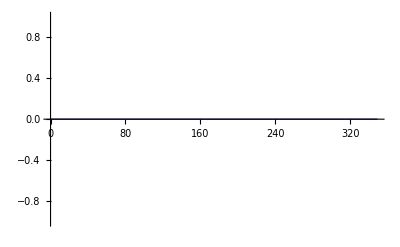

```mathematica
Plot[1000dif/.{FR$MU->1,veps->0.001,ee->1,MT->175},{MH,0,349}]
```

```mathematica
Simplify[(testHS2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2]/.{MT->175,MW->80,MZ->92.1,sw->0.22,MH->125},Assumptions->{FR$MU>0}]
```

(0.00250433 ee^2 (-125.+1361.02 FR$Eps-250. FR$Eps Log[FR$MU]))/FR$Eps

```mathematica
testFR3=Coefficient[testFR/.SumOver[Index[Colour,3],3]->SUNN,SUNN,0]
```

-1/(768 cw^4 FR$Eps MH^2 π^2 sw^4 vev^2)(-48 cw^4 ee^2 MH^2 sw^2 vev^2-24 cw^6 ee^2 MH^2 sw^2 vev^2-44 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2-22 cw^6 ee^2 FR$Eps MH^2 sw^2 vev^2-48 cw^4 ee^2 MH^2 sw^4 vev^2-44 cw^4 ee^2 FR$Eps MH^2 sw^4 vev^2-24 cw^2 ee^2 MH^2 sw^6 vev^2-22 cw^2 ee^2 FR$Eps MH^2 sw^6 vev^2-864 cw^4 FR$Eps lam^2 sw^4 vev^4+192 √3 cw^4 FR$Eps lam^2 π sw^4 vev^4+24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 Log[MW^2/FR$MU^2]-√(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]]+1/MH^24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 (-13 MH^2+12 MW^2+12 MW^2 Log[MW/FR$MU]+6 (MH^2-MW^2) Log[MW^2/FR$MU^2])+6 (-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]]+(24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^6-7 MH^4 MW^2+12 MH^2 MW^4+3 MW^2 (-MH^2+2 MW^2) √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]])/(MH^4-4 MH^2 MW^2)+24 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]+48 cw^4 ee^2 FR$Eps MH^2 MW^2 sw^2 vev^2 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-42 cw^4 ee^4 FR$Eps MH^2 vev^4 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-192 cw^4 FR$Eps lam^2 MH^2 sw^4 vev^4 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]+12 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+12 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^22 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^22 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+(12 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+(24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+(12 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+12 cw^6 ee^2 FR$Eps MH^4 sw^2 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^6 ee^2 FR$Eps MH^2 MZ^2 sw^2 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^4 ee^2 FR$Eps MH^4 sw^4 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+48 cw^4 ee^2 FR$Eps MH^2 MZ^2 sw^4 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+12 cw^2 ee^2 FR$Eps MH^4 sw^6 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^2 ee^2 FR$Eps MH^2 MZ^2 sw^6 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-21 cw^8 ee^4 FR$Eps MH^2 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-84 cw^6 ee^4 FR$Eps MH^2 sw^2 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-126 cw^4 ee^4 FR$Eps MH^2 sw^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-96 cw^4 FR$Eps lam^2 MH^2 sw^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-84 cw^2 ee^4 FR$Eps MH^2 sw^6 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-21 ee^4 FR$Eps MH^2 sw^8 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)])

```mathematica
testHS3=Simplify[Coefficient[testHS,SUNN,0],Assumptions->assume]
```

-(ee^2 (-12 cw^4 FR$Eps MH^9-4 cw^2 MH^7 MW^2-8 cw^4 MH^7 MW^2-4 cw^2 FR$Eps MH^7 MW^2+40 cw^4 FR$Eps MH^7 MW^2+16 cw^2 MH^5 MW^4+32 cw^4 MH^5 MW^4-16 FR$Eps MH^5 MW^4+16 cw^2 FR$Eps MH^5 MW^4+8 cw^4 FR$Eps MH^5 MW^4+64 FR$Eps MH^3 MW^6+96 cw^4 FR$Eps MH^3 MW^6+48 cw^4 FR$Eps MH^7 MZ^2+16 cw^2 MH^5 MW^2 MZ^2+32 cw^4 MH^5 MW^2 MZ^2+20 cw^2 FR$Eps MH^5 MW^2 MZ^2-160 cw^4 FR$Eps MH^5 MW^2 MZ^2-64 cw^2 MH^3 MW^4 MZ^2-128 cw^4 MH^3 MW^4 MZ^2+64 FR$Eps MH^3 MW^4 MZ^2-80 cw^2 FR$Eps MH^3 MW^4 MZ^2-32 cw^4 FR$Eps MH^3 MW^4 MZ^2-256 FR$Eps MH MW^6 MZ^2-384 cw^4 FR$Eps MH MW^6 MZ^2-16 cw^2 FR$Eps MH^3 MW^2 MZ^4+64 cw^2 FR$Eps MH MW^4 MZ^4+2 √3 cw^4 FR$Eps MH^9 π-8 √3 cw^4 FR$Eps MH^7 MW^2 π-8 √3 cw^4 FR$Eps MH^7 MZ^2 π+32 √3 cw^4 FR$Eps MH^5 MW^2 MZ^2 π+2 cw^4 FR$Eps MW^2 √(-MH^2+4 MW^2) (-MH^4+4 MH^2 MW^2+12 MW^4) (MH^2-4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]+2 cw^4 FR$Eps MW^2 √(-MH^2+4 MW^2) (MH^4-4 MH^2 MW^2-12 MW^4) (MH^2-4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]-2 cw^2 FR$Eps MH^6 MW^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+8 cw^2 FR$Eps MH^4 MW^4 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+cw^4 FR$Eps MH^6 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+4 cw^2 FR$Eps MH^4 MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-4 cw^4 FR$Eps MH^4 MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+16 FR$Eps MH^2 MW^4 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-16 cw^2 FR$Eps MH^2 MW^4 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-64 FR$Eps MW^6 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-4 cw^2 FR$Eps MH^2 MW^2 MZ^4 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+16 cw^2 FR$Eps MW^4 MZ^4 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+2 cw^2 FR$Eps MH^6 MW^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-8 cw^2 FR$Eps MH^4 MW^4 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-cw^4 FR$Eps MH^6 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-4 cw^2 FR$Eps MH^4 MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+4 cw^4 FR$Eps MH^4 MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-16 FR$Eps MH^2 MW^4 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+16 cw^2 FR$Eps MH^2 MW^4 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+64 FR$Eps MW^6 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+4 cw^2 FR$Eps MH^2 MW^2 MZ^4 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-16 cw^2 FR$Eps MW^4 MZ^4 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+2 cw^4 FR$Eps MH^5 MW^2 MZ^2 Log[65536]-cw^4 FR$Eps MH^5 MW^2 MZ^2 Log[4294967296]-8 cw^2 FR$Eps MH^7 MW^2 Log[FR$MU]-16 cw^4 FR$Eps MH^7 MW^2 Log[FR$MU]+32 cw^2 FR$Eps MH^5 MW^4 Log[FR$MU]+64 cw^4 FR$Eps MH^5 MW^4 Log[FR$MU]+32 cw^2 FR$Eps MH^5 MW^2 MZ^2 Log[FR$MU]+64 cw^4 FR$Eps MH^5 MW^2 MZ^2 Log[FR$MU]-128 cw^2 FR$Eps MH^3 MW^4 MZ^2 Log[FR$MU]-256 cw^4 FR$Eps MH^3 MW^4 MZ^2 Log[FR$MU]+16 cw^4 FR$Eps MH^7 MW^2 Log[MW]-64 cw^4 FR$Eps MH^5 MW^4 Log[MW]-64 cw^4 FR$Eps MH^5 MW^2 MZ^2 Log[MW]+256 cw^4 FR$Eps MH^3 MW^4 MZ^2 Log[MW]+8 cw^2 FR$Eps MH^7 MW^2 Log[MZ]-32 cw^2 FR$Eps MH^5 MW^4 Log[MZ]-32 cw^2 FR$Eps MH^5 MW^2 MZ^2 Log[MZ]+128 cw^2 FR$Eps MH^3 MW^4 MZ^2 Log[MZ]))/(128 cw^4 FR$Eps MH^3 (MH-2 MW) MW^2 (MH+2 MW) (MH-2 MZ) (MH+2 MZ) π^2 sw^2)

```mathematica
dif3=(testHS3-testFR3/.lam->MH^2/2/vev^2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2];
```

```mathematica
Simplify[dif3/.lam->MH^2/2/vev^2/.vev->2MW sw/ee/.cw->Sqrt[1-sw^2]/.sw->Sqrt[1-MW^2/MZ^2]/.{MT->175,MW->80,MZ->92.1,MH->125},Assumptions->{FR$MU>0}]
```

0.-1.47105×10^-15 ee^2-6.93889×10^-17 ee^2 Log[FR$MU]

```mathematica
massFR=-Simplify[Coefficient[UV$vertlist[[13,2]]/ⅈ/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2]},SP[2,2],0],Assumptions->assume]-MH^2*testFR/.{FeynArts`SumOver[FeynArts`Index[Colour,3],3]->SUNN,SumOver[Index[Colour,3],3]->SUNN}
```

1/(768 cw^4 FR$Eps π^2 sw^4 vev^2)(96 cw^4 MH^2 MT^2 SUNN sw^4+608 cw^4 FR$Eps MH^2 MT^2 SUNN sw^4-48 cw^4 ee^2 MH^2 sw^2 vev^2-24 cw^6 ee^2 MH^2 sw^2 vev^2-44 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2-22 cw^6 ee^2 FR$Eps MH^2 sw^2 vev^2-48 cw^4 ee^2 MH^2 sw^4 vev^2-44 cw^4 ee^2 FR$Eps MH^2 sw^4 vev^2-24 cw^2 ee^2 MH^2 sw^6 vev^2-22 cw^2 ee^2 FR$Eps MH^2 sw^6 vev^2-864 cw^4 FR$Eps lam^2 sw^4 vev^4+192 √3 cw^4 FR$Eps lam^2 π sw^4 vev^4-288 cw^4 FR$Eps MT^2 SUNN sw^4 Re[MH^2 Log[MT^2/FR$MU^2]-√(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]]+1/MH^232 cw^4 FR$Eps MT^2 SUNN sw^4 Re[MH^2 (-13 MH^2+12 MT^2+12 MT^2 Log[MT/FR$MU]+6 (MH^2-MT^2) Log[MT^2/FR$MU^2])+6 (-MH^2+MT^2) √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]]+(192 cw^4 FR$Eps MT^2 SUNN sw^4 Re[MH^6-7 MH^4 MT^2+12 MH^2 MT^4+3 MT^2 (-MH^2+2 MT^2) √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]])/(MH^4-4 MH^2 MT^2)-288 cw^4 FR$Eps MH^4 MT^2 SUNN sw^4 Re[1/MH^2-(2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^6-4 MH^4 MT^2)]+576 cw^4 FR$Eps MH^2 MT^4 SUNN sw^4 Re[1/MH^2-(2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^6-4 MH^4 MT^2)]+24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 Log[MW^2/FR$MU^2]-√(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]]+1/MH^24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 (-13 MH^2+12 MW^2+12 MW^2 Log[MW/FR$MU]+6 (MH^2-MW^2) Log[MW^2/FR$MU^2])+6 (-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]]+(24 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^6-7 MH^4 MW^2+12 MH^2 MW^4+3 MW^2 (-MH^2+2 MW^2) √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]])/(MH^4-4 MH^2 MW^2)+24 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]+48 cw^4 ee^2 FR$Eps MH^2 MW^2 sw^2 vev^2 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-42 cw^4 ee^4 FR$Eps MH^2 vev^4 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-192 cw^4 FR$Eps lam^2 MH^2 sw^4 vev^4 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]+12 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+12 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^22 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+1/MH^22 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^2 (-13 MH^2+12 MZ^2+12 MZ^2 Log[MZ/FR$MU]+6 (MH^2-MZ^2) Log[MZ^2/FR$MU^2])+6 (-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+(12 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+(24 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+(12 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^4-4 MH^2 MZ^2)+12 cw^6 ee^2 FR$Eps MH^4 sw^2 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^6 ee^2 FR$Eps MH^2 MZ^2 sw^2 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^4 ee^2 FR$Eps MH^4 sw^4 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+48 cw^4 ee^2 FR$Eps MH^2 MZ^2 sw^4 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+12 cw^2 ee^2 FR$Eps MH^4 sw^6 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+24 cw^2 ee^2 FR$Eps MH^2 MZ^2 sw^6 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-21 cw^8 ee^4 FR$Eps MH^2 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-84 cw^6 ee^4 FR$Eps MH^2 sw^2 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-126 cw^4 ee^4 FR$Eps MH^2 sw^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-96 cw^4 FR$Eps lam^2 MH^2 sw^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-84 cw^2 ee^4 FR$Eps MH^2 sw^6 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-21 ee^4 FR$Eps MH^2 sw^8 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)])-1/(256 cw^4 FR$Eps MH^2 π^2 sw^4 vev^2)(192 cw^4 MH^2 MT^4 SUNN sw^4+448 cw^4 FR$Eps MH^2 MT^4 SUNN sw^4-16 cw^4 ee^2 MH^2 MW^2 sw^2 vev^2+24 cw^4 ee^2 FR$Eps MH^2 MW^2 sw^2 vev^2-8 cw^6 ee^2 MH^2 MZ^2 sw^2 vev^2+12 cw^6 ee^2 FR$Eps MH^2 MZ^2 sw^2 vev^2-48 cw^4 lam MH^4 sw^4 vev^2-48 cw^4 FR$Eps lam MH^4 sw^4 vev^2-32 cw^4 lam MH^2 MW^2 sw^4 vev^2-32 cw^4 FR$Eps lam MH^2 MW^2 sw^4 vev^2-16 cw^4 ee^2 MH^2 MZ^2 sw^4 vev^2+24 cw^4 ee^2 FR$Eps MH^2 MZ^2 sw^4 vev^2-16 cw^4 lam MH^2 MZ^2 sw^4 vev^2-16 cw^4 FR$Eps lam MH^2 MZ^2 sw^4 vev^2-8 cw^2 ee^2 MH^2 MZ^2 sw^6 vev^2+12 cw^2 ee^2 FR$Eps MH^2 MZ^2 sw^6 vev^2-14 cw^4 ee^4 MH^2 vev^4-7 cw^8 ee^4 MH^2 vev^4-20 cw^4 ee^4 FR$Eps MH^2 vev^4-10 cw^8 ee^4 FR$Eps MH^2 vev^4-28 cw^6 ee^4 MH^2 sw^2 vev^4-40 cw^6 ee^4 FR$Eps MH^2 sw^2 vev^4-42 cw^4 ee^4 MH^2 sw^4 vev^4-60 cw^4 ee^4 FR$Eps MH^2 sw^4 vev^4-384 cw^4 lam^2 MH^2 sw^4 vev^4-1056 cw^4 FR$Eps lam^2 MH^2 sw^4 vev^4+160 √3 cw^4 FR$Eps lam^2 MH^2 π sw^4 vev^4-28 cw^2 ee^4 MH^2 sw^6 vev^4-40 cw^2 ee^4 FR$Eps MH^2 sw^6 vev^4-7 ee^4 MH^2 sw^8 vev^4-10 ee^4 FR$Eps MH^2 sw^8 vev^4+576 cw^4 FR$Eps lam^2 MH^2 sw^4 vev^4 Log[MH/FR$MU]+48 cw^4 FR$Eps lam MH^4 sw^4 vev^2 Log[MH^2/FR$MU^2]+32 cw^4 ee^2 FR$Eps MH^2 MW^2 sw^2 vev^2 Log[MW^2/FR$MU^2]+32 cw^4 FR$Eps lam MH^2 MW^2 sw^4 vev^2 Log[MW^2/FR$MU^2]+16 cw^6 ee^2 FR$Eps MH^2 MZ^2 sw^2 vev^2 Log[MZ^2/FR$MU^2]+32 cw^4 ee^2 FR$Eps MH^2 MZ^2 sw^4 vev^2 Log[MZ^2/FR$MU^2]+16 cw^4 FR$Eps lam MH^2 MZ^2 sw^4 vev^2 Log[MZ^2/FR$MU^2]+16 cw^2 ee^2 FR$Eps MH^2 MZ^2 sw^6 vev^2 Log[MZ^2/FR$MU^2]-192 cw^4 FR$Eps MT^4 SUNN sw^4 Re[MH^2 Log[MT^2/FR$MU^2]-√(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]]+(64 cw^4 FR$Eps MT^2 SUNN sw^4 Re[MH^6-7 MH^4 MT^2+12 MH^2 MT^4+3 MT^2 (-MH^2+2 MT^2) √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)]])/(MH^2-4 MT^2)-96 cw^4 FR$Eps MH^6 MT^2 SUNN sw^4 Re[1/MH^2-(2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^6-4 MH^4 MT^2)]+192 cw^4 FR$Eps MH^4 MT^4 SUNN sw^4 Re[1/MH^2-(2 MT^2 √(MH^4-4 MH^2 MT^2) Log[(-MH^2+2 MT^2+√(MH^4-4 MH^2 MT^2))/(2 MT^2)])/(MH^6-4 MH^4 MT^2)]+2 cw^4 FR$Eps vev^2 (-8 ee^2 MW^2 sw^2+7 ee^4 vev^2+32 lam^2 sw^4 vev^2) Re[MH^2 Log[MW^2/FR$MU^2]-√(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]]+(8 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[MH^6-7 MH^4 MW^2+12 MH^2 MW^4+3 MW^2 (-MH^2+2 MW^2) √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)]])/(MH^2-4 MW^2)+8 cw^4 ee^2 FR$Eps MH^6 sw^2 vev^2 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]+16 cw^4 ee^2 FR$Eps MH^4 MW^2 sw^2 vev^2 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-14 cw^4 ee^4 FR$Eps MH^4 vev^4 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-64 cw^4 FR$Eps lam^2 MH^4 sw^4 vev^4 Re[1/MH^2-(2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(2 MW^2)])/(MH^6-4 MH^4 MW^2)]-8 cw^6 ee^2 FR$Eps MZ^2 sw^2 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]-16 cw^4 ee^2 FR$Eps MZ^2 sw^4 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]-8 cw^2 ee^2 FR$Eps MZ^2 sw^6 vev^2 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+7 cw^8 ee^4 FR$Eps vev^4 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+28 cw^6 ee^4 FR$Eps sw^2 vev^4 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+42 cw^4 ee^4 FR$Eps sw^4 vev^4 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+32 cw^4 FR$Eps lam^2 sw^4 vev^4 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+28 cw^2 ee^4 FR$Eps sw^6 vev^4 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+7 ee^4 FR$Eps sw^8 vev^4 Re[MH^2 Log[MZ^2/FR$MU^2]-√(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]]+(4 cw^6 ee^2 FR$Eps sw^2 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^2-4 MZ^2)+(8 cw^4 ee^2 FR$Eps sw^4 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^2-4 MZ^2)+(4 cw^2 ee^2 FR$Eps sw^6 vev^2 Re[MH^6-7 MH^4 MZ^2+12 MH^2 MZ^4+3 MZ^2 (-MH^2+2 MZ^2) √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)]])/(MH^2-4 MZ^2)+4 cw^6 ee^2 FR$Eps MH^6 sw^2 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+8 cw^6 ee^2 FR$Eps MH^4 MZ^2 sw^2 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+8 cw^4 ee^2 FR$Eps MH^6 sw^4 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+16 cw^4 ee^2 FR$Eps MH^4 MZ^2 sw^4 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+4 cw^2 ee^2 FR$Eps MH^6 sw^6 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]+8 cw^2 ee^2 FR$Eps MH^4 MZ^2 sw^6 vev^2 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-7 cw^8 ee^4 FR$Eps MH^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-28 cw^6 ee^4 FR$Eps MH^4 sw^2 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-42 cw^4 ee^4 FR$Eps MH^4 sw^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-32 cw^4 FR$Eps lam^2 MH^4 sw^4 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-28 cw^2 ee^4 FR$Eps MH^4 sw^6 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)]-7 ee^4 FR$Eps MH^4 sw^8 vev^4 Re[1/MH^2-(2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(2 MZ^2)])/(MH^6-4 MH^4 MZ^2)])

```mathematica
massHS=Simplify[ComplexExpand[(dMHsq1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

-1/(256 cw^4 FR$Eps MH MW^2 π^2 sw^2)ee^2 (-30 cw^4 MH^5-54 cw^4 FR$Eps MH^5+8 cw^2 MH^3 MW^2+12 cw^4 MH^3 MW^2+16 cw^2 FR$Eps MH^3 MW^2+28 cw^4 FR$Eps MH^3 MW^2-32 MH MW^4-72 cw^4 MH MW^4-48 FR$Eps MH MW^4-72 cw^4 FR$Eps MH MW^4-2 cw^4 MH^3 MZ^2-2 cw^4 FR$Eps MH^3 MZ^2-4 cw^2 MH MW^2 MZ^2+12 cw^2 FR$Eps MH MW^2 MZ^2+6 √3 cw^4 FR$Eps MH^5 π-8 cw^4 MH^3 MT^2 SUNN-16 cw^4 FR$Eps MH^3 MT^2 SUNN+48 cw^4 MH MT^4 SUNN+80 cw^4 FR$Eps MH MT^4 SUNN+4 cw^4 FR$Eps MT^2 (-MH^2+4 MT^2)^(3/2) SUNN Arg[(-ⅈ MH+√(-MH^2+4 MT^2))/(ⅈ MH+√(-MH^2+4 MT^2))]-4 cw^4 FR$Eps MT^2 (-MH^2+4 MT^2)^(3/2) SUNN Arg[(ⅈ MH+√(-MH^2+4 MT^2))/(-ⅈ MH+√(-MH^2+4 MT^2))]-2 cw^4 FR$Eps MH^4 √(-MH^2+4 MW^2) Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]+8 cw^4 FR$Eps MH^2 MW^2 √(-MH^2+4 MW^2) Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]-24 cw^4 FR$Eps MW^4 √(-MH^2+4 MW^2) Arg[(-ⅈ MH+√(-MH^2+4 MW^2))/(ⅈ MH+√(-MH^2+4 MW^2))]+2 cw^4 FR$Eps MH^4 √(-MH^2+4 MW^2) Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]-8 cw^4 FR$Eps MH^2 MW^2 √(-MH^2+4 MW^2) Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]+24 cw^4 FR$Eps MW^4 √(-MH^2+4 MW^2) Arg[(ⅈ MH+√(-MH^2+4 MW^2))/(-ⅈ MH+√(-MH^2+4 MW^2))]-cw^4 FR$Eps MH^4 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+4 cw^2 FR$Eps MH^2 MW^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]-16 FR$Eps MW^4 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+4 cw^2 FR$Eps MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH+√(-MH^2+4 MZ^2))/(ⅈ MH+√(-MH^2+4 MZ^2))]+cw^4 FR$Eps MH^4 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-4 cw^2 FR$Eps MH^2 MW^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+16 FR$Eps MW^4 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-4 cw^2 FR$Eps MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH+√(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+cw^4 FR$Eps MH^5 Log[16]+cw^4 FR$Eps MH^5 Log[256]-cw^4 FR$Eps MH^5 Log[4096]-60 cw^4 FR$Eps MH^5 Log[FR$MU]+16 cw^2 FR$Eps MH^3 MW^2 Log[FR$MU]+24 cw^4 FR$Eps MH^3 MW^2 Log[FR$MU]-64 FR$Eps MH MW^4 Log[FR$MU]-144 cw^4 FR$Eps MH MW^4 Log[FR$MU]-4 cw^4 FR$Eps MH^3 MZ^2 Log[FR$MU]-8 cw^2 FR$Eps MH MW^2 MZ^2 Log[FR$MU]-16 cw^4 FR$Eps MH^3 MT^2 SUNN Log[FR$MU]+96 cw^4 FR$Eps MH MT^4 SUNN Log[FR$MU]+48 cw^4 FR$Eps MH^5 Log[MH]+16 cw^4 FR$Eps MH^3 MT^2 SUNN Log[MT]-96 cw^4 FR$Eps MH MT^4 SUNN Log[MT]+8 cw^4 FR$Eps MH^5 Log[MW]-24 cw^4 FR$Eps MH^3 MW^2 Log[MW]+144 cw^4 FR$Eps MH MW^4 Log[MW]+4 cw^4 FR$Eps MH^5 Log[MZ]-16 cw^2 FR$Eps MH^3 MW^2 Log[MZ]+64 FR$Eps MH MW^4 Log[MZ]+4 cw^4 FR$Eps MH^3 MZ^2 Log[MZ]+8 cw^2 FR$Eps MH MW^2 MZ^2 Log[MZ])

```mathematica
Simplify[Coefficient[massFR-massHS,SUNN,1]/.lam->MH^2/2/vev^2/.vev->2MW sw/ee/.cw->Sqrt[1-sw^2]/.sw->Sqrt[1-MW^2/MZ^2]/.{MT->175,MW->80,MZ->92.1,MH->125},Assumptions->{FR$MU>0}]
```

0.

## G0

```mathematica
testHS=Simplify[ComplexExpand[(dZG01[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

1/(128 π^2 sw^2)ee^2 (8+6/cw^2+8/FR$Eps+4/(cw^2 FR$Eps)-(4 MH^2)/(cw^2 MZ^2)+(2 MH^4)/(MW^2 MZ^2)-(4 MT^2 SUNN)/MW^2-(4 MT^2 SUNN)/(FR$Eps MW^2)+((cw^2 (MH^7-3 MH^5 MZ^2)+MH MW^2 (-2 MH^4+7 MH^2 MZ^2-5 MZ^4)) Arg[(MH^2-2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(MH^2+√(MH^4-4 MH^2 MZ^2))])/(cw^2 MW^2 MZ^4 √(-MH^2+4 MZ^2))+((-cw^2 (MH^7-3 MH^5 MZ^2)+MH MW^2 (2 MH^4-7 MH^2 MZ^2+5 MZ^4)) Arg[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(-MH^2+√(MH^4-4 MH^2 MZ^2))])/(cw^2 MW^2 MZ^4 √(-MH^2+4 MZ^2))+(4 MT^4 SUNN Arg[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MW^2 MZ √(4 MT^2-MZ^2))-(2 MT^2 MZ SUNN Arg[(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MW^2 √(4 MT^2-MZ^2))-(4 MT^4 SUNN Arg[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MW^2 MZ √(4 MT^2-MZ^2))+(2 MT^2 MZ SUNN Arg[(MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(-MZ^2+√(-4 MT^2 MZ^2+MZ^4))])/(MW^2 √(4 MT^2-MZ^2))-(8 MW^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(MZ^2+√(-4 MW^2 MZ^2+MZ^4))])/(MZ √(4 MW^2-MZ^2))+(4 MZ Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(MZ^2+√(-4 MW^2 MZ^2+MZ^4))])/(√(4 MW^2-MZ^2))+(8 MW^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))])/(MZ √(4 MW^2-MZ^2))-(4 MZ Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))])/(√(4 MW^2-MZ^2))+(8 MH^6 Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(96 MH^4 MT^2 Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(16 MH^4 MT^2 Log[4])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(8 MH^6 MT^2 Log[4])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(16 MH^4 MW^2 Log[4])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(64 MH^2 MT^2 MW^2 Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(224 MH^2 MT^2 MW^2 Log[4])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(32 MH^6 MT^2 Log[4])/((MH-2 MZ) MZ^2 (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(64 MH^4 MT^2 MW^2 Log[4])/(cw^2 (MH-2 MZ) MZ^2 (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(24 MH^4 MZ^2 Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(4 MH^4 MZ^2 Log[4])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(32 MH^2 MT^2 MZ^2 Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(56 MH^2 MT^2 MZ^2 Log[4])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(2 MH^6 MZ^2 Log[4])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(24 MH^4 MT^2 MZ^2 Log[4])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(16 MH^2 MW^2 MZ^2 Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(56 MH^2 MW^2 MZ^2 Log[4])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(8 MH^2 MZ^4 Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(14 MH^2 MZ^4 Log[4])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(6 MH^4 MZ^4 Log[4])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(64 MW^2 MZ^4 Log[4])/((2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(40 MW^2 MZ^4 Log[4])/(cw^2 (2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(32 MZ^6 Log[4])/((2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(10 MZ^6 Log[4])/(cw^2 (2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(256 MT^2 MW^2 MZ^2 Log[4])/((2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(160 MT^2 MW^2 MZ^2 Log[4])/(cw^2 (2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(128 MT^2 MZ^4 Log[4])/((2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(40 MT^2 MZ^4 Log[4])/(cw^2 (2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(10 MH^2 Log[4])/(cw^2 (MH^2-4 MZ^2))-(6 MH^4 Log[4])/(MW^2 (MH^2-4 MZ^2))-(4 MH^4 Log[4])/(cw^2 MZ^2 (MH^2-4 MZ^2))+(2 MH^6 Log[4])/(MW^2 MZ^2 (MH^2-4 MZ^2))+(6 MZ^2 Log[4])/(cw^2 (MH^2-4 MZ^2))-(16 MW^2 Log[4])/(4 MW^2-MZ^2)+(32 MH^2 MT^4 SUNN Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(16 MH^2 MT^2 MZ^2 SUNN Log[4])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(8 MH^2 MT^4 MZ^2 SUNN Log[4])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(4 MH^2 MT^2 MZ^4 SUNN Log[4])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(32 MT^4 MZ^4 SUNN Log[4])/(MW^2 (2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(16 MT^2 MZ^6 SUNN Log[4])/(MW^2 (2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(128 MT^4 MZ^2 SUNN Log[4])/((2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(64 MT^2 MZ^4 SUNN Log[4])/((2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(8 MT^4 SUNN Log[4])/(MW^2 (4 MT^2-MZ^2))-(2 MT^2 SUNN Log[16])/MW^2+Log[256]/cw^2+Log[65536]-(32 MW^2 Log[1/(2 MZ^2)])/(4 MW^2-MZ^2)+(16 MZ^2 Log[1/(2 MZ^2)])/(4 MW^2-MZ^2)+(16 MT^4 SUNN Log[1/(2 MZ^2)])/(MW^2 (4 MT^2-MZ^2))-(8 MT^2 MZ^2 SUNN Log[1/(2 MZ^2)])/(MW^2 (4 MT^2-MZ^2))-(10 MH^2 Log[MZ/MH])/(cw^2 (MH^2-4 MZ^2))-(4 MH^6 Log[MZ/MH])/(cw^2 MZ^4 (MH^2-4 MZ^2))+(2 MH^8 Log[MZ/MH])/(MW^2 MZ^4 (MH^2-4 MZ^2))+(14 MH^4 Log[MZ/MH])/(cw^2 MZ^2 (MH^2-4 MZ^2))-(6 MH^6 Log[MZ/MH])/(MW^2 MZ^2 (MH^2-4 MZ^2))+(8 MT^4 SUNN Log[4 MT^2 MZ^2])/(MW^2 (4 MT^2-MZ^2))-(4 MT^2 MZ^2 SUNN Log[4 MT^2 MZ^2])/(MW^2 (4 MT^2-MZ^2))-(16 MW^2 Log[4 MW^2 MZ^2])/(4 MW^2-MZ^2)-(8 MZ^2 Log[4 MW^2 MZ^2])/(-4 MW^2+MZ^2)-(6 MH^2 Log[FR$MU^2/(MH^2 π)])/(cw^2 (MH^2-4 MZ^2))+(4 MH^4 Log[FR$MU^2/(MH^2 π)])/(MW^2 (MH^2-4 MZ^2))+(4 MH^4 Log[FR$MU^2/(MH^2 π)])/(cw^2 MZ^2 (MH^2-4 MZ^2))-(2 MH^6 Log[FR$MU^2/(MH^2 π)])/(MW^2 MZ^2 (MH^2-4 MZ^2))-(4 MZ^2 Log[FR$MU^2/(MH^2 π)])/(cw^2 (MH^2-4 MZ^2))-(8 MT^4 SUNN Log[FR$MU^2/(MT^2 π)])/(MW^2 (4 MT^2-MZ^2))+(16 MW^2 Log[FR$MU^2/(MW^2 π)])/(4 MW^2-MZ^2)-(4 MH^2 Log[FR$MU^2/(MZ^2 π)])/(cw^2 (MH^2-4 MZ^2))+(2 MH^4 Log[FR$MU^2/(MZ^2 π)])/(MW^2 (MH^2-4 MZ^2))-(2 MZ^2 Log[FR$MU^2/(MZ^2 π)])/(cw^2 (MH^2-4 MZ^2))+8 Log[π]+(4 Log[π])/cw^2-(4 MT^2 SUNN Log[π])/MW^2+(8 MH^6 Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(96 MH^4 MT^2 Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(16 MH^4 MT^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(8 MH^6 MT^2 Log[(MZ^2 π)/FR$MU^2])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(16 MH^4 MW^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(64 MH^2 MT^2 MW^2 Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(224 MH^2 MT^2 MW^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(32 MH^6 MT^2 Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) MZ^2 (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(64 MH^4 MT^2 MW^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) MZ^2 (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(24 MH^4 MZ^2 Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(4 MH^4 MZ^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(32 MH^2 MT^2 MZ^2 Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(56 MH^2 MT^2 MZ^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(2 MH^6 MZ^2 Log[(MZ^2 π)/FR$MU^2])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(24 MH^4 MT^2 MZ^2 Log[(MZ^2 π)/FR$MU^2])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(16 MH^2 MW^2 MZ^2 Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(56 MH^2 MW^2 MZ^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(8 MH^2 MZ^4 Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(14 MH^2 MZ^4 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(6 MH^4 MZ^4 Log[(MZ^2 π)/FR$MU^2])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(64 MW^2 MZ^4 Log[(MZ^2 π)/FR$MU^2])/((2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(40 MW^2 MZ^4 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(32 MZ^6 Log[(MZ^2 π)/FR$MU^2])/((2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(10 MZ^6 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(256 MT^2 MW^2 MZ^2 Log[(MZ^2 π)/FR$MU^2])/((2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(160 MT^2 MW^2 MZ^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(128 MT^2 MZ^4 Log[(MZ^2 π)/FR$MU^2])/((2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(40 MT^2 MZ^4 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(32 MH^2 MT^4 SUNN Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(16 MH^2 MT^2 MZ^2 SUNN Log[(MZ^2 π)/FR$MU^2])/((MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))-(8 MH^2 MT^4 MZ^2 SUNN Log[(MZ^2 π)/FR$MU^2])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(4 MH^2 MT^2 MZ^4 SUNN Log[(MZ^2 π)/FR$MU^2])/(MW^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))+(32 MT^4 MZ^4 SUNN Log[(MZ^2 π)/FR$MU^2])/(MW^2 (2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(16 MT^2 MZ^6 SUNN Log[(MZ^2 π)/FR$MU^2])/(MW^2 (2 MW-MZ) (-2 MT+MZ) (2 MT+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))-(128 MT^4 MZ^2 SUNN Log[(MZ^2 π)/FR$MU^2])/((2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ))+(64 MT^2 MZ^4 SUNN Log[(MZ^2 π)/FR$MU^2])/((2 MT-MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (-MH+2 MZ) (MH+2 MZ)))

```mathematica
UV$vertlist[[14,1]]/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2]}
```

{{G0,1},{G0,2}}

```mathematica
testFR=Simplify[Coefficient[UV$vertlist[[14,2]]/ⅈ/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2]},SP[2,2]],Assumptions->assume]
```

-1/(384 cw^2 FR$Eps π^2 sw^4 vev^2)(-24 cw^2 ee^2 sw^2 vev^2-12 cw^4 ee^2 sw^2 vev^2-22 cw^2 ee^2 FR$Eps sw^2 vev^2-17 cw^4 ee^2 FR$Eps sw^2 vev^2-(12 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2)/MZ^4+(18 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2)/MZ^2-24 cw^2 ee^2 sw^4 vev^2-34 cw^2 ee^2 FR$Eps sw^4 vev^2-(24 cw^2 ee^2 FR$Eps MH^4 sw^4 vev^2)/MZ^4+(36 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2)/MZ^2-12 ee^2 sw^6 vev^2-17 ee^2 FR$Eps sw^6 vev^2-(12 ee^2 FR$Eps MH^4 sw^6 vev^2)/MZ^4+(18 ee^2 FR$Eps MH^2 sw^6 vev^2)/MZ^2-(12 ee^2 FR$Eps MH (MH^6-5 MH^4 MZ^2+6 MH^2 MZ^4-2 MZ^6) sw^2 (cw^2+sw^2)^2 vev^2 Im[Log[MH+ⅈ √(-MH^2+4 MZ^2)]])/(MZ^6 √(-MH^2+4 MZ^2))-(12 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Log[MH/FR$MU])/MZ^4+(12 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Log[MH/FR$MU])/MZ^2-(24 cw^2 ee^2 FR$Eps MH^4 sw^4 vev^2 Log[MH/FR$MU])/MZ^4+(24 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Log[MH/FR$MU])/MZ^2-(12 ee^2 FR$Eps MH^4 sw^6 vev^2 Log[MH/FR$MU])/MZ^4+(12 ee^2 FR$Eps MH^2 sw^6 vev^2 Log[MH/FR$MU])/MZ^2-6 cw^4 ee^2 FR$Eps sw^2 vev^2 Log[MH/MZ]+(12 cw^4 ee^2 FR$Eps MH^6 sw^2 vev^2 Log[MH/MZ])/MZ^6-(30 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Log[MH/MZ])/MZ^4+(24 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Log[MH/MZ])/MZ^2-12 cw^2 ee^2 FR$Eps sw^4 vev^2 Log[MH/MZ]+(24 cw^2 ee^2 FR$Eps MH^6 sw^4 vev^2 Log[MH/MZ])/MZ^6-(60 cw^2 ee^2 FR$Eps MH^4 sw^4 vev^2 Log[MH/MZ])/MZ^4+(48 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Log[MH/MZ])/MZ^2-6 ee^2 FR$Eps sw^6 vev^2 Log[MH/MZ]+(12 ee^2 FR$Eps MH^6 sw^6 vev^2 Log[MH/MZ])/MZ^6-(30 ee^2 FR$Eps MH^4 sw^6 vev^2 Log[MH/MZ])/MZ^4+(24 ee^2 FR$Eps MH^2 sw^6 vev^2 Log[MH/MZ])/MZ^2-12 cw^4 ee^2 FR$Eps sw^2 vev^2 Log[MZ/FR$MU]+(12 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Log[MZ/FR$MU])/MZ^2-24 cw^2 ee^2 FR$Eps sw^4 vev^2 Log[MZ/FR$MU]+(24 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Log[MZ/FR$MU])/MZ^2-12 ee^2 FR$Eps sw^6 vev^2 Log[MZ/FR$MU]+(12 ee^2 FR$Eps MH^2 sw^6 vev^2 Log[MZ/FR$MU])/MZ^2+6 cw^4 ee^2 FR$Eps sw^2 vev^2 Log[(MH MZ)/FR$MU^2]+(6 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^4-(12 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^2+12 cw^2 ee^2 FR$Eps sw^4 vev^2 Log[(MH MZ)/FR$MU^2]+(12 cw^2 ee^2 FR$Eps MH^4 sw^4 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^4-(24 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^2+6 ee^2 FR$Eps sw^6 vev^2 Log[(MH MZ)/FR$MU^2]+(6 ee^2 FR$Eps MH^4 sw^6 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^4-(12 ee^2 FR$Eps MH^2 sw^6 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^2+6 ee^2 FR$Eps sw^2 (cw^2+sw^2)^2 vev^2 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]+1/MZ^6cw^4 ee^2 FR$Eps sw^2 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]+1/MZ^62 cw^2 ee^2 FR$Eps sw^4 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]+1/MZ^6ee^2 FR$Eps sw^6 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]-1/MZ^63 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]-1/MZ^66 cw^2 ee^2 FR$Eps sw^4 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]-1/MZ^63 ee^2 FR$Eps sw^6 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]+12 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+6 cw^4 ee^2 FR$Eps MZ^2 sw^2 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+24 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+12 cw^2 ee^2 FR$Eps MZ^2 sw^4 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+12 ee^2 FR$Eps MH^2 sw^6 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+6 ee^2 FR$Eps MZ^2 sw^6 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]-96 cw^2 FR$Eps lam^2 sw^4 vev^4 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+(12 cw^2 ee^2 FR$Eps sw^2 vev^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/MZ^2+1/MZ^42 cw^2 ee^2 FR$Eps sw^2 vev^2 Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+24 cw^2 ee^2 FR$Eps MW^2 sw^2 vev^2 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]+12 cw^2 ee^2 FR$Eps MZ^2 sw^2 vev^2 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-3 cw^2 ee^4 FR$Eps vev^4 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-(12 cw^2 ee^2 FR$Eps sw^2 vev^2 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^4+MZ^6)+48 cw^2 MT^2 sw^4 SumOver[Index[Colour,3],3]+304 cw^2 FR$Eps MT^2 sw^4 SumOver[Index[Colour,3],3]-(144 cw^2 FR$Eps MT^2 sw^4 Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]] SumOver[Index[Colour,3],3])/MZ^2+1/MZ^416 cw^2 FR$Eps MT^2 sw^4 Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]] SumOver[Index[Colour,3],3]+96 cw^2 FR$Eps MT^4 sw^4 Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))] SumOver[Index[Colour,3],3]-144 cw^2 FR$Eps MT^2 MZ^2 sw^4 Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))] SumOver[Index[Colour,3],3]+1/(4 MT^2 MZ^4-MZ^6)96 cw^2 FR$Eps MT^2 sw^4 Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]] SumOver[Index[Colour,3],3])

```mathematica
testFR2=Coefficient[testFR/.SumOver[Index[Colour,3],3]->SUNN,SUNN]
```

-1/(384 cw^2 FR$Eps π^2 sw^4 vev^2)(48 cw^2 MT^2 sw^4+304 cw^2 FR$Eps MT^2 sw^4-(144 cw^2 FR$Eps MT^2 sw^4 Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/MZ^2+1/MZ^416 cw^2 FR$Eps MT^2 sw^4 Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]+96 cw^2 FR$Eps MT^4 sw^4 Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))]-144 cw^2 FR$Eps MT^2 MZ^2 sw^4 Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))]+(96 cw^2 FR$Eps MT^2 sw^4 Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(4 MT^2 MZ^4-MZ^6))

```mathematica
testHS2=Simplify[Coefficient[testHS,SUNN,1],Assumptions->assume]
```

-(ee^2 MT^2 (FR$Eps (2 MT^2-MZ^2) Arg[(-ⅈ MZ+√(4 MT^2-MZ^2))/(ⅈ MZ+√(4 MT^2-MZ^2))]+FR$Eps (-2 MT^2+MZ^2) Arg[(ⅈ MZ+√(4 MT^2-MZ^2))/(-ⅈ MZ+√(4 MT^2-MZ^2))]+2 MZ √(4 MT^2-MZ^2) (1+FR$Eps+2 FR$Eps Log[FR$MU]-2 FR$Eps Log[MT])))/(64 FR$Eps MW^2 MZ √(4 MT^2-MZ^2) π^2 sw^2)

```mathematica
dif=FullSimplify[(testHS2-testFR2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

-(ee^2 MT^2 (2 MT^2-MZ^2) (Arg[2 MT^2-MZ (MZ+ⅈ √(4 MT^2-MZ^2))]+Arg[2 MT^2+ⅈ MZ (ⅈ MZ+√(4 MT^2-MZ^2))]))/(64 MW^2 MZ √(4 MT^2-MZ^2) π^2 sw^2)

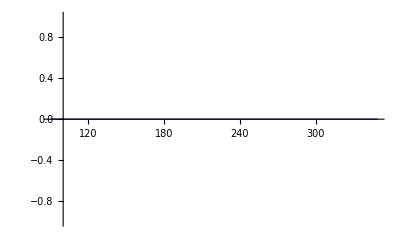

```mathematica
Plot[1000dif/.{FR$MU->1,ee->1,MT->175,sw->0.2},{MZ,90,349}]
```

```mathematica
Simplify[(testHS2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2]/.{MT->175,MW->80,MZ->92.1,sw->0.22,MH->125},Assumptions->{FR$MU>0}]
```

-(5.03298×10^-6 ee^2 (62197.9-636483. FR$Eps+124396. FR$Eps Log[FR$MU]))/FR$Eps

```mathematica
testFR3=Coefficient[testFR/.SumOver[Index[Colour,3],3]->SUNN,SUNN,0]
```

-1/(384 cw^2 FR$Eps π^2 sw^4 vev^2)(-24 cw^2 ee^2 sw^2 vev^2-12 cw^4 ee^2 sw^2 vev^2-22 cw^2 ee^2 FR$Eps sw^2 vev^2-17 cw^4 ee^2 FR$Eps sw^2 vev^2-(12 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2)/MZ^4+(18 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2)/MZ^2-24 cw^2 ee^2 sw^4 vev^2-34 cw^2 ee^2 FR$Eps sw^4 vev^2-(24 cw^2 ee^2 FR$Eps MH^4 sw^4 vev^2)/MZ^4+(36 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2)/MZ^2-12 ee^2 sw^6 vev^2-17 ee^2 FR$Eps sw^6 vev^2-(12 ee^2 FR$Eps MH^4 sw^6 vev^2)/MZ^4+(18 ee^2 FR$Eps MH^2 sw^6 vev^2)/MZ^2-(12 ee^2 FR$Eps MH (MH^6-5 MH^4 MZ^2+6 MH^2 MZ^4-2 MZ^6) sw^2 (cw^2+sw^2)^2 vev^2 Im[Log[MH+ⅈ √(-MH^2+4 MZ^2)]])/(MZ^6 √(-MH^2+4 MZ^2))-(12 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Log[MH/FR$MU])/MZ^4+(12 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Log[MH/FR$MU])/MZ^2-(24 cw^2 ee^2 FR$Eps MH^4 sw^4 vev^2 Log[MH/FR$MU])/MZ^4+(24 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Log[MH/FR$MU])/MZ^2-(12 ee^2 FR$Eps MH^4 sw^6 vev^2 Log[MH/FR$MU])/MZ^4+(12 ee^2 FR$Eps MH^2 sw^6 vev^2 Log[MH/FR$MU])/MZ^2-6 cw^4 ee^2 FR$Eps sw^2 vev^2 Log[MH/MZ]+(12 cw^4 ee^2 FR$Eps MH^6 sw^2 vev^2 Log[MH/MZ])/MZ^6-(30 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Log[MH/MZ])/MZ^4+(24 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Log[MH/MZ])/MZ^2-12 cw^2 ee^2 FR$Eps sw^4 vev^2 Log[MH/MZ]+(24 cw^2 ee^2 FR$Eps MH^6 sw^4 vev^2 Log[MH/MZ])/MZ^6-(60 cw^2 ee^2 FR$Eps MH^4 sw^4 vev^2 Log[MH/MZ])/MZ^4+(48 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Log[MH/MZ])/MZ^2-6 ee^2 FR$Eps sw^6 vev^2 Log[MH/MZ]+(12 ee^2 FR$Eps MH^6 sw^6 vev^2 Log[MH/MZ])/MZ^6-(30 ee^2 FR$Eps MH^4 sw^6 vev^2 Log[MH/MZ])/MZ^4+(24 ee^2 FR$Eps MH^2 sw^6 vev^2 Log[MH/MZ])/MZ^2-12 cw^4 ee^2 FR$Eps sw^2 vev^2 Log[MZ/FR$MU]+(12 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Log[MZ/FR$MU])/MZ^2-24 cw^2 ee^2 FR$Eps sw^4 vev^2 Log[MZ/FR$MU]+(24 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Log[MZ/FR$MU])/MZ^2-12 ee^2 FR$Eps sw^6 vev^2 Log[MZ/FR$MU]+(12 ee^2 FR$Eps MH^2 sw^6 vev^2 Log[MZ/FR$MU])/MZ^2+6 cw^4 ee^2 FR$Eps sw^2 vev^2 Log[(MH MZ)/FR$MU^2]+(6 cw^4 ee^2 FR$Eps MH^4 sw^2 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^4-(12 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^2+12 cw^2 ee^2 FR$Eps sw^4 vev^2 Log[(MH MZ)/FR$MU^2]+(12 cw^2 ee^2 FR$Eps MH^4 sw^4 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^4-(24 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^2+6 ee^2 FR$Eps sw^6 vev^2 Log[(MH MZ)/FR$MU^2]+(6 ee^2 FR$Eps MH^4 sw^6 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^4-(12 ee^2 FR$Eps MH^2 sw^6 vev^2 Log[(MH MZ)/FR$MU^2])/MZ^2+6 ee^2 FR$Eps sw^2 (cw^2+sw^2)^2 vev^2 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]+1/MZ^6cw^4 ee^2 FR$Eps sw^2 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]+1/MZ^62 cw^2 ee^2 FR$Eps sw^4 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]+1/MZ^6ee^2 FR$Eps sw^6 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]-1/MZ^63 cw^4 ee^2 FR$Eps sw^2 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]-1/MZ^66 cw^2 ee^2 FR$Eps sw^4 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]-1/MZ^63 ee^2 FR$Eps sw^6 vev^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]+12 cw^4 ee^2 FR$Eps MH^2 sw^2 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+6 cw^4 ee^2 FR$Eps MZ^2 sw^2 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+24 cw^2 ee^2 FR$Eps MH^2 sw^4 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+12 cw^2 ee^2 FR$Eps MZ^2 sw^4 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+12 ee^2 FR$Eps MH^2 sw^6 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+6 ee^2 FR$Eps MZ^2 sw^6 vev^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]-96 cw^2 FR$Eps lam^2 sw^4 vev^4 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+(12 cw^2 ee^2 FR$Eps sw^2 vev^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/MZ^2+1/MZ^42 cw^2 ee^2 FR$Eps sw^2 vev^2 Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+24 cw^2 ee^2 FR$Eps MW^2 sw^2 vev^2 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]+12 cw^2 ee^2 FR$Eps MZ^2 sw^2 vev^2 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-3 cw^2 ee^4 FR$Eps vev^4 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-(12 cw^2 ee^2 FR$Eps sw^2 vev^2 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^4+MZ^6))

```mathematica
testHS3=Simplify[Coefficient[testHS,SUNN,0],Assumptions->assume]
```

1/(128 cw^2 MW^2 MZ^4 π^2 sw^2)ee^2 (((cw^2 (MH^7-3 MH^5 MZ^2)+MH MW^2 (-2 MH^4+7 MH^2 MZ^2-5 MZ^4)) Arg[(MH^2-2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(MH^2+√(MH^4-4 MH^2 MZ^2))])/(√(-MH^2+4 MZ^2))+((-cw^2 (MH^7-3 MH^5 MZ^2)+MH MW^2 (2 MH^4-7 MH^2 MZ^2+5 MZ^4)) Arg[(-MH^2+2 MZ^2+√(MH^4-4 MH^2 MZ^2))/(-MH^2+√(MH^4-4 MH^2 MZ^2))])/(√(-MH^2+4 MZ^2))+1/(FR$Eps √(4 MW^2-MZ^2))2 (2 cw^2 FR$Eps MW^2 MZ^3 (2 MW^2-MZ^2) Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]+2 cw^2 FR$Eps MW^2 MZ^3 (-2 MW^2+MZ^2) Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]+√(4 MW^2-MZ^2) (cw^2 FR$Eps MH^4 MZ^2-2 FR$Eps MH^2 MW^2 MZ^2+2 MW^2 MZ^4+4 cw^2 MW^2 MZ^4+3 FR$Eps MW^2 MZ^4+4 cw^2 FR$Eps MW^2 MZ^4+4 (1+2 cw^2) FR$Eps MW^2 MZ^4 Log[FR$MU]-FR$Eps (cw^2 (MH^6-MH^4 MZ^2)+MW^2 (-2 MH^4+3 MH^2 MZ^2+MZ^4)) Log[MH]-8 cw^2 FR$Eps MW^2 MZ^4 Log[MW]+cw^2 FR$Eps MH^6 Log[MZ]-2 FR$Eps MH^4 MW^2 Log[MZ]-cw^2 FR$Eps MH^4 MZ^2 Log[MZ]+3 FR$Eps MH^2 MW^2 MZ^2 Log[MZ]-3 FR$Eps MW^2 MZ^4 Log[MZ])))

```mathematica
dif3=(testHS3-testFR3/.lam->MH^2/2/vev^2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2];
```

```mathematica
Simplify[dif3/.lam->MH^2/2/vev^2/.vev->2MW sw/ee/.cw->Sqrt[1-sw^2]/.sw->Sqrt[1-MW^2/MZ^2]/.{MT->175,MW->80,MZ->92.1,MH->125},Assumptions->{FR$MU>0}]
```

(ee^2 (-6.93889×10^-18-1.66533×10^-16 FR$Eps+2.42861×10^-17 FR$Eps Log[FR$MU]))/FR$Eps

## Gp

```mathematica
testHS=Simplify[ComplexExpand[(dZGp1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

-(ee^2 (-8 cw^2 FR$Eps MH^6 MW^4+48 cw^2 FR$Eps MH^4 MW^6-32 cw^2 MH^2 MW^8-16 cw^4 MH^2 MW^8-112 cw^2 FR$Eps MH^2 MW^8+128 cw^2 MW^10+64 cw^4 MW^10+192 cw^2 FR$Eps MW^10-16 cw^3 FR$Eps MH^2 MW^7 MZ+64 cw^3 FR$Eps MW^9 MZ+2 cw^2 FR$Eps MH^6 MW^2 MZ^2-12 cw^2 FR$Eps MH^4 MW^4 MZ^2+8 cw^2 MH^2 MW^6 MZ^2+4 cw^4 MH^2 MW^6 MZ^2+44 cw^2 FR$Eps MH^2 MW^6 MZ^2-8 cw^4 FR$Eps MH^2 MW^6 MZ^2-32 cw^2 MW^8 MZ^2-16 cw^4 MW^8 MZ^2-112 cw^2 FR$Eps MW^8 MZ^2+32 cw^4 FR$Eps MW^8 MZ^2+4 cw^3 FR$Eps MH^2 MW^5 MZ^3-16 cw^3 FR$Eps MW^7 MZ^3-4 cw^2 FR$Eps MH^2 MW^4 MZ^4+2 cw^4 FR$Eps MH^2 MW^4 MZ^4+16 cw^2 FR$Eps MW^6 MZ^4-8 cw^4 FR$Eps MW^6 MZ^4+16 cw^2 FR$Eps MH^2 MT^4 MW^4 SUNN+16 cw^2 MH^2 MT^2 MW^6 SUNN+16 cw^2 FR$Eps MH^2 MT^2 MW^6 SUNN-64 cw^2 FR$Eps MT^4 MW^6 SUNN-64 cw^2 MT^2 MW^8 SUNN-64 cw^2 FR$Eps MT^2 MW^8 SUNN-4 cw^2 FR$Eps MH^2 MT^4 MW^2 MZ^2 SUNN-4 cw^2 MH^2 MT^2 MW^4 MZ^2 SUNN-4 cw^2 FR$Eps MH^2 MT^2 MW^4 MZ^2 SUNN+16 cw^2 FR$Eps MT^4 MW^4 MZ^2 SUNN+16 cw^2 MT^2 MW^6 MZ^2 SUNN+16 cw^2 FR$Eps MT^2 MW^6 MZ^2 SUNN-32 cw^2 MH^2 MW^8 sw^2-96 cw^2 FR$Eps MH^2 MW^8 sw^2+128 cw^2 MW^10 sw^2+384 cw^2 FR$Eps MW^10 sw^2+16 cw FR$Eps MH^2 MW^7 MZ sw^2-64 cw FR$Eps MW^9 MZ sw^2+8 cw^2 MH^2 MW^6 MZ^2 sw^2+40 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2-32 cw^2 MW^8 MZ^2 sw^2-160 cw^2 FR$Eps MW^8 MZ^2 sw^2-4 cw FR$Eps MH^2 MW^5 MZ^3 sw^2+16 cw FR$Eps MW^7 MZ^3 sw^2-4 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2+16 cw^2 FR$Eps MW^6 MZ^4 sw^2-16 MH^2 MW^8 sw^4-128 FR$Eps MH^2 MW^8 sw^4+64 MW^10 sw^4+512 FR$Eps MW^10 sw^4+4 MH^2 MW^6 MZ^2 sw^4+24 FR$Eps MH^2 MW^6 MZ^2 sw^4-16 MW^8 MZ^2 sw^4-96 FR$Eps MW^8 MZ^2 sw^4+2 FR$Eps MH^2 MW^4 MZ^4 sw^4-8 FR$Eps MW^6 MZ^4 sw^4+cw^2 FR$Eps MH √(-MH^2+4 MW^2) (MH^6-5 MH^4 MW^2+7 MH^2 MW^4-5 MW^6) (4 MW^2-MZ^2) Arg[(MH^2-2 MW^2+√(MH^4-4 MH^2 MW^2))/(MH^2+√(MH^4-4 MH^2 MW^2))]-cw^2 FR$Eps MH √(-MH^2+4 MW^2) (MH^6-5 MH^4 MW^2+7 MH^2 MW^4-5 MW^6) (4 MW^2-MZ^2) Arg[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(-MH^2+√(MH^4-4 MH^2 MW^2))]+5 cw^2 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-4 cw^4 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-20 cw^2 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+16 cw^4 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+6 cw^3 FR$Eps MH^2 MW^5 MZ^2 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-24 cw^3 FR$Eps MW^7 MZ^2 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-7 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+5 cw^4 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+28 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-20 cw^4 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2 cw^3 FR$Eps MH^2 MW^3 MZ^4 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw^3 FR$Eps MW^5 MZ^4 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-cw^4 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+4 cw^4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw^2 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-32 cw^2 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-6 cw FR$Eps MH^2 MW^5 MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+24 cw FR$Eps MW^7 MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-10 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+40 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2 cw FR$Eps MH^2 MW^3 MZ^4 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw FR$Eps MW^5 MZ^4 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+44 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-176 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-11 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+44 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-5 cw^2 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+4 cw^4 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+20 cw^2 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-16 cw^4 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-6 cw^3 FR$Eps MH^2 MW^5 MZ^2 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+24 cw^3 FR$Eps MW^7 MZ^2 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+7 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-5 cw^4 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-28 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+20 cw^4 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2 cw^3 FR$Eps MH^2 MW^3 MZ^4 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw^3 FR$Eps MW^5 MZ^4 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+cw^4 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-4 cw^4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw^2 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+32 cw^2 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+6 cw FR$Eps MH^2 MW^5 MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-24 cw FR$Eps MW^7 MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+10 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-40 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2 cw FR$Eps MH^2 MW^3 MZ^4 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw FR$Eps MW^5 MZ^4 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-44 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+176 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+11 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-44 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+32 cw^2 FR$Eps MH^2 MW^8 Log[4]+16 cw^4 FR$Eps MH^2 MW^8 Log[4]-128 cw^2 FR$Eps MW^10 Log[4]-64 cw^4 FR$Eps MW^10 Log[4]-8 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[4]-4 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[4]+32 cw^2 FR$Eps MW^8 MZ^2 Log[4]+16 cw^4 FR$Eps MW^8 MZ^2 Log[4]-16 cw^2 FR$Eps MH^2 MT^2 MW^6 SUNN Log[4]+64 cw^2 FR$Eps MT^2 MW^8 SUNN Log[4]+4 cw^2 FR$Eps MH^2 MT^2 MW^4 MZ^2 SUNN Log[4]-16 cw^2 FR$Eps MT^2 MW^6 MZ^2 SUNN Log[4]+32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[4]-128 cw^2 FR$Eps MW^10 sw^2 Log[4]-8 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[4]+32 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[4]+16 FR$Eps MH^2 MW^8 sw^4 Log[4]-64 FR$Eps MW^10 sw^4 Log[4]-4 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[4]+16 FR$Eps MW^8 MZ^2 sw^4 Log[4]-8 cw^4 FR$Eps MH^2 MW^8 Log[16]+32 cw^4 FR$Eps MW^10 Log[16]-8 cw^4 FR$Eps MW^8 MZ^2 Log[16]+8 cw^2 FR$Eps MH^2 MT^2 MW^6 SUNN Log[16]-32 cw^2 FR$Eps MT^2 MW^8 SUNN Log[16]-2 cw^2 FR$Eps MH^2 MT^2 MW^4 MZ^2 SUNN Log[16]+8 cw^2 FR$Eps MT^2 MW^6 MZ^2 SUNN Log[16]-8 FR$Eps MH^2 MW^8 sw^4 Log[16]+32 FR$Eps MW^10 sw^4 Log[16]-8 FR$Eps MW^8 MZ^2 sw^4 Log[16]-8 cw^2 FR$Eps MH^2 MW^8 Log[256]+32 cw^2 FR$Eps MW^10 Log[256]+2 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[256]+cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[256]-8 cw^2 FR$Eps MW^8 MZ^2 Log[256]-8 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[256]+32 cw^2 FR$Eps MW^10 sw^2 Log[256]+2 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[256]-8 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[256]+FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[256]-32 cw^2 FR$Eps MH^2 MT^6 MW^2 SUNN Log[MT]+128 cw^2 FR$Eps MT^6 MW^4 SUNN Log[MT]+32 cw^2 FR$Eps MH^2 MT^2 MW^6 SUNN Log[MT]-128 cw^2 FR$Eps MT^2 MW^8 SUNN Log[MT]+8 cw^2 FR$Eps MH^2 MT^6 MZ^2 SUNN Log[MT]-32 cw^2 FR$Eps MT^6 MW^2 MZ^2 SUNN Log[MT]-8 cw^2 FR$Eps MH^2 MT^2 MW^4 MZ^2 SUNN Log[MT]+32 cw^2 FR$Eps MT^2 MW^6 MZ^2 SUNN Log[MT]+20 cw^2 FR$Eps MH^2 MW^8 Log[1/(2 MW^2)]-16 cw^4 FR$Eps MH^2 MW^8 Log[1/(2 MW^2)]-80 cw^2 FR$Eps MW^10 Log[1/(2 MW^2)]+64 cw^4 FR$Eps MW^10 Log[1/(2 MW^2)]+24 cw^3 FR$Eps MH^2 MW^7 MZ Log[1/(2 MW^2)]-96 cw^3 FR$Eps MW^9 MZ Log[1/(2 MW^2)]-28 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[1/(2 MW^2)]+20 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[1/(2 MW^2)]+112 cw^2 FR$Eps MW^8 MZ^2 Log[1/(2 MW^2)]-80 cw^4 FR$Eps MW^8 MZ^2 Log[1/(2 MW^2)]-8 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[1/(2 MW^2)]+32 cw^3 FR$Eps MW^7 MZ^3 Log[1/(2 MW^2)]+8 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[1/(2 MW^2)]-4 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[1/(2 MW^2)]-32 cw^2 FR$Eps MW^6 MZ^4 Log[1/(2 MW^2)]+16 cw^4 FR$Eps MW^6 MZ^4 Log[1/(2 MW^2)]+32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[1/(2 MW^2)]-128 cw^2 FR$Eps MW^10 sw^2 Log[1/(2 MW^2)]-24 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[1/(2 MW^2)]+96 cw FR$Eps MW^9 MZ sw^2 Log[1/(2 MW^2)]-40 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[1/(2 MW^2)]+160 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[1/(2 MW^2)]+8 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[1/(2 MW^2)]-32 cw FR$Eps MW^7 MZ^3 sw^2 Log[1/(2 MW^2)]+8 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[1/(2 MW^2)]-32 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[1/(2 MW^2)]+176 FR$Eps MH^2 MW^8 sw^4 Log[1/(2 MW^2)]-704 FR$Eps MW^10 sw^4 Log[1/(2 MW^2)]-44 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[1/(2 MW^2)]+176 FR$Eps MW^8 MZ^2 sw^4 Log[1/(2 MW^2)]-4 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[1/(2 MW^2)]+16 FR$Eps MW^6 MZ^4 sw^4 Log[1/(2 MW^2)]-8 cw^2 FR$Eps MH^8 MW^2 Log[MW/MH]+40 cw^2 FR$Eps MH^6 MW^4 Log[MW/MH]-56 cw^2 FR$Eps MH^4 MW^6 Log[MW/MH]+40 cw^2 FR$Eps MH^2 MW^8 Log[MW/MH]+2 cw^2 FR$Eps MH^8 MZ^2 Log[MW/MH]-10 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[MW/MH]+14 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[MW/MH]-10 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[MW/MH]+16 cw^2 FR$Eps MH^2 MT^6 MW^2 SUNN Log[MT^2-MW^2]-64 cw^2 FR$Eps MT^6 MW^4 SUNN Log[MT^2-MW^2]-16 cw^2 FR$Eps MH^2 MT^2 MW^6 SUNN Log[MT^2-MW^2]+64 cw^2 FR$Eps MT^2 MW^8 SUNN Log[MT^2-MW^2]-4 cw^2 FR$Eps MH^2 MT^6 MZ^2 SUNN Log[MT^2-MW^2]+16 cw^2 FR$Eps MT^6 MW^2 MZ^2 SUNN Log[MT^2-MW^2]+4 cw^2 FR$Eps MH^2 MT^2 MW^4 MZ^2 SUNN Log[MT^2-MW^2]-16 cw^2 FR$Eps MT^2 MW^6 MZ^2 SUNN Log[MT^2-MW^2]-20 cw^2 FR$Eps MH^2 MW^8 Log[MZ/MW]+16 cw^4 FR$Eps MH^2 MW^8 Log[MZ/MW]+80 cw^2 FR$Eps MW^10 Log[MZ/MW]-64 cw^4 FR$Eps MW^10 Log[MZ/MW]-24 cw^3 FR$Eps MH^2 MW^7 MZ Log[MZ/MW]+96 cw^3 FR$Eps MW^9 MZ Log[MZ/MW]+38 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[MZ/MW]-28 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[MZ/MW]-152 cw^2 FR$Eps MW^8 MZ^2 Log[MZ/MW]+112 cw^4 FR$Eps MW^8 MZ^2 Log[MZ/MW]+20 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[MZ/MW]-80 cw^3 FR$Eps MW^7 MZ^3 Log[MZ/MW]-22 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[MZ/MW]+14 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[MZ/MW]+88 cw^2 FR$Eps MW^6 MZ^4 Log[MZ/MW]-56 cw^4 FR$Eps MW^6 MZ^4 Log[MZ/MW]-4 cw^3 FR$Eps MH^2 MW^3 MZ^5 Log[MZ/MW]+16 cw^3 FR$Eps MW^5 MZ^5 Log[MZ/MW]+4 cw^2 FR$Eps MH^2 MW^2 MZ^6 Log[MZ/MW]-2 cw^4 FR$Eps MH^2 MW^2 MZ^6 Log[MZ/MW]-16 cw^2 FR$Eps MW^4 MZ^6 Log[MZ/MW]+8 cw^4 FR$Eps MW^4 MZ^6 Log[MZ/MW]-32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[MZ/MW]+128 cw^2 FR$Eps MW^10 sw^2 Log[MZ/MW]+24 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[MZ/MW]-96 cw FR$Eps MW^9 MZ sw^2 Log[MZ/MW]+56 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[MZ/MW]-224 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[MZ/MW]-20 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[MZ/MW]+80 cw FR$Eps MW^7 MZ^3 sw^2 Log[MZ/MW]-28 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[MZ/MW]+112 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[MZ/MW]+4 cw FR$Eps MH^2 MW^3 MZ^5 sw^2 Log[MZ/MW]-16 cw FR$Eps MW^5 MZ^5 sw^2 Log[MZ/MW]+4 cw^2 FR$Eps MH^2 MW^2 MZ^6 sw^2 Log[MZ/MW]-16 cw^2 FR$Eps MW^4 MZ^6 sw^2 Log[MZ/MW]-176 FR$Eps MH^2 MW^8 sw^4 Log[MZ/MW]+704 FR$Eps MW^10 sw^4 Log[MZ/MW]+132 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[MZ/MW]-528 FR$Eps MW^8 MZ^2 sw^4 Log[MZ/MW]-18 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[MZ/MW]+72 FR$Eps MW^6 MZ^4 sw^4 Log[MZ/MW]-2 FR$Eps MH^2 MW^2 MZ^6 sw^4 Log[MZ/MW]+8 FR$Eps MW^4 MZ^6 sw^4 Log[MZ/MW]+10 cw^2 FR$Eps MH^2 MW^8 Log[4 MW^2 MZ^2]-8 cw^4 FR$Eps MH^2 MW^8 Log[4 MW^2 MZ^2]-40 cw^2 FR$Eps MW^10 Log[4 MW^2 MZ^2]+32 cw^4 FR$Eps MW^10 Log[4 MW^2 MZ^2]+12 cw^3 FR$Eps MH^2 MW^7 MZ Log[4 MW^2 MZ^2]-48 cw^3 FR$Eps MW^9 MZ Log[4 MW^2 MZ^2]-14 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[4 MW^2 MZ^2]+10 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[4 MW^2 MZ^2]+56 cw^2 FR$Eps MW^8 MZ^2 Log[4 MW^2 MZ^2]-40 cw^4 FR$Eps MW^8 MZ^2 Log[4 MW^2 MZ^2]-4 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[4 MW^2 MZ^2]+16 cw^3 FR$Eps MW^7 MZ^3 Log[4 MW^2 MZ^2]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[4 MW^2 MZ^2]-2 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[4 MW^2 MZ^2]-16 cw^2 FR$Eps MW^6 MZ^4 Log[4 MW^2 MZ^2]+8 cw^4 FR$Eps MW^6 MZ^4 Log[4 MW^2 MZ^2]+16 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[4 MW^2 MZ^2]-64 cw^2 FR$Eps MW^10 sw^2 Log[4 MW^2 MZ^2]-12 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[4 MW^2 MZ^2]+48 cw FR$Eps MW^9 MZ sw^2 Log[4 MW^2 MZ^2]-20 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[4 MW^2 MZ^2]+80 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[4 MW^2 MZ^2]+4 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[4 MW^2 MZ^2]-16 cw FR$Eps MW^7 MZ^3 sw^2 Log[4 MW^2 MZ^2]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[4 MW^2 MZ^2]-16 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[4 MW^2 MZ^2]+88 FR$Eps MH^2 MW^8 sw^4 Log[4 MW^2 MZ^2]-352 FR$Eps MW^10 sw^4 Log[4 MW^2 MZ^2]-22 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[4 MW^2 MZ^2]+88 FR$Eps MW^8 MZ^2 sw^4 Log[4 MW^2 MZ^2]-2 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[4 MW^2 MZ^2]+8 FR$Eps MW^6 MZ^4 sw^4 Log[4 MW^2 MZ^2]+8 cw^2 FR$Eps MH^6 MW^4 Log[FR$MU^2/(MH^2 π)]-32 cw^2 FR$Eps MH^4 MW^6 Log[FR$MU^2/(MH^2 π)]+24 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MH^2 π)]+16 cw^2 FR$Eps MW^10 Log[FR$MU^2/(MH^2 π)]-2 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[FR$MU^2/(MH^2 π)]+8 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[FR$MU^2/(MH^2 π)]-6 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MH^2 π)]-4 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MH^2 π)]+16 cw^2 FR$Eps MH^2 MT^2 MW^6 SUNN Log[FR$MU^2/(MT^2 π)]-64 cw^2 FR$Eps MT^2 MW^8 SUNN Log[FR$MU^2/(MT^2 π)]-4 cw^2 FR$Eps MH^2 MT^2 MW^4 MZ^2 SUNN Log[FR$MU^2/(MT^2 π)]+16 cw^2 FR$Eps MT^2 MW^6 MZ^2 SUNN Log[FR$MU^2/(MT^2 π)]-8 cw^2 FR$Eps MH^4 MW^6 Log[FR$MU^2/(MW^2 π)]+14 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MW^2 π)]-8 cw^4 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MW^2 π)]+16 cw^2 FR$Eps MW^10 Log[FR$MU^2/(MW^2 π)]+32 cw^4 FR$Eps MW^10 Log[FR$MU^2/(MW^2 π)]+4 cw^3 FR$Eps MH^2 MW^7 MZ Log[FR$MU^2/(MW^2 π)]-16 cw^3 FR$Eps MW^9 MZ Log[FR$MU^2/(MW^2 π)]+2 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[FR$MU^2/(MW^2 π)]-8 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MW^2 π)]+2 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MW^2 π)]+14 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MW^2 π)]-8 cw^4 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MW^2 π)]-48 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[FR$MU^2/(MW^2 π)]+192 cw^2 FR$Eps MW^10 sw^2 Log[FR$MU^2/(MW^2 π)]-4 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[FR$MU^2/(MW^2 π)]+16 cw FR$Eps MW^9 MZ sw^2 Log[FR$MU^2/(MW^2 π)]+12 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[FR$MU^2/(MW^2 π)]-48 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[FR$MU^2/(MW^2 π)]+24 FR$Eps MH^2 MW^8 sw^4 Log[FR$MU^2/(MW^2 π)]-96 FR$Eps MW^10 sw^4 Log[FR$MU^2/(MW^2 π)]+2 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[FR$MU^2/(MW^2 π)]-8 FR$Eps MW^8 MZ^2 sw^4 Log[FR$MU^2/(MW^2 π)]-4 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MZ^2 π)]-16 cw^4 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MZ^2 π)]+16 cw^2 FR$Eps MW^10 Log[FR$MU^2/(MZ^2 π)]+64 cw^4 FR$Eps MW^10 Log[FR$MU^2/(MZ^2 π)]+8 cw^3 FR$Eps MH^2 MW^7 MZ Log[FR$MU^2/(MZ^2 π)]-32 cw^3 FR$Eps MW^9 MZ Log[FR$MU^2/(MZ^2 π)]-6 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MZ^2 π)]+12 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MZ^2 π)]+24 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MZ^2 π)]-48 cw^4 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MZ^2 π)]-4 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[FR$MU^2/(MZ^2 π)]+16 cw^3 FR$Eps MW^7 MZ^3 Log[FR$MU^2/(MZ^2 π)]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[FR$MU^2/(MZ^2 π)]-2 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[FR$MU^2/(MZ^2 π)]-16 cw^2 FR$Eps MW^6 MZ^4 Log[FR$MU^2/(MZ^2 π)]+8 cw^4 FR$Eps MW^6 MZ^4 Log[FR$MU^2/(MZ^2 π)]+32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[FR$MU^2/(MZ^2 π)]-128 cw^2 FR$Eps MW^10 sw^2 Log[FR$MU^2/(MZ^2 π)]-8 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[FR$MU^2/(MZ^2 π)]+32 cw FR$Eps MW^9 MZ sw^2 Log[FR$MU^2/(MZ^2 π)]-24 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[FR$MU^2/(MZ^2 π)]+96 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[FR$MU^2/(MZ^2 π)]+4 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[FR$MU^2/(MZ^2 π)]-16 cw FR$Eps MW^7 MZ^3 sw^2 Log[FR$MU^2/(MZ^2 π)]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[FR$MU^2/(MZ^2 π)]-16 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[FR$MU^2/(MZ^2 π)]+48 FR$Eps MH^2 MW^8 sw^4 Log[FR$MU^2/(MZ^2 π)]-192 FR$Eps MW^10 sw^4 Log[FR$MU^2/(MZ^2 π)]-20 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[FR$MU^2/(MZ^2 π)]+80 FR$Eps MW^8 MZ^2 sw^4 Log[FR$MU^2/(MZ^2 π)]-2 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[FR$MU^2/(MZ^2 π)]+8 FR$Eps MW^6 MZ^4 sw^4 Log[FR$MU^2/(MZ^2 π)]-32 cw^2 FR$Eps MH^2 MW^8 Log[π]-16 cw^4 FR$Eps MH^2 MW^8 Log[π]+128 cw^2 FR$Eps MW^10 Log[π]+64 cw^4 FR$Eps MW^10 Log[π]+8 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[π]+4 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[π]-32 cw^2 FR$Eps MW^8 MZ^2 Log[π]-16 cw^4 FR$Eps MW^8 MZ^2 Log[π]+16 cw^2 FR$Eps MH^2 MT^2 MW^6 SUNN Log[π]-64 cw^2 FR$Eps MT^2 MW^8 SUNN Log[π]-4 cw^2 FR$Eps MH^2 MT^2 MW^4 MZ^2 SUNN Log[π]+16 cw^2 FR$Eps MT^2 MW^6 MZ^2 SUNN Log[π]-32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[π]+128 cw^2 FR$Eps MW^10 sw^2 Log[π]+8 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[π]-32 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[π]-16 FR$Eps MH^2 MW^8 sw^4 Log[π]+64 FR$Eps MW^10 sw^4 Log[π]+4 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[π]-16 FR$Eps MW^8 MZ^2 sw^4 Log[π]+8 cw^2 FR$Eps MH^6 MW^4 Log[(MW^2 π)/FR$MU^2]-40 cw^2 FR$Eps MH^4 MW^6 Log[(MW^2 π)/FR$MU^2]+66 cw^2 FR$Eps MH^2 MW^8 Log[(MW^2 π)/FR$MU^2]-8 cw^4 FR$Eps MH^2 MW^8 Log[(MW^2 π)/FR$MU^2]-80 cw^2 FR$Eps MW^10 Log[(MW^2 π)/FR$MU^2]+32 cw^4 FR$Eps MW^10 Log[(MW^2 π)/FR$MU^2]+12 cw^3 FR$Eps MH^2 MW^7 MZ Log[(MW^2 π)/FR$MU^2]-48 cw^3 FR$Eps MW^9 MZ Log[(MW^2 π)/FR$MU^2]-2 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[(MW^2 π)/FR$MU^2]+10 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[(MW^2 π)/FR$MU^2]-28 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[(MW^2 π)/FR$MU^2]+10 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[(MW^2 π)/FR$MU^2]+66 cw^2 FR$Eps MW^8 MZ^2 Log[(MW^2 π)/FR$MU^2]-40 cw^4 FR$Eps MW^8 MZ^2 Log[(MW^2 π)/FR$MU^2]-4 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[(MW^2 π)/FR$MU^2]+16 cw^3 FR$Eps MW^7 MZ^3 Log[(MW^2 π)/FR$MU^2]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[(MW^2 π)/FR$MU^2]-2 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[(MW^2 π)/FR$MU^2]-16 cw^2 FR$Eps MW^6 MZ^4 Log[(MW^2 π)/FR$MU^2]+8 cw^4 FR$Eps MW^6 MZ^4 Log[(MW^2 π)/FR$MU^2]+16 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[(MW^2 π)/FR$MU^2]-64 cw^2 FR$Eps MW^10 sw^2 Log[(MW^2 π)/FR$MU^2]-12 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[(MW^2 π)/FR$MU^2]+48 cw FR$Eps MW^9 MZ sw^2 Log[(MW^2 π)/FR$MU^2]-20 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[(MW^2 π)/FR$MU^2]+80 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[(MW^2 π)/FR$MU^2]+4 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[(MW^2 π)/FR$MU^2]-16 cw FR$Eps MW^7 MZ^3 sw^2 Log[(MW^2 π)/FR$MU^2]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[(MW^2 π)/FR$MU^2]-16 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[(MW^2 π)/FR$MU^2]+88 FR$Eps MH^2 MW^8 sw^4 Log[(MW^2 π)/FR$MU^2]-352 FR$Eps MW^10 sw^4 Log[(MW^2 π)/FR$MU^2]-22 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[(MW^2 π)/FR$MU^2]+88 FR$Eps MW^8 MZ^2 sw^4 Log[(MW^2 π)/FR$MU^2]-2 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[(MW^2 π)/FR$MU^2]+8 FR$Eps MW^6 MZ^4 sw^4 Log[(MW^2 π)/FR$MU^2]))/(128 cw^2 FR$Eps (MH-2 MW) MW^6 (MH+2 MW) (2 MW-MZ) (2 MW+MZ) π^2 sw^2)

```mathematica
UV$vertlist[[15,1]]
```

{{anti[GP],1},{GP,2}}

```mathematica
testFR=Simplify[Coefficient[UV$vertlist[[15,2]]/ⅈ/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2]},SP[2,2]],Assumptions->assume]
```

-(18 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2-(12 cw^2 ee^2 FR$Eps FR$MU^2 MH^4 sw^2 vev^2)/MW^2-24 cw^2 ee^2 FR$MU^2 MW^2 sw^2 vev^2-12 cw^4 ee^2 FR$MU^2 MW^2 sw^2 vev^2-28 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2-29 cw^4 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2-18 cw^4 ee^2 FR$Eps FR$MU^2 MZ^2 sw^2 vev^2+24 cw^2 ee^2 FR$MU^2 MW^2 sw^4 vev^2+58 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2+36 cw^2 ee^2 FR$Eps FR$MU^2 MZ^2 sw^4 vev^2-12 ee^2 FR$MU^2 MW^2 sw^6 vev^2-29 ee^2 FR$Eps FR$MU^2 MW^2 sw^6 vev^2-18 ee^2 FR$Eps FR$MU^2 MZ^2 sw^6 vev^2-12 cw^2 ee^4 FR$MU^2 sw^2 vev^4-18 cw^2 ee^4 FR$Eps FR$MU^2 sw^2 vev^4-(12 cw^2 ee^2 FR$Eps FR$MU^2 MH (MH^6-5 MH^4 MW^2+6 MH^2 MW^4-2 MW^6) sw^2 vev^2 Im[Log[MH+ⅈ √(-MH^2+4 MW^2)]])/(MW^4 √(-MH^2+4 MW^2))+24 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Log[FR$MU]+12 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2 Log[MH/FR$MU]-(12 cw^2 ee^2 FR$Eps FR$MU^2 MH^4 sw^2 vev^2 Log[MH/FR$MU])/MW^2+24 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2 Log[MH/MW]+(12 cw^2 ee^2 FR$Eps FR$MU^2 MH^6 sw^2 vev^2 Log[MH/MW])/MW^4-(30 cw^2 ee^2 FR$Eps FR$MU^2 MH^4 sw^2 vev^2 Log[MH/MW])/MW^2-6 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[MH/MW]-24 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Log[MW]+12 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2 Log[MW/FR$MU]-12 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[MW/FR$MU]-36 cw^4 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[MW/FR$MU]+96 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Log[MW/FR$MU]-36 ee^2 FR$Eps FR$MU^2 MW^2 sw^6 vev^2 Log[MW/FR$MU]+24 cw^2 ee^4 FR$Eps FR$MU^2 sw^2 vev^4 Log[MW/FR$MU]-12 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2 Log[(MH MW)/FR$MU^2]+(6 cw^2 ee^2 FR$Eps FR$MU^2 MH^4 sw^2 vev^2 Log[(MH MW)/FR$MU^2])/MW^2+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[(MH MW)/FR$MU^2]+36 cw^4 ee^2 FR$Eps FR$MU^2 MZ^2 sw^2 vev^2 Log[MZ/FR$MU]-72 cw^2 ee^2 FR$Eps FR$MU^2 MZ^2 sw^4 vev^2 Log[MZ/FR$MU]+36 ee^2 FR$Eps FR$MU^2 MZ^2 sw^6 vev^2 Log[MZ/FR$MU]+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Re[(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2]+1/MW^4cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4-4 MW^6-12 MH^4 MW^2 Log[MH/FR$MU]+6 (MH^3-MH MW^2)^2 Log[MH/MW]+12 MH^2 MW^4 Log[MW/FR$MU]+12 MW^6 Log[MW/FR$MU]+6 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]+6 MH^2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]]-1/MW^43 cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4+MW^6+(-8 MH^4 MW^2+4 MH^2 MW^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MW^2+4 MH^2 MW^4) Log[MH/MW]+8 MH^2 MW^4 Log[MW/FR$MU]+4 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)+(30 MH^4 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)-(30 MH^2 MW^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)]+12 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 vev^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^4 sw^2 vev^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]-96 cw^2 FR$Eps FR$MU^2 lam^2 MW^2 sw^4 vev^4 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]-18 cw^4 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]+36 cw^2 ee^2 FR$Eps FR$MU^2 sw^4 vev^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]-18 ee^2 FR$Eps FR$MU^2 sw^6 vev^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+24 cw^4 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]-48 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+24 ee^2 FR$Eps FR$MU^2 MW^2 sw^6 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+1/MW^4cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/MW^4cw^4 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/MW^42 cw^2 ee^2 FR$Eps FR$MU^2 sw^4 vev^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/MW^4ee^2 FR$Eps FR$MU^2 sw^6 vev^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)3 cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)3 cw^4 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/(4 MW^6-MW^4 MZ^2)6 cw^2 ee^2 FR$Eps FR$MU^2 sw^4 vev^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)3 ee^2 FR$Eps FR$MU^2 sw^6 vev^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^4 sw^2 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+24 cw^4 ee^2 FR$Eps FR$MU^2 MW^4 sw^2 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+12 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+12 cw^4 ee^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-48 cw^2 ee^2 FR$Eps FR$MU^2 MW^4 sw^4 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-24 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^4 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+24 ee^2 FR$Eps FR$MU^2 MW^4 sw^6 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+12 ee^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^6 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-3 cw^4 ee^4 FR$Eps FR$MU^2 MW^2 vev^4 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-21 ee^4 FR$Eps FR$MU^2 MW^2 sw^4 vev^4 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+12 cw^2 ee^2 FR$Eps MW^4 sw^2 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-24 cw^4 ee^2 FR$Eps MW^4 sw^2 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-12 cw^2 ee^2 FR$Eps MW^2 MZ^2 sw^2 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-12 cw^4 ee^2 FR$Eps MW^2 MZ^2 sw^2 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]+48 cw^2 ee^2 FR$Eps MW^4 sw^4 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]+24 cw^2 ee^2 FR$Eps MW^2 MZ^2 sw^4 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-24 ee^2 FR$Eps MW^4 sw^6 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-12 ee^2 FR$Eps MW^2 MZ^2 sw^6 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]+48 cw^2 FR$Eps FR$MU^2 MT^4 sw^4 SumOver[Index[Colour,3],3]+48 cw^2 FR$MU^2 MT^2 MW^2 sw^4 SumOver[Index[Colour,3],3]+48 cw^2 FR$Eps FR$MU^2 MT^2 MW^2 sw^4 SumOver[Index[Colour,3],3]-(96 cw^2 FR$Eps FR$MU^2 MT^6 sw^4 Log[MT/FR$MU] SumOver[Index[Colour,3],3])/MW^2+(48 cw^2 FR$Eps FR$MU^2 MT^6 sw^4 Log[(MT^2-MW^2)/FR$MU^2] SumOver[Index[Colour,3],3])/MW^2-48 cw^2 FR$Eps FR$MU^2 MT^2 MW^2 sw^4 Log[(MT^2-MW^2)/FR$MU^2] SumOver[Index[Colour,3],3])/(384 cw^2 FR$Eps FR$MU^2 MW^2 π^2 sw^4 vev^2)

```mathematica
testFR2=Simplify[Coefficient[testFR/.SumOver[Index[Colour,3],3]->SUNN,SUNN]]
```

(MT^2 (-MW^2 (MW^2+FR$Eps (MT^2+MW^2))+2 FR$Eps MT^4 Log[MT/FR$MU]+FR$Eps (-MT^4+MW^4) Log[(MT^2-MW^2)/FR$MU^2]))/(8 FR$Eps MW^4 π^2 vev^2)

```mathematica
testHS2=Simplify[Coefficient[testHS,SUNN,1],Assumptions->assume]
```

(ee^2 MT^2 (-4 FR$Eps MW^4 Log[FR$MU]+4 FR$Eps MT^4 Log[MT]-2 (MW^4+FR$Eps MW^2 (MT^2+MW^2)+FR$Eps (MT^4-MW^4) Log[MT^2-MW^2])))/(64 FR$Eps MW^6 π^2 sw^2)

```mathematica
dif=FullSimplify[(testHS2-testFR2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2],Assumptions->Append[assumlist,FR$MU>0]]
```

0

```mathematica
Simplify[(testHS2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2]/.{MT->175,MW->80,MZ->92.1,sw->0.22,MH->125},Assumptions->{FR$MU>0}]
```

(4.77662×10^-6 ee^2 (-65536.+634253. FR$Eps-131072. FR$Eps Log[FR$MU]))/FR$Eps

```mathematica
testFR3=Coefficient[testFR/.SumOver[Index[Colour,3],3]->SUNN,SUNN,0]
```

-(18 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2-(12 cw^2 ee^2 FR$Eps FR$MU^2 MH^4 sw^2 vev^2)/MW^2-24 cw^2 ee^2 FR$MU^2 MW^2 sw^2 vev^2-12 cw^4 ee^2 FR$MU^2 MW^2 sw^2 vev^2-28 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2-29 cw^4 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2-18 cw^4 ee^2 FR$Eps FR$MU^2 MZ^2 sw^2 vev^2+24 cw^2 ee^2 FR$MU^2 MW^2 sw^4 vev^2+58 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2+36 cw^2 ee^2 FR$Eps FR$MU^2 MZ^2 sw^4 vev^2-12 ee^2 FR$MU^2 MW^2 sw^6 vev^2-29 ee^2 FR$Eps FR$MU^2 MW^2 sw^6 vev^2-18 ee^2 FR$Eps FR$MU^2 MZ^2 sw^6 vev^2-12 cw^2 ee^4 FR$MU^2 sw^2 vev^4-18 cw^2 ee^4 FR$Eps FR$MU^2 sw^2 vev^4-(12 cw^2 ee^2 FR$Eps FR$MU^2 MH (MH^6-5 MH^4 MW^2+6 MH^2 MW^4-2 MW^6) sw^2 vev^2 Im[Log[MH+ⅈ √(-MH^2+4 MW^2)]])/(MW^4 √(-MH^2+4 MW^2))+24 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Log[FR$MU]+12 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2 Log[MH/FR$MU]-(12 cw^2 ee^2 FR$Eps FR$MU^2 MH^4 sw^2 vev^2 Log[MH/FR$MU])/MW^2+24 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2 Log[MH/MW]+(12 cw^2 ee^2 FR$Eps FR$MU^2 MH^6 sw^2 vev^2 Log[MH/MW])/MW^4-(30 cw^2 ee^2 FR$Eps FR$MU^2 MH^4 sw^2 vev^2 Log[MH/MW])/MW^2-6 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[MH/MW]-24 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Log[MW]+12 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2 Log[MW/FR$MU]-12 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[MW/FR$MU]-36 cw^4 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[MW/FR$MU]+96 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Log[MW/FR$MU]-36 ee^2 FR$Eps FR$MU^2 MW^2 sw^6 vev^2 Log[MW/FR$MU]+24 cw^2 ee^4 FR$Eps FR$MU^2 sw^2 vev^4 Log[MW/FR$MU]-12 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 sw^2 vev^2 Log[(MH MW)/FR$MU^2]+(6 cw^2 ee^2 FR$Eps FR$MU^2 MH^4 sw^2 vev^2 Log[(MH MW)/FR$MU^2])/MW^2+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[(MH MW)/FR$MU^2]+36 cw^4 ee^2 FR$Eps FR$MU^2 MZ^2 sw^2 vev^2 Log[MZ/FR$MU]-72 cw^2 ee^2 FR$Eps FR$MU^2 MZ^2 sw^4 vev^2 Log[MZ/FR$MU]+36 ee^2 FR$Eps FR$MU^2 MZ^2 sw^6 vev^2 Log[MZ/FR$MU]+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Re[(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2]+1/MW^4cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4-4 MW^6-12 MH^4 MW^2 Log[MH/FR$MU]+6 (MH^3-MH MW^2)^2 Log[MH/MW]+12 MH^2 MW^4 Log[MW/FR$MU]+12 MW^6 Log[MW/FR$MU]+6 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]+6 MH^2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]]-1/MW^43 cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4+MW^6+(-8 MH^4 MW^2+4 MH^2 MW^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MW^2+4 MH^2 MW^4) Log[MH/MW]+8 MH^2 MW^4 Log[MW/FR$MU]+4 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)+(30 MH^4 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)-(30 MH^2 MW^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)]+12 cw^2 ee^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 vev^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^4 sw^2 vev^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]-96 cw^2 FR$Eps FR$MU^2 lam^2 MW^2 sw^4 vev^4 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]-18 cw^4 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]+36 cw^2 ee^2 FR$Eps FR$MU^2 sw^4 vev^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]-18 ee^2 FR$Eps FR$MU^2 sw^6 vev^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+24 cw^4 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]-48 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+24 ee^2 FR$Eps FR$MU^2 MW^2 sw^6 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+1/MW^4cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/MW^4cw^4 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/MW^42 cw^2 ee^2 FR$Eps FR$MU^2 sw^4 vev^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/MW^4ee^2 FR$Eps FR$MU^2 sw^6 vev^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)3 cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)3 cw^4 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/(4 MW^6-MW^4 MZ^2)6 cw^2 ee^2 FR$Eps FR$MU^2 sw^4 vev^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)3 ee^2 FR$Eps FR$MU^2 sw^6 vev^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+6 cw^2 ee^2 FR$Eps FR$MU^2 MW^4 sw^2 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+24 cw^4 ee^2 FR$Eps FR$MU^2 MW^4 sw^2 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+12 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+12 cw^4 ee^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-48 cw^2 ee^2 FR$Eps FR$MU^2 MW^4 sw^4 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-24 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^4 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+24 ee^2 FR$Eps FR$MU^2 MW^4 sw^6 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+12 ee^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^6 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-3 cw^4 ee^4 FR$Eps FR$MU^2 MW^2 vev^4 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-21 ee^4 FR$Eps FR$MU^2 MW^2 sw^4 vev^4 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+12 cw^2 ee^2 FR$Eps MW^4 sw^2 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-24 cw^4 ee^2 FR$Eps MW^4 sw^2 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-12 cw^2 ee^2 FR$Eps MW^2 MZ^2 sw^2 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-12 cw^4 ee^2 FR$Eps MW^2 MZ^2 sw^2 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]+48 cw^2 ee^2 FR$Eps MW^4 sw^4 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]+24 cw^2 ee^2 FR$Eps MW^2 MZ^2 sw^4 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-24 ee^2 FR$Eps MW^4 sw^6 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-12 ee^2 FR$Eps MW^2 MZ^2 sw^6 vev^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))])/(384 cw^2 FR$Eps FR$MU^2 MW^2 π^2 sw^4 vev^2)

```mathematica
testHS3=Simplify[Coefficient[testHS,SUNN,0],Assumptions->assume]
```

-(ee^2 (-8 cw^2 FR$Eps MH^6 MW^4+48 cw^2 FR$Eps MH^4 MW^6-32 cw^2 MH^2 MW^8-16 cw^4 MH^2 MW^8-112 cw^2 FR$Eps MH^2 MW^8+128 cw^2 MW^10+64 cw^4 MW^10+192 cw^2 FR$Eps MW^10-16 cw^3 FR$Eps MH^2 MW^7 MZ+64 cw^3 FR$Eps MW^9 MZ+2 cw^2 FR$Eps MH^6 MW^2 MZ^2-12 cw^2 FR$Eps MH^4 MW^4 MZ^2+8 cw^2 MH^2 MW^6 MZ^2+4 cw^4 MH^2 MW^6 MZ^2+44 cw^2 FR$Eps MH^2 MW^6 MZ^2-8 cw^4 FR$Eps MH^2 MW^6 MZ^2-32 cw^2 MW^8 MZ^2-16 cw^4 MW^8 MZ^2-112 cw^2 FR$Eps MW^8 MZ^2+32 cw^4 FR$Eps MW^8 MZ^2+4 cw^3 FR$Eps MH^2 MW^5 MZ^3-16 cw^3 FR$Eps MW^7 MZ^3-4 cw^2 FR$Eps MH^2 MW^4 MZ^4+2 cw^4 FR$Eps MH^2 MW^4 MZ^4+16 cw^2 FR$Eps MW^6 MZ^4-8 cw^4 FR$Eps MW^6 MZ^4-32 cw^2 MH^2 MW^8 sw^2-96 cw^2 FR$Eps MH^2 MW^8 sw^2+128 cw^2 MW^10 sw^2+384 cw^2 FR$Eps MW^10 sw^2+16 cw FR$Eps MH^2 MW^7 MZ sw^2-64 cw FR$Eps MW^9 MZ sw^2+8 cw^2 MH^2 MW^6 MZ^2 sw^2+40 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2-32 cw^2 MW^8 MZ^2 sw^2-160 cw^2 FR$Eps MW^8 MZ^2 sw^2-4 cw FR$Eps MH^2 MW^5 MZ^3 sw^2+16 cw FR$Eps MW^7 MZ^3 sw^2-4 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2+16 cw^2 FR$Eps MW^6 MZ^4 sw^2-16 MH^2 MW^8 sw^4-128 FR$Eps MH^2 MW^8 sw^4+64 MW^10 sw^4+512 FR$Eps MW^10 sw^4+4 MH^2 MW^6 MZ^2 sw^4+24 FR$Eps MH^2 MW^6 MZ^2 sw^4-16 MW^8 MZ^2 sw^4-96 FR$Eps MW^8 MZ^2 sw^4+2 FR$Eps MH^2 MW^4 MZ^4 sw^4-8 FR$Eps MW^6 MZ^4 sw^4+cw^2 FR$Eps MH √(-MH^2+4 MW^2) (MH^6-5 MH^4 MW^2+7 MH^2 MW^4-5 MW^6) (4 MW^2-MZ^2) Arg[(MH^2-2 MW^2+√(MH^4-4 MH^2 MW^2))/(MH^2+√(MH^4-4 MH^2 MW^2))]-cw^2 FR$Eps MH √(-MH^2+4 MW^2) (MH^6-5 MH^4 MW^2+7 MH^2 MW^4-5 MW^6) (4 MW^2-MZ^2) Arg[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(-MH^2+√(MH^4-4 MH^2 MW^2))]+5 cw^2 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-4 cw^4 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-20 cw^2 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+16 cw^4 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+6 cw^3 FR$Eps MH^2 MW^5 MZ^2 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-24 cw^3 FR$Eps MW^7 MZ^2 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-7 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+5 cw^4 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+28 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-20 cw^4 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2 cw^3 FR$Eps MH^2 MW^3 MZ^4 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw^3 FR$Eps MW^5 MZ^4 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-cw^4 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+4 cw^4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw^2 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-32 cw^2 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-6 cw FR$Eps MH^2 MW^5 MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+24 cw FR$Eps MW^7 MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-10 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+40 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2 cw FR$Eps MH^2 MW^3 MZ^4 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw FR$Eps MW^5 MZ^4 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+44 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-176 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-11 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+44 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-5 cw^2 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+4 cw^4 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+20 cw^2 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-16 cw^4 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-6 cw^3 FR$Eps MH^2 MW^5 MZ^2 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+24 cw^3 FR$Eps MW^7 MZ^2 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+7 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-5 cw^4 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-28 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+20 cw^4 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2 cw^3 FR$Eps MH^2 MW^3 MZ^4 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw^3 FR$Eps MW^5 MZ^4 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+cw^4 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-4 cw^4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-8 cw^2 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+32 cw^2 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+6 cw FR$Eps MH^2 MW^5 MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-24 cw FR$Eps MW^7 MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+10 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-40 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2 cw FR$Eps MH^2 MW^3 MZ^4 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw FR$Eps MW^5 MZ^4 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+8 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-44 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+176 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+11 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-44 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+32 cw^2 FR$Eps MH^2 MW^8 Log[4]+16 cw^4 FR$Eps MH^2 MW^8 Log[4]-128 cw^2 FR$Eps MW^10 Log[4]-64 cw^4 FR$Eps MW^10 Log[4]-8 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[4]-4 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[4]+32 cw^2 FR$Eps MW^8 MZ^2 Log[4]+16 cw^4 FR$Eps MW^8 MZ^2 Log[4]+32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[4]-128 cw^2 FR$Eps MW^10 sw^2 Log[4]-8 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[4]+32 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[4]+16 FR$Eps MH^2 MW^8 sw^4 Log[4]-64 FR$Eps MW^10 sw^4 Log[4]-4 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[4]+16 FR$Eps MW^8 MZ^2 sw^4 Log[4]-8 cw^4 FR$Eps MH^2 MW^8 Log[16]+32 cw^4 FR$Eps MW^10 Log[16]-8 cw^4 FR$Eps MW^8 MZ^2 Log[16]-8 FR$Eps MH^2 MW^8 sw^4 Log[16]+32 FR$Eps MW^10 sw^4 Log[16]-8 FR$Eps MW^8 MZ^2 sw^4 Log[16]-8 cw^2 FR$Eps MH^2 MW^8 Log[256]+32 cw^2 FR$Eps MW^10 Log[256]+2 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[256]+cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[256]-8 cw^2 FR$Eps MW^8 MZ^2 Log[256]-8 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[256]+32 cw^2 FR$Eps MW^10 sw^2 Log[256]+2 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[256]-8 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[256]+FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[256]+20 cw^2 FR$Eps MH^2 MW^8 Log[1/(2 MW^2)]-16 cw^4 FR$Eps MH^2 MW^8 Log[1/(2 MW^2)]-80 cw^2 FR$Eps MW^10 Log[1/(2 MW^2)]+64 cw^4 FR$Eps MW^10 Log[1/(2 MW^2)]+24 cw^3 FR$Eps MH^2 MW^7 MZ Log[1/(2 MW^2)]-96 cw^3 FR$Eps MW^9 MZ Log[1/(2 MW^2)]-28 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[1/(2 MW^2)]+20 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[1/(2 MW^2)]+112 cw^2 FR$Eps MW^8 MZ^2 Log[1/(2 MW^2)]-80 cw^4 FR$Eps MW^8 MZ^2 Log[1/(2 MW^2)]-8 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[1/(2 MW^2)]+32 cw^3 FR$Eps MW^7 MZ^3 Log[1/(2 MW^2)]+8 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[1/(2 MW^2)]-4 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[1/(2 MW^2)]-32 cw^2 FR$Eps MW^6 MZ^4 Log[1/(2 MW^2)]+16 cw^4 FR$Eps MW^6 MZ^4 Log[1/(2 MW^2)]+32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[1/(2 MW^2)]-128 cw^2 FR$Eps MW^10 sw^2 Log[1/(2 MW^2)]-24 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[1/(2 MW^2)]+96 cw FR$Eps MW^9 MZ sw^2 Log[1/(2 MW^2)]-40 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[1/(2 MW^2)]+160 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[1/(2 MW^2)]+8 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[1/(2 MW^2)]-32 cw FR$Eps MW^7 MZ^3 sw^2 Log[1/(2 MW^2)]+8 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[1/(2 MW^2)]-32 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[1/(2 MW^2)]+176 FR$Eps MH^2 MW^8 sw^4 Log[1/(2 MW^2)]-704 FR$Eps MW^10 sw^4 Log[1/(2 MW^2)]-44 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[1/(2 MW^2)]+176 FR$Eps MW^8 MZ^2 sw^4 Log[1/(2 MW^2)]-4 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[1/(2 MW^2)]+16 FR$Eps MW^6 MZ^4 sw^4 Log[1/(2 MW^2)]-8 cw^2 FR$Eps MH^8 MW^2 Log[MW/MH]+40 cw^2 FR$Eps MH^6 MW^4 Log[MW/MH]-56 cw^2 FR$Eps MH^4 MW^6 Log[MW/MH]+40 cw^2 FR$Eps MH^2 MW^8 Log[MW/MH]+2 cw^2 FR$Eps MH^8 MZ^2 Log[MW/MH]-10 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[MW/MH]+14 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[MW/MH]-10 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[MW/MH]-20 cw^2 FR$Eps MH^2 MW^8 Log[MZ/MW]+16 cw^4 FR$Eps MH^2 MW^8 Log[MZ/MW]+80 cw^2 FR$Eps MW^10 Log[MZ/MW]-64 cw^4 FR$Eps MW^10 Log[MZ/MW]-24 cw^3 FR$Eps MH^2 MW^7 MZ Log[MZ/MW]+96 cw^3 FR$Eps MW^9 MZ Log[MZ/MW]+38 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[MZ/MW]-28 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[MZ/MW]-152 cw^2 FR$Eps MW^8 MZ^2 Log[MZ/MW]+112 cw^4 FR$Eps MW^8 MZ^2 Log[MZ/MW]+20 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[MZ/MW]-80 cw^3 FR$Eps MW^7 MZ^3 Log[MZ/MW]-22 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[MZ/MW]+14 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[MZ/MW]+88 cw^2 FR$Eps MW^6 MZ^4 Log[MZ/MW]-56 cw^4 FR$Eps MW^6 MZ^4 Log[MZ/MW]-4 cw^3 FR$Eps MH^2 MW^3 MZ^5 Log[MZ/MW]+16 cw^3 FR$Eps MW^5 MZ^5 Log[MZ/MW]+4 cw^2 FR$Eps MH^2 MW^2 MZ^6 Log[MZ/MW]-2 cw^4 FR$Eps MH^2 MW^2 MZ^6 Log[MZ/MW]-16 cw^2 FR$Eps MW^4 MZ^6 Log[MZ/MW]+8 cw^4 FR$Eps MW^4 MZ^6 Log[MZ/MW]-32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[MZ/MW]+128 cw^2 FR$Eps MW^10 sw^2 Log[MZ/MW]+24 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[MZ/MW]-96 cw FR$Eps MW^9 MZ sw^2 Log[MZ/MW]+56 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[MZ/MW]-224 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[MZ/MW]-20 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[MZ/MW]+80 cw FR$Eps MW^7 MZ^3 sw^2 Log[MZ/MW]-28 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[MZ/MW]+112 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[MZ/MW]+4 cw FR$Eps MH^2 MW^3 MZ^5 sw^2 Log[MZ/MW]-16 cw FR$Eps MW^5 MZ^5 sw^2 Log[MZ/MW]+4 cw^2 FR$Eps MH^2 MW^2 MZ^6 sw^2 Log[MZ/MW]-16 cw^2 FR$Eps MW^4 MZ^6 sw^2 Log[MZ/MW]-176 FR$Eps MH^2 MW^8 sw^4 Log[MZ/MW]+704 FR$Eps MW^10 sw^4 Log[MZ/MW]+132 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[MZ/MW]-528 FR$Eps MW^8 MZ^2 sw^4 Log[MZ/MW]-18 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[MZ/MW]+72 FR$Eps MW^6 MZ^4 sw^4 Log[MZ/MW]-2 FR$Eps MH^2 MW^2 MZ^6 sw^4 Log[MZ/MW]+8 FR$Eps MW^4 MZ^6 sw^4 Log[MZ/MW]+10 cw^2 FR$Eps MH^2 MW^8 Log[4 MW^2 MZ^2]-8 cw^4 FR$Eps MH^2 MW^8 Log[4 MW^2 MZ^2]-40 cw^2 FR$Eps MW^10 Log[4 MW^2 MZ^2]+32 cw^4 FR$Eps MW^10 Log[4 MW^2 MZ^2]+12 cw^3 FR$Eps MH^2 MW^7 MZ Log[4 MW^2 MZ^2]-48 cw^3 FR$Eps MW^9 MZ Log[4 MW^2 MZ^2]-14 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[4 MW^2 MZ^2]+10 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[4 MW^2 MZ^2]+56 cw^2 FR$Eps MW^8 MZ^2 Log[4 MW^2 MZ^2]-40 cw^4 FR$Eps MW^8 MZ^2 Log[4 MW^2 MZ^2]-4 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[4 MW^2 MZ^2]+16 cw^3 FR$Eps MW^7 MZ^3 Log[4 MW^2 MZ^2]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[4 MW^2 MZ^2]-2 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[4 MW^2 MZ^2]-16 cw^2 FR$Eps MW^6 MZ^4 Log[4 MW^2 MZ^2]+8 cw^4 FR$Eps MW^6 MZ^4 Log[4 MW^2 MZ^2]+16 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[4 MW^2 MZ^2]-64 cw^2 FR$Eps MW^10 sw^2 Log[4 MW^2 MZ^2]-12 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[4 MW^2 MZ^2]+48 cw FR$Eps MW^9 MZ sw^2 Log[4 MW^2 MZ^2]-20 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[4 MW^2 MZ^2]+80 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[4 MW^2 MZ^2]+4 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[4 MW^2 MZ^2]-16 cw FR$Eps MW^7 MZ^3 sw^2 Log[4 MW^2 MZ^2]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[4 MW^2 MZ^2]-16 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[4 MW^2 MZ^2]+88 FR$Eps MH^2 MW^8 sw^4 Log[4 MW^2 MZ^2]-352 FR$Eps MW^10 sw^4 Log[4 MW^2 MZ^2]-22 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[4 MW^2 MZ^2]+88 FR$Eps MW^8 MZ^2 sw^4 Log[4 MW^2 MZ^2]-2 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[4 MW^2 MZ^2]+8 FR$Eps MW^6 MZ^4 sw^4 Log[4 MW^2 MZ^2]+8 cw^2 FR$Eps MH^6 MW^4 Log[FR$MU^2/(MH^2 π)]-32 cw^2 FR$Eps MH^4 MW^6 Log[FR$MU^2/(MH^2 π)]+24 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MH^2 π)]+16 cw^2 FR$Eps MW^10 Log[FR$MU^2/(MH^2 π)]-2 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[FR$MU^2/(MH^2 π)]+8 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[FR$MU^2/(MH^2 π)]-6 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MH^2 π)]-4 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MH^2 π)]-8 cw^2 FR$Eps MH^4 MW^6 Log[FR$MU^2/(MW^2 π)]+14 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MW^2 π)]-8 cw^4 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MW^2 π)]+16 cw^2 FR$Eps MW^10 Log[FR$MU^2/(MW^2 π)]+32 cw^4 FR$Eps MW^10 Log[FR$MU^2/(MW^2 π)]+4 cw^3 FR$Eps MH^2 MW^7 MZ Log[FR$MU^2/(MW^2 π)]-16 cw^3 FR$Eps MW^9 MZ Log[FR$MU^2/(MW^2 π)]+2 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[FR$MU^2/(MW^2 π)]-8 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MW^2 π)]+2 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MW^2 π)]+14 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MW^2 π)]-8 cw^4 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MW^2 π)]-48 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[FR$MU^2/(MW^2 π)]+192 cw^2 FR$Eps MW^10 sw^2 Log[FR$MU^2/(MW^2 π)]-4 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[FR$MU^2/(MW^2 π)]+16 cw FR$Eps MW^9 MZ sw^2 Log[FR$MU^2/(MW^2 π)]+12 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[FR$MU^2/(MW^2 π)]-48 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[FR$MU^2/(MW^2 π)]+24 FR$Eps MH^2 MW^8 sw^4 Log[FR$MU^2/(MW^2 π)]-96 FR$Eps MW^10 sw^4 Log[FR$MU^2/(MW^2 π)]+2 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[FR$MU^2/(MW^2 π)]-8 FR$Eps MW^8 MZ^2 sw^4 Log[FR$MU^2/(MW^2 π)]-4 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MZ^2 π)]-16 cw^4 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MZ^2 π)]+16 cw^2 FR$Eps MW^10 Log[FR$MU^2/(MZ^2 π)]+64 cw^4 FR$Eps MW^10 Log[FR$MU^2/(MZ^2 π)]+8 cw^3 FR$Eps MH^2 MW^7 MZ Log[FR$MU^2/(MZ^2 π)]-32 cw^3 FR$Eps MW^9 MZ Log[FR$MU^2/(MZ^2 π)]-6 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MZ^2 π)]+12 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MZ^2 π)]+24 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MZ^2 π)]-48 cw^4 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MZ^2 π)]-4 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[FR$MU^2/(MZ^2 π)]+16 cw^3 FR$Eps MW^7 MZ^3 Log[FR$MU^2/(MZ^2 π)]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[FR$MU^2/(MZ^2 π)]-2 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[FR$MU^2/(MZ^2 π)]-16 cw^2 FR$Eps MW^6 MZ^4 Log[FR$MU^2/(MZ^2 π)]+8 cw^4 FR$Eps MW^6 MZ^4 Log[FR$MU^2/(MZ^2 π)]+32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[FR$MU^2/(MZ^2 π)]-128 cw^2 FR$Eps MW^10 sw^2 Log[FR$MU^2/(MZ^2 π)]-8 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[FR$MU^2/(MZ^2 π)]+32 cw FR$Eps MW^9 MZ sw^2 Log[FR$MU^2/(MZ^2 π)]-24 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[FR$MU^2/(MZ^2 π)]+96 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[FR$MU^2/(MZ^2 π)]+4 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[FR$MU^2/(MZ^2 π)]-16 cw FR$Eps MW^7 MZ^3 sw^2 Log[FR$MU^2/(MZ^2 π)]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[FR$MU^2/(MZ^2 π)]-16 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[FR$MU^2/(MZ^2 π)]+48 FR$Eps MH^2 MW^8 sw^4 Log[FR$MU^2/(MZ^2 π)]-192 FR$Eps MW^10 sw^4 Log[FR$MU^2/(MZ^2 π)]-20 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[FR$MU^2/(MZ^2 π)]+80 FR$Eps MW^8 MZ^2 sw^4 Log[FR$MU^2/(MZ^2 π)]-2 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[FR$MU^2/(MZ^2 π)]+8 FR$Eps MW^6 MZ^4 sw^4 Log[FR$MU^2/(MZ^2 π)]-32 cw^2 FR$Eps MH^2 MW^8 Log[π]-16 cw^4 FR$Eps MH^2 MW^8 Log[π]+128 cw^2 FR$Eps MW^10 Log[π]+64 cw^4 FR$Eps MW^10 Log[π]+8 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[π]+4 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[π]-32 cw^2 FR$Eps MW^8 MZ^2 Log[π]-16 cw^4 FR$Eps MW^8 MZ^2 Log[π]-32 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[π]+128 cw^2 FR$Eps MW^10 sw^2 Log[π]+8 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[π]-32 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[π]-16 FR$Eps MH^2 MW^8 sw^4 Log[π]+64 FR$Eps MW^10 sw^4 Log[π]+4 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[π]-16 FR$Eps MW^8 MZ^2 sw^4 Log[π]+8 cw^2 FR$Eps MH^6 MW^4 Log[(MW^2 π)/FR$MU^2]-40 cw^2 FR$Eps MH^4 MW^6 Log[(MW^2 π)/FR$MU^2]+66 cw^2 FR$Eps MH^2 MW^8 Log[(MW^2 π)/FR$MU^2]-8 cw^4 FR$Eps MH^2 MW^8 Log[(MW^2 π)/FR$MU^2]-80 cw^2 FR$Eps MW^10 Log[(MW^2 π)/FR$MU^2]+32 cw^4 FR$Eps MW^10 Log[(MW^2 π)/FR$MU^2]+12 cw^3 FR$Eps MH^2 MW^7 MZ Log[(MW^2 π)/FR$MU^2]-48 cw^3 FR$Eps MW^9 MZ Log[(MW^2 π)/FR$MU^2]-2 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[(MW^2 π)/FR$MU^2]+10 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[(MW^2 π)/FR$MU^2]-28 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[(MW^2 π)/FR$MU^2]+10 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[(MW^2 π)/FR$MU^2]+66 cw^2 FR$Eps MW^8 MZ^2 Log[(MW^2 π)/FR$MU^2]-40 cw^4 FR$Eps MW^8 MZ^2 Log[(MW^2 π)/FR$MU^2]-4 cw^3 FR$Eps MH^2 MW^5 MZ^3 Log[(MW^2 π)/FR$MU^2]+16 cw^3 FR$Eps MW^7 MZ^3 Log[(MW^2 π)/FR$MU^2]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[(MW^2 π)/FR$MU^2]-2 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[(MW^2 π)/FR$MU^2]-16 cw^2 FR$Eps MW^6 MZ^4 Log[(MW^2 π)/FR$MU^2]+8 cw^4 FR$Eps MW^6 MZ^4 Log[(MW^2 π)/FR$MU^2]+16 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[(MW^2 π)/FR$MU^2]-64 cw^2 FR$Eps MW^10 sw^2 Log[(MW^2 π)/FR$MU^2]-12 cw FR$Eps MH^2 MW^7 MZ sw^2 Log[(MW^2 π)/FR$MU^2]+48 cw FR$Eps MW^9 MZ sw^2 Log[(MW^2 π)/FR$MU^2]-20 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[(MW^2 π)/FR$MU^2]+80 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[(MW^2 π)/FR$MU^2]+4 cw FR$Eps MH^2 MW^5 MZ^3 sw^2 Log[(MW^2 π)/FR$MU^2]-16 cw FR$Eps MW^7 MZ^3 sw^2 Log[(MW^2 π)/FR$MU^2]+4 cw^2 FR$Eps MH^2 MW^4 MZ^4 sw^2 Log[(MW^2 π)/FR$MU^2]-16 cw^2 FR$Eps MW^6 MZ^4 sw^2 Log[(MW^2 π)/FR$MU^2]+88 FR$Eps MH^2 MW^8 sw^4 Log[(MW^2 π)/FR$MU^2]-352 FR$Eps MW^10 sw^4 Log[(MW^2 π)/FR$MU^2]-22 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[(MW^2 π)/FR$MU^2]+88 FR$Eps MW^8 MZ^2 sw^4 Log[(MW^2 π)/FR$MU^2]-2 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[(MW^2 π)/FR$MU^2]+8 FR$Eps MW^6 MZ^4 sw^4 Log[(MW^2 π)/FR$MU^2]))/(128 cw^2 FR$Eps (MH-2 MW) MW^6 (MH+2 MW) (2 MW-MZ) (2 MW+MZ) π^2 sw^2)

```mathematica
dif3=(testHS3-testFR3/.lam->MH^2/2/vev^2/.vev->2MW sw/ee)/.cw->Sqrt[1-sw^2];
```

```mathematica
Simplify[dif3/.lam->MH^2/2/vev^2/.vev->2MW sw/ee/.cw->Sqrt[1-sw^2]/.sw->Sqrt[1-MW^2/MZ^2]/.{MT->175,MW->80,MZ->92.1,MH->125,FR$IR->1},Assumptions->{FR$MU>0}]
```

(ee^2 (6.93889×10^-18+4.4964×10^-15 FR$Eps-1.04083×10^-17 FR$Eps Log[FR$MU]))/FR$Eps

Vectors

## Photon

```mathematica
testHS=Simplify[ComplexExpand[(dZAA1[{t},OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

(ee^2 (81+18 FR$Eps-16 SUNN+32 FR$Eps SUNN Log[MT/FR$MU]-162 FR$Eps Log[MW/FR$MU]))/(432 FR$Eps π^2)

```mathematica
UV$vertlist[[16,1]]
```

{{A,1},{A,2}}

```mathematica
testFR=-Simplify[Coefficient[UV$vertlist[[16,2]]/ⅈ/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2],SumOver[Index[Colour,3],3]->SUNN,vev->2MW sw/ee,FR$IR->1},ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]],Assumptions->assume]/SP[2,2]
```

(ee^2 (81+18 FR$Eps-16 SUNN+32 FR$Eps SUNN Log[MT/FR$MU]+108 FR$Eps Log[MW/FR$MU]-135 FR$Eps Log[MW^2/FR$MU^2]))/(432 FR$Eps π^2)

```mathematica
dif=FullSimplify[testHS-testFR,Assumptions->assume]
```

0

## Photon-Z

```mathematica
testHSZA=Simplify[ComplexExpand[(dZZA1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

(ee^2 MW^2 (cw^2+sw^2) (1+2 FR$Eps Log[FR$MU]-2 FR$Eps Log[MW]))/(4 cw FR$Eps MZ^2 π^2 sw)

```mathematica
UV$vertlist[[18,1]]
```

{{A,1},{Z,2}}

```mathematica
testHSAZ=Simplify[ComplexExpand[(dZAZ1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

-1/(864 cw FR$Eps MZ^3 π^2 sw)ee^2 (216 cw^2 MW^2 MZ+1152 cw^2 FR$Eps MW^2 MZ-108 MZ^3+342 cw^2 MZ^3-180 FR$Eps MZ^3+696 cw^2 FR$Eps MZ^3-96 FR$Eps MT^2 MZ SUNN-108 MZ^3 SUNN-180 FR$Eps MZ^3 SUNN+216 MW^2 MZ sw^2+288 FR$Eps MW^2 MZ sw^2+450 MZ^3 sw^2+768 FR$Eps MZ^3 sw^2+256 FR$Eps MT^2 MZ SUNN sw^2+240 MZ^3 SUNN sw^2+400 FR$Eps MZ^3 SUNN sw^2+4 FR$Eps √(4 MT^2-MZ^2) (2 MT^2+MZ^2) SUNN (-3+8 sw^2) Arg[(-ⅈ MZ+√(4 MT^2-MZ^2))/(ⅈ MZ+√(4 MT^2-MZ^2))]-4 FR$Eps √(4 MT^2-MZ^2) (2 MT^2+MZ^2) SUNN (-3+8 sw^2) Arg[(ⅈ MZ+√(4 MT^2-MZ^2))/(-ⅈ MZ+√(4 MT^2-MZ^2))]+288 cw^2 FR$Eps MW^2 √(4 MW^2-MZ^2) Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]+171 cw^2 FR$Eps MZ^2 √(4 MW^2-MZ^2) Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]+72 FR$Eps MW^2 √(4 MW^2-MZ^2) sw^2 Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]+9 FR$Eps MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]-288 cw^2 FR$Eps MW^2 √(4 MW^2-MZ^2) Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]-171 cw^2 FR$Eps MZ^2 √(4 MW^2-MZ^2) Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]-72 FR$Eps MW^2 √(4 MW^2-MZ^2) sw^2 Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]-9 FR$Eps MZ^2 √(4 MW^2-MZ^2) sw^2 Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]+432 cw^2 FR$Eps MW^2 MZ Log[FR$MU]-216 FR$Eps MZ^3 Log[FR$MU]+684 cw^2 FR$Eps MZ^3 Log[FR$MU]-216 FR$Eps MZ^3 SUNN Log[FR$MU]+432 FR$Eps MW^2 MZ sw^2 Log[FR$MU]+900 FR$Eps MZ^3 sw^2 Log[FR$MU]+480 FR$Eps MZ^3 SUNN sw^2 Log[FR$MU]+48 FR$Eps MZ^3 SUNN Log[MT]-128 FR$Eps MZ^3 SUNN sw^2 Log[MT]-432 cw^2 FR$Eps MW^2 MZ Log[MW]-684 cw^2 FR$Eps MZ^3 Log[MW]-432 FR$Eps MW^2 MZ sw^2 Log[MW]-36 FR$Eps MZ^3 sw^2 Log[MW]+216 FR$Eps MZ^3 Log[MZ]+168 FR$Eps MZ^3 SUNN Log[MZ]-864 FR$Eps MZ^3 sw^2 Log[MZ]-352 FR$Eps MZ^3 SUNN sw^2 Log[MZ])

```mathematica
testFR=-Simplify[Coefficient[UV$vertlist[[18,2]]/ⅈ/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2],SumOver[Index[Colour,3],3]->SUNN,vev->2MW sw/ee,FR$IR->1},ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]],Assumptions->assume]
```

1/(2592 cw FR$Eps MZ^4 π^2 sw)ee^2 (324 cw^2 MW^2 MZ^4+324 MW^2 MZ^4 sw^2-324 cw^2 FR$Eps MW^2 MZ^4 Log[MW^2/FR$MU^2]-324 FR$Eps MW^2 MZ^4 sw^2 Log[MW^2/FR$MU^2]+2916 cw^2 FR$Eps MW^2 MZ^2 SP[2,2]+351 cw^2 MZ^4 SP[2,2]-513 cw^2 FR$Eps MZ^4 SP[2,2]-162 cw^2 MZ^4 SUNN SP[2,2]-426 cw^2 FR$Eps MZ^4 SUNN SP[2,2]+324 FR$Eps MW^2 MZ^2 sw^2 SP[2,2]+513 MZ^4 sw^2 SP[2,2]+999 FR$Eps MZ^4 sw^2 SP[2,2]+198 MZ^4 SUNN sw^2 SP[2,2]+590 FR$Eps MZ^4 SUNN sw^2 SP[2,2]+1458 cw^2 FR$Eps MW^2 MZ^2 Log[MW^2/FR$MU^2] SP[2,2]+162 FR$Eps MW^2 MZ^2 sw^2 Log[MW^2/FR$MU^2] SP[2,2]+162 cw^2 FR$Eps MZ^4 Log[MZ^2/FR$MU^2] SP[2,2]+126 cw^2 FR$Eps MZ^4 SUNN Log[MZ^2/FR$MU^2] SP[2,2]-486 FR$Eps MZ^4 sw^2 Log[MZ^2/FR$MU^2] SP[2,2]-138 FR$Eps MZ^4 SUNN sw^2 Log[MZ^2/FR$MU^2] SP[2,2]+36 FR$Eps MZ^2 SUNN (3 cw^2-5 sw^2) Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]] SP[2,2]-4 FR$Eps SUNN (3 cw^2-5 sw^2) Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]] SP[2,2]-1458 cw^2 FR$Eps MW^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]] SP[2,2]+81 cw^2 FR$Eps MZ^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]] SP[2,2]-162 FR$Eps MW^2 sw^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]] SP[2,2]-81 FR$Eps MZ^2 sw^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]] SP[2,2]-99 cw^2 FR$Eps Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]] SP[2,2]+9 FR$Eps sw^2 Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]] SP[2,2])

```mathematica
testFRZA=Simplify[2testFR/.SP[2,2]->0,Assumptions->assume]/MZ^2
```

-(ee^2 MW^2 (cw^2+sw^2) (-1+FR$Eps Log[MW^2/FR$MU^2]))/(4 cw FR$Eps MZ^2 π^2 sw)

```mathematica
testFRAZ=Simplify[-2testFR/.SP[2,2]->MZ^2,Assumptions->assume]/MZ^2
```

-1/(1296 cw FR$Eps MZ^4 π^2 sw)ee^2 (324 cw^2 MW^2 MZ^2+2916 cw^2 FR$Eps MW^2 MZ^2+351 cw^2 MZ^4-513 cw^2 FR$Eps MZ^4-162 cw^2 MZ^4 SUNN-426 cw^2 FR$Eps MZ^4 SUNN+324 MW^2 MZ^2 sw^2+324 FR$Eps MW^2 MZ^2 sw^2+513 MZ^4 sw^2+999 FR$Eps MZ^4 sw^2+198 MZ^4 SUNN sw^2+590 FR$Eps MZ^4 SUNN sw^2+1134 cw^2 FR$Eps MW^2 MZ^2 Log[MW^2/FR$MU^2]-162 FR$Eps MW^2 MZ^2 sw^2 Log[MW^2/FR$MU^2]+162 cw^2 FR$Eps MZ^4 Log[MZ^2/FR$MU^2]+126 cw^2 FR$Eps MZ^4 SUNN Log[MZ^2/FR$MU^2]-486 FR$Eps MZ^4 sw^2 Log[MZ^2/FR$MU^2]-138 FR$Eps MZ^4 SUNN sw^2 Log[MZ^2/FR$MU^2]+36 FR$Eps MZ^2 SUNN (3 cw^2-5 sw^2) Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]-4 FR$Eps SUNN (3 cw^2-5 sw^2) Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]-1458 cw^2 FR$Eps MW^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+81 cw^2 FR$Eps MZ^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]-162 FR$Eps MW^2 sw^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]-81 FR$Eps MZ^2 sw^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]-99 cw^2 FR$Eps Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+9 FR$Eps sw^2 Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])

```mathematica
dif=FullSimplify[testHSZA-testFRZA,Assumptions->assume]
```

0

```mathematica
dif=Simplify[testHSAZ-testFRAZ/.sw->Sqrt[1-cw^2]/.cw->MW/MZ/.{MZ->90.1,MW->80,MT->175.},Assumptions->assume]
```

0.-3.33067×10^-16 ee^2+5.55112×10^-17 ee^2 Log[FR$MU]

## Z

```mathematica
testHS=Simplify[ComplexExpand[(dZZZ1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

(ee^2 (60+288/cw^2+36/FR$Eps+«527»+(«1»)/(«1»)+(2048 «4» Log[(«1»«1»«1»)/(«5»)^2])/(cw^2 «5» (MH+2 MZ))-(512 MZ^6 SUNN sw^2 Log[(MZ^2 π)/FR$MU^2])/(cw^2 (MH-2 MZ) (-2 MT+MZ) (2 MT+MZ) (-2 MW+MZ) (2 MW+MZ) (MH+2 MZ))))/(3456 π^2)

```mathematica
UV$vertlist[[19,1]]
```

{{Z,1},{Z,2}}

```mathematica
testFR0=Simplify[Coefficient[UV$vertlist[[19,2]]/ⅈ/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2],SumOver[Index[Colour,3],3]->SUNN,vev->2MW sw/ee,FR$IR->1},ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]],Assumptions->assume]
```

(ee^2 (-243 cw^6 FR$Eps MH^2-648 cw^6 MW^2+«295»+(108 «4» «1»)/(-4 «1» («2»)^4+«1»)-(54 cw^2 «3» SP[2,2])/(-4 MW^2 MZ^4+MZ^6)-(81 cw^2 FR$Eps («1»+«1»)^2 Re[MH^2 («1»)] (MH^2-MZ^2+SP[2,2]))/MZ^2))/(5184 cw^4 FR$Eps π^2 sw^2)

```mathematica
testFR=-D[testFR0,SP[2,2]]/.SP[2,2]->MZ^2
```

-1/(5184 cw^4 FR$Eps π^2 sw^2)ee^2 (-702 cw^6+621 cw^6 FR$Eps-(162 cw^6 FR$Eps MH^4)/MZ^4+324 cw^6 SUNN+504 cw^6 FR$Eps SUNN-162 cw^4 FR$Eps sw^2-(324 cw^4 FR$Eps MH^4 sw^2)/MZ^4-192 cw^4 FR$Eps SUNN sw^2+1026 cw^2 sw^4+945 cw^2 FR$Eps sw^4-(162 cw^2 FR$Eps MH^4 sw^4)/MZ^4+396 cw^2 SUNN sw^4+808 cw^2 FR$Eps SUNN sw^4-(162 cw^2 FR$Eps MH^3 (MH^4-4 MH^2 MZ^2+2 MZ^4) (cw^2+sw^2)^2 Im[Log[MH+ⅈ √(-MH^2+4 MZ^2)]])/(MZ^6 √(-MH^2+4 MZ^2))-(162 cw^6 FR$Eps MH^4 Log[MH/FR$MU])/MZ^4+(162 cw^6 FR$Eps MH^2 Log[MH/FR$MU])/MZ^2-(324 cw^4 FR$Eps MH^4 sw^2 Log[MH/FR$MU])/MZ^4+(324 cw^4 FR$Eps MH^2 sw^2 Log[MH/FR$MU])/MZ^2-(162 cw^2 FR$Eps MH^4 sw^4 Log[MH/FR$MU])/MZ^4+(162 cw^2 FR$Eps MH^2 sw^4 Log[MH/FR$MU])/MZ^2+(162 cw^6 FR$Eps MH^6 Log[MH/MZ])/MZ^6-(243 cw^6 FR$Eps MH^4 Log[MH/MZ])/MZ^4+(81 cw^6 FR$Eps MH^2 Log[MH/MZ])/MZ^2+(324 cw^4 FR$Eps MH^6 sw^2 Log[MH/MZ])/MZ^6-(486 cw^4 FR$Eps MH^4 sw^2 Log[MH/MZ])/MZ^4+(162 cw^4 FR$Eps MH^2 sw^2 Log[MH/MZ])/MZ^2+(162 cw^2 FR$Eps MH^6 sw^4 Log[MH/MZ])/MZ^6-(243 cw^2 FR$Eps MH^4 sw^4 Log[MH/MZ])/MZ^4+(81 cw^2 FR$Eps MH^2 sw^4 Log[MH/MZ])/MZ^2-162 cw^6 FR$Eps Log[MZ/FR$MU]+(162 cw^6 FR$Eps MH^2 Log[MZ/FR$MU])/MZ^2-324 cw^4 FR$Eps sw^2 Log[MZ/FR$MU]+(324 cw^4 FR$Eps MH^2 sw^2 Log[MZ/FR$MU])/MZ^2-162 cw^2 FR$Eps sw^4 Log[MZ/FR$MU]+(162 cw^2 FR$Eps MH^2 sw^4 Log[MZ/FR$MU])/MZ^2+(81 cw^6 FR$Eps MH^4 Log[(MH MZ)/FR$MU^2])/MZ^4-(81 cw^6 FR$Eps MH^2 Log[(MH MZ)/FR$MU^2])/MZ^2+(162 cw^4 FR$Eps MH^4 sw^2 Log[(MH MZ)/FR$MU^2])/MZ^4-(162 cw^4 FR$Eps MH^2 sw^2 Log[(MH MZ)/FR$MU^2])/MZ^2+(81 cw^2 FR$Eps MH^4 sw^4 Log[(MH MZ)/FR$MU^2])/MZ^4-(81 cw^2 FR$Eps MH^2 sw^4 Log[(MH MZ)/FR$MU^2])/MZ^2-324 cw^6 FR$Eps Log[MZ^2/FR$MU^2]-270 cw^6 FR$Eps SUNN Log[MZ^2/FR$MU^2]-36 cw^4 FR$Eps SUNN sw^2 Log[MZ^2/FR$MU^2]-972 cw^2 FR$Eps sw^4 Log[MZ^2/FR$MU^2]-294 cw^2 FR$Eps SUNN sw^4 Log[MZ^2/FR$MU^2]-(81 cw^2 FR$Eps (cw^2+sw^2)^2 Re[MH^2 (-2+(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2)])/MZ^2+1/MZ^69 cw^6 FR$Eps Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]+1/MZ^618 cw^4 FR$Eps sw^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]+1/MZ^69 cw^2 FR$Eps sw^4 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]-1/MZ^627 cw^6 FR$Eps Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]-1/MZ^654 cw^4 FR$Eps sw^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]-1/MZ^627 cw^2 FR$Eps sw^4 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4+MZ^6+(-8 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MZ^2+4 MH^2 MZ^4) Log[MH/MZ]+8 MH^2 MZ^4 Log[MZ/FR$MU]+4 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)+(30 MH^4 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)-(30 MH^2 MZ^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MH^2-4 MZ^2)]+162 cw^6 FR$Eps MH^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]-324 cw^8 FR$Eps MW^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+324 cw^4 FR$Eps MH^2 sw^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]-1296 cw^6 FR$Eps MW^2 sw^2 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]+162 cw^2 FR$Eps MH^2 sw^4 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]-1944 cw^4 FR$Eps MW^2 sw^4 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]-1296 cw^2 FR$Eps MW^2 sw^6 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]-324 FR$Eps MW^2 sw^8 Re[(MZ^2 √(MH^4-4 MH^2 MZ^2)+(-MH^2+MZ^2) √(MH^4-4 MH^2 MZ^2) Log[MH/MZ]+(MH^4-3 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/(MZ^4 √(MH^4-4 MH^2 MZ^2))]-(162 cw^6 FR$Eps SUNN Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/MZ^2+(108 cw^4 FR$Eps SUNN sw^2 Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/MZ^2-(306 cw^2 FR$Eps SUNN sw^4 Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/MZ^2+1/MZ^418 cw^6 FR$Eps SUNN Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]-1/MZ^412 cw^4 FR$Eps SUNN sw^2 Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]+1/MZ^434 cw^2 FR$Eps SUNN sw^4 Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]+162 cw^6 FR$Eps MT^2 SUNN Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))]-162 cw^6 FR$Eps MZ^2 SUNN Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))]+324 cw^4 FR$Eps MT^2 SUNN sw^2 Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))]+108 cw^4 FR$Eps MZ^2 SUNN sw^2 Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))]+162 cw^2 FR$Eps MT^2 SUNN sw^4 Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))]-306 cw^2 FR$Eps MZ^2 SUNN sw^4 Re[1/MZ^2-(2 MT^2 √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)])/(MZ^4 (-4 MT^2+MZ^2))]-(108 cw^6 FR$Eps SUNN Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^4+MZ^6)+(72 cw^4 FR$Eps SUNN sw^2 Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^4+MZ^6)-(204 cw^2 FR$Eps SUNN sw^4 Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^4+MZ^6)-(81 cw^6 FR$Eps Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/MZ^2+(162 cw^4 FR$Eps sw^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/MZ^2-(81 cw^2 FR$Eps sw^4 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/MZ^2+1/MZ^4189 cw^6 FR$Eps Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]-1/MZ^418 cw^4 FR$Eps sw^2 Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+1/MZ^49 cw^2 FR$Eps sw^4 Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+2754 cw^6 FR$Eps MW^2 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-81 cw^6 FR$Eps MZ^2 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-324 cw^4 FR$Eps MW^2 sw^2 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]+162 cw^4 FR$Eps MZ^2 sw^2 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-486 cw^2 FR$Eps MW^2 sw^4 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-81 cw^2 FR$Eps MZ^2 sw^4 Re[1/MZ^2-(2 MW^2 √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)])/(MZ^4 (-4 MW^2+MZ^2))]-(1134 cw^6 FR$Eps Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^4+MZ^6)+(108 cw^4 FR$Eps sw^2 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^4+MZ^6)-(54 cw^2 FR$Eps sw^4 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^4+MZ^6))

```mathematica
dif=Simplify[Coefficient[testHS-testFR,SUNN,1]/.sw->Sqrt[1-cw^2]/.cw->MW/MZ/.{MZ->90.1,MW->80,MT->175.,MH->125},Assumptions->assume]
```

(ee^2 (3.46945×10^-18-6.66134×10^-16 FR$Eps+4.85723×10^-17 FR$Eps Log[FR$MU]))/FR$Eps

```mathematica
massHS=Simplify[ComplexExpand[(dMZsq1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

1/(3456 cw^4 FR$Eps MZ^4 π^2 sw^2)ee^2 (18 cw^2 FR$Eps MH^4 MZ^2-108 cw^2 FR$Eps MH^2 MZ^4+216 MW^2 MZ^4-432 cw^6 MW^2 MZ^4+432 FR$Eps MW^2 MZ^4-2160 cw^6 FR$Eps MW^2 MZ^4+234 cw^2 MZ^6-702 cw^6 MZ^6+354 cw^2 FR$Eps MZ^6-1440 cw^6 FR$Eps MZ^6-108 cw^2 MT^2 MZ^4 SUNN-72 cw^2 FR$Eps MT^2 MZ^4 SUNN+216 cw^2 MZ^6 SUNN+360 cw^2 FR$Eps MZ^6 SUNN+288 cw^4 FR$Eps MW^2 MZ^4 sw^2-432 cw^2 MZ^6 sw^2-36 cw^4 MZ^6 sw^2-720 cw^2 FR$Eps MZ^6 sw^2-96 cw^4 FR$Eps MZ^6 sw^2-384 cw^2 FR$Eps MT^2 MZ^4 SUNN sw^2-432 cw^2 MZ^6 SUNN sw^2-720 cw^2 FR$Eps MZ^6 SUNN sw^2+432 cw^2 MW^2 MZ^4 sw^4+720 cw^2 FR$Eps MW^2 MZ^4 sw^4+882 cw^2 MZ^6 sw^4+1488 cw^2 FR$Eps MZ^6 sw^4+512 cw^2 FR$Eps MT^2 MZ^4 SUNN sw^4+480 cw^2 MZ^6 SUNN sw^4+800 cw^2 FR$Eps MZ^6 SUNN sw^4+2 cw^2 FR$Eps MZ^3 √(4 MT^2-MZ^2) SUNN (MZ^2 (9-24 sw^2+32 sw^4)+MT^2 (-9-48 sw^2+64 sw^4)) Arg[(-ⅈ MZ+√(4 MT^2-MZ^2))/(ⅈ MZ+√(4 MT^2-MZ^2))]-2 cw^2 FR$Eps MZ^3 √(4 MT^2-MZ^2) SUNN (MZ^2 (9-24 sw^2+32 sw^4)+MT^2 (-9-48 sw^2+64 sw^4)) Arg[(ⅈ MZ+√(4 MT^2-MZ^2))/(-ⅈ MZ+√(4 MT^2-MZ^2))]-540 cw^6 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]-351 cw^6 FR$Eps MZ^5 √(4 MW^2-MZ^2) Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]+72 cw^4 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]-18 cw^4 FR$Eps MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]+180 cw^2 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]+9 cw^2 FR$Eps MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(-ⅈ MZ+√(4 MW^2-MZ^2))/(ⅈ MZ+√(4 MW^2-MZ^2))]+540 cw^6 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]+351 cw^6 FR$Eps MZ^5 √(4 MW^2-MZ^2) Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]-72 cw^4 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) sw^2 Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]+18 cw^4 FR$Eps MZ^5 √(4 MW^2-MZ^2) sw^2 Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]-180 cw^2 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]-9 cw^2 FR$Eps MZ^5 √(4 MW^2-MZ^2) sw^4 Arg[(ⅈ MZ+√(4 MW^2-MZ^2))/(-ⅈ MZ+√(4 MW^2-MZ^2))]+9 cw^2 FR$Eps MH^5 √(-MH^2+4 MZ^2) Arg[(ⅈ MH^2-2 ⅈ MZ^2+MH √(-MH^2+4 MZ^2))/(ⅈ MH^2+MH √(-MH^2+4 MZ^2))]-36 cw^2 FR$Eps MH^3 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH^2-2 ⅈ MZ^2+MH √(-MH^2+4 MZ^2))/(ⅈ MH^2+MH √(-MH^2+4 MZ^2))]+108 FR$Eps MH MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(ⅈ MH^2-2 ⅈ MZ^2+MH √(-MH^2+4 MZ^2))/(ⅈ MH^2+MH √(-MH^2+4 MZ^2))]-9 cw^2 FR$Eps MH^5 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH^2+2 ⅈ MZ^2+MH √(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+36 cw^2 FR$Eps MH^3 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH^2+2 ⅈ MZ^2+MH √(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]-108 FR$Eps MH MW^2 MZ^2 √(-MH^2+4 MZ^2) Arg[(-ⅈ MH^2+2 ⅈ MZ^2+MH √(-MH^2+4 MZ^2))/(-ⅈ MH+√(-MH^2+4 MZ^2))]+432 FR$Eps MW^2 MZ^4 Log[FR$MU]-864 cw^6 FR$Eps MW^2 MZ^4 Log[FR$MU]+468 cw^2 FR$Eps MZ^6 Log[FR$MU]-1404 cw^6 FR$Eps MZ^6 Log[FR$MU]-216 cw^2 FR$Eps MT^2 MZ^4 SUNN Log[FR$MU]+432 cw^2 FR$Eps MZ^6 SUNN Log[FR$MU]-864 cw^2 FR$Eps MZ^6 sw^2 Log[FR$MU]-72 cw^4 FR$Eps MZ^6 sw^2 Log[FR$MU]-864 cw^2 FR$Eps MZ^6 SUNN sw^2 Log[FR$MU]+864 cw^2 FR$Eps MW^2 MZ^4 sw^4 Log[FR$MU]+1764 cw^2 FR$Eps MZ^6 sw^4 Log[FR$MU]+960 cw^2 FR$Eps MZ^6 SUNN sw^4 Log[FR$MU]-18 cw^2 FR$Eps MH^6 Log[MH]+108 cw^2 FR$Eps MH^4 MZ^2 Log[MH]-216 FR$Eps MH^2 MW^2 MZ^2 Log[MH]-108 cw^2 FR$Eps MH^2 MZ^4 Log[MH]+216 cw^2 FR$Eps MT^2 MZ^4 SUNN Log[MT]-72 cw^2 FR$Eps MZ^6 SUNN Log[MT]+192 cw^2 FR$Eps MZ^6 SUNN sw^2 Log[MT]-256 cw^2 FR$Eps MZ^6 SUNN sw^4 Log[MT]+864 cw^6 FR$Eps MW^2 MZ^4 Log[MW]+1404 cw^6 FR$Eps MZ^6 Log[MW]+72 cw^4 FR$Eps MZ^6 sw^2 Log[MW]-864 cw^2 FR$Eps MW^2 MZ^4 sw^4 Log[MW]-36 cw^2 FR$Eps MZ^6 sw^4 Log[MW]+18 cw^2 FR$Eps MH^6 Log[MZ]-108 cw^2 FR$Eps MH^4 MZ^2 Log[MZ]+216 FR$Eps MH^2 MW^2 MZ^2 Log[MZ]+108 cw^2 FR$Eps MH^2 MZ^4 Log[MZ]-432 FR$Eps MW^2 MZ^4 Log[MZ]-468 cw^2 FR$Eps MZ^6 Log[MZ]-360 cw^2 FR$Eps MZ^6 SUNN Log[MZ]+864 cw^2 FR$Eps MZ^6 sw^2 Log[MZ]+672 cw^2 FR$Eps MZ^6 SUNN sw^2 Log[MZ]-1728 cw^2 FR$Eps MZ^6 sw^4 Log[MZ]-704 cw^2 FR$Eps MZ^6 SUNN sw^4 Log[MZ])

```mathematica
massFR=testFR0/.SP[2,2]->MZ^2
```

1/(5184 cw^4 FR$Eps π^2 sw^2)ee^2 (-243 cw^6 FR$Eps MH^2-648 cw^6 MW^2+324 cw^8 MW^2-5508 cw^6 FR$Eps MW^2+648 cw^8 FR$Eps MW^2-(81 cw^6 FR$Eps MH^4)/MZ^2-702 cw^6 MZ^2+864 cw^6 FR$Eps MZ^2-162 cw^6 MT^2 SUNN-324 cw^6 FR$Eps MT^2 SUNN+324 cw^6 MZ^2 SUNN+774 cw^6 FR$Eps MZ^2 SUNN-486 cw^4 FR$Eps MH^2 sw^2+1296 cw^6 MW^2 sw^2+648 cw^4 FR$Eps MW^2 sw^2+2592 cw^6 FR$Eps MW^2 sw^2-(162 cw^4 FR$Eps MH^4 sw^2)/MZ^2-324 cw^4 FR$Eps MZ^2 sw^2-324 cw^4 MT^2 SUNN sw^2-648 cw^4 FR$Eps MT^2 SUNN sw^2-156 cw^4 FR$Eps MZ^2 SUNN sw^2-243 cw^2 FR$Eps MH^2 sw^4+648 cw^2 MW^2 sw^4+1944 cw^4 MW^2 sw^4+972 cw^2 FR$Eps MW^2 sw^4+3888 cw^4 FR$Eps MW^2 sw^4-(81 cw^2 FR$Eps MH^4 sw^4)/MZ^2+1026 cw^2 MZ^2 sw^4+1836 cw^2 FR$Eps MZ^2 sw^4-162 cw^2 MT^2 SUNN sw^4-324 cw^2 FR$Eps MT^2 SUNN sw^4+396 cw^2 MZ^2 SUNN sw^4+1102 cw^2 FR$Eps MZ^2 SUNN sw^4+1296 cw^2 MW^2 sw^6+2592 cw^2 FR$Eps MW^2 sw^6+324 MW^2 sw^8+648 FR$Eps MW^2 sw^8+(162 cw^6 FR$Eps MH^4 Log[MH/FR$MU])/MZ^2+(324 cw^4 FR$Eps MH^4 sw^2 Log[MH/FR$MU])/MZ^2+(162 cw^2 FR$Eps MH^4 sw^4 Log[MH/FR$MU])/MZ^2-81 cw^6 FR$Eps MH^2 Log[MH^2/FR$MU^2]-162 cw^4 FR$Eps MH^2 sw^2 Log[MH^2/FR$MU^2]-81 cw^2 FR$Eps MH^2 sw^4 Log[MH^2/FR$MU^2]-2106 cw^6 FR$Eps MW^2 Log[MW^2/FR$MU^2]+324 cw^4 FR$Eps MW^2 sw^2 Log[MW^2/FR$MU^2]-162 cw^2 FR$Eps MW^2 sw^4 Log[MW^2/FR$MU^2]-162 cw^6 FR$Eps MH^2 Log[MZ/FR$MU]-324 cw^4 FR$Eps MH^2 sw^2 Log[MZ/FR$MU]-162 cw^2 FR$Eps MH^2 sw^4 Log[MZ/FR$MU]-405 cw^6 FR$Eps MZ^2 Log[MZ^2/FR$MU^2]-270 cw^6 FR$Eps MZ^2 SUNN Log[MZ^2/FR$MU^2]-162 cw^4 FR$Eps MZ^2 sw^2 Log[MZ^2/FR$MU^2]-36 cw^4 FR$Eps MZ^2 SUNN sw^2 Log[MZ^2/FR$MU^2]-1053 cw^2 FR$Eps MZ^2 sw^4 Log[MZ^2/FR$MU^2]-294 cw^2 FR$Eps MZ^2 SUNN sw^4 Log[MZ^2/FR$MU^2]-(81 cw^2 FR$Eps MH^2 (cw^2+sw^2)^2 Re[MH^2 (-2+(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2)])/MZ^2+162 cw^6 FR$Eps MH^2 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]-324 cw^8 FR$Eps MW^2 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]+324 cw^4 FR$Eps MH^2 sw^2 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]-1296 cw^6 FR$Eps MW^2 sw^2 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]+162 cw^2 FR$Eps MH^2 sw^4 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]-1944 cw^4 FR$Eps MW^2 sw^4 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]-1296 cw^2 FR$Eps MW^2 sw^6 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]-324 FR$Eps MW^2 sw^8 Re[(-1+MH^2/MZ^2) Log[MH/MZ]+Log[(MH MZ)/FR$MU^2]-(√(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)])/MZ^2]+1/MZ^49 cw^6 FR$Eps Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]+1/MZ^418 cw^4 FR$Eps sw^2 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]+1/MZ^49 cw^2 FR$Eps sw^4 Re[-6 MH^4 MZ^2+9 MH^2 MZ^4-4 MZ^6-12 MH^4 MZ^2 Log[MH/FR$MU]+6 (MH^3-MH MZ^2)^2 Log[MH/MZ]+12 MH^2 MZ^4 Log[MZ/FR$MU]+12 MZ^6 Log[MZ/FR$MU]+6 MH^4 MZ^2 Log[(MH MZ)/FR$MU^2]-6 MH^2 MZ^4 Log[(MH MZ)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]+6 MH^2 MZ^2 √(MH^4-4 MH^2 MZ^2) Log[(MH+ⅈ √(-MH^2+4 MZ^2))/(2 MZ)]]-162 cw^6 FR$Eps SUNN Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]+(162 cw^6 FR$Eps MT^2 SUNN Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/MZ^2+108 cw^4 FR$Eps SUNN sw^2 Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]+(324 cw^4 FR$Eps MT^2 SUNN sw^2 Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/MZ^2-306 cw^2 FR$Eps SUNN sw^4 Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]+(162 cw^2 FR$Eps MT^2 SUNN sw^4 Re[MZ^2 Log[MT^2/FR$MU^2]-√(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/MZ^2+1/MZ^218 cw^6 FR$Eps SUNN Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]-1/MZ^212 cw^4 FR$Eps SUNN sw^2 Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]+1/MZ^234 cw^2 FR$Eps SUNN sw^4 Re[MZ^2 (12 MT^2-13 MZ^2+12 MT^2 Log[MT/FR$MU]-6 (MT^2-MZ^2) Log[MT^2/FR$MU^2])+6 (MT^2-MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]]+(108 cw^6 FR$Eps SUNN Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^2+MZ^4)-(108 cw^6 FR$Eps MZ^2 SUNN Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^4+MZ^6)-(72 cw^4 FR$Eps SUNN sw^2 Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^2+MZ^4)+(72 cw^4 FR$Eps MZ^2 SUNN sw^2 Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^4+MZ^6)+(204 cw^2 FR$Eps SUNN sw^4 Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^2+MZ^4)-(204 cw^2 FR$Eps MZ^2 SUNN sw^4 Re[-MZ^2 (12 MT^4-7 MT^2 MZ^2+MZ^4)+3 MT^2 (-2 MT^2+MZ^2) √(-4 MT^2 MZ^2+MZ^4) Log[(2 MT^2-MZ^2+√(-4 MT^2 MZ^2+MZ^4))/(2 MT^2)]])/(-4 MT^2 MZ^4+MZ^6)-81 cw^6 FR$Eps Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+(2754 cw^6 FR$Eps MW^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/MZ^2+162 cw^4 FR$Eps sw^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]-(324 cw^4 FR$Eps MW^2 sw^2 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/MZ^2-81 cw^2 FR$Eps sw^4 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]-(486 cw^2 FR$Eps MW^2 sw^4 Re[MZ^2 Log[MW^2/FR$MU^2]-√(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/MZ^2+1/MZ^2189 cw^6 FR$Eps Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]-1/MZ^218 cw^4 FR$Eps sw^2 Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+1/MZ^29 cw^2 FR$Eps sw^4 Re[MZ^2 (12 MW^2-13 MZ^2+12 MW^2 Log[MW/FR$MU]-6 (MW^2-MZ^2) Log[MW^2/FR$MU^2])+6 (MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]]+(1134 cw^6 FR$Eps Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^2+MZ^4)-(1134 cw^6 FR$Eps MZ^2 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^4+MZ^6)-(108 cw^4 FR$Eps sw^2 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^2+MZ^4)+(108 cw^4 FR$Eps MZ^2 sw^2 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^4+MZ^6)+(54 cw^2 FR$Eps sw^4 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^2+MZ^4)-(54 cw^2 FR$Eps MZ^2 sw^4 Re[-MZ^2 (12 MW^4-7 MW^2 MZ^2+MZ^4)+3 MW^2 (-2 MW^2+MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2)]])/(-4 MW^2 MZ^4+MZ^6))

```mathematica
dif=Simplify[Coefficient[massHS-massFR,SUNN,1]/.sw->Sqrt[1-cw^2]/.cw->MW/MZ/.{MZ->90.1,MW->80,MT->175.,MH->125},Assumptions->assume]
```

(ee^2 (5.68434×10^-14-9.09495×10^-13 FR$Eps-1.13687×10^-13 FR$Eps Log[FR$MU]))/FR$Eps

## W

```mathematica
testHS=Simplify[ComplexExpand[(dZW1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

(ee^2 (48 cw^2 FR$Eps MH^6 MW^4-336 cw^2 FR$Eps MH^4 MW^6-336 cw^2 MH^2 MW^8+960 cw^4 MH^2 MW^8+592 cw^2 FR$Eps MH^2 MW^8+736 cw^4 FR$Eps MH^2 MW^8+1344 cw^2 MW^10-3840 cw^4 MW^10-64 cw^2 FR$Eps MW^10-2944 cw^4 FR$Eps MW^10-12 cw^2 FR$Eps MH^6 MW^2 MZ^2+84 cw^2 FR$Eps MH^4 MW^4 MZ^2+84 cw^2 MH^2 MW^6 MZ^2-240 cw^4 MH^2 MW^6 MZ^2-292 cw^2 FR$Eps MH^2 MW^6 MZ^2-1624 cw^4 FR$Eps MH^2 MW^6 MZ^2-336 cw^2 MW^8 MZ^2+960 cw^4 MW^8 MZ^2+592 cw^2 FR$Eps MW^8 MZ^2+6496 cw^4 FR$Eps MW^8 MZ^2+84 cw^2 FR$Eps MH^2 MW^4 MZ^4+744 cw^4 FR$Eps MH^2 MW^4 MZ^4-336 cw^2 FR$Eps MW^6 MZ^4-2976 cw^4 FR$Eps MW^6 MZ^4-12 cw^2 FR$Eps MH^2 MW^2 MZ^6-96 cw^4 FR$Eps MH^2 MW^2 MZ^6+48 cw^2 FR$Eps MW^4 MZ^6+384 cw^4 FR$Eps MW^4 MZ^6-96 cw^2 FR$Eps MH^2 MT^4 MW^4 SUNN-48 cw^2 FR$Eps MH^2 MT^2 MW^6 SUNN+384 cw^2 FR$Eps MT^4 MW^6 SUNN-288 cw^2 MH^2 MW^8 SUNN-192 cw^2 FR$Eps MH^2 MW^8 SUNN+192 cw^2 FR$Eps MT^2 MW^8 SUNN+1152 cw^2 MW^10 SUNN+768 cw^2 FR$Eps MW^10 SUNN+24 cw^2 FR$Eps MH^2 MT^4 MW^2 MZ^2 SUNN+12 cw^2 FR$Eps MH^2 MT^2 MW^4 MZ^2 SUNN-96 cw^2 FR$Eps MT^4 MW^4 MZ^2 SUNN+72 cw^2 MH^2 MW^6 MZ^2 SUNN+48 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN-48 cw^2 FR$Eps MT^2 MW^6 MZ^2 SUNN-288 cw^2 MW^8 MZ^2 SUNN-192 cw^2 FR$Eps MW^8 MZ^2 SUNN+384 cw^2 MH^2 MW^8 sw^2+1024 cw^2 FR$Eps MH^2 MW^8 sw^2-1536 cw^2 MW^10 sw^2-4096 cw^2 FR$Eps MW^10 sw^2-96 cw^2 MH^2 MW^6 MZ^2 sw^2-256 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2+384 cw^2 MW^8 MZ^2 sw^2+1024 cw^2 FR$Eps MW^8 MZ^2 sw^2+288 FR$Eps MH^2 MW^8 sw^4-1152 FR$Eps MW^10 sw^4-72 FR$Eps MH^2 MW^6 MZ^2 sw^4+288 FR$Eps MW^8 MZ^2 sw^4-3 cw^2 FR$Eps MH √(-MH^2+4 MW^2) (2 MH^6-13 MH^4 MW^2+32 MH^2 MW^4-36 MW^6) (4 MW^2-MZ^2) Arg[(MH^2-2 MW^2+√(MH^4-4 MH^2 MW^2))/(MH^2+√(MH^4-4 MH^2 MW^2))]+3 cw^2 FR$Eps MH √(-MH^2+4 MW^2) (2 MH^6-13 MH^4 MW^2+32 MH^2 MW^4-36 MW^6) (4 MW^2-MZ^2) Arg[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(-MH^2+√(MH^4-4 MH^2 MW^2))]-36 cw^4 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+144 cw^4 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+60 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+552 cw^4 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-240 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-2208 cw^4 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-39 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-348 cw^4 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+156 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+1392 cw^4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+6 cw^2 FR$Eps MH^2 MZ^7 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+48 cw^4 FR$Eps MH^2 MZ^7 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-24 cw^2 FR$Eps MW^2 MZ^7 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-192 cw^4 FR$Eps MW^2 MZ^7 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-108 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+432 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+36 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-144 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+36 cw^4 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-144 cw^4 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-60 cw^2 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-552 cw^4 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+240 cw^2 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+2208 cw^4 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+39 cw^2 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+348 cw^4 FR$Eps MH^2 MW^2 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-156 cw^2 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-1392 cw^4 FR$Eps MW^4 MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-6 cw^2 FR$Eps MH^2 MZ^7 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-48 cw^4 FR$Eps MH^2 MZ^7 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+24 cw^2 FR$Eps MW^2 MZ^7 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+192 cw^4 FR$Eps MW^2 MZ^7 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+108 FR$Eps MH^2 MW^6 MZ √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-432 FR$Eps MW^8 MZ √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-36 FR$Eps MH^2 MW^4 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+144 FR$Eps MW^6 MZ^3 √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+336 cw^2 FR$Eps MH^2 MW^8 Log[4]-960 cw^4 FR$Eps MH^2 MW^8 Log[4]-1344 cw^2 FR$Eps MW^10 Log[4]+3840 cw^4 FR$Eps MW^10 Log[4]-84 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[4]+240 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[4]+336 cw^2 FR$Eps MW^8 MZ^2 Log[4]-960 cw^4 FR$Eps MW^8 MZ^2 Log[4]+288 cw^2 FR$Eps MH^2 MW^8 SUNN Log[4]-1152 cw^2 FR$Eps MW^10 SUNN Log[4]-72 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN Log[4]+288 cw^2 FR$Eps MW^8 MZ^2 SUNN Log[4]-384 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[4]+1536 cw^2 FR$Eps MW^10 sw^2 Log[4]+96 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[4]-384 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[4]-96 cw^2 FR$Eps MH^2 MW^8 SUNN Log[64]+384 cw^2 FR$Eps MW^10 SUNN Log[64]+24 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN Log[64]-96 cw^2 FR$Eps MW^8 MZ^2 SUNN Log[64]-576 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU]+2304 cw^2 FR$Eps MW^10 Log[FR$MU]+144 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU]-576 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU]-384 cw^2 FR$Eps MH^2 MW^8 SUNN Log[FR$MU]+1536 cw^2 FR$Eps MW^10 SUNN Log[FR$MU]+96 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN Log[FR$MU]-384 cw^2 FR$Eps MW^8 MZ^2 SUNN Log[FR$MU]+192 cw^2 FR$Eps MH^2 MT^6 MW^2 SUNN Log[MT]-768 cw^2 FR$Eps MT^6 MW^4 SUNN Log[MT]-192 cw^2 FR$Eps MH^2 MW^8 SUNN Log[MT]+768 cw^2 FR$Eps MW^10 SUNN Log[MT]-48 cw^2 FR$Eps MH^2 MT^6 MZ^2 SUNN Log[MT]+192 cw^2 FR$Eps MT^6 MW^2 MZ^2 SUNN Log[MT]+48 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN Log[MT]-192 cw^2 FR$Eps MW^8 MZ^2 SUNN Log[MT]-144 cw^4 FR$Eps MH^2 MW^8 Log[1/(2 MW^2)]+576 cw^4 FR$Eps MW^10 Log[1/(2 MW^2)]+240 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[1/(2 MW^2)]+2208 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[1/(2 MW^2)]-960 cw^2 FR$Eps MW^8 MZ^2 Log[1/(2 MW^2)]-8832 cw^4 FR$Eps MW^8 MZ^2 Log[1/(2 MW^2)]-156 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[1/(2 MW^2)]-1392 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[1/(2 MW^2)]+624 cw^2 FR$Eps MW^6 MZ^4 Log[1/(2 MW^2)]+5568 cw^4 FR$Eps MW^6 MZ^4 Log[1/(2 MW^2)]+24 cw^2 FR$Eps MH^2 MW^2 MZ^6 Log[1/(2 MW^2)]+192 cw^4 FR$Eps MH^2 MW^2 MZ^6 Log[1/(2 MW^2)]-96 cw^2 FR$Eps MW^4 MZ^6 Log[1/(2 MW^2)]-768 cw^4 FR$Eps MW^4 MZ^6 Log[1/(2 MW^2)]-432 FR$Eps MH^2 MW^8 sw^4 Log[1/(2 MW^2)]+1728 FR$Eps MW^10 sw^4 Log[1/(2 MW^2)]+144 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[1/(2 MW^2)]-576 FR$Eps MW^8 MZ^2 sw^4 Log[1/(2 MW^2)]+48 cw^2 FR$Eps MH^8 MW^2 Log[MW/MH]-312 cw^2 FR$Eps MH^6 MW^4 Log[MW/MH]+768 cw^2 FR$Eps MH^4 MW^6 Log[MW/MH]-864 cw^2 FR$Eps MH^2 MW^8 Log[MW/MH]-12 cw^2 FR$Eps MH^8 MZ^2 Log[MW/MH]+78 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[MW/MH]-192 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[MW/MH]+216 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[MW/MH]-96 cw^2 FR$Eps MH^2 MT^6 MW^2 SUNN Log[MT^2-MW^2]+384 cw^2 FR$Eps MT^6 MW^4 SUNN Log[MT^2-MW^2]+96 cw^2 FR$Eps MH^2 MW^8 SUNN Log[MT^2-MW^2]-384 cw^2 FR$Eps MW^10 SUNN Log[MT^2-MW^2]+24 cw^2 FR$Eps MH^2 MT^6 MZ^2 SUNN Log[MT^2-MW^2]-96 cw^2 FR$Eps MT^6 MW^2 MZ^2 SUNN Log[MT^2-MW^2]-24 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN Log[MT^2-MW^2]+96 cw^2 FR$Eps MW^8 MZ^2 SUNN Log[MT^2-MW^2]+144 cw^4 FR$Eps MH^2 MW^8 Log[MZ/MW]-576 cw^4 FR$Eps MW^10 Log[MZ/MW]-240 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[MZ/MW]-2280 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[MZ/MW]+960 cw^2 FR$Eps MW^8 MZ^2 Log[MZ/MW]+9120 cw^4 FR$Eps MW^8 MZ^2 Log[MZ/MW]+276 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[MZ/MW]+2496 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[MZ/MW]-1104 cw^2 FR$Eps MW^6 MZ^4 Log[MZ/MW]-9984 cw^4 FR$Eps MW^6 MZ^4 Log[MZ/MW]-102 cw^2 FR$Eps MH^2 MW^2 MZ^6 Log[MZ/MW]-888 cw^4 FR$Eps MH^2 MW^2 MZ^6 Log[MZ/MW]+408 cw^2 FR$Eps MW^4 MZ^6 Log[MZ/MW]+3552 cw^4 FR$Eps MW^4 MZ^6 Log[MZ/MW]+12 cw^2 FR$Eps MH^2 MZ^8 Log[MZ/MW]+96 cw^4 FR$Eps MH^2 MZ^8 Log[MZ/MW]-48 cw^2 FR$Eps MW^2 MZ^8 Log[MZ/MW]-384 cw^4 FR$Eps MW^2 MZ^8 Log[MZ/MW]+432 FR$Eps MH^2 MW^8 sw^4 Log[MZ/MW]-1728 FR$Eps MW^10 sw^4 Log[MZ/MW]-360 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[MZ/MW]+1440 FR$Eps MW^8 MZ^2 sw^4 Log[MZ/MW]+72 FR$Eps MH^2 MW^4 MZ^4 sw^4 Log[MZ/MW]-288 FR$Eps MW^6 MZ^4 sw^4 Log[MZ/MW]-72 cw^4 FR$Eps MH^2 MW^8 Log[4 MW^2 MZ^2]+288 cw^4 FR$Eps MW^10 Log[4 MW^2 MZ^2]+120 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[4 MW^2 MZ^2]+1104 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[4 MW^2 MZ^2]-480 cw^2 FR$Eps MW^8 MZ^2 Log[4 MW^2 MZ^2]-4416 cw^4 FR$Eps MW^8 MZ^2 Log[4 MW^2 MZ^2]-78 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[4 MW^2 MZ^2]-696 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[4 MW^2 MZ^2]+312 cw^2 FR$Eps MW^6 MZ^4 Log[4 MW^2 MZ^2]+2784 cw^4 FR$Eps MW^6 MZ^4 Log[4 MW^2 MZ^2]+12 cw^2 FR$Eps MH^2 MW^2 MZ^6 Log[4 MW^2 MZ^2]+96 cw^4 FR$Eps MH^2 MW^2 MZ^6 Log[4 MW^2 MZ^2]-48 cw^2 FR$Eps MW^4 MZ^6 Log[4 MW^2 MZ^2]-384 cw^4 FR$Eps MW^4 MZ^6 Log[4 MW^2 MZ^2]-216 FR$Eps MH^2 MW^8 sw^4 Log[4 MW^2 MZ^2]+864 FR$Eps MW^10 sw^4 Log[4 MW^2 MZ^2]+72 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[4 MW^2 MZ^2]-288 FR$Eps MW^8 MZ^2 sw^4 Log[4 MW^2 MZ^2]-48 cw^2 FR$Eps MH^6 MW^4 Log[FR$MU^2/(MH^2 π)]+264 cw^2 FR$Eps MH^4 MW^6 Log[FR$MU^2/(MH^2 π)]-576 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MH^2 π)]+576 cw^2 FR$Eps MW^10 Log[FR$MU^2/(MH^2 π)]+12 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[FR$MU^2/(MH^2 π)]-66 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[FR$MU^2/(MH^2 π)]+144 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MH^2 π)]-144 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MH^2 π)]-96 cw^2 FR$Eps MH^2 MW^8 SUNN Log[FR$MU^2/(MT^2 π)]+384 cw^2 FR$Eps MW^10 SUNN Log[FR$MU^2/(MT^2 π)]+24 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN Log[FR$MU^2/(MT^2 π)]-96 cw^2 FR$Eps MW^8 MZ^2 SUNN Log[FR$MU^2/(MT^2 π)]-288 cw^2 FR$Eps MH^2 MW^8 Log[1/(MW^2 π)]+1152 cw^2 FR$Eps MW^10 Log[1/(MW^2 π)]+72 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[1/(MW^2 π)]-288 cw^2 FR$Eps MW^8 MZ^2 Log[1/(MW^2 π)]-192 cw^2 FR$Eps MH^2 MW^8 SUNN Log[1/(MW^2 π)]+768 cw^2 FR$Eps MW^10 SUNN Log[1/(MW^2 π)]+48 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN Log[1/(MW^2 π)]-192 cw^2 FR$Eps MW^8 MZ^2 SUNN Log[1/(MW^2 π)]+48 cw^2 FR$Eps MH^4 MW^6 Log[FR$MU^2/(MW^2 π)]-240 cw^2 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MW^2 π)]+168 cw^4 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MW^2 π)]+480 cw^2 FR$Eps MW^10 Log[FR$MU^2/(MW^2 π)]-672 cw^4 FR$Eps MW^10 Log[FR$MU^2/(MW^2 π)]-12 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[FR$MU^2/(MW^2 π)]+108 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MW^2 π)]+504 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MW^2 π)]-312 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MW^2 π)]-2016 cw^4 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MW^2 π)]-12 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[FR$MU^2/(MW^2 π)]-96 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[FR$MU^2/(MW^2 π)]+48 cw^2 FR$Eps MW^6 MZ^4 Log[FR$MU^2/(MW^2 π)]+384 cw^4 FR$Eps MW^6 MZ^4 Log[FR$MU^2/(MW^2 π)]+384 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[FR$MU^2/(MW^2 π)]-1536 cw^2 FR$Eps MW^10 sw^2 Log[FR$MU^2/(MW^2 π)]-96 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[FR$MU^2/(MW^2 π)]+384 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[FR$MU^2/(MW^2 π)]-72 FR$Eps MH^2 MW^8 sw^4 Log[FR$MU^2/(MW^2 π)]+288 FR$Eps MW^10 sw^4 Log[FR$MU^2/(MW^2 π)]+720 cw^4 FR$Eps MH^2 MW^8 Log[FR$MU^2/(MZ^2 π)]-2880 cw^4 FR$Eps MW^10 Log[FR$MU^2/(MZ^2 π)]+72 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MZ^2 π)]+360 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[FR$MU^2/(MZ^2 π)]-288 cw^2 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MZ^2 π)]-1440 cw^4 FR$Eps MW^8 MZ^2 Log[FR$MU^2/(MZ^2 π)]-66 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[FR$MU^2/(MZ^2 π)]-600 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[FR$MU^2/(MZ^2 π)]+264 cw^2 FR$Eps MW^6 MZ^4 Log[FR$MU^2/(MZ^2 π)]+2400 cw^4 FR$Eps MW^6 MZ^4 Log[FR$MU^2/(MZ^2 π)]+12 cw^2 FR$Eps MH^2 MW^2 MZ^6 Log[FR$MU^2/(MZ^2 π)]+96 cw^4 FR$Eps MH^2 MW^2 MZ^6 Log[FR$MU^2/(MZ^2 π)]-48 cw^2 FR$Eps MW^4 MZ^6 Log[FR$MU^2/(MZ^2 π)]-384 cw^4 FR$Eps MW^4 MZ^6 Log[FR$MU^2/(MZ^2 π)]-144 FR$Eps MH^2 MW^8 sw^4 Log[FR$MU^2/(MZ^2 π)]+576 FR$Eps MW^10 sw^4 Log[FR$MU^2/(MZ^2 π)]+72 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[FR$MU^2/(MZ^2 π)]-288 FR$Eps MW^8 MZ^2 sw^4 Log[FR$MU^2/(MZ^2 π)]+336 cw^2 FR$Eps MH^2 MW^8 Log[π]-960 cw^4 FR$Eps MH^2 MW^8 Log[π]-1344 cw^2 FR$Eps MW^10 Log[π]+3840 cw^4 FR$Eps MW^10 Log[π]-84 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[π]+240 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[π]+336 cw^2 FR$Eps MW^8 MZ^2 Log[π]-960 cw^4 FR$Eps MW^8 MZ^2 Log[π]-288 cw^2 FR$Eps MH^2 MW^8 SUNN Log[π]+1152 cw^2 FR$Eps MW^10 SUNN Log[π]+72 cw^2 FR$Eps MH^2 MW^6 MZ^2 SUNN Log[π]-288 cw^2 FR$Eps MW^8 MZ^2 SUNN Log[π]-384 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[π]+1536 cw^2 FR$Eps MW^10 sw^2 Log[π]+96 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[π]-384 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[π]-672 cw^2 FR$Eps MH^2 MW^8 Log[2 π]+1920 cw^4 FR$Eps MH^2 MW^8 Log[2 π]+2688 cw^2 FR$Eps MW^10 Log[2 π]-7680 cw^4 FR$Eps MW^10 Log[2 π]+168 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[2 π]-480 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[2 π]-672 cw^2 FR$Eps MW^8 MZ^2 Log[2 π]+1920 cw^4 FR$Eps MW^8 MZ^2 Log[2 π]+768 cw^2 FR$Eps MH^2 MW^8 sw^2 Log[2 π]-3072 cw^2 FR$Eps MW^10 sw^2 Log[2 π]-192 cw^2 FR$Eps MH^2 MW^6 MZ^2 sw^2 Log[2 π]+768 cw^2 FR$Eps MW^8 MZ^2 sw^2 Log[2 π]-48 cw^2 FR$Eps MH^6 MW^4 Log[(MW^2 π)/FR$MU^2]+312 cw^2 FR$Eps MH^4 MW^6 Log[(MW^2 π)/FR$MU^2]-768 cw^2 FR$Eps MH^2 MW^8 Log[(MW^2 π)/FR$MU^2]-72 cw^4 FR$Eps MH^2 MW^8 Log[(MW^2 π)/FR$MU^2]+864 cw^2 FR$Eps MW^10 Log[(MW^2 π)/FR$MU^2]+288 cw^4 FR$Eps MW^10 Log[(MW^2 π)/FR$MU^2]+12 cw^2 FR$Eps MH^6 MW^2 MZ^2 Log[(MW^2 π)/FR$MU^2]-78 cw^2 FR$Eps MH^4 MW^4 MZ^2 Log[(MW^2 π)/FR$MU^2]+312 cw^2 FR$Eps MH^2 MW^6 MZ^2 Log[(MW^2 π)/FR$MU^2]+1104 cw^4 FR$Eps MH^2 MW^6 MZ^2 Log[(MW^2 π)/FR$MU^2]-696 cw^2 FR$Eps MW^8 MZ^2 Log[(MW^2 π)/FR$MU^2]-4416 cw^4 FR$Eps MW^8 MZ^2 Log[(MW^2 π)/FR$MU^2]-78 cw^2 FR$Eps MH^2 MW^4 MZ^4 Log[(MW^2 π)/FR$MU^2]-696 cw^4 FR$Eps MH^2 MW^4 MZ^4 Log[(MW^2 π)/FR$MU^2]+312 cw^2 FR$Eps MW^6 MZ^4 Log[(MW^2 π)/FR$MU^2]+2784 cw^4 FR$Eps MW^6 MZ^4 Log[(MW^2 π)/FR$MU^2]+12 cw^2 FR$Eps MH^2 MW^2 MZ^6 Log[(MW^2 π)/FR$MU^2]+96 cw^4 FR$Eps MH^2 MW^2 MZ^6 Log[(MW^2 π)/FR$MU^2]-48 cw^2 FR$Eps MW^4 MZ^6 Log[(MW^2 π)/FR$MU^2]-384 cw^4 FR$Eps MW^4 MZ^6 Log[(MW^2 π)/FR$MU^2]-216 FR$Eps MH^2 MW^8 sw^4 Log[(MW^2 π)/FR$MU^2]+864 FR$Eps MW^10 sw^4 Log[(MW^2 π)/FR$MU^2]+72 FR$Eps MH^2 MW^6 MZ^2 sw^4 Log[(MW^2 π)/FR$MU^2]-288 FR$Eps MW^8 MZ^2 sw^4 Log[(MW^2 π)/FR$MU^2]))/(1152 cw^2 FR$Eps (MH-2 MW) MW^6 (MH+2 MW) (2 MW-MZ) (2 MW+MZ) π^2 sw^2)

```mathematica
UV$vertlist[[17,1]]
```

{{anti[W],1},{W,2}}

```mathematica
testFR0=Simplify[Coefficient[UV$vertlist[[17,2]]/ⅈ/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2],SumOver[Index[Colour,3],3]->SUNN(*,vev->2MW sw/ee *),FR$IR->1},ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]],Assumptions->assume]
```

1/(1152 cw^2 FR$Eps FR$MU^2 MW^2 π^2 sw^4)ee^2 (18 cw^2 FR$Eps FR$MU^2 MH^4 sw^2-54 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2+216 cw^2 FR$MU^2 MW^4 sw^2-288 cw^4 FR$MU^2 MW^4 sw^2+108 cw^2 FR$Eps FR$MU^2 MW^4 sw^2-360 cw^4 FR$Eps FR$MU^2 MW^4 sw^2-72 cw^4 FR$MU^2 MW^2 MZ^2 sw^2-36 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2-576 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2-18 cw^2 FR$Eps FR$MU^2 MZ^4 sw^2-288 cw^4 FR$Eps FR$MU^2 MZ^4 sw^2-36 cw^2 FR$Eps FR$MU^2 MT^4 SUNN sw^2-36 cw^2 FR$MU^2 MT^2 MW^2 SUNN sw^2-36 cw^2 FR$Eps FR$MU^2 MT^2 MW^2 SUNN sw^2+72 cw^2 FR$Eps FR$MU^2 MW^4 SUNN sw^2-468 cw^2 FR$MU^2 MW^4 sw^4-672 cw^2 FR$Eps FR$MU^2 MW^4 sw^4+18 cw^2 ee^2 FR$MU^2 MW^2 vev^2+36 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 vev^2+27 cw^2 ee^2 FR$MU^2 MW^2 sw^2 vev^2+54 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2+18 ee^2 FR$MU^2 MW^2 sw^4 vev^2+36 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2-360 cw^2 FR$Eps FR$MU^2 MW^4 sw^4 Log[FR$MU]+18 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[FR$MU]+72 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[MH/FR$MU]-36 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Log[MH/FR$MU]-18 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Log[MH^2/FR$MU^2]+(72 cw^2 FR$Eps FR$MU^2 MT^6 SUNN sw^2 Log[MT/FR$MU])/MW^2+54 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[MH/MW]-(36 cw^2 FR$Eps FR$MU^2 MH^6 sw^2 Log[MH/MW])/MW^2-18 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Log[MH/MW]+360 cw^2 FR$Eps FR$MU^2 MW^4 sw^4 Log[MW]-18 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[MW]-72 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Log[MW/FR$MU]+72 cw^2 FR$Eps FR$MU^2 MW^4 sw^2 Log[MW/FR$MU]+576 cw^4 FR$Eps FR$MU^2 MW^4 sw^2 Log[MW/FR$MU]-36 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MW/FR$MU]-576 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MW/FR$MU]+576 cw^2 FR$Eps FR$MU^2 MW^4 sw^4 Log[MW/FR$MU]-36 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 sw^2 vev^2 Log[MW/FR$MU]-18 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[(MH MW)/FR$MU^2]+18 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Log[(MH MW)/FR$MU^2]-252 cw^2 FR$Eps FR$MU^2 MW^4 sw^2 Log[MW^2/FR$MU^2]-(36 cw^2 FR$Eps FR$MU^2 MT^6 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2])/MW^2+36 cw^2 FR$Eps FR$MU^2 MT^2 MW^2 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2]-36 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MZ/FR$MU]-576 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MZ/FR$MU]+36 cw^2 FR$Eps FR$MU^2 MZ^4 sw^2 Log[MZ/FR$MU]+576 cw^4 FR$Eps FR$MU^2 MZ^4 sw^2 Log[MZ/FR$MU]-18 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MZ^2/FR$MU^2]-216 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MZ^2/FR$MU^2]+36 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Re[(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2]-18 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 vev^2 Re[(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2]+1/MW^26 cw^2 FR$Eps FR$MU^2 sw^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4+MW^6+(-8 MH^4 MW^2+4 MH^2 MW^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MW^2+4 MH^2 MW^4) Log[MH/MW]+8 MH^2 MW^4 Log[MW/FR$MU]+4 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)+(30 MH^4 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)-(30 MH^2 MW^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)]-36 cw^2 FR$Eps FR$MU^2 MH^2 MW^4 sw^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]+18 cw^2 ee^2 FR$Eps FR$MU^2 MW^4 vev^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]+18 cw^2 FR$Eps FR$MU^2 MW^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]+288 cw^4 FR$Eps FR$MU^2 MW^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]-18 cw^2 FR$Eps FR$MU^2 MZ^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]-288 cw^4 FR$Eps FR$MU^2 MZ^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]+36 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+576 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]-18 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+1/(4 MW^4-MW^2 MZ^2)6 cw^2 FR$Eps FR$MU^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/(4 MW^4-MW^2 MZ^2)120 cw^4 FR$Eps FR$MU^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-360 cw^4 FR$Eps FR$MU^2 MW^6 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-36 cw^2 FR$Eps FR$MU^2 MW^4 MZ^2 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-576 cw^4 FR$Eps FR$MU^2 MW^4 MZ^2 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+18 ee^2 FR$Eps FR$MU^2 MW^4 sw^4 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+144 cw^4 FR$Eps MW^6 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]+36 cw^2 FR$Eps MW^4 MZ^2 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]+576 cw^4 FR$Eps MW^4 MZ^2 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]+(36 cw^2 FR$Eps FR$MU^2 MH^3 (MH^4-4 MH^2 MW^2+2 MW^4) sw^2 Im[Log[MH+ⅈ √(-MH^2+4 MW^2)]] (MW^2-SP[2,2]))/(MW^4 √(-MH^2+4 MW^2))-(36 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 SP[2,2])/MW^2+84 cw^2 FR$MU^2 MW^2 sw^2 SP[2,2]-240 cw^4 FR$MU^2 MW^2 sw^2 SP[2,2]+96 cw^2 FR$Eps FR$MU^2 MW^2 sw^2 SP[2,2]-336 cw^4 FR$Eps FR$MU^2 MW^2 sw^2 SP[2,2]-18 cw^2 FR$Eps FR$MU^2 MZ^2 sw^2 SP[2,2]-360 cw^4 FR$Eps FR$MU^2 MZ^2 sw^2 SP[2,2]+12 cw^2 FR$Eps FR$MU^2 MT^2 SUNN sw^2 SP[2,2]+(24 cw^2 FR$Eps FR$MU^2 MT^4 SUNN sw^2 SP[2,2])/MW^2+72 cw^2 FR$MU^2 MW^2 SUNN sw^2 SP[2,2]+48 cw^2 FR$Eps FR$MU^2 MW^2 SUNN sw^2 SP[2,2]-60 cw^2 FR$MU^2 MW^2 sw^4 SP[2,2]-184 cw^2 FR$Eps FR$MU^2 MW^2 sw^4 SP[2,2]-9 cw^2 ee^2 FR$MU^2 sw^2 vev^2 SP[2,2]-18 cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 SP[2,2]+360 cw^2 FR$Eps FR$MU^2 MW^2 sw^4 Log[FR$MU] SP[2,2]-18 cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Log[FR$MU] SP[2,2]+36 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Log[MH/FR$MU] SP[2,2]-(36 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[MH/FR$MU] SP[2,2])/MW^2-(48 cw^2 FR$Eps FR$MU^2 MT^6 SUNN sw^2 Log[MT/FR$MU] SP[2,2])/MW^4+18 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Log[MH/MW] SP[2,2]+(36 cw^2 FR$Eps FR$MU^2 MH^6 sw^2 Log[MH/MW] SP[2,2])/MW^4-(54 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[MH/MW] SP[2,2])/MW^2-360 cw^2 FR$Eps FR$MU^2 MW^2 sw^4 Log[MW] SP[2,2]+18 cw^2 ee^2 FR$Eps FR$MU^2 sw^2 vev^2 Log[MW] SP[2,2]+36 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Log[MW/FR$MU] SP[2,2]-72 cw^2 FR$Eps FR$MU^2 MW^2 sw^2 Log[MW/FR$MU] SP[2,2]-720 cw^4 FR$Eps FR$MU^2 MW^2 sw^2 Log[MW/FR$MU] SP[2,2]+480 cw^2 FR$Eps FR$MU^2 MW^2 sw^4 Log[MW/FR$MU] SP[2,2]-18 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Log[(MH MW)/FR$MU^2] SP[2,2]+(18 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[(MH MW)/FR$MU^2] SP[2,2])/MW^2-72 cw^2 FR$Eps FR$MU^2 MW^2 sw^2 Log[MW^2/FR$MU^2] SP[2,2]-48 cw^2 FR$Eps FR$MU^2 MW^2 SUNN sw^2 Log[MW^2/FR$MU^2] SP[2,2]+(24 cw^2 FR$Eps FR$MU^2 MT^6 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2] SP[2,2])/MW^4-24 cw^2 FR$Eps FR$MU^2 MW^2 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2] SP[2,2]+36 cw^2 FR$Eps FR$MU^2 MZ^2 sw^2 Log[MZ/FR$MU] SP[2,2]+720 cw^4 FR$Eps FR$MU^2 MZ^2 sw^2 Log[MZ/FR$MU] SP[2,2]+1/MW^42 cw^2 FR$Eps FR$MU^2 sw^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4-4 MW^6-12 MH^4 MW^2 Log[MH/FR$MU]+6 (MH^3-MH MW^2)^2 Log[MH/MW]+12 MH^2 MW^4 Log[MW/FR$MU]+12 MW^6 Log[MW/FR$MU]+6 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]+6 MH^2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]] SP[2,2]-1/MW^46 cw^2 FR$Eps FR$MU^2 sw^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4+MW^6+(-8 MH^4 MW^2+4 MH^2 MW^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MW^2+4 MH^2 MW^4) Log[MH/MW]+8 MH^2 MW^4 Log[MW/FR$MU]+4 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)+(30 MH^4 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)-(30 MH^2 MW^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)] SP[2,2]+36 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))] SP[2,2]-18 cw^2 ee^2 FR$Eps FR$MU^2 MW^2 vev^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))] SP[2,2]-18 cw^2 FR$Eps FR$MU^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)] SP[2,2]-360 cw^4 FR$Eps FR$MU^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)] SP[2,2]+360 cw^4 FR$Eps FR$MU^2 MW^2 sw^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2] SP[2,2]+1/MW^42 cw^2 FR$Eps FR$MU^2 sw^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]] SP[2,2]+1/MW^440 cw^4 FR$Eps FR$MU^2 sw^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]] SP[2,2]-1/(4 MW^6-MW^4 MZ^2)6 cw^2 FR$Eps FR$MU^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]] SP[2,2]-1/(4 MW^6-MW^4 MZ^2)120 cw^4 FR$Eps FR$MU^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]] SP[2,2]+360 cw^4 FR$Eps FR$MU^2 MW^4 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))] SP[2,2]+36 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))] SP[2,2]+576 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))] SP[2,2]-18 ee^2 FR$Eps FR$MU^2 MW^2 sw^4 vev^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))] SP[2,2]-144 cw^4 FR$Eps MW^4 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))] SP[2,2]-36 cw^2 FR$Eps MW^2 MZ^2 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))] SP[2,2]-576 cw^4 FR$Eps MW^2 MZ^2 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))] SP[2,2]-18 cw^2 FR$Eps FR$MU^2 sw^2 Re[MH^2 (-2+(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2)] (MH^2-MW^2+SP[2,2]))

```mathematica
testFR=-D[testFR0,SP[2,2]]/.{SP[2,2]->MW^2,vev->2MW sw/ee}
```

-1/(1152 cw^2 FR$Eps FR$MU^2 MW^2 π^2 sw^4)ee^2 (-(36 cw^2 FR$Eps FR$MU^2 MH^4 sw^2)/MW^2+84 cw^2 FR$MU^2 MW^2 sw^2-240 cw^4 FR$MU^2 MW^2 sw^2+96 cw^2 FR$Eps FR$MU^2 MW^2 sw^2-336 cw^4 FR$Eps FR$MU^2 MW^2 sw^2-18 cw^2 FR$Eps FR$MU^2 MZ^2 sw^2-360 cw^4 FR$Eps FR$MU^2 MZ^2 sw^2+12 cw^2 FR$Eps FR$MU^2 MT^2 SUNN sw^2+(24 cw^2 FR$Eps FR$MU^2 MT^4 SUNN sw^2)/MW^2+72 cw^2 FR$MU^2 MW^2 SUNN sw^2+48 cw^2 FR$Eps FR$MU^2 MW^2 SUNN sw^2-96 cw^2 FR$MU^2 MW^2 sw^4-256 cw^2 FR$Eps FR$MU^2 MW^2 sw^4-(36 cw^2 FR$Eps FR$MU^2 MH^3 (MH^4-4 MH^2 MW^2+2 MW^4) sw^2 Im[Log[MH+ⅈ √(-MH^2+4 MW^2)]])/(MW^4 √(-MH^2+4 MW^2))+288 cw^2 FR$Eps FR$MU^2 MW^2 sw^4 Log[FR$MU]+36 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Log[MH/FR$MU]-(36 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[MH/FR$MU])/MW^2-(48 cw^2 FR$Eps FR$MU^2 MT^6 SUNN sw^2 Log[MT/FR$MU])/MW^4+18 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Log[MH/MW]+(36 cw^2 FR$Eps FR$MU^2 MH^6 sw^2 Log[MH/MW])/MW^4-(54 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[MH/MW])/MW^2-288 cw^2 FR$Eps FR$MU^2 MW^2 sw^4 Log[MW]+36 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Log[MW/FR$MU]-72 cw^2 FR$Eps FR$MU^2 MW^2 sw^2 Log[MW/FR$MU]-720 cw^4 FR$Eps FR$MU^2 MW^2 sw^2 Log[MW/FR$MU]+480 cw^2 FR$Eps FR$MU^2 MW^2 sw^4 Log[MW/FR$MU]-18 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Log[(MH MW)/FR$MU^2]+(18 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[(MH MW)/FR$MU^2])/MW^2-72 cw^2 FR$Eps FR$MU^2 MW^2 sw^2 Log[MW^2/FR$MU^2]-48 cw^2 FR$Eps FR$MU^2 MW^2 SUNN sw^2 Log[MW^2/FR$MU^2]+(24 cw^2 FR$Eps FR$MU^2 MT^6 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2])/MW^4-24 cw^2 FR$Eps FR$MU^2 MW^2 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2]+36 cw^2 FR$Eps FR$MU^2 MZ^2 sw^2 Log[MZ/FR$MU]+720 cw^4 FR$Eps FR$MU^2 MZ^2 sw^2 Log[MZ/FR$MU]-18 cw^2 FR$Eps FR$MU^2 sw^2 Re[MH^2 (-2+(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2)]+1/MW^42 cw^2 FR$Eps FR$MU^2 sw^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4-4 MW^6-12 MH^4 MW^2 Log[MH/FR$MU]+6 (MH^3-MH MW^2)^2 Log[MH/MW]+12 MH^2 MW^4 Log[MW/FR$MU]+12 MW^6 Log[MW/FR$MU]+6 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]+6 MH^2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]]-1/MW^46 cw^2 FR$Eps FR$MU^2 sw^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4+MW^6+(-8 MH^4 MW^2+4 MH^2 MW^4) Log[MH/FR$MU]+2 (3 MH^6-7 MH^4 MW^2+4 MH^2 MW^4) Log[MH/MW]+8 MH^2 MW^4 Log[MW/FR$MU]+4 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-(6 MH^6 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)+(30 MH^4 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)-(30 MH^2 MW^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MH^2-4 MW^2)]+36 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]-72 cw^2 FR$Eps FR$MU^2 MW^4 sw^2 Re[(MW^2 √(MH^4-4 MH^2 MW^2)+(-MH^2+MW^2) √(MH^4-4 MH^2 MW^2) Log[MH/MW]+(MH^4-3 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/(MW^4 √(MH^4-4 MH^2 MW^2))]-18 cw^2 FR$Eps FR$MU^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]-360 cw^4 FR$Eps FR$MU^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]+360 cw^4 FR$Eps FR$MU^2 MW^2 sw^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+1/MW^42 cw^2 FR$Eps FR$MU^2 sw^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/MW^440 cw^4 FR$Eps FR$MU^2 sw^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)6 cw^2 FR$Eps FR$MU^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)120 cw^4 FR$Eps FR$MU^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+360 cw^4 FR$Eps FR$MU^2 MW^4 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+36 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]+576 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-72 FR$Eps FR$MU^2 MW^4 sw^6 Re[(MW^2 √(-4 MW^2 MZ^2+MZ^4)+(MW^2-MZ^2) √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+(-3 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/(MW^4 √(-4 MW^2 MZ^2+MZ^4))]-144 cw^4 FR$Eps MW^4 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-36 cw^2 FR$Eps MW^2 MZ^2 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))]-576 cw^4 FR$Eps MW^2 MZ^2 sw^2 Re[-1/(2 MW^4)FR$MU^2 (MW^2 (-1+2 Log[MW/FR$MU])+MZ^2 (1-2 Log[MZ/FR$MU])+MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2))+1/(2 MW^6 √(-4 MW^2 MZ^2+MZ^4))(-FR$MU^2 (MW^2-MZ^2)^2 √(-4 MW^2 MZ^2+MZ^4) Log[MZ/MW]+FR$MU^2 MW^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MW MZ)/FR$MU^2]-FR$MU^2 (2 MW^2-MZ^2) (MW^2 √(-4 MW^2 MZ^2+MZ^4)+(-2 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]))])

```mathematica
dif=Simplify[Coefficient[testHS-testFR,SUNN,0]/.sw->Sqrt[1-cw^2]/.cw->MW/MZ/.{MZ->90.1,MW->80,MT->175.,MH->125},Assumptions->assume]
```

(0.101321 ee^2 (1.09635×10^-15-8.88178×10^-14 FR$Eps-1.77636×10^-15 FR$Eps Log[FR$MU]))/FR$Eps

```mathematica
massHS=Simplify[ComplexExpand[(dMWsq1[OS]/.HS/.rep)]/.veps->0,Assumptions->Append[assume,SUNN>0]]
```

1/(1152 cw^2 FR$Eps MW^4 π^2 sw^2)ee^2 (6 cw^2 FR$Eps MH^4 MW^2-36 cw^2 FR$Eps MH^2 MW^4+372 cw^2 MW^6-528 cw^4 MW^6+332 cw^2 FR$Eps MW^6-856 cw^4 FR$Eps MW^6-72 cw^4 MW^4 MZ^2-36 cw^2 FR$Eps MW^4 MZ^2-432 cw^4 FR$Eps MW^4 MZ^2+6 cw^2 FR$Eps MW^2 MZ^4+48 cw^4 FR$Eps MW^2 MZ^4-12 cw^2 FR$Eps MT^4 MW^2 SUNN-36 cw^2 MT^2 MW^4 SUNN-24 cw^2 FR$Eps MT^2 MW^4 SUNN+72 cw^2 MW^6 SUNN+120 cw^2 FR$Eps MW^6 SUNN-456 cw^2 MW^6 sw^2-712 cw^2 FR$Eps MW^6 sw^2+72 MW^6 sw^4+144 FR$Eps MW^6 sw^4-3 cw^2 FR$Eps MH √(-MH^2+4 MW^2) (MH^4-4 MH^2 MW^2+12 MW^4) Arg[(MH^2-2 MW^2+√(MH^4-4 MH^2 MW^2))/(MH^2+√(MH^4-4 MH^2 MW^2))]+3 cw^2 FR$Eps MH √(-MH^2+4 MW^2) (MH^4-4 MH^2 MW^2+12 MW^4) Arg[(-MH^2+2 MW^2+√(MH^4-4 MH^2 MW^2))/(-MH^2+√(MH^4-4 MH^2 MW^2))]+180 cw^4 FR$Eps MW^4 MZ √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+12 cw^2 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+132 cw^4 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-3 cw^2 FR$Eps MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-24 cw^4 FR$Eps MZ^5 √(4 MW^2-MZ^2) Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-36 FR$Eps MW^4 MZ √(4 MW^2-MZ^2) sw^4 Arg[(-MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(2 MW^2-MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-180 cw^4 FR$Eps MW^4 MZ √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-12 cw^2 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-132 cw^4 FR$Eps MW^2 MZ^3 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+3 cw^2 FR$Eps MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+24 cw^4 FR$Eps MZ^5 √(4 MW^2-MZ^2) Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]+36 FR$Eps MW^4 MZ √(4 MW^2-MZ^2) sw^4 Arg[(MZ^2+√(-4 MW^2 MZ^2+MZ^4))/(-2 MW^2+MZ^2+√(-4 MW^2 MZ^2+MZ^4))]-372 cw^2 FR$Eps MW^6 Log[4]+528 cw^4 FR$Eps MW^6 Log[4]+72 cw^4 FR$Eps MW^4 MZ^2 Log[4]+36 cw^2 FR$Eps MT^2 MW^4 SUNN Log[4]-72 cw^2 FR$Eps MW^6 SUNN Log[4]+456 cw^2 FR$Eps MW^6 sw^2 Log[4]-72 FR$Eps MW^6 sw^4 Log[4]-12 cw^2 FR$Eps MT^2 MW^4 SUNN Log[64]+24 cw^2 FR$Eps MW^6 SUNN Log[64]+144 cw^2 FR$Eps MW^6 Log[FR$MU]+96 cw^2 FR$Eps MW^6 SUNN Log[FR$MU]+24 cw^2 FR$Eps MT^6 SUNN Log[MT]-72 cw^2 FR$Eps MT^2 MW^4 SUNN Log[MT]+48 cw^2 FR$Eps MW^6 SUNN Log[MT]+720 cw^4 FR$Eps MW^6 Log[1/(2 MW^2)]+48 cw^2 FR$Eps MW^4 MZ^2 Log[1/(2 MW^2)]+528 cw^4 FR$Eps MW^4 MZ^2 Log[1/(2 MW^2)]-12 cw^2 FR$Eps MW^2 MZ^4 Log[1/(2 MW^2)]-96 cw^4 FR$Eps MW^2 MZ^4 Log[1/(2 MW^2)]-144 FR$Eps MW^6 sw^4 Log[1/(2 MW^2)]+6 cw^2 FR$Eps MH^6 Log[MW/MH]-24 cw^2 FR$Eps MH^4 MW^2 Log[MW/MH]+72 cw^2 FR$Eps MH^2 MW^4 Log[MW/MH]-12 cw^2 FR$Eps MT^6 SUNN Log[MT^2-MW^2]+36 cw^2 FR$Eps MT^2 MW^4 SUNN Log[MT^2-MW^2]-24 cw^2 FR$Eps MW^6 SUNN Log[MT^2-MW^2]-720 cw^4 FR$Eps MW^6 Log[MZ/MW]-48 cw^2 FR$Eps MW^4 MZ^2 Log[MZ/MW]-168 cw^4 FR$Eps MW^4 MZ^2 Log[MZ/MW]+36 cw^2 FR$Eps MW^2 MZ^4 Log[MZ/MW]+360 cw^4 FR$Eps MW^2 MZ^4 Log[MZ/MW]-6 cw^2 FR$Eps MZ^6 Log[MZ/MW]-48 cw^4 FR$Eps MZ^6 Log[MZ/MW]+144 FR$Eps MW^6 sw^4 Log[MZ/MW]-72 FR$Eps MW^4 MZ^2 sw^4 Log[MZ/MW]+360 cw^4 FR$Eps MW^6 Log[4 MW^2 MZ^2]+24 cw^2 FR$Eps MW^4 MZ^2 Log[4 MW^2 MZ^2]+264 cw^4 FR$Eps MW^4 MZ^2 Log[4 MW^2 MZ^2]-6 cw^2 FR$Eps MW^2 MZ^4 Log[4 MW^2 MZ^2]-48 cw^4 FR$Eps MW^2 MZ^4 Log[4 MW^2 MZ^2]-72 FR$Eps MW^6 sw^4 Log[4 MW^2 MZ^2]-6 cw^2 FR$Eps MH^4 MW^2 Log[FR$MU^2/(MH^2 π)]+18 cw^2 FR$Eps MH^2 MW^4 Log[FR$MU^2/(MH^2 π)]-36 cw^2 FR$Eps MT^2 MW^4 SUNN Log[FR$MU^2/(MT^2 π)]+24 cw^2 FR$Eps MW^6 SUNN Log[FR$MU^2/(MT^2 π)]+72 cw^2 FR$Eps MW^6 Log[1/(MW^2 π)]+48 cw^2 FR$Eps MW^6 SUNN Log[1/(MW^2 π)]+6 cw^2 FR$Eps MH^2 MW^4 Log[FR$MU^2/(MW^2 π)]+228 cw^2 FR$Eps MW^6 Log[FR$MU^2/(MW^2 π)]-168 cw^4 FR$Eps MW^6 Log[FR$MU^2/(MW^2 π)]+6 cw^2 FR$Eps MW^4 MZ^2 Log[FR$MU^2/(MW^2 π)]+48 cw^4 FR$Eps MW^4 MZ^2 Log[FR$MU^2/(MW^2 π)]-456 cw^2 FR$Eps MW^6 sw^2 Log[FR$MU^2/(MW^2 π)]+18 cw^2 FR$Eps MW^4 MZ^2 Log[FR$MU^2/(MZ^2 π)]+144 cw^4 FR$Eps MW^4 MZ^2 Log[FR$MU^2/(MZ^2 π)]-6 cw^2 FR$Eps MW^2 MZ^4 Log[FR$MU^2/(MZ^2 π)]-48 cw^4 FR$Eps MW^2 MZ^4 Log[FR$MU^2/(MZ^2 π)]-372 cw^2 FR$Eps MW^6 Log[π]+528 cw^4 FR$Eps MW^6 Log[π]-36 cw^2 FR$Eps MT^2 MW^4 SUNN Log[π]+72 cw^2 FR$Eps MW^6 SUNN Log[π]+456 cw^2 FR$Eps MW^6 sw^2 Log[π]+744 cw^2 FR$Eps MW^6 Log[2 π]-1056 cw^4 FR$Eps MW^6 Log[2 π]-912 cw^2 FR$Eps MW^6 sw^2 Log[2 π]-72 cw^4 FR$Eps MW^4 MZ^2 Log[4 π]+72 FR$Eps MW^6 sw^4 Log[4 π]-6 cw^2 FR$Eps MH^4 MW^2 Log[(MW^2 π)/FR$MU^2]+24 cw^2 FR$Eps MH^2 MW^4 Log[(MW^2 π)/FR$MU^2]-72 cw^2 FR$Eps MW^6 Log[(MW^2 π)/FR$MU^2]+360 cw^4 FR$Eps MW^6 Log[(MW^2 π)/FR$MU^2]+24 cw^2 FR$Eps MW^4 MZ^2 Log[(MW^2 π)/FR$MU^2]+264 cw^4 FR$Eps MW^4 MZ^2 Log[(MW^2 π)/FR$MU^2]-6 cw^2 FR$Eps MW^2 MZ^4 Log[(MW^2 π)/FR$MU^2]-48 cw^4 FR$Eps MW^2 MZ^4 Log[(MW^2 π)/FR$MU^2]-72 FR$Eps MW^6 sw^4 Log[(MW^2 π)/FR$MU^2])

```mathematica
massFR=testFR0/.{SP[2,2]->MW^2,vev->2MW sw/ee}
```

1/(1152 cw^2 FR$Eps FR$MU^2 MW^2 π^2 sw^4)ee^2 (-18 cw^2 FR$Eps FR$MU^2 MH^4 sw^2-54 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2+372 cw^2 FR$MU^2 MW^4 sw^2-528 cw^4 FR$MU^2 MW^4 sw^2+348 cw^2 FR$Eps FR$MU^2 MW^4 sw^2-696 cw^4 FR$Eps FR$MU^2 MW^4 sw^2-72 cw^4 FR$MU^2 MW^2 MZ^2 sw^2-54 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2-936 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2-18 cw^2 FR$Eps FR$MU^2 MZ^4 sw^2-288 cw^4 FR$Eps FR$MU^2 MZ^4 sw^2-12 cw^2 FR$Eps FR$MU^2 MT^4 SUNN sw^2-36 cw^2 FR$MU^2 MT^2 MW^2 SUNN sw^2-24 cw^2 FR$Eps FR$MU^2 MT^2 MW^2 SUNN sw^2+72 cw^2 FR$MU^2 MW^4 SUNN sw^2+120 cw^2 FR$Eps FR$MU^2 MW^4 SUNN sw^2-456 cw^2 FR$MU^2 MW^4 sw^4-712 cw^2 FR$Eps FR$MU^2 MW^4 sw^4+72 FR$MU^2 MW^4 sw^6+144 FR$Eps FR$MU^2 MW^4 sw^6+36 cw^2 FR$Eps FR$MU^2 MH^4 sw^2 Log[MH/FR$MU]-18 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Log[MH^2/FR$MU^2]+(24 cw^2 FR$Eps FR$MU^2 MT^6 SUNN sw^2 Log[MT/FR$MU])/MW^2-36 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Log[MW/FR$MU]-144 cw^4 FR$Eps FR$MU^2 MW^4 sw^2 Log[MW/FR$MU]-36 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MW/FR$MU]-576 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MW/FR$MU]+912 cw^2 FR$Eps FR$MU^2 MW^4 sw^4 Log[MW/FR$MU]-324 cw^2 FR$Eps FR$MU^2 MW^4 sw^2 Log[MW^2/FR$MU^2]-48 cw^2 FR$Eps FR$MU^2 MW^4 SUNN sw^2 Log[MW^2/FR$MU^2]-(12 cw^2 FR$Eps FR$MU^2 MT^6 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2])/MW^2+36 cw^2 FR$Eps FR$MU^2 MT^2 MW^2 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2]-24 cw^2 FR$Eps FR$MU^2 MW^4 SUNN sw^2 Log[(MT^2-MW^2)/FR$MU^2]+144 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MZ/FR$MU]+36 cw^2 FR$Eps FR$MU^2 MZ^4 sw^2 Log[MZ/FR$MU]+576 cw^4 FR$Eps FR$MU^2 MZ^4 sw^2 Log[MZ/FR$MU]-18 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MZ^2/FR$MU^2]-216 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Log[MZ^2/FR$MU^2]-18 cw^2 FR$Eps FR$MU^2 MH^2 sw^2 Re[MH^2 (-2+(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2)]+36 cw^2 FR$Eps FR$MU^2 MH^2 MW^2 sw^2 Re[(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2]-72 cw^2 FR$Eps FR$MU^2 MW^4 sw^2 Re[(-1+MH^2/MW^2) Log[MH/MW]+Log[(MH MW)/FR$MU^2]-(√(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)])/MW^2]+1/MW^22 cw^2 FR$Eps FR$MU^2 sw^2 Re[-6 MH^4 MW^2+9 MH^2 MW^4-4 MW^6-12 MH^4 MW^2 Log[MH/FR$MU]+6 (MH^3-MH MW^2)^2 Log[MH/MW]+12 MH^2 MW^4 Log[MW/FR$MU]+12 MW^6 Log[MW/FR$MU]+6 MH^4 MW^2 Log[(MH MW)/FR$MU^2]-6 MH^2 MW^4 Log[(MH MW)/FR$MU^2]-6 MH^4 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]+6 MH^2 MW^2 √(MH^4-4 MH^2 MW^2) Log[(MH+ⅈ √(-MH^2+4 MW^2))/(2 MW)]]-72 cw^4 FR$Eps FR$MU^2 MW^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]-18 cw^2 FR$Eps FR$MU^2 MZ^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]-288 cw^4 FR$Eps FR$MU^2 MZ^2 sw^2 Re[MZ^2 (-2+(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2)]+360 cw^4 FR$Eps FR$MU^2 MW^4 sw^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+36 cw^2 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+576 cw^4 FR$Eps FR$MU^2 MW^2 MZ^2 sw^2 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]-72 FR$Eps FR$MU^2 MW^4 sw^6 Re[(-1+MZ^2/MW^2) Log[MZ/MW]+Log[(MW MZ)/FR$MU^2]-(√(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)])/MW^2]+1/MW^22 cw^2 FR$Eps FR$MU^2 sw^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/MW^240 cw^4 FR$Eps FR$MU^2 sw^2 Re[-4 MW^6+9 MW^4 MZ^2-6 MW^2 MZ^4+12 MW^4 (MW^2+MZ^2) Log[MW/FR$MU]-12 MW^2 MZ^4 Log[MZ/FR$MU]+6 MW^4 MZ^2 Log[MZ/MW]-12 MW^2 MZ^4 Log[MZ/MW]+6 MZ^6 Log[MZ/MW]-6 MW^4 MZ^2 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^4 Log[(MW MZ)/FR$MU^2]+6 MW^2 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-6 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/(4 MW^4-MW^2 MZ^2)6 cw^2 FR$Eps FR$MU^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]+1/(4 MW^4-MW^2 MZ^2)120 cw^4 FR$Eps FR$MU^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)6 cw^2 FR$Eps FR$MU^2 MW^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]]-1/(4 MW^6-MW^4 MZ^2)120 cw^4 FR$Eps FR$MU^2 MW^2 sw^2 Re[4 MW^8+35 MW^6 MZ^2-33 MW^4 MZ^4+6 MW^2 MZ^6+8 (4 MW^6 MZ^2-MW^4 MZ^4) Log[MW/FR$MU]+4 (4 MW^6 MZ^2-9 MW^4 MZ^4+2 MW^2 MZ^6) Log[MZ/FR$MU]+32 MW^6 MZ^2 Log[MZ/MW]-64 MW^4 MZ^4 Log[MZ/MW]+38 MW^2 MZ^6 Log[MZ/MW]-6 MZ^8 Log[MZ/MW]-24 MW^6 MZ^2 Log[(MW MZ)/FR$MU^2]+22 MW^4 MZ^4 Log[(MW MZ)/FR$MU^2]-4 MW^2 MZ^6 Log[(MW MZ)/FR$MU^2]+30 MW^4 MZ^2 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]-30 MW^2 MZ^4 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]+6 MZ^6 √(-4 MW^2 MZ^2+MZ^4) Log[(MZ+ⅈ √(4 MW^2-MZ^2))/(2 MW)]])

```mathematica
dif=Simplify[Coefficient[massHS-massFR,SUNN,0]/.sw->Sqrt[1-cw^2]/.cw->MW/MZ/.{MZ->90.1,MW->80,MT->175.,MH->125},Assumptions->assume]
```

ee^2 (7.27596×10^-12+1.81899×10^-12 Log[FR$MU])

## QCD:G

```mathematica
testQCD=Simplify[Coefficient[UV$vertlist[[20,2]]/ⅈ/.Frep,gs,2]]*gs^2/.{SP[1,2]->-SP[2,2],SP[1,1]->SP[2,2],SumOver[Index[Colour,3],3]->SUNN}
```

-1/(96 FR$Eps π^2)gs^2 IndexDelta[Index[Gluon,Ext[1]],Index[Gluon,Ext[2]]] (4 FV[1,Index[Lorentz,Ext[2]]] FV[2,Index[Lorentz,Ext[1]]] (-1+2 FR$Eps Re[Log[MT/FR$MU]])-ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]] (4 SP[2,2]-8 FR$Eps Re[Log[MT/FR$MU]] SP[2,2]))

```mathematica
dZGFR=-Simplify[Coefficient[testQCD,ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]],Assumptions->assume]/SP[2,2]/.IndexDelta[__]->1
```

(gs^2 (-1+2 FR$Eps Log[MT/FR$MU]))/(24 FR$Eps π^2)

```mathematica
massive={MT};
betaQCD[1]=11/3*SUNN-2/3*nf;
len=Length[massive];
dZGHS=Simplify[gs^2/16/π^2*((betaQCD[1]+2/3*len-2*SUNN)*(1/Subscript[ϵ, UV]-1/Subscript[ϵ, IR])-Sum[2/3*(1/Subscript[ϵ, UV]-EulerGamma+Log[4π μ^2/(massive[[i]])^2]),{i,len}])/.{cf->4/3,η2->0,nf->6}/.rep]
```

-(gs^2 (1/FR$Eps+Log[FR$MU^2/MT^2]))/(24 π^2)

```mathematica
FullSimplify[dZGFR-dZGHS,Assumptions->assume]
```

0